```mathematica
Quiet[Needs["HypExp`"]];
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Epsilon divergences for perp integrals with non-zero masses

div A0: 2/((D-4) π)

div A1: 0

div A00: m10/((D-4) π)

div A11: 0

div A001: 0

div A111: 0

div A0000: m10^2/(4 (D-4) π)

div A0011: 0

div A1111: 0

div A00001: 0

div A00111: 0

div A11111: 0

div B0: 0

div B1: 0

div B00: 1/((D-4) π)

div B11: 0

div B001: -1/(2 (D-4) π)

div B111: 0

div B0000: (3 (m10+m20)-p10)/(12 (D-4) π)

div B0011: 1/(3 (D-4) π)

div B1111: 0

div B00001: (-2 m10-4 m20+p10)/(24 (D-4) π)

div B00111: -1/(4 (D-4) π)

div B11111: 0

```mathematica
$HistoryLength=2;
turnOffConditional[];

$Assumptions=0<eps<1&&0≤u≤1&&0≤v≤1&&beta>0;

replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{tau,1,tau}]/.PlusDistribution[a_]:>HeavisideTheta[tau-beta]a+DiracDelta[tau-beta]Integrate[a,{tau,1,tau}];

replSymmPlus[e_]:=e/.ubar->1-u/.vbar->1-v/.PlusDistribution[HeavisideTheta[u-v]a_+HeavisideTheta[v-u]b_]:> HeavisideTheta[u-v-beta]a+HeavisideTheta[v-u-beta]b+DiracDelta[u-v-beta]Integrate[a/.u->w,{w,1,u},Assumptions->1>u>v+beta]-DiracDelta[v-u-beta]Integrate[b/.u->w,{w,0,u},Assumptions->1>v>u+beta]

anomDim2a1One=(alphaMS*DiracDelta[u-v]/Pi)(Cf*(LQ-3/2+Log[vbar])+(Ca/2)(1+Log[v/vbar]))
anomDim2a1Two=(alphaMS/Pi)(Cf-Ca/2)ubar((u*v/(ubar*vbar))HeavisideTheta[1-u-v]+(u*v+u+v-1)HeavisideTheta[u+v-1]/(u*v) )
anomDim2a1Three=(alphaMS/Pi)(Ca/2)ubar((vbar-u*v)HeavisideTheta[u-v]/(u*vbar)+(ubar-u*v)HeavisideTheta[v-u]/(v*ubar)-PlusDistribution[HeavisideTheta[u-v](ubar/(u-v))+HeavisideTheta[v-u](vbar/(v-u))]/(ubar*vbar))
anomDim2a1BetaThree=anomDim2a1Three//replSymmPlus
anomDim2a1=anomDim2a1One+anomDim2a1Two+anomDim2a1BetaThree

replDeltaForNIntegrate[e_]:=e/.DiracDelta[a_]:> HeavisideTheta[a+width/2]HeavisideTheta[width/2-a]/width/.width->1/25
```

(α_OverBar[MS] u-v (1/2 C_A (log(v/(v̄))+1)+C_F (LQ+log(v̄)-3/2)))/π

(ū α_OverBar[MS] (C_F-C_A/2) ((u v -u-v+1)/(ū v̄)+((u v+u+v-1) u+v-1)/(u v)))/π

(ū C_A α_OverBar[MS] (-(((ū u-v)/(u-v)+(v̄ v-u)/(v-u))_+)/(ū v̄)+(v-u (ū-u v))/(ū v)+(u-v (v̄-u v))/(v̄ u)))/(2 π)

((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)

(α_OverBar[MS] u-v (1/2 C_A (log(v/(v̄))+1)+C_F (LQ+log(v̄)-3/2)))/π+((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)+(ū α_OverBar[MS] (C_F-C_A/2) ((u v -u-v+1)/(ū v̄)+((u v+u+v-1) u+v-1)/(u v)))/π

#### Make sure we can integrate the anomalous dimensions

```mathematica
anomDim2a1One/.ubar->1-u/.vbar->1-v
Integrate[%,{u,0,1},{v,0,1}]
```

(α_OverBar[MS] u-v (1/2 C_A (log(v/(1-v))+1)+C_F (LQ+log(1-v)-3/2)))/π

(α_OverBar[MS] (C_A+(2 LQ-5) C_F))/(2 π)

```mathematica
startOne=anomDim2a1One/.ubar->1-u/.vbar->1-v
oneCase1=Integrate[startOne,{u,xmin,xmax},{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmin<ymax];
oneCase2=Integrate[startOne,{u,xmin,xmax},{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmin>ymax];
oneMinMax=Piecewise[{{oneCase1,xmin<ymax},{oneCase2,xmin>ymax}},0]

(* test validity *)
Limit[oneCase1,xmin->0,Direction->-1](* from above *)
Limit[%,xmax->1,Direction->+1]
Limit[%,ymin->0,Direction->-1]
Limit[%,ymax->1,Direction->+1] (* from below *)
```

(α_OverBar[MS] u-v (1/2 C_A (log(v/(1-v))+1)+C_F (LQ+log(1-v)-3/2)))/π

Piecewise[{{1/(2 π)α_OverBar[MS] xmax-ymin (C_A (xmin-ymin (-((ymax-xmax) ymax-xmax+xmin-ymax))-(xmin-ymin-1) (xmax-ymin ((xmax-ymax) ymax-xmax+ymax-ymin)+(xmax-ymin) ymax-xmax ymin-xmax))+C_A (xmin-ymin (ymax-xmax (log((xmax-1)/(ymax-1))+xmax log(-xmax/(xmax-1))-ymax log(-ymax/(ymax-1)))+log((ymax-1)/(xmin-1))-xmin log(-xmin/(xmin-1))+ymax log(-ymax/(ymax-1)))-(xmin-ymin-1) (ymax-xmax ymin-xmax (log((xmax-1)/(ymin-1))+xmax log(-xmax/(xmax-1))-ymin log(-ymin/(ymin-1)))+xmax-ymin (ymax-xmax (log((xmax-1)/(ymax-1))+xmax log(-xmax/(xmax-1))-ymax log(-ymax/(ymax-1)))+log((ymax-1)/(ymin-1))+ymax log(-ymax/(ymax-1))-ymin log(-ymin/(ymin-1)))))+2 LQ C_F (xmin-ymin (-((ymax-xmax) ymax-xmax+xmin-ymax))-(xmin-ymin-1) (xmax-ymin ((xmax-ymax) ymax-xmax+ymax-ymin)+(xmax-ymin) ymax-xmax ymin-xmax))-3 C_F (xmin-ymin (-((ymax-xmax) ymax-xmax+xmin-ymax))-(xmin-ymin-1) (xmax-ymin ((xmax-ymax) ymax-xmax+ymax-ymin)+(xmax-ymin) ymax-xmax ymin-xmax))+2 C_F (xmin-ymin (ymax-xmax (log((ymax-1)/(xmax-1))-xmax+xmax log(1-xmax)+ymax-ymax log(1-ymax))+log((xmin-1)/(ymax-1))+xmin+xmin (-log(1-xmin))-ymax+ymax log(1-ymax))-(xmin-ymin-1) (ymax-xmax ymin-xmax (-xmax+(xmax-1) log(1-xmax)+ymin-(ymin-1) log(1-ymin))+xmax-ymin (ymax-xmax (log((ymax-1)/(xmax-1))-xmax+xmax log(1-xmax)+ymax-ymax log(1-ymax))+log((ymin-1)/(ymax-1))-ymax+ymax log(1-ymax)+ymin-ymin log(1-ymin))))), xmin<ymax}, {0, True}}]

1/(2 π)α_OverBar[MS] xmax-ymin (C_A (xmax -ymin ymax-xmax-ymax -ymin ymax-xmax+(1--ymin) (xmax-ymin ((xmax-ymax) ymax-xmax+ymax-ymin)+(xmax-ymin) ymax-xmax ymin-xmax)+ymax -ymin)+C_A (xmax -ymin log(-xmax/(xmax-1)) ymax-xmax+-ymin ymax-xmax log((xmax-1)/(ymax-1))-ymax -ymin log(-ymax/(ymax-1)) ymax-xmax+(1--ymin) (ymax-xmax ymin-xmax (log((xmax-1)/(ymin-1))+xmax log(-xmax/(xmax-1))-ymin log(-ymin/(ymin-1)))+xmax-ymin (xmax log(-xmax/(xmax-1)) ymax-xmax+ymax-xmax log((xmax-1)/(ymax-1))-ymax log(-ymax/(ymax-1)) ymax-xmax+log((ymax-1)/(ymin-1))+ymax log(-ymax/(ymax-1))-ymin log(-ymin/(ymin-1))))+-ymin log(1-ymax)+ymax -ymin log(-ymax/(ymax-1)))+2 LQ C_F (xmax -ymin ymax-xmax-ymax -ymin ymax-xmax+(1--ymin) (xmax-ymin ((xmax-ymax) ymax-xmax+ymax-ymin)+(xmax-ymin) ymax-xmax ymin-xmax)+ymax -ymin)-3 C_F (xmax -ymin ymax-xmax-ymax -ymin ymax-xmax+(1--ymin) (xmax-ymin ((xmax-ymax) ymax-xmax+ymax-ymin)+(xmax-ymin) ymax-xmax ymin-xmax)+ymax -ymin)+2 C_F (-ymin (ymax-xmax (log((ymax-1)/(xmax-1))-xmax+xmax log(1-xmax)+ymax-ymax log(1-ymax))-ymax+ymax log(1-ymax)+log(-1/(ymax-1)))+(1--ymin) (ymax-xmax ymin-xmax (-xmax+xmax log(1-xmax)-log(1-xmax)+ymin-ymin log(1-ymin)+log(1-ymin))+xmax-ymin (ymax-xmax (log((ymax-1)/(xmax-1))-xmax+xmax log(1-xmax)+ymax-ymax log(1-ymax))+log((ymin-1)/(ymax-1))-ymax+ymax log(1-ymax)+ymin-ymin log(1-ymin)))))

1/(2 π)1-ymin α_OverBar[MS] (C_A ((-ymin-1) (-ymax 1-ymin+ymax ymax-1 1-ymin-ymax-1 1-ymin+ymin ymax-1 ymin-1-ymax-1 ymin-1+ymin 1-ymin)+ymax -ymin-ymax ymax-1 -ymin+ymax-1 -ymin)+C_A (-ymin log(1-ymax)+ymax-1 -ymin log(-1/(ymax-1))+ymax -ymin log(-ymax/(ymax-1))-ymax ymax-1 -ymin log(-ymax/(ymax-1))-(-ymin-1) (ymax-1 1-ymin log(-1/(ymax-1))+ymax 1-ymin log(-ymax/(ymax-1))-ymax ymax-1 1-ymin log(-ymax/(ymax-1))+ymax-1 ymin-1 log(-1/(ymin-1))+1-ymin log((ymax-1)/(ymin-1))-ymin ymax-1 ymin-1 log(-ymin/(ymin-1))-ymin 1-ymin log(-ymin/(ymin-1))))+2 LQ C_F ((-ymin-1) (-ymax 1-ymin+ymax ymax-1 1-ymin-ymax-1 1-ymin+ymin ymax-1 ymin-1-ymax-1 ymin-1+ymin 1-ymin)+ymax -ymin-ymax ymax-1 -ymin+ymax-1 -ymin)-3 C_F ((-ymin-1) (-ymax 1-ymin+ymax ymax-1 1-ymin-ymax-1 1-ymin+ymin ymax-1 ymin-1-ymax-1 ymin-1+ymin 1-ymin)+ymax -ymin-ymax ymax-1 -ymin+ymax-1 -ymin)+2 C_F (-ymin (ymax ymax-1-ymax-1-ymax ymax-1 log(1-ymax)+ymax-1 log(1-ymax)-ymax+ymax log(1-ymax)+log(-1/(ymax-1)))+(1--ymin) (ymax-1 ymin-1 (ymin+ymin (-log(1-ymin))+log(1-ymin)-1)+1-ymin (ymax ymax-1-ymax-1-ymax ymax-1 log(1-ymax)+ymax-1 log(1-ymax)+log((ymin-1)/(ymax-1))-ymax+ymax log(1-ymax)+ymin-ymin log(1-ymin)))))

-(α_OverBar[MS] (ymax-1 (ymax C_A-C_A log(1/(1-ymax))+ymax C_A log(-ymax/(ymax-1))-C_A+2 LQ ymax C_F-2 LQ C_F-5 ymax C_F+2 (ymax-1) C_F log(1-ymax)+5 C_F)+ymax (-C_A)-ymax C_A log(-ymax/(ymax-1))-C_A log(1-ymax)-2 LQ ymax C_F+5 ymax C_F-2 ymax C_F log(1-ymax)-2 C_F log(1/(1-ymax))))/(2 π)

(α_OverBar[MS] (C_A+(2 LQ-5) C_F))/(2 π)

```mathematica
anomDim2a1Two/.ubar->1-u/.vbar->1-v
Integrate[%,{u,0,1},Assumptions->0<v<1]
Integrate[%,{v,0,1}]
```

((1-u) α_OverBar[MS] (C_F-C_A/2) ((u v -u-v+1)/((1-u) (1-v))+((u v+u+v-1) u+v-1)/(u v)))/π

(α_OverBar[MS] ((v-1) log(1-v)-v) (C_A-2 C_F))/(2 π v)

((π^2-12) α_OverBar[MS] (C_A-2 C_F))/(12 π)

```mathematica
startTwo=anomDim2a1Two/.ubar->1-u/.vbar->1-v

startTwoCase1=startTwo/.HeavisideTheta[u+v-1]->0
twoCase1u=Integrate[startTwoCase1,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1]
twoCase1=Integrate[%,{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmin+ymin<1]

startTwoCase2=startTwo/.HeavisideTheta[-u-v+1]->0
twoCase2u=Integrate[startTwoCase2,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1]
twoCase2=Integrate[%,{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmax+ymax>1]
```

((1-u) α_OverBar[MS] (C_F-C_A/2) ((u v -u-v+1)/((1-u) (1-v))+((u v+u+v-1) u+v-1)/(u v)))/π

(u v α_OverBar[MS] (C_F-C_A/2) -u-v+1)/(π (1-v))

-(v α_OverBar[MS] (C_A-2 C_F) -v-xmin+1 (((v-1)^2-xmax^2) -v-xmax+1-(v-1)^2+xmin^2))/(4 π (v-1))

-1/(24 π)α_OverBar[MS] (C_A-2 C_F) (4 xmax^3 (-xmax-ymin+1)^2+4 xmax^3 -xmax-ymin+1 xmax+ymin-1+-xmin-ymax+1 (-xmax-ymax+1 -xmax-ymin+1 (-(xmin+ymax-1) (6 xmax^2-2 xmin^2+2 xmin ymax+xmin-2 ymax^2+ymax+1)+6 xmax^2 log(xmin)-6 xmax^2 log(1-ymax))+4 xmin^3+6 xmin^2 ymax+6 xmin^2 log(1-ymax)-3 xmin^2-6 xmin^2 log(xmin)-2 ymax^3+3 ymax^2-1)+6 xmax^2 ymin (-xmax-ymin+1)^2-3 xmax^2 (-xmax-ymin+1)^2+6 xmax^2 ymin -xmax-ymin+1 xmax+ymin-1-3 xmax^2 -xmax-ymin+1 xmax+ymin-1-6 xmax^2 log(xmax) (-xmax-ymin+1)^2-6 xmax^2 log(xmax) -xmax-ymin+1 xmax+ymin-1+6 xmax^2 log(1-ymin) (-xmax-ymin+1)^2+6 xmax^2 log(1-ymin) -xmax-ymin+1 xmax+ymin-1+-xmax-ymax+1 -xmax-ymin+1 (-xmax-ymin+1 (-4 xmax^3-6 xmax^2 ymin-6 xmax^2 log(1-ymin)+3 xmax^2+6 xmax^2 log(xmax)+2 ymin^3-3 ymin^2+1)+xmax+ymin-1 (-4 xmax^3-6 xmax^2 ymin-6 xmax^2 log(1-ymin)+3 xmax^2+6 xmax^2 log(xmax)+2 ymin^3-3 ymin^2+1)+6 xmax^2 xmin-6 xmax^2 log(xmin)+6 xmax^2 ymin+6 xmax^2 log(1-ymin)-6 xmax^2-2 xmin^3+3 xmin^2-2 ymin^3+3 ymin^2-1)-2 ymin^3 (-xmax-ymin+1)^2-2 ymin^3 -xmax-ymin+1 xmax+ymin-1+3 ymin^2 (-xmax-ymin+1)^2+3 ymin^2 -xmax-ymin+1 xmax+ymin-1-(-xmax-ymin+1)^2--xmax-ymin+1 xmax+ymin-1-4 xmin^3-6 xmin^2 ymin-6 xmin^2 log(1-ymin)+3 xmin^2+6 xmin^2 log(xmin)+2 ymin^3-3 ymin^2+1)

((1-u) α_OverBar[MS] (u v+u+v-1) (C_F-C_A/2) u+v-1)/(π u v)

Piecewise[{{(α_OverBar[MS] (C_A-2 C_F) (v+xmin-1 (v^3-v^2-v xmin^2-2 v log((1-v)/xmin)+3 v+2 log(1-v)-xmin^2+4 xmin-2 log(xmin)-3)-v^3+v^2+v xmax^2-2 (v-1) log(-xmax/(v-1))-3 v+xmax^2-4 xmax+3))/(4 π v), v+xmax>1}, {0, True}}]

1/(24 π)(4 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] xmax^3-8 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] xmax^3+4 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] xmax^3-8 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] xmax^3+6 α_OverBar[MS] C_A ymax Boole[xmax+ymin>1∧xmin+ymax>1] xmax^2-12 α_OverBar[MS] C_F ymax Boole[xmax+ymin>1∧xmin+ymax>1] xmax^2-6 α_OverBar[MS] C_A ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmax^2+12 α_OverBar[MS] C_F ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmax^2+6 α_OverBar[MS] C_A ymax Boole[xmax+ymin>1∧xmin+ymax≤1] xmax^2-12 α_OverBar[MS] C_F ymax Boole[xmax+ymin>1∧xmin+ymax≤1] xmax^2-6 α_OverBar[MS] C_A ymin Boole[xmax+ymin>1∧xmin+ymax≤1] xmax^2+12 α_OverBar[MS] C_F ymin Boole[xmax+ymin>1∧xmin+ymax≤1] xmax^2-3 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] xmax^2+6 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] xmax^2+6 α_OverBar[MS] C_A ymax Boole[xmax+ymin≤1∧xmin+ymax>1] xmax^2-12 α_OverBar[MS] C_F ymax Boole[xmax+ymin≤1∧xmin+ymax>1] xmax^2-3 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] xmax^2+6 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] xmax^2+6 α_OverBar[MS] C_A ymax Boole[xmax+ymin≤1∧xmin+ymax≤1] xmax^2-12 α_OverBar[MS] C_F ymax Boole[xmax+ymin≤1∧xmin+ymax≤1] xmax^2-6 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(1-xmax) xmax^2+12 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(1-xmax) xmax^2-6 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] log(1-xmax) xmax^2+12 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] log(1-xmax) xmax^2+6 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(ymax) xmax^2-12 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(ymax) xmax^2+6 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] log(ymax) xmax^2-12 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] log(ymax) xmax^2+6 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] log(ymax/ymin) xmax^2-12 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] log(ymax/ymin) xmax^2+6 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax≤1] log(ymax/ymin) xmax^2-12 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax≤1] log(ymax/ymin) xmax^2-30 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] xmax+60 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] xmax-30 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] xmax+60 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] xmax+24 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(1-xmax) xmax-48 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(1-xmax) xmax+24 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] log(1-xmax) xmax-48 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] log(1-xmax) xmax-24 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(ymax) xmax+48 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(ymax) xmax-24 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] log(ymax) xmax+48 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] log(ymax) xmax-24 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] log(ymax/ymin) xmax+48 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] log(ymax/ymin) xmax-24 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax≤1] log(ymax/ymin) xmax+48 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax≤1] log(ymax/ymin) xmax-4 α_OverBar[MS] C_A xmin^3 Boole[xmax+ymin>1∧xmin+ymax>1]+8 α_OverBar[MS] C_F xmin^3 Boole[xmax+ymin>1∧xmin+ymax>1]+2 α_OverBar[MS] C_A ymin^3 Boole[xmax+ymin>1∧xmin+ymax>1]-4 α_OverBar[MS] C_F ymin^3 Boole[xmax+ymin>1∧xmin+ymax>1]+3 α_OverBar[MS] C_A xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1]-6 α_OverBar[MS] C_F xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1]-3 α_OverBar[MS] C_A ymin^2 Boole[xmax+ymin>1∧xmin+ymax>1]+6 α_OverBar[MS] C_F ymin^2 Boole[xmax+ymin>1∧xmin+ymax>1]-29 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1]+58 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1]+30 α_OverBar[MS] C_A xmin Boole[xmax+ymin>1∧xmin+ymax>1]-60 α_OverBar[MS] C_F xmin Boole[xmax+ymin>1∧xmin+ymax>1]-6 α_OverBar[MS] C_A xmin^2 ymax Boole[xmax+ymin>1∧xmin+ymax>1]+12 α_OverBar[MS] C_F xmin^2 ymax Boole[xmax+ymin>1∧xmin+ymax>1]+30 α_OverBar[MS] C_A ymin Boole[xmax+ymin>1∧xmin+ymax>1]-60 α_OverBar[MS] C_F ymin Boole[xmax+ymin>1∧xmin+ymax>1]+2 α_OverBar[MS] C_A π^2 Boole[xmax+ymin>1∧xmin+ymax>1]-4 α_OverBar[MS] C_F π^2 Boole[xmax+ymin>1∧xmin+ymax>1]-2 α_OverBar[MS] C_A ymax^3 Boole[xmax+ymin>1∧xmin+ymax≤1]+4 α_OverBar[MS] C_F ymax^3 Boole[xmax+ymin>1∧xmin+ymax≤1]+2 α_OverBar[MS] C_A ymin^3 Boole[xmax+ymin>1∧xmin+ymax≤1]-4 α_OverBar[MS] C_F ymin^3 Boole[xmax+ymin>1∧xmin+ymax≤1]+3 α_OverBar[MS] C_A ymax^2 Boole[xmax+ymin>1∧xmin+ymax≤1]-6 α_OverBar[MS] C_F ymax^2 Boole[xmax+ymin>1∧xmin+ymax≤1]-3 α_OverBar[MS] C_A ymin^2 Boole[xmax+ymin>1∧xmin+ymax≤1]+6 α_OverBar[MS] C_F ymin^2 Boole[xmax+ymin>1∧xmin+ymax≤1]-30 α_OverBar[MS] C_A ymax Boole[xmax+ymin>1∧xmin+ymax≤1]+60 α_OverBar[MS] C_F ymax Boole[xmax+ymin>1∧xmin+ymax≤1]+30 α_OverBar[MS] C_A ymin Boole[xmax+ymin>1∧xmin+ymax≤1]-60 α_OverBar[MS] C_F ymin Boole[xmax+ymin>1∧xmin+ymax≤1]-4 α_OverBar[MS] C_A xmin^3 Boole[xmax+ymin≤1∧xmin+ymax>1]+8 α_OverBar[MS] C_F xmin^3 Boole[xmax+ymin≤1∧xmin+ymax>1]+3 α_OverBar[MS] C_A xmin^2 Boole[xmax+ymin≤1∧xmin+ymax>1]-6 α_OverBar[MS] C_F xmin^2 Boole[xmax+ymin≤1∧xmin+ymax>1]+30 α_OverBar[MS] C_A xmin Boole[xmax+ymin≤1∧xmin+ymax>1]-60 α_OverBar[MS] C_F xmin Boole[xmax+ymin≤1∧xmin+ymax>1]-6 α_OverBar[MS] C_A xmin^2 ymax Boole[xmax+ymin≤1∧xmin+ymax>1]+12 α_OverBar[MS] C_F xmin^2 ymax Boole[xmax+ymin≤1∧xmin+ymax>1]-2 α_OverBar[MS] C_A ymax^3 Boole[xmax+ymin≤1∧xmin+ymax≤1]+4 α_OverBar[MS] C_F ymax^3 Boole[xmax+ymin≤1∧xmin+ymax≤1]+3 α_OverBar[MS] C_A ymax^2 Boole[xmax+ymin≤1∧xmin+ymax≤1]-6 α_OverBar[MS] C_F ymax^2 Boole[xmax+ymin≤1∧xmin+ymax≤1]+29 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1]-58 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1]-30 α_OverBar[MS] C_A ymax Boole[xmax+ymin≤1∧xmin+ymax≤1]+60 α_OverBar[MS] C_F ymax Boole[xmax+ymin≤1∧xmin+ymax≤1]-2 α_OverBar[MS] C_A π^2 Boole[xmax+ymin≤1∧xmin+ymax≤1]+4 α_OverBar[MS] C_F π^2 Boole[xmax+ymin≤1∧xmin+ymax≤1]+4 α_OverBar[MS] C_A xmin^3 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-8 α_OverBar[MS] C_F xmin^3 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-2 α_OverBar[MS] C_A ymin^3 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1+4 α_OverBar[MS] C_F ymin^3 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-3 α_OverBar[MS] C_A xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1+6 α_OverBar[MS] C_F xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1+3 α_OverBar[MS] C_A ymin^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-6 α_OverBar[MS] C_F ymin^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1+29 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-58 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-30 α_OverBar[MS] C_A xmin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1+60 α_OverBar[MS] C_F xmin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1+6 α_OverBar[MS] C_A xmin^2 ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-12 α_OverBar[MS] C_F xmin^2 ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-30 α_OverBar[MS] C_A ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1+60 α_OverBar[MS] C_F ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-2 α_OverBar[MS] C_A π^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1+4 α_OverBar[MS] C_F π^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1-18 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(1-xmax)+36 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(1-xmax)-18 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] log(1-xmax)+36 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] log(1-xmax)-6 α_OverBar[MS] C_A xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-xmin)+12 α_OverBar[MS] C_F xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-xmin)-18 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-xmin)+36 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-xmin)+24 α_OverBar[MS] C_A xmin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-xmin)-48 α_OverBar[MS] C_F xmin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-xmin)+12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(xmin)-24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(xmin)-12 α_OverBar[MS] C_A ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(xmin)+24 α_OverBar[MS] C_F ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(xmin)-12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] log(1-xmin) log(xmin)+24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] log(1-xmin) log(xmin)-12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(1-xmin) log(xmin)+24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(1-xmin) log(xmin)-12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log((1-ymax)/xmax)+24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log((1-ymax)/xmax)-12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] log((1-ymax)/xmax)+24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] log((1-ymax)/xmax)-12 α_OverBar[MS] C_A ymax Boole[xmax+ymin>1∧xmin+ymax>1] log((1-ymax)/xmin)+24 α_OverBar[MS] C_F ymax Boole[xmax+ymin>1∧xmin+ymax>1] log((1-ymax)/xmin)-12 α_OverBar[MS] C_A ymax Boole[xmax+ymin≤1∧xmin+ymax>1] log((1-ymax)/xmin)+24 α_OverBar[MS] C_F ymax Boole[xmax+ymin≤1∧xmin+ymax>1] log((1-ymax)/xmin)-12 α_OverBar[MS] C_A ymax Boole[xmax+ymin>1∧xmin+ymax>1] log(-xmax/(ymax-1))+24 α_OverBar[MS] C_F ymax Boole[xmax+ymin>1∧xmin+ymax>1] log(-xmax/(ymax-1))-12 α_OverBar[MS] C_A ymax Boole[xmax+ymin>1∧xmin+ymax≤1] log(-xmax/(ymax-1))+24 α_OverBar[MS] C_F ymax Boole[xmax+ymin>1∧xmin+ymax≤1] log(-xmax/(ymax-1))-12 α_OverBar[MS] C_A ymax Boole[xmax+ymin≤1∧xmin+ymax>1] log(-xmax/(ymax-1))+24 α_OverBar[MS] C_F ymax Boole[xmax+ymin≤1∧xmin+ymax>1] log(-xmax/(ymax-1))-12 α_OverBar[MS] C_A ymax Boole[xmax+ymin≤1∧xmin+ymax≤1] log(-xmax/(ymax-1))+24 α_OverBar[MS] C_F ymax Boole[xmax+ymin≤1∧xmin+ymax≤1] log(-xmax/(ymax-1))-12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] log(-xmin/(ymax-1))+24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] log(-xmin/(ymax-1))-12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(-xmin/(ymax-1))+24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(-xmin/(ymax-1))+18 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(ymax)-36 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(ymax)+18 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] log(ymax)-36 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] log(ymax)+12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(xmax) log(ymax)-24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(xmax) log(ymax)+12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] log(xmax) log(ymax)-24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] log(xmax) log(ymax)-6 α_OverBar[MS] C_A xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1] log(-ymax/(xmin-1))+12 α_OverBar[MS] C_F xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1] log(-ymax/(xmin-1))-18 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] log(-ymax/(xmin-1))+36 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] log(-ymax/(xmin-1))+24 α_OverBar[MS] C_A xmin Boole[xmax+ymin>1∧xmin+ymax>1] log(-ymax/(xmin-1))-48 α_OverBar[MS] C_F xmin Boole[xmax+ymin>1∧xmin+ymax>1] log(-ymax/(xmin-1))-6 α_OverBar[MS] C_A xmin^2 Boole[xmax+ymin≤1∧xmin+ymax>1] log(-ymax/(xmin-1))+12 α_OverBar[MS] C_F xmin^2 Boole[xmax+ymin≤1∧xmin+ymax>1] log(-ymax/(xmin-1))-18 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(-ymax/(xmin-1))+36 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(-ymax/(xmin-1))+24 α_OverBar[MS] C_A xmin Boole[xmax+ymin≤1∧xmin+ymax>1] log(-ymax/(xmin-1))-48 α_OverBar[MS] C_F xmin Boole[xmax+ymin≤1∧xmin+ymax>1] log(-ymax/(xmin-1))-12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] log(xmin) log(-ymax/(xmin-1))+24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] log(xmin) log(-ymax/(xmin-1))-12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] log(xmin) log(-ymax/(xmin-1))+24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] log(xmin) log(-ymax/(xmin-1))-12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-ymin)+24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-ymin)+12 α_OverBar[MS] C_A ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-ymin)-24 α_OverBar[MS] C_F ymin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(1-ymin)+12 α_OverBar[MS] C_A ymin Boole[xmax+ymin>1∧xmin+ymax>1] log(-xmax/(ymin-1))-24 α_OverBar[MS] C_F ymin Boole[xmax+ymin>1∧xmin+ymax>1] log(-xmax/(ymin-1))+12 α_OverBar[MS] C_A ymin Boole[xmax+ymin>1∧xmin+ymax≤1] log(-xmax/(ymin-1))-24 α_OverBar[MS] C_F ymin Boole[xmax+ymin>1∧xmin+ymax≤1] log(-xmax/(ymin-1))-12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] log((ymax-1)/(ymin-1))+24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] log((ymax-1)/(ymin-1))-12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax≤1] log((ymax-1)/(ymin-1))+24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax≤1] log((ymax-1)/(ymin-1))+18 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] log(ymax/ymin)-36 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] log(ymax/ymin)+18 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax≤1] log(ymax/ymin)-36 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax≤1] log(ymax/ymin)+12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] log(xmax) log(ymax/ymin)-24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] log(xmax) log(ymax/ymin)+12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax≤1] log(xmax) log(ymax/ymin)-24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax≤1] log(xmax) log(ymax/ymin)+6 α_OverBar[MS] C_A xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(ymin)-12 α_OverBar[MS] C_F xmin^2 Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(ymin)+18 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(ymin)-36 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(ymin)-24 α_OverBar[MS] C_A xmin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(ymin)+48 α_OverBar[MS] C_F xmin Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(ymin)+12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(xmin) log(ymin)-24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 log(xmin) log(ymin)+12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] 2xmax-24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] 2xmax+12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] 2xmax-24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] 2xmax-12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] 2xmin+24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] 2xmin-12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax>1] 2xmin+24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax>1] 2xmin+12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 2xmin-24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 2xmin+12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax≤1] 2ymax-24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax≤1] 2ymax+12 α_OverBar[MS] C_A Boole[xmax+ymin≤1∧xmin+ymax≤1] 2ymax-24 α_OverBar[MS] C_F Boole[xmax+ymin≤1∧xmin+ymax≤1] 2ymax-12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] 2ymin+24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] 2ymin-12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax≤1] 2ymin+24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax≤1] 2ymin+12 α_OverBar[MS] C_A Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 2ymin-24 α_OverBar[MS] C_F Boole[xmax+ymin>1∧xmin+ymax>1] xmin+ymin-1 2ymin)

```mathematica
twoMinMax/.ymax->xmax/.ymin->xmin
Limit[%,xmin->0,Direction->-1]
Limit[%,xmax->1,Direction->1]
```

Piecewise[{{-(α_OverBar[MS] (C_A-2 C_F) (-2 xmax^3+3 xmax^2+6 xmax xmin^2+6 xmin^2 log(1-xmax)-4 xmin^3-3 xmin^2-6 xmin^2 log(1-xmin)))/(24 π), 2 xmax<1∧xmax+xmin≤1∧xmax+xmin>1}, {(α_OverBar[MS] (C_A-2 C_F) (xmax^3-xmax^2 xmin-xmax^2 log(1-xmin)+xmax^2 log(1-xmax)-xmax xmin^2-xmin^2 log(1-xmax)+xmin^3+xmin^2 log(1-xmin)))/(4 π), xmax+xmin≤1∧2 xmax<1∧xmax+xmin≤1}, {(α_OverBar[MS] (8 xmin^3+6 xmin^2 log(1-xmin)-6 xmin^2 log(xmin)-1) (C_A-2 C_F))/(24 π), 2 xmax<1∧xmax+xmin>1∧xmax+xmin>1}, {1/(24 π)(-C_A α_OverBar[MS]+6 xmax^3 C_A α_OverBar[MS]-6 xmax^2 xmin C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(xmax/xmin)-12 xmax C_A α_OverBar[MS] log(-xmax/(xmax-1))-6 xmax xmin^2 C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(-xmax/(xmin-1))-12 xmax C_A α_OverBar[MS] log((1-xmax)/xmin)-24 xmax C_A α_OverBar[MS] log(xmax/xmin)-12 C_A α_OverBar[MS] log((xmax-1)/(xmin-1))-18 C_A α_OverBar[MS] log(-xmax/(xmin-1))+36 xmin C_A α_OverBar[MS] log(-xmax/(xmin-1))+18 C_A α_OverBar[MS] log(xmax/xmin)+12 C_A α_OverBar[MS] log(xmax) log(xmax/xmin)-12 C_A α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))-12 C_A α_OverBar[MS] log(-xmin/(xmax-1))+14 xmin^3 C_A α_OverBar[MS]+12 C_A α_OverBar[MS] log^2(xmin)-30 C_A α_OverBar[MS] log(1-xmin)+36 xmin C_A α_OverBar[MS] log(1-xmin)+30 C_A α_OverBar[MS] log(xmin)-36 xmin C_A α_OverBar[MS] log(xmin)-12 C_A α_OverBar[MS] log(1-xmin) log(xmin)+2 C_F α_OverBar[MS]-12 xmax^3 C_F α_OverBar[MS]+12 xmax^2 xmin C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(xmax/xmin)+24 xmax C_F α_OverBar[MS] log(-xmax/(xmax-1))+12 xmax xmin^2 C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(-xmax/(xmin-1))+24 xmax C_F α_OverBar[MS] log((1-xmax)/xmin)+48 xmax C_F α_OverBar[MS] log(xmax/xmin)+24 C_F α_OverBar[MS] log((xmax-1)/(xmin-1))+36 C_F α_OverBar[MS] log(-xmax/(xmin-1))-72 xmin C_F α_OverBar[MS] log(-xmax/(xmin-1))-36 C_F α_OverBar[MS] log(xmax/xmin)-24 C_F α_OverBar[MS] log(xmax) log(xmax/xmin)+24 C_F α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))+24 C_F α_OverBar[MS] log(-xmin/(xmax-1))-28 xmin^3 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] log^2(xmin)+60 C_F α_OverBar[MS] log(1-xmin)-72 xmin C_F α_OverBar[MS] log(1-xmin)-60 C_F α_OverBar[MS] log(xmin)+72 xmin C_F α_OverBar[MS] log(xmin)+24 C_F α_OverBar[MS] log(1-xmin) log(xmin)), 2 xmax≥1∧2 xmin≥1∧xmax+xmin>1∧xmax+xmin>1}, {1/(4 π)(2 C_A α_OverBar[MS] 2xmax-2 C_A α_OverBar[MS] 2xmin+xmax^3 C_A α_OverBar[MS]-xmax^2 C_A α_OverBar[MS] log(1-xmax)+2 xmax^2 C_A α_OverBar[MS] log(xmax)-xmax^2 xmin C_A α_OverBar[MS]-xmax^2 C_A α_OverBar[MS] log(1-xmin)-5 xmax C_A α_OverBar[MS]+2 C_A α_OverBar[MS] log^2(xmax)+4 xmax C_A α_OverBar[MS] log(1-xmax)-4 xmax C_A α_OverBar[MS] log(xmax)-2 xmax C_A α_OverBar[MS] log(-xmax/(xmax-1))-3 C_A α_OverBar[MS] log(1-xmax)-2 C_A α_OverBar[MS] log((1-xmax)/xmax)+3 C_A α_OverBar[MS] log(xmax)-xmax xmin^2 C_A α_OverBar[MS]-xmin^2 C_A α_OverBar[MS] log(-xmax/(xmin-1))-2 xmax C_A α_OverBar[MS] log((1-xmax)/xmin)-3 C_A α_OverBar[MS] log(-xmax/(xmin-1))+4 xmin C_A α_OverBar[MS] log(-xmax/(xmin-1))-2 C_A α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))-2 C_A α_OverBar[MS] log(-xmin/(xmax-1))+xmin^3 C_A α_OverBar[MS]+xmin^2 C_A α_OverBar[MS] log(1-xmin)-xmin^2 C_A α_OverBar[MS] log(xmin)+5 xmin C_A α_OverBar[MS]-2 C_A α_OverBar[MS] log(1-xmin) log(xmin)-4 C_F α_OverBar[MS] 2xmax+4 C_F α_OverBar[MS] 2xmin-2 xmax^3 C_F α_OverBar[MS]+2 xmax^2 C_F α_OverBar[MS] log(1-xmax)-4 xmax^2 C_F α_OverBar[MS] log(xmax)+2 xmax^2 xmin C_F α_OverBar[MS]+2 xmax^2 C_F α_OverBar[MS] log(1-xmin)+10 xmax C_F α_OverBar[MS]-4 C_F α_OverBar[MS] log^2(xmax)-8 xmax C_F α_OverBar[MS] log(1-xmax)+8 xmax C_F α_OverBar[MS] log(xmax)+4 xmax C_F α_OverBar[MS] log(-xmax/(xmax-1))+6 C_F α_OverBar[MS] log(1-xmax)+4 C_F α_OverBar[MS] log((1-xmax)/xmax)-6 C_F α_OverBar[MS] log(xmax)+2 xmax xmin^2 C_F α_OverBar[MS]+2 xmin^2 C_F α_OverBar[MS] log(-xmax/(xmin-1))+4 xmax C_F α_OverBar[MS] log((1-xmax)/xmin)+6 C_F α_OverBar[MS] log(-xmax/(xmin-1))-8 xmin C_F α_OverBar[MS] log(-xmax/(xmin-1))+4 C_F α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))+4 C_F α_OverBar[MS] log(-xmin/(xmax-1))-2 xmin^3 C_F α_OverBar[MS]-2 xmin^2 C_F α_OverBar[MS] log(1-xmin)+2 xmin^2 C_F α_OverBar[MS] log(xmin)-10 xmin C_F α_OverBar[MS]+4 C_F α_OverBar[MS] log(1-xmin) log(xmin)), xmax+xmin<1∧2 xmax>1∧xmax+xmin>1}, {1/(24 π)(12 C_A α_OverBar[MS] 2xmax-12 C_A α_OverBar[MS] 2xmin+10 xmax^3 C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+6 xmax^2 C_A α_OverBar[MS] log(xmax)-12 xmax^2 xmin C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmin)+6 xmax^2 C_A α_OverBar[MS] log(xmin)-30 xmax C_A α_OverBar[MS]+12 C_A α_OverBar[MS] log^2(xmax)+24 xmax C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(xmax)-12 xmax C_A α_OverBar[MS] log(-xmax/(xmax-1))-18 C_A α_OverBar[MS] log(1-xmax)-12 C_A α_OverBar[MS] log((1-xmax)/xmax)+18 C_A α_OverBar[MS] log(xmax)-6 xmax xmin^2 C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(-xmax/(xmin-1))-12 xmax C_A α_OverBar[MS] log((1-xmax)/xmin)-18 C_A α_OverBar[MS] log(-xmax/(xmin-1))+24 xmin C_A α_OverBar[MS] log(-xmax/(xmin-1))-12 C_A α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))-12 C_A α_OverBar[MS] log(-xmin/(xmax-1))+8 xmin^3 C_A α_OverBar[MS]-3 xmin^2 C_A α_OverBar[MS]+6 xmin^2 C_A α_OverBar[MS] log(1-xmin)-6 xmin^2 C_A α_OverBar[MS] log(xmin)+30 xmin C_A α_OverBar[MS]-12 C_A α_OverBar[MS] log(1-xmin) log(xmin)-24 C_F α_OverBar[MS] 2xmax+24 C_F α_OverBar[MS] 2xmin-20 xmax^3 C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-12 xmax^2 C_F α_OverBar[MS] log(xmax)+24 xmax^2 xmin C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmin)-12 xmax^2 C_F α_OverBar[MS] log(xmin)+60 xmax C_F α_OverBar[MS]-24 C_F α_OverBar[MS] log^2(xmax)-48 xmax C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(xmax)+24 xmax C_F α_OverBar[MS] log(-xmax/(xmax-1))+36 C_F α_OverBar[MS] log(1-xmax)+24 C_F α_OverBar[MS] log((1-xmax)/xmax)-36 C_F α_OverBar[MS] log(xmax)+12 xmax xmin^2 C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(-xmax/(xmin-1))+24 xmax C_F α_OverBar[MS] log((1-xmax)/xmin)+36 C_F α_OverBar[MS] log(-xmax/(xmin-1))-48 xmin C_F α_OverBar[MS] log(-xmax/(xmin-1))+24 C_F α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))+24 C_F α_OverBar[MS] log(-xmin/(xmax-1))-16 xmin^3 C_F α_OverBar[MS]+6 xmin^2 C_F α_OverBar[MS]-12 xmin^2 C_F α_OverBar[MS] log(1-xmin)+12 xmin^2 C_F α_OverBar[MS] log(xmin)-60 xmin C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(1-xmin) log(xmin)), 2 xmax==1∧xmax+xmin≤1∧xmax+xmin>1}, {1/(24 π)(C_A α_OverBar[MS]+12 C_A α_OverBar[MS] 2xmax-12 C_A α_OverBar[MS] 2xmin+2 xmax^3 C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+18 xmax^2 C_A α_OverBar[MS] log(xmax)-12 xmax^2 xmin C_A α_OverBar[MS]-12 xmax^2 C_A α_OverBar[MS] log(1-xmin)-30 xmax C_A α_OverBar[MS]+12 C_A α_OverBar[MS] log^2(xmax)+24 xmax C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(xmax)-12 xmax C_A α_OverBar[MS] log(-xmax/(xmax-1))-18 C_A α_OverBar[MS] log(1-xmax)-12 C_A α_OverBar[MS] log((1-xmax)/xmax)+18 C_A α_OverBar[MS] log(xmax)-6 xmax xmin^2 C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(-xmax/(xmin-1))-12 xmax C_A α_OverBar[MS] log((1-xmax)/xmin)-18 C_A α_OverBar[MS] log(-xmax/(xmin-1))+24 xmin C_A α_OverBar[MS] log(-xmax/(xmin-1))-12 C_A α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))-12 C_A α_OverBar[MS] log(-xmin/(xmax-1))+8 xmin^3 C_A α_OverBar[MS]-3 xmin^2 C_A α_OverBar[MS]+6 xmin^2 C_A α_OverBar[MS] log(1-xmin)-6 xmin^2 C_A α_OverBar[MS] log(xmin)+30 xmin C_A α_OverBar[MS]-12 C_A α_OverBar[MS] log(1-xmin) log(xmin)-2 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] 2xmax+24 C_F α_OverBar[MS] 2xmin-4 xmax^3 C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-36 xmax^2 C_F α_OverBar[MS] log(xmax)+24 xmax^2 xmin C_F α_OverBar[MS]+24 xmax^2 C_F α_OverBar[MS] log(1-xmin)+60 xmax C_F α_OverBar[MS]-24 C_F α_OverBar[MS] log^2(xmax)-48 xmax C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(xmax)+24 xmax C_F α_OverBar[MS] log(-xmax/(xmax-1))+36 C_F α_OverBar[MS] log(1-xmax)+24 C_F α_OverBar[MS] log((1-xmax)/xmax)-36 C_F α_OverBar[MS] log(xmax)+12 xmax xmin^2 C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(-xmax/(xmin-1))+24 xmax C_F α_OverBar[MS] log((1-xmax)/xmin)+36 C_F α_OverBar[MS] log(-xmax/(xmin-1))-48 xmin C_F α_OverBar[MS] log(-xmax/(xmin-1))+24 C_F α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))+24 C_F α_OverBar[MS] log(-xmin/(xmax-1))-16 xmin^3 C_F α_OverBar[MS]+6 xmin^2 C_F α_OverBar[MS]-12 xmin^2 C_F α_OverBar[MS] log(1-xmin)+12 xmin^2 C_F α_OverBar[MS] log(xmin)-60 xmin C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(1-xmin) log(xmin)), xmax+xmin==1∧2 xmax>1∧xmax+xmin>1}, {1/(24 π)(29 C_A α_OverBar[MS]-2 π^2 C_A α_OverBar[MS]+24 C_A α_OverBar[MS] 2xmax+14 xmax^3 C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(xmax)-6 xmax^2 xmin C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmin)-60 xmax C_A α_OverBar[MS]+12 C_A α_OverBar[MS] log^2(xmax)+24 xmax C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(xmax)-12 xmax C_A α_OverBar[MS] log(-xmax/(xmax-1))-18 C_A α_OverBar[MS] log(1-xmax)-12 C_A α_OverBar[MS] log((1-xmax)/xmax)+18 C_A α_OverBar[MS] log(xmax)-6 xmax xmin^2 C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(1-xmax)+6 xmin^3 C_A α_OverBar[MS]+6 xmin^2 C_A α_OverBar[MS] log(1-xmin)-58 C_F α_OverBar[MS]+4 π^2 C_F α_OverBar[MS]-48 C_F α_OverBar[MS] 2xmax-28 xmax^3 C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(xmax)+12 xmax^2 xmin C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmin)+120 xmax C_F α_OverBar[MS]-24 C_F α_OverBar[MS] log^2(xmax)-48 xmax C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(xmax)+24 xmax C_F α_OverBar[MS] log(-xmax/(xmax-1))+36 C_F α_OverBar[MS] log(1-xmax)+24 C_F α_OverBar[MS] log((1-xmax)/xmax)-36 C_F α_OverBar[MS] log(xmax)+12 xmax xmin^2 C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(1-xmax)-12 xmin^3 C_F α_OverBar[MS]-12 xmin^2 C_F α_OverBar[MS] log(1-xmin)), 2 xmax==1∧xmax+xmin≤1∧xmax+xmin≤1}, {1/(24 π)(31 C_A α_OverBar[MS]-2 π^2 C_A α_OverBar[MS]+24 C_A α_OverBar[MS] 2xmax+2 xmax^3 C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+18 xmax^2 C_A α_OverBar[MS] log(xmax)-12 xmax^2 xmin C_A α_OverBar[MS]-12 xmax^2 C_A α_OverBar[MS] log(1-xmin)-60 xmax C_A α_OverBar[MS]+12 C_A α_OverBar[MS] log^2(xmax)+24 xmax C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(xmax)-12 xmax C_A α_OverBar[MS] log(-xmax/(xmax-1))-18 C_A α_OverBar[MS] log(1-xmax)-12 C_A α_OverBar[MS] log((1-xmax)/xmax)+18 C_A α_OverBar[MS] log(xmax)-6 xmax xmin^2 C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(1-xmax)+8 xmin^3 C_A α_OverBar[MS]-3 xmin^2 C_A α_OverBar[MS]+6 xmin^2 C_A α_OverBar[MS] log(1-xmin)-62 C_F α_OverBar[MS]+4 π^2 C_F α_OverBar[MS]-48 C_F α_OverBar[MS] 2xmax-4 xmax^3 C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-36 xmax^2 C_F α_OverBar[MS] log(xmax)+24 xmax^2 xmin C_F α_OverBar[MS]+24 xmax^2 C_F α_OverBar[MS] log(1-xmin)+120 xmax C_F α_OverBar[MS]-24 C_F α_OverBar[MS] log^2(xmax)-48 xmax C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(xmax)+24 xmax C_F α_OverBar[MS] log(-xmax/(xmax-1))+36 C_F α_OverBar[MS] log(1-xmax)+24 C_F α_OverBar[MS] log((1-xmax)/xmax)-36 C_F α_OverBar[MS] log(xmax)+12 xmax xmin^2 C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(1-xmax)-16 xmin^3 C_F α_OverBar[MS]+6 xmin^2 C_F α_OverBar[MS]-12 xmin^2 C_F α_OverBar[MS] log(1-xmin)), xmax+xmin==1∧2 xmax>1∧xmax+xmin≤1}, {1/(12 π)(15 C_A α_OverBar[MS]-π^2 C_A α_OverBar[MS]+12 C_A α_OverBar[MS] 2xmax+3 xmax^3 C_A α_OverBar[MS]-3 xmax^2 C_A α_OverBar[MS] log(1-xmax)+6 xmax^2 C_A α_OverBar[MS] log(xmax)-3 xmax^2 xmin C_A α_OverBar[MS]-3 xmax^2 C_A α_OverBar[MS] log(1-xmin)-30 xmax C_A α_OverBar[MS]+6 C_A α_OverBar[MS] log^2(xmax)+12 xmax C_A α_OverBar[MS] log(1-xmax)-12 xmax C_A α_OverBar[MS] log(xmax)-6 xmax C_A α_OverBar[MS] log(-xmax/(xmax-1))-9 C_A α_OverBar[MS] log(1-xmax)-6 C_A α_OverBar[MS] log((1-xmax)/xmax)+9 C_A α_OverBar[MS] log(xmax)-3 xmax xmin^2 C_A α_OverBar[MS]-3 xmin^2 C_A α_OverBar[MS] log(1-xmax)+3 xmin^3 C_A α_OverBar[MS]+3 xmin^2 C_A α_OverBar[MS] log(1-xmin)-30 C_F α_OverBar[MS]+2 π^2 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] 2xmax-6 xmax^3 C_F α_OverBar[MS]+6 xmax^2 C_F α_OverBar[MS] log(1-xmax)-12 xmax^2 C_F α_OverBar[MS] log(xmax)+6 xmax^2 xmin C_F α_OverBar[MS]+6 xmax^2 C_F α_OverBar[MS] log(1-xmin)+60 xmax C_F α_OverBar[MS]-12 C_F α_OverBar[MS] log^2(xmax)-24 xmax C_F α_OverBar[MS] log(1-xmax)+24 xmax C_F α_OverBar[MS] log(xmax)+12 xmax C_F α_OverBar[MS] log(-xmax/(xmax-1))+18 C_F α_OverBar[MS] log(1-xmax)+12 C_F α_OverBar[MS] log((1-xmax)/xmax)-18 C_F α_OverBar[MS] log(xmax)+6 xmax xmin^2 C_F α_OverBar[MS]+6 xmin^2 C_F α_OverBar[MS] log(1-xmax)-6 xmin^3 C_F α_OverBar[MS]-6 xmin^2 C_F α_OverBar[MS] log(1-xmin)), xmax+xmin<1∧2 xmax>1∧xmax+xmin≤1}, {1/(4 π)(2 C_A α_OverBar[MS] 2xmax-2 C_A α_OverBar[MS] 2xmin+xmax^3 C_A α_OverBar[MS]-xmax^2 xmin C_A α_OverBar[MS]+xmax^2 C_A α_OverBar[MS] log(xmax/xmin)-5 xmax C_A α_OverBar[MS]-2 xmax C_A α_OverBar[MS] log(-xmax/(xmax-1))-xmax xmin^2 C_A α_OverBar[MS]-xmin^2 C_A α_OverBar[MS] log(1-xmax)-4 xmax C_A α_OverBar[MS] log(xmax/xmin)-2 C_A α_OverBar[MS] log((xmax-1)/(xmin-1))+2 xmin C_A α_OverBar[MS] log(-xmax/(xmin-1))+3 C_A α_OverBar[MS] log(xmax/xmin)+2 C_A α_OverBar[MS] log(xmax) log(xmax/xmin)+xmin^3 C_A α_OverBar[MS]+xmin^2 C_A α_OverBar[MS] log(1-xmin)+5 xmin C_A α_OverBar[MS]-4 C_F α_OverBar[MS] 2xmax+4 C_F α_OverBar[MS] 2xmin-2 xmax^3 C_F α_OverBar[MS]+2 xmax^2 xmin C_F α_OverBar[MS]-2 xmax^2 C_F α_OverBar[MS] log(xmax/xmin)+10 xmax C_F α_OverBar[MS]+4 xmax C_F α_OverBar[MS] log(-xmax/(xmax-1))+2 xmax xmin^2 C_F α_OverBar[MS]+2 xmin^2 C_F α_OverBar[MS] log(1-xmax)+8 xmax C_F α_OverBar[MS] log(xmax/xmin)+4 C_F α_OverBar[MS] log((xmax-1)/(xmin-1))-4 xmin C_F α_OverBar[MS] log(-xmax/(xmin-1))-6 C_F α_OverBar[MS] log(xmax/xmin)-4 C_F α_OverBar[MS] log(xmax) log(xmax/xmin)-2 xmin^3 C_F α_OverBar[MS]-2 xmin^2 C_F α_OverBar[MS] log(1-xmin)-10 xmin C_F α_OverBar[MS]), 2 xmax≥1∧xmax+xmin≤1∧xmax+xmin>1}, {1/(12 π)(-15 C_A α_OverBar[MS]+π^2 C_A α_OverBar[MS]-12 C_A α_OverBar[MS] 2xmin+3 xmax^3 C_A α_OverBar[MS]-3 xmax^2 xmin C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS] log(xmax/xmin)-6 xmax C_A α_OverBar[MS] log(-xmax/(xmax-1))-3 xmax xmin^2 C_A α_OverBar[MS]-3 xmin^2 C_A α_OverBar[MS] log(-xmax/(xmin-1))-6 xmax C_A α_OverBar[MS] log((1-xmax)/xmin)-12 xmax C_A α_OverBar[MS] log(xmax/xmin)-6 C_A α_OverBar[MS] log((xmax-1)/(xmin-1))-9 C_A α_OverBar[MS] log(-xmax/(xmin-1))+18 xmin C_A α_OverBar[MS] log(-xmax/(xmin-1))+9 C_A α_OverBar[MS] log(xmax/xmin)+6 C_A α_OverBar[MS] log(xmax) log(xmax/xmin)-6 C_A α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))-6 C_A α_OverBar[MS] log(-xmin/(xmax-1))+3 xmin^3 C_A α_OverBar[MS]+3 xmin^2 C_A α_OverBar[MS] log(1-xmin)-3 xmin^2 C_A α_OverBar[MS] log(xmin)+30 xmin C_A α_OverBar[MS]-6 C_A α_OverBar[MS] log(1-xmin) log(xmin)+30 C_F α_OverBar[MS]-2 π^2 C_F α_OverBar[MS]+24 C_F α_OverBar[MS] 2xmin-6 xmax^3 C_F α_OverBar[MS]+6 xmax^2 xmin C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS] log(xmax/xmin)+12 xmax C_F α_OverBar[MS] log(-xmax/(xmax-1))+6 xmax xmin^2 C_F α_OverBar[MS]+6 xmin^2 C_F α_OverBar[MS] log(-xmax/(xmin-1))+12 xmax C_F α_OverBar[MS] log((1-xmax)/xmin)+24 xmax C_F α_OverBar[MS] log(xmax/xmin)+12 C_F α_OverBar[MS] log((xmax-1)/(xmin-1))+18 C_F α_OverBar[MS] log(-xmax/(xmin-1))-36 xmin C_F α_OverBar[MS] log(-xmax/(xmin-1))-18 C_F α_OverBar[MS] log(xmax/xmin)-12 C_F α_OverBar[MS] log(xmax) log(xmax/xmin)+12 C_F α_OverBar[MS] log(xmin) log(-xmax/(xmin-1))+12 C_F α_OverBar[MS] log(-xmin/(xmax-1))-6 xmin^3 C_F α_OverBar[MS]-6 xmin^2 C_F α_OverBar[MS] log(1-xmin)+6 xmin^2 C_F α_OverBar[MS] log(xmin)-60 xmin C_F α_OverBar[MS]+12 C_F α_OverBar[MS] log(1-xmin) log(xmin)), True}}]

Piecewise[{{α_OverBar[MS] (C_A-2 C_F) ((xmax^2-6 xmax+4 log(xmax)+5) ∞), xmax≥1}, {-((log(64)-3) α_OverBar[MS] (C_A-2 C_F))/(96 π), 2 xmax==1}, {(xmax^2 α_OverBar[MS] (xmax+log(1-xmax)) (C_A-2 C_F))/(4 π), 2 xmax<1}, {-(α_OverBar[MS] (C_A-2 C_F) (-12 2xmax-3 xmax^3-6 xmax^2 log(xmax)+3 (xmax^2-6 xmax+5) log(1-xmax)+30 xmax-6 log^2(xmax)+18 xmax log(xmax)-15 log(xmax)+π^2-15))/(12 π), True}}]

((π^2-12) α_OverBar[MS] (C_A-2 C_F))/(12 π)

```mathematica
twoMinMax=twoCase1*HeavisideTheta[1-xmin+ymin]+twoCase2*HeavisideTheta[xmax+ymax-1]/.HeavisideTheta[a_]:>UnitStep[a](*/.Boole[a_>1&&b_>1]:>UnitStep[a-1]UnitStep[b-1]*)//PiecewiseExpand

(* test validity *)
Limit[twoMinMax,xmin->0,Direction->-1](* from above *)
Limit[%,xmax->1,Direction->+1]
Limit[%,ymin->0,Direction->-1]
Limit[%,ymax->1,Direction->+1] (* from below *)
```

Piecewise[{{-(α_OverBar[MS] (C_A-2 C_F) (6 xmin^2 ymax+6 xmin^2 log(1-ymax)-6 xmin^2 ymin-6 xmin^2 log(1-ymin)-2 ymax^3+3 ymax^2+2 ymin^3-3 ymin^2))/(24 π), xmax+ymax<1∧xmin+ymax≤1∧xmin-ymin≤1∧xmax+ymin>1}, {-(α_OverBar[MS] (C_A-2 C_F) (xmax^2 xmin-xmax^2 log(xmin)+xmax^2 ymin+xmax^2 log(1-ymin)-xmax^2-xmin^3-xmin^2 ymin-xmin^2 log(1-ymin)+xmin^2+xmin^2 log(xmin)))/(4 π), xmax+ymin≤1∧xmax+ymax<1∧xmin+ymax>1∧xmin-ymin≤1}, {(α_OverBar[MS] (C_A-2 C_F) (xmax^2 ymax+xmax^2 log(1-ymax)-xmax^2 ymin-xmax^2 log(1-ymin)-xmin^2 ymax-xmin^2 log(1-ymax)+xmin^2 ymin+xmin^2 log(1-ymin)))/(4 π), xmax+ymin≤1∧xmax+ymax<1∧xmin+ymax≤1∧xmin-ymin≤1}, {(α_OverBar[MS] (C_A-2 C_F) (4 xmin^3+6 xmin^2 ymin+6 xmin^2 log(1-ymin)-3 xmin^2-6 xmin^2 log(xmin)-2 ymin^3+3 ymin^2-1))/(24 π), xmax+ymax<1∧xmin+ymax>1∧xmin-ymin≤1∧xmax+ymin>1}, {1/(24 π)(-C_A α_OverBar[MS]+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax/ymin)-6 xmax^2 ymin C_A α_OverBar[MS]-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))-24 xmax C_A α_OverBar[MS] log(ymax/ymin)+12 C_A α_OverBar[MS] log(xmax) log(ymax/ymin)+12 ymin C_A α_OverBar[MS] log(-xmax/(ymin-1))+4 xmin^3 C_A α_OverBar[MS]-3 xmin^2 C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(1-xmin)-6 xmin^2 C_A α_OverBar[MS] log(xmin)-6 xmin^2 ymax C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(-ymax/(xmin-1))+12 xmin^2 ymin C_A α_OverBar[MS]+6 xmin^2 C_A α_OverBar[MS] log(1-ymin)+6 xmin^2 C_A α_OverBar[MS] log(ymin)+24 xmin C_A α_OverBar[MS] log(1-xmin)-18 C_A α_OverBar[MS] log(1-xmin)+12 C_A α_OverBar[MS] log(xmin)-12 C_A α_OverBar[MS] log(1-xmin) log(xmin)+24 xmin C_A α_OverBar[MS] log(-ymax/(xmin-1))-12 ymax C_A α_OverBar[MS] log((1-ymax)/xmin)-12 C_A α_OverBar[MS] log(-xmin/(ymax-1))-18 C_A α_OverBar[MS] log(-ymax/(xmin-1))-12 C_A α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))-24 xmin C_A α_OverBar[MS] log(ymin)-12 ymin C_A α_OverBar[MS] log(xmin)+12 C_A α_OverBar[MS] log(xmin) log(ymin)-12 C_A α_OverBar[MS] log((ymax-1)/(ymin-1))+18 C_A α_OverBar[MS] log(ymax/ymin)-2 ymin^3 C_A α_OverBar[MS]+3 ymin^2 C_A α_OverBar[MS]-12 C_A α_OverBar[MS] log(1-ymin)+12 ymin C_A α_OverBar[MS] log(1-ymin)+18 C_A α_OverBar[MS] log(ymin)+2 C_F α_OverBar[MS]-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax/ymin)+12 xmax^2 ymin C_F α_OverBar[MS]+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))+48 xmax C_F α_OverBar[MS] log(ymax/ymin)-24 C_F α_OverBar[MS] log(xmax) log(ymax/ymin)-24 ymin C_F α_OverBar[MS] log(-xmax/(ymin-1))-8 xmin^3 C_F α_OverBar[MS]+6 xmin^2 C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(1-xmin)+12 xmin^2 C_F α_OverBar[MS] log(xmin)+12 xmin^2 ymax C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(-ymax/(xmin-1))-24 xmin^2 ymin C_F α_OverBar[MS]-12 xmin^2 C_F α_OverBar[MS] log(1-ymin)-12 xmin^2 C_F α_OverBar[MS] log(ymin)-48 xmin C_F α_OverBar[MS] log(1-xmin)+36 C_F α_OverBar[MS] log(1-xmin)-24 C_F α_OverBar[MS] log(xmin)+24 C_F α_OverBar[MS] log(1-xmin) log(xmin)-48 xmin C_F α_OverBar[MS] log(-ymax/(xmin-1))+24 ymax C_F α_OverBar[MS] log((1-ymax)/xmin)+24 C_F α_OverBar[MS] log(-xmin/(ymax-1))+36 C_F α_OverBar[MS] log(-ymax/(xmin-1))+24 C_F α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))+48 xmin C_F α_OverBar[MS] log(ymin)+24 ymin C_F α_OverBar[MS] log(xmin)-24 C_F α_OverBar[MS] log(xmin) log(ymin)+24 C_F α_OverBar[MS] log((ymax-1)/(ymin-1))-36 C_F α_OverBar[MS] log(ymax/ymin)+4 ymin^3 C_F α_OverBar[MS]-6 ymin^2 C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(1-ymin)-24 ymin C_F α_OverBar[MS] log(1-ymin)-36 C_F α_OverBar[MS] log(ymin)), xmax+ymax≥1∧xmin+ymin≥1∧xmin+ymax>1∧xmin-ymin≤1∧xmax+ymin>1}, {1/(4 π)(xmax^2 ymax C_A α_OverBar[MS]+xmax^2 C_A α_OverBar[MS] log(ymax/ymin)-xmax^2 ymin C_A α_OverBar[MS]-2 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))-4 xmax C_A α_OverBar[MS] log(ymax/ymin)+2 C_A α_OverBar[MS] log(xmax) log(ymax/ymin)+2 ymin C_A α_OverBar[MS] log(-xmax/(ymin-1))-xmin^2 C_A α_OverBar[MS] log(1-xmin)-xmin^2 ymax C_A α_OverBar[MS]-xmin^2 C_A α_OverBar[MS] log(-ymax/(xmin-1))+xmin^2 ymin C_A α_OverBar[MS]+xmin^2 C_A α_OverBar[MS] log(ymin)-3 C_A α_OverBar[MS] log(1-xmin)+4 xmin C_A α_OverBar[MS] log(1-xmin)+2 C_A α_OverBar[MS] log(xmin)-2 C_A α_OverBar[MS] log(1-xmin) log(xmin)-2 ymax C_A α_OverBar[MS] log((1-ymax)/xmin)-2 C_A α_OverBar[MS] log(-xmin/(ymax-1))-3 C_A α_OverBar[MS] log(-ymax/(xmin-1))+4 xmin C_A α_OverBar[MS] log(-ymax/(xmin-1))-2 C_A α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))-2 ymin C_A α_OverBar[MS] log(xmin)-4 xmin C_A α_OverBar[MS] log(ymin)+2 C_A α_OverBar[MS] log(xmin) log(ymin)-2 C_A α_OverBar[MS] log((ymax-1)/(ymin-1))+3 C_A α_OverBar[MS] log(ymax/ymin)-2 C_A α_OverBar[MS] log(1-ymin)+2 ymin C_A α_OverBar[MS] log(1-ymin)+3 C_A α_OverBar[MS] log(ymin)-2 xmax^2 ymax C_F α_OverBar[MS]-2 xmax^2 C_F α_OverBar[MS] log(ymax/ymin)+2 xmax^2 ymin C_F α_OverBar[MS]+4 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))+8 xmax C_F α_OverBar[MS] log(ymax/ymin)-4 C_F α_OverBar[MS] log(xmax) log(ymax/ymin)-4 ymin C_F α_OverBar[MS] log(-xmax/(ymin-1))+2 xmin^2 C_F α_OverBar[MS] log(1-xmin)+2 xmin^2 ymax C_F α_OverBar[MS]+2 xmin^2 C_F α_OverBar[MS] log(-ymax/(xmin-1))-2 xmin^2 ymin C_F α_OverBar[MS]-2 xmin^2 C_F α_OverBar[MS] log(ymin)+6 C_F α_OverBar[MS] log(1-xmin)-8 xmin C_F α_OverBar[MS] log(1-xmin)-4 C_F α_OverBar[MS] log(xmin)+4 C_F α_OverBar[MS] log(1-xmin) log(xmin)+4 ymax C_F α_OverBar[MS] log((1-ymax)/xmin)+4 C_F α_OverBar[MS] log(-xmin/(ymax-1))+6 C_F α_OverBar[MS] log(-ymax/(xmin-1))-8 xmin C_F α_OverBar[MS] log(-ymax/(xmin-1))+4 C_F α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))+4 ymin C_F α_OverBar[MS] log(xmin)+8 xmin C_F α_OverBar[MS] log(ymin)-4 C_F α_OverBar[MS] log(xmin) log(ymin)+4 C_F α_OverBar[MS] log((ymax-1)/(ymin-1))-6 C_F α_OverBar[MS] log(ymax/ymin)+4 C_F α_OverBar[MS] log(1-ymin)-4 ymin C_F α_OverBar[MS] log(1-ymin)-6 C_F α_OverBar[MS] log(ymin)), xmax+ymax≥1∧xmin+ymin≥1∧xmin+ymax>1∧xmin-ymin>1∧xmax+ymin>1}, {1/(4 π)(2 C_A α_OverBar[MS] 2xmax-2 C_A α_OverBar[MS] 2xmin-xmax^2 C_A α_OverBar[MS] log(1-xmax)+xmax^2 C_A α_OverBar[MS] log(xmax)+xmax^2 ymax C_A α_OverBar[MS]+xmax^2 C_A α_OverBar[MS] log(ymax)-xmax^2 ymin C_A α_OverBar[MS]-xmax^2 C_A α_OverBar[MS] log(1-ymin)-5 xmax C_A α_OverBar[MS]+4 xmax C_A α_OverBar[MS] log(1-xmax)-3 C_A α_OverBar[MS] log(1-xmax)-4 xmax C_A α_OverBar[MS] log(ymax)-2 C_A α_OverBar[MS] log((1-ymax)/xmax)-2 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+2 C_A α_OverBar[MS] log(xmax) log(ymax)-xmin^2 C_A α_OverBar[MS] log(xmin)-xmin^2 ymax C_A α_OverBar[MS]-xmin^2 C_A α_OverBar[MS] log(-ymax/(xmin-1))+xmin^2 ymin C_A α_OverBar[MS]+xmin^2 C_A α_OverBar[MS] log(1-ymin)+5 xmin C_A α_OverBar[MS]-2 C_A α_OverBar[MS] log(1-xmin) log(xmin)-2 ymax C_A α_OverBar[MS] log((1-ymax)/xmin)-2 C_A α_OverBar[MS] log(-xmin/(ymax-1))-3 C_A α_OverBar[MS] log(-ymax/(xmin-1))+4 xmin C_A α_OverBar[MS] log(-ymax/(xmin-1))-2 C_A α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))+3 C_A α_OverBar[MS] log(ymax)-4 C_F α_OverBar[MS] 2xmax+4 C_F α_OverBar[MS] 2xmin+2 xmax^2 C_F α_OverBar[MS] log(1-xmax)-2 xmax^2 C_F α_OverBar[MS] log(xmax)-2 xmax^2 ymax C_F α_OverBar[MS]-2 xmax^2 C_F α_OverBar[MS] log(ymax)+2 xmax^2 ymin C_F α_OverBar[MS]+2 xmax^2 C_F α_OverBar[MS] log(1-ymin)+10 xmax C_F α_OverBar[MS]-8 xmax C_F α_OverBar[MS] log(1-xmax)+6 C_F α_OverBar[MS] log(1-xmax)+8 xmax C_F α_OverBar[MS] log(ymax)+4 C_F α_OverBar[MS] log((1-ymax)/xmax)+4 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-4 C_F α_OverBar[MS] log(xmax) log(ymax)+2 xmin^2 C_F α_OverBar[MS] log(xmin)+2 xmin^2 ymax C_F α_OverBar[MS]+2 xmin^2 C_F α_OverBar[MS] log(-ymax/(xmin-1))-2 xmin^2 ymin C_F α_OverBar[MS]-2 xmin^2 C_F α_OverBar[MS] log(1-ymin)-10 xmin C_F α_OverBar[MS]+4 C_F α_OverBar[MS] log(1-xmin) log(xmin)+4 ymax C_F α_OverBar[MS] log((1-ymax)/xmin)+4 C_F α_OverBar[MS] log(-xmin/(ymax-1))+6 C_F α_OverBar[MS] log(-ymax/(xmin-1))-8 xmin C_F α_OverBar[MS] log(-ymax/(xmin-1))+4 C_F α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))-6 C_F α_OverBar[MS] log(ymax)), xmax+ymin<1∧xmax+ymax>1∧xmin+ymax>1∧xmin-ymin≤1}, {1/(24 π)(12 C_A α_OverBar[MS] 2xmax-12 C_A α_OverBar[MS] 2xmin+4 xmax^3 C_A α_OverBar[MS]-3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax)-30 xmax C_A α_OverBar[MS]+24 xmax C_A α_OverBar[MS] log(1-xmax)-18 C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(ymax)-12 C_A α_OverBar[MS] log((1-ymax)/xmax)-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+12 C_A α_OverBar[MS] log(xmax) log(ymax)-4 xmin^3 C_A α_OverBar[MS]+3 xmin^2 C_A α_OverBar[MS]-6 xmin^2 ymax C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(-ymax/(xmin-1))+30 xmin C_A α_OverBar[MS]-12 C_A α_OverBar[MS] log(1-xmin) log(xmin)-12 ymax C_A α_OverBar[MS] log((1-ymax)/xmin)-12 C_A α_OverBar[MS] log(-xmin/(ymax-1))-18 C_A α_OverBar[MS] log(-ymax/(xmin-1))+24 xmin C_A α_OverBar[MS] log(-ymax/(xmin-1))-12 C_A α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))+18 C_A α_OverBar[MS] log(ymax)-24 C_F α_OverBar[MS] 2xmax+24 C_F α_OverBar[MS] 2xmin-8 xmax^3 C_F α_OverBar[MS]+6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax)+60 xmax C_F α_OverBar[MS]-48 xmax C_F α_OverBar[MS] log(1-xmax)+36 C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(ymax)+24 C_F α_OverBar[MS] log((1-ymax)/xmax)+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-24 C_F α_OverBar[MS] log(xmax) log(ymax)+8 xmin^3 C_F α_OverBar[MS]-6 xmin^2 C_F α_OverBar[MS]+12 xmin^2 ymax C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(-ymax/(xmin-1))-60 xmin C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(1-xmin) log(xmin)+24 ymax C_F α_OverBar[MS] log((1-ymax)/xmin)+24 C_F α_OverBar[MS] log(-xmin/(ymax-1))+36 C_F α_OverBar[MS] log(-ymax/(xmin-1))-48 xmin C_F α_OverBar[MS] log(-ymax/(xmin-1))+24 C_F α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))-36 C_F α_OverBar[MS] log(ymax)), xmax+ymax≥1∧xmax+ymin≤1∧xmin+ymax>1∧xmin-ymin>1}, {1/(24 π)(12 C_A α_OverBar[MS] 2xmax-12 C_A α_OverBar[MS] 2xmin+4 xmax^3 C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)-6 xmax^2 xmin C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(xmin)+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax)-6 xmax^2 ymin C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-ymin)-30 xmax C_A α_OverBar[MS]+24 xmax C_A α_OverBar[MS] log(1-xmax)-18 C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(ymax)-12 C_A α_OverBar[MS] log((1-ymax)/xmax)-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+12 C_A α_OverBar[MS] log(xmax) log(ymax)+2 xmin^3 C_A α_OverBar[MS]-3 xmin^2 C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(xmin)-6 xmin^2 ymax C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(-ymax/(xmin-1))+6 xmin^2 ymin C_A α_OverBar[MS]+6 xmin^2 C_A α_OverBar[MS] log(1-ymin)+30 xmin C_A α_OverBar[MS]-12 C_A α_OverBar[MS] log(1-xmin) log(xmin)-12 ymax C_A α_OverBar[MS] log((1-ymax)/xmin)-12 C_A α_OverBar[MS] log(-xmin/(ymax-1))-18 C_A α_OverBar[MS] log(-ymax/(xmin-1))+24 xmin C_A α_OverBar[MS] log(-ymax/(xmin-1))-12 C_A α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))+18 C_A α_OverBar[MS] log(ymax)-24 C_F α_OverBar[MS] 2xmax+24 C_F α_OverBar[MS] 2xmin-8 xmax^3 C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)+12 xmax^2 xmin C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(xmin)-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax)+12 xmax^2 ymin C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-ymin)+60 xmax C_F α_OverBar[MS]-48 xmax C_F α_OverBar[MS] log(1-xmax)+36 C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(ymax)+24 C_F α_OverBar[MS] log((1-ymax)/xmax)+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-24 C_F α_OverBar[MS] log(xmax) log(ymax)-4 xmin^3 C_F α_OverBar[MS]+6 xmin^2 C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(xmin)+12 xmin^2 ymax C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(-ymax/(xmin-1))-12 xmin^2 ymin C_F α_OverBar[MS]-12 xmin^2 C_F α_OverBar[MS] log(1-ymin)-60 xmin C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(1-xmin) log(xmin)+24 ymax C_F α_OverBar[MS] log((1-ymax)/xmin)+24 C_F α_OverBar[MS] log(-xmin/(ymax-1))+36 C_F α_OverBar[MS] log(-ymax/(xmin-1))-48 xmin C_F α_OverBar[MS] log(-ymax/(xmin-1))+24 C_F α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))-36 C_F α_OverBar[MS] log(ymax)), xmax+ymax==1∧xmax+ymin≤1∧xmin+ymax>1∧xmin-ymin≤1}, {1/(24 π)(C_A α_OverBar[MS]+12 C_A α_OverBar[MS] 2xmax-12 C_A α_OverBar[MS] 2xmin-4 xmax^3 C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+12 xmax^2 C_A α_OverBar[MS] log(xmax)+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax)-12 xmax^2 ymin C_A α_OverBar[MS]-12 xmax^2 C_A α_OverBar[MS] log(1-ymin)-30 xmax C_A α_OverBar[MS]+24 xmax C_A α_OverBar[MS] log(1-xmax)-18 C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(ymax)-12 C_A α_OverBar[MS] log((1-ymax)/xmax)-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+12 C_A α_OverBar[MS] log(xmax) log(ymax)-6 xmin^2 C_A α_OverBar[MS] log(xmin)-6 xmin^2 ymax C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(-ymax/(xmin-1))+6 xmin^2 ymin C_A α_OverBar[MS]+6 xmin^2 C_A α_OverBar[MS] log(1-ymin)+30 xmin C_A α_OverBar[MS]-12 C_A α_OverBar[MS] log(1-xmin) log(xmin)-12 ymax C_A α_OverBar[MS] log((1-ymax)/xmin)-12 C_A α_OverBar[MS] log(-xmin/(ymax-1))-18 C_A α_OverBar[MS] log(-ymax/(xmin-1))+24 xmin C_A α_OverBar[MS] log(-ymax/(xmin-1))-12 C_A α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))+18 C_A α_OverBar[MS] log(ymax)+2 ymin^3 C_A α_OverBar[MS]-3 ymin^2 C_A α_OverBar[MS]-2 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] 2xmax+24 C_F α_OverBar[MS] 2xmin+8 xmax^3 C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-24 xmax^2 C_F α_OverBar[MS] log(xmax)-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax)+24 xmax^2 ymin C_F α_OverBar[MS]+24 xmax^2 C_F α_OverBar[MS] log(1-ymin)+60 xmax C_F α_OverBar[MS]-48 xmax C_F α_OverBar[MS] log(1-xmax)+36 C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(ymax)+24 C_F α_OverBar[MS] log((1-ymax)/xmax)+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-24 C_F α_OverBar[MS] log(xmax) log(ymax)+12 xmin^2 C_F α_OverBar[MS] log(xmin)+12 xmin^2 ymax C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(-ymax/(xmin-1))-12 xmin^2 ymin C_F α_OverBar[MS]-12 xmin^2 C_F α_OverBar[MS] log(1-ymin)-60 xmin C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(1-xmin) log(xmin)+24 ymax C_F α_OverBar[MS] log((1-ymax)/xmin)+24 C_F α_OverBar[MS] log(-xmin/(ymax-1))+36 C_F α_OverBar[MS] log(-ymax/(xmin-1))-48 xmin C_F α_OverBar[MS] log(-ymax/(xmin-1))+24 C_F α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))-36 C_F α_OverBar[MS] log(ymax)-4 ymin^3 C_F α_OverBar[MS]+6 ymin^2 C_F α_OverBar[MS]), xmax+ymin==1∧xmax+ymax>1∧xmin+ymax>1∧xmin-ymin≤1}, {1/(24 π)(29 C_A α_OverBar[MS]-2 π^2 C_A α_OverBar[MS]+12 C_A α_OverBar[MS] 2xmax+12 C_A α_OverBar[MS] 2ymax+4 xmax^3 C_A α_OverBar[MS]-3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax)-30 xmax C_A α_OverBar[MS]+24 xmax C_A α_OverBar[MS] log(1-xmax)-18 C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(ymax)-12 C_A α_OverBar[MS] log((1-ymax)/xmax)-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+12 C_A α_OverBar[MS] log(xmax) log(ymax)-2 ymax^3 C_A α_OverBar[MS]+3 ymax^2 C_A α_OverBar[MS]-30 ymax C_A α_OverBar[MS]+18 C_A α_OverBar[MS] log(ymax)-58 C_F α_OverBar[MS]+4 π^2 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] 2xmax-24 C_F α_OverBar[MS] 2ymax-8 xmax^3 C_F α_OverBar[MS]+6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax)+60 xmax C_F α_OverBar[MS]-48 xmax C_F α_OverBar[MS] log(1-xmax)+36 C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(ymax)+24 C_F α_OverBar[MS] log((1-ymax)/xmax)+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-24 C_F α_OverBar[MS] log(xmax) log(ymax)+4 ymax^3 C_F α_OverBar[MS]-6 ymax^2 C_F α_OverBar[MS]+60 ymax C_F α_OverBar[MS]-36 C_F α_OverBar[MS] log(ymax)), xmax+ymax≥1∧xmax+ymin≤1∧xmin+ymax≤1∧xmin-ymin>1}, {1/(24 π)(29 C_A α_OverBar[MS]-2 π^2 C_A α_OverBar[MS]+12 C_A α_OverBar[MS] 2xmax+12 C_A α_OverBar[MS] 2ymax+4 xmax^3 C_A α_OverBar[MS]-3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+12 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(1-ymax)+6 xmax^2 C_A α_OverBar[MS] log(ymax)-6 xmax^2 ymin C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-ymin)-30 xmax C_A α_OverBar[MS]+24 xmax C_A α_OverBar[MS] log(1-xmax)-18 C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(ymax)-12 C_A α_OverBar[MS] log((1-ymax)/xmax)-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+12 C_A α_OverBar[MS] log(xmax) log(ymax)-6 xmin^2 ymax C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(1-ymax)+6 xmin^2 ymin C_A α_OverBar[MS]+6 xmin^2 C_A α_OverBar[MS] log(1-ymin)-2 ymax^3 C_A α_OverBar[MS]+3 ymax^2 C_A α_OverBar[MS]-30 ymax C_A α_OverBar[MS]+18 C_A α_OverBar[MS] log(ymax)-58 C_F α_OverBar[MS]+4 π^2 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] 2xmax-24 C_F α_OverBar[MS] 2ymax-8 xmax^3 C_F α_OverBar[MS]+6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-24 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(1-ymax)-12 xmax^2 C_F α_OverBar[MS] log(ymax)+12 xmax^2 ymin C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-ymin)+60 xmax C_F α_OverBar[MS]-48 xmax C_F α_OverBar[MS] log(1-xmax)+36 C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(ymax)+24 C_F α_OverBar[MS] log((1-ymax)/xmax)+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-24 C_F α_OverBar[MS] log(xmax) log(ymax)+12 xmin^2 ymax C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(1-ymax)-12 xmin^2 ymin C_F α_OverBar[MS]-12 xmin^2 C_F α_OverBar[MS] log(1-ymin)+4 ymax^3 C_F α_OverBar[MS]-6 ymax^2 C_F α_OverBar[MS]+60 ymax C_F α_OverBar[MS]-36 C_F α_OverBar[MS] log(ymax)), xmax+ymax==1∧xmax+ymin≤1∧xmin+ymax≤1∧xmin-ymin≤1}, {1/(24 π)(31 C_A α_OverBar[MS]-2 π^2 C_A α_OverBar[MS]+12 C_A α_OverBar[MS] 2xmax+12 C_A α_OverBar[MS] 2ymax-4 xmax^3 C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+12 xmax^2 C_A α_OverBar[MS] log(xmax)+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax)-12 xmax^2 ymin C_A α_OverBar[MS]-12 xmax^2 C_A α_OverBar[MS] log(1-ymin)-30 xmax C_A α_OverBar[MS]+24 xmax C_A α_OverBar[MS] log(1-xmax)-18 C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(ymax)-12 C_A α_OverBar[MS] log((1-ymax)/xmax)-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+12 C_A α_OverBar[MS] log(xmax) log(ymax)-6 xmin^2 ymax C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(1-ymax)+6 xmin^2 ymin C_A α_OverBar[MS]+6 xmin^2 C_A α_OverBar[MS] log(1-ymin)-30 ymax C_A α_OverBar[MS]+18 C_A α_OverBar[MS] log(ymax)+2 ymin^3 C_A α_OverBar[MS]-3 ymin^2 C_A α_OverBar[MS]-62 C_F α_OverBar[MS]+4 π^2 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] 2xmax-24 C_F α_OverBar[MS] 2ymax+8 xmax^3 C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-24 xmax^2 C_F α_OverBar[MS] log(xmax)-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax)+24 xmax^2 ymin C_F α_OverBar[MS]+24 xmax^2 C_F α_OverBar[MS] log(1-ymin)+60 xmax C_F α_OverBar[MS]-48 xmax C_F α_OverBar[MS] log(1-xmax)+36 C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(ymax)+24 C_F α_OverBar[MS] log((1-ymax)/xmax)+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-24 C_F α_OverBar[MS] log(xmax) log(ymax)+12 xmin^2 ymax C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(1-ymax)-12 xmin^2 ymin C_F α_OverBar[MS]-12 xmin^2 C_F α_OverBar[MS] log(1-ymin)+60 ymax C_F α_OverBar[MS]-36 C_F α_OverBar[MS] log(ymax)-4 ymin^3 C_F α_OverBar[MS]+6 ymin^2 C_F α_OverBar[MS]), xmax+ymin==1∧xmax+ymax>1∧xmin+ymax≤1∧xmin-ymin≤1}, {1/(12 π)(15 C_A α_OverBar[MS]-π^2 C_A α_OverBar[MS]+6 C_A α_OverBar[MS] 2xmax+6 C_A α_OverBar[MS] 2ymax-3 xmax^2 C_A α_OverBar[MS] log(1-xmax)+3 xmax^2 C_A α_OverBar[MS] log(xmax)+3 xmax^2 ymax C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS] log(ymax)-3 xmax^2 ymin C_A α_OverBar[MS]-3 xmax^2 C_A α_OverBar[MS] log(1-ymin)-15 xmax C_A α_OverBar[MS]+12 xmax C_A α_OverBar[MS] log(1-xmax)-9 C_A α_OverBar[MS] log(1-xmax)-12 xmax C_A α_OverBar[MS] log(ymax)-6 C_A α_OverBar[MS] log((1-ymax)/xmax)-6 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+6 C_A α_OverBar[MS] log(xmax) log(ymax)-3 xmin^2 ymax C_A α_OverBar[MS]-3 xmin^2 C_A α_OverBar[MS] log(1-ymax)+3 xmin^2 ymin C_A α_OverBar[MS]+3 xmin^2 C_A α_OverBar[MS] log(1-ymin)-15 ymax C_A α_OverBar[MS]+9 C_A α_OverBar[MS] log(ymax)-30 C_F α_OverBar[MS]+2 π^2 C_F α_OverBar[MS]-12 C_F α_OverBar[MS] 2xmax-12 C_F α_OverBar[MS] 2ymax+6 xmax^2 C_F α_OverBar[MS] log(1-xmax)-6 xmax^2 C_F α_OverBar[MS] log(xmax)-6 xmax^2 ymax C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS] log(ymax)+6 xmax^2 ymin C_F α_OverBar[MS]+6 xmax^2 C_F α_OverBar[MS] log(1-ymin)+30 xmax C_F α_OverBar[MS]-24 xmax C_F α_OverBar[MS] log(1-xmax)+18 C_F α_OverBar[MS] log(1-xmax)+24 xmax C_F α_OverBar[MS] log(ymax)+12 C_F α_OverBar[MS] log((1-ymax)/xmax)+12 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-12 C_F α_OverBar[MS] log(xmax) log(ymax)+6 xmin^2 ymax C_F α_OverBar[MS]+6 xmin^2 C_F α_OverBar[MS] log(1-ymax)-6 xmin^2 ymin C_F α_OverBar[MS]-6 xmin^2 C_F α_OverBar[MS] log(1-ymin)+30 ymax C_F α_OverBar[MS]-18 C_F α_OverBar[MS] log(ymax)), xmax+ymin<1∧xmax+ymax>1∧xmin+ymax≤1∧xmin-ymin≤1}, {1/(4 π)(2 C_A α_OverBar[MS] 2ymax-2 C_A α_OverBar[MS] 2ymin+xmax^2 ymax C_A α_OverBar[MS]+xmax^2 C_A α_OverBar[MS] log(ymax/ymin)-xmax^2 ymin C_A α_OverBar[MS]-2 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))-4 xmax C_A α_OverBar[MS] log(ymax/ymin)+2 C_A α_OverBar[MS] log(xmax) log(ymax/ymin)+2 ymin C_A α_OverBar[MS] log(-xmax/(ymin-1))-xmin^2 ymax C_A α_OverBar[MS]-xmin^2 C_A α_OverBar[MS] log(1-ymax)+xmin^2 ymin C_A α_OverBar[MS]+xmin^2 C_A α_OverBar[MS] log(1-ymin)-5 ymax C_A α_OverBar[MS]-2 C_A α_OverBar[MS] log((ymax-1)/(ymin-1))+3 C_A α_OverBar[MS] log(ymax/ymin)+5 ymin C_A α_OverBar[MS]-4 C_F α_OverBar[MS] 2ymax+4 C_F α_OverBar[MS] 2ymin-2 xmax^2 ymax C_F α_OverBar[MS]-2 xmax^2 C_F α_OverBar[MS] log(ymax/ymin)+2 xmax^2 ymin C_F α_OverBar[MS]+4 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))+8 xmax C_F α_OverBar[MS] log(ymax/ymin)-4 C_F α_OverBar[MS] log(xmax) log(ymax/ymin)-4 ymin C_F α_OverBar[MS] log(-xmax/(ymin-1))+2 xmin^2 ymax C_F α_OverBar[MS]+2 xmin^2 C_F α_OverBar[MS] log(1-ymax)-2 xmin^2 ymin C_F α_OverBar[MS]-2 xmin^2 C_F α_OverBar[MS] log(1-ymin)+10 ymax C_F α_OverBar[MS]+4 C_F α_OverBar[MS] log((ymax-1)/(ymin-1))-6 C_F α_OverBar[MS] log(ymax/ymin)-10 ymin C_F α_OverBar[MS]), xmax+ymax≥1∧xmin+ymax≤1∧xmin-ymin≤1∧xmax+ymin>1}, {1/(12 π)(-15 C_A α_OverBar[MS]+π^2 C_A α_OverBar[MS]-6 C_A α_OverBar[MS] 2xmin-6 C_A α_OverBar[MS] 2ymin+3 xmax^2 ymax C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS] log(ymax/ymin)-3 xmax^2 ymin C_A α_OverBar[MS]-6 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))-12 xmax C_A α_OverBar[MS] log(ymax/ymin)+6 C_A α_OverBar[MS] log(xmax) log(ymax/ymin)+6 ymin C_A α_OverBar[MS] log(-xmax/(ymin-1))-3 xmin^2 C_A α_OverBar[MS] log(xmin)-3 xmin^2 ymax C_A α_OverBar[MS]-3 xmin^2 C_A α_OverBar[MS] log(-ymax/(xmin-1))+3 xmin^2 ymin C_A α_OverBar[MS]+3 xmin^2 C_A α_OverBar[MS] log(1-ymin)+15 xmin C_A α_OverBar[MS]-6 C_A α_OverBar[MS] log(1-xmin) log(xmin)-6 ymax C_A α_OverBar[MS] log((1-ymax)/xmin)-6 C_A α_OverBar[MS] log(-xmin/(ymax-1))-9 C_A α_OverBar[MS] log(-ymax/(xmin-1))+12 xmin C_A α_OverBar[MS] log(-ymax/(xmin-1))-6 C_A α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))-6 C_A α_OverBar[MS] log((ymax-1)/(ymin-1))+9 C_A α_OverBar[MS] log(ymax/ymin)+15 ymin C_A α_OverBar[MS]+30 C_F α_OverBar[MS]-2 π^2 C_F α_OverBar[MS]+12 C_F α_OverBar[MS] 2xmin+12 C_F α_OverBar[MS] 2ymin-6 xmax^2 ymax C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS] log(ymax/ymin)+6 xmax^2 ymin C_F α_OverBar[MS]+12 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))+24 xmax C_F α_OverBar[MS] log(ymax/ymin)-12 C_F α_OverBar[MS] log(xmax) log(ymax/ymin)-12 ymin C_F α_OverBar[MS] log(-xmax/(ymin-1))+6 xmin^2 C_F α_OverBar[MS] log(xmin)+6 xmin^2 ymax C_F α_OverBar[MS]+6 xmin^2 C_F α_OverBar[MS] log(-ymax/(xmin-1))-6 xmin^2 ymin C_F α_OverBar[MS]-6 xmin^2 C_F α_OverBar[MS] log(1-ymin)-30 xmin C_F α_OverBar[MS]+12 C_F α_OverBar[MS] log(1-xmin) log(xmin)+12 ymax C_F α_OverBar[MS] log((1-ymax)/xmin)+12 C_F α_OverBar[MS] log(-xmin/(ymax-1))+18 C_F α_OverBar[MS] log(-ymax/(xmin-1))-24 xmin C_F α_OverBar[MS] log(-ymax/(xmin-1))+12 C_F α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))+12 C_F α_OverBar[MS] log((ymax-1)/(ymin-1))-18 C_F α_OverBar[MS] log(ymax/ymin)-30 ymin C_F α_OverBar[MS]), xmax+ymax≥1∧xmin+ymin<1∧xmin+ymax>1∧xmin-ymin≤1∧xmax+ymin>1}, {1/(24 π)(-29 C_A α_OverBar[MS]+2 π^2 C_A α_OverBar[MS]-12 C_A α_OverBar[MS] 2xmin-12 C_A α_OverBar[MS] 2ymin+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax/ymin)-6 xmax^2 ymin C_A α_OverBar[MS]-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))-24 xmax C_A α_OverBar[MS] log(ymax/ymin)+12 C_A α_OverBar[MS] log(xmax) log(ymax/ymin)+12 ymin C_A α_OverBar[MS] log(-xmax/(ymin-1))-4 xmin^3 C_A α_OverBar[MS]+3 xmin^2 C_A α_OverBar[MS]-6 xmin^2 ymax C_A α_OverBar[MS]-6 xmin^2 C_A α_OverBar[MS] log(-ymax/(xmin-1))+30 xmin C_A α_OverBar[MS]-12 C_A α_OverBar[MS] log(1-xmin) log(xmin)+24 xmin C_A α_OverBar[MS] log(-ymax/(xmin-1))-12 ymax C_A α_OverBar[MS] log((1-ymax)/xmin)-12 C_A α_OverBar[MS] log(-xmin/(ymax-1))-18 C_A α_OverBar[MS] log(-ymax/(xmin-1))-12 C_A α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))-12 C_A α_OverBar[MS] log((ymax-1)/(ymin-1))+18 C_A α_OverBar[MS] log(ymax/ymin)+2 ymin^3 C_A α_OverBar[MS]-3 ymin^2 C_A α_OverBar[MS]+30 ymin C_A α_OverBar[MS]+58 C_F α_OverBar[MS]-4 π^2 C_F α_OverBar[MS]+24 C_F α_OverBar[MS] 2xmin+24 C_F α_OverBar[MS] 2ymin-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax/ymin)+12 xmax^2 ymin C_F α_OverBar[MS]+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))+48 xmax C_F α_OverBar[MS] log(ymax/ymin)-24 C_F α_OverBar[MS] log(xmax) log(ymax/ymin)-24 ymin C_F α_OverBar[MS] log(-xmax/(ymin-1))+8 xmin^3 C_F α_OverBar[MS]-6 xmin^2 C_F α_OverBar[MS]+12 xmin^2 ymax C_F α_OverBar[MS]+12 xmin^2 C_F α_OverBar[MS] log(-ymax/(xmin-1))-60 xmin C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(1-xmin) log(xmin)-48 xmin C_F α_OverBar[MS] log(-ymax/(xmin-1))+24 ymax C_F α_OverBar[MS] log((1-ymax)/xmin)+24 C_F α_OverBar[MS] log(-xmin/(ymax-1))+36 C_F α_OverBar[MS] log(-ymax/(xmin-1))+24 C_F α_OverBar[MS] log(xmin) log(-ymax/(xmin-1))+24 C_F α_OverBar[MS] log((ymax-1)/(ymin-1))-36 C_F α_OverBar[MS] log(ymax/ymin)-4 ymin^3 C_F α_OverBar[MS]+6 ymin^2 C_F α_OverBar[MS]-60 ymin C_F α_OverBar[MS]), xmax+ymax≥1∧xmin+ymin<1∧xmin+ymax>1∧xmin-ymin>1∧xmax+ymin>1}, {1/(24 π)(12 C_A α_OverBar[MS] 2ymax-12 C_A α_OverBar[MS] 2ymin+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax/ymin)-6 xmax^2 ymin C_A α_OverBar[MS]-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))-24 xmax C_A α_OverBar[MS] log(ymax/ymin)+12 C_A α_OverBar[MS] log(xmax) log(ymax/ymin)+12 ymin C_A α_OverBar[MS] log(-xmax/(ymin-1))-2 ymax^3 C_A α_OverBar[MS]+3 ymax^2 C_A α_OverBar[MS]-30 ymax C_A α_OverBar[MS]-12 C_A α_OverBar[MS] log((ymax-1)/(ymin-1))+18 C_A α_OverBar[MS] log(ymax/ymin)+2 ymin^3 C_A α_OverBar[MS]-3 ymin^2 C_A α_OverBar[MS]+30 ymin C_A α_OverBar[MS]-24 C_F α_OverBar[MS] 2ymax+24 C_F α_OverBar[MS] 2ymin-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax/ymin)+12 xmax^2 ymin C_F α_OverBar[MS]+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))+48 xmax C_F α_OverBar[MS] log(ymax/ymin)-24 C_F α_OverBar[MS] log(xmax) log(ymax/ymin)-24 ymin C_F α_OverBar[MS] log(-xmax/(ymin-1))+4 ymax^3 C_F α_OverBar[MS]-6 ymax^2 C_F α_OverBar[MS]+60 ymax C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log((ymax-1)/(ymin-1))-36 C_F α_OverBar[MS] log(ymax/ymin)-4 ymin^3 C_F α_OverBar[MS]+6 ymin^2 C_F α_OverBar[MS]-60 ymin C_F α_OverBar[MS]), xmax+ymax≥1∧xmin+ymax≤1∧xmin-ymin>1∧xmax+ymin>1}}]

Piecewise[{{Indeterminate, (xmax|ymax|ymin)∈ℝ∧¬((ymax+ymin≥0∧ymax<1∧xmax+ymax<1∧xmax+ymin>1)∨(ymax+ymin≤0∧xmax+ymax<1∧xmax+ymin>1∧ymin>-1))∧¬(ymax≥1∧xmax+ymax<1∧ymin>-1∧xmax+ymin≤1∧ymax+ymin>0)∧¬((ymax<1∧ymax+ymin≥0∧xmax+ymax<1∧xmax+ymin≤1)∨(ymax<1∧xmax+ymax<1∧ymin>-1∧xmax+ymin≤1)∨(ymax+ymin≤0∧xmax+ymax<1∧ymin>-1∧xmax+ymin≤1))∧¬(ymax≥1∧xmax+ymax<1∧ymin>-1∧xmax+ymin>1∧ymax+ymin>0)∧¬(ymax≥1∧xmax+ymax≥1∧ymin≥1∧xmax+ymin>1)∧¬(ymax≥1∧xmax+ymax>1∧ymin>-1∧xmax+ymin<1∧ymax+ymin>0)∧¬(ymax≥1∧xmax+ymax≥1∧ymin≤-1∧xmax+ymin≤1)∧¬(ymax≥1∧xmax+ymax==1∧ymin>-1∧xmax+ymin≤1∧ymax+ymin>0)∧¬(ymax≥1∧xmax+ymax>1∧ymin>-1∧xmax+ymin==1∧ymax+ymin>0)∧¬(ymax<1∧xmax+ymax≥1∧ymin≤-1∧xmax+ymin≤1∧ymax+ymin<0)∧¬((ymax<1∧xmax+ymax==1∧ymax+ymin≥0∧xmax+ymin≤1)∨(ymax<1∧xmax+ymax==1∧ymin>-1∧xmax+ymin≤1)∨(xmax+ymax==1∧ymax+ymin≤0∧ymin>-1∧xmax+ymin≤1))∧¬((xmax+ymin==1∧ymax+ymin≥0∧xmax+ymax>1∧ymax<1)∨(xmax+ymin==1∧ymax+ymin≤0∧xmax+ymax>1∧ymin>-1)∨(xmax+ymin==1∧xmax+ymax>1∧ymax<1∧ymin>-1))∧¬((ymax+ymin≥0∧xmax+ymax>1∧ymax<1∧xmax+ymin<1)∨(ymax+ymin≤0∧xmax+ymax>1∧xmax+ymin<1∧ymin>-1)∨(xmax+ymax>1∧ymax<1∧xmax+ymin<1∧ymin>-1))∧¬((ymax<1∧ymax+ymin≥0∧xmax+ymin>1∧xmax+ymax≥1)∨(ymax<1∧ymin>-1∧xmax+ymin>1∧xmax+ymax≥1)∨(ymax+ymin≤0∧ymin>-1∧xmax+ymin>1∧xmax+ymax≥1))∧¬((xmax>0∧-1<ymin≤0∧xmax+ymin>1∧ymax+ymin>0∧ymax≥1)∨(0<ymin<1∧xmax+ymin>1∧ymax≥1∧ymax-ymin>0∧xmax+ymax≥1))∧¬(xmax>0∧ymax≥1∧ymin≤-1∧xmax+ymin>1)∧¬(xmax>0∧ymax<1∧xmax+ymax≥1∧ymin≤-1∧xmax+ymin>1∧ymax+ymin<0)∧¬(xmax+ymax<1∧ymin≤-1)}, {-((ymin-1)^2 (2 ymin+1) α_OverBar[MS] (C_A-2 C_F))/(24 π), ymax≥1∧xmax+ymax<1∧ymin>-1∧xmax+ymin>1∧ymax+ymin>0}, {(α_OverBar[MS] (2 ymax^3-3 ymax^2-2 ymin^3+3 ymin^2) (C_A-2 C_F))/(24 π), (ymax+ymin≥0∧ymax<1∧xmax+ymax<1∧xmax+ymin>1)∨(ymax+ymin≤0∧xmax+ymax<1∧xmax+ymin>1∧ymin>-1)}, {(-∞) α_OverBar[MS] (C_A-2 C_F), ymax≥1∧xmax+ymax<1∧ymin>-1∧xmax+ymin≤1∧ymax+ymin>0}, {(-sgn(α_OverBar[MS] (ymax^2-2 log(ymax)-1) (C_A-2 C_F))) ∞, ymax≥1∧xmax+ymax==1∧ymin>-1∧xmax+ymin≤1∧ymax+ymin>0}, {(-sgn(α_OverBar[MS] (ymax-log(ymax)-1) (C_A-2 C_F))) ∞, (xmax>0∧ymax≥1∧ymin≤-1∧xmax+ymin>1)∨(ymax≥1∧xmax+ymax≥1∧ymin≤-1∧xmax+ymin≤1)∨(ymax≥1∧xmax+ymax>1∧ymin>-1∧xmax+ymin==1∧ymax+ymin>0)∨(ymax≥1∧xmax+ymax>1∧ymin>-1∧xmax+ymin<1∧ymax+ymin>0)∨(xmax>0∧-1<ymin≤0∧xmax+ymin>1∧ymax+ymin>0∧ymax≥1)∨(0<ymin<1∧xmax+ymin>1∧ymax≥1∧ymax-ymin>0∧xmax+ymax≥1)}, {(-sgn(α_OverBar[MS] (C_A-2 C_F) (ymax-log(ymax)-ymin+log(ymin)))) ∞, ymax≥1∧xmax+ymax≥1∧ymin≥1∧xmax+ymin>1}, {(xmax^2 α_OverBar[MS] (C_A-2 C_F) (-log((ymin-1)/(ymax-1))+ymax-ymin))/(4 π), (ymax<1∧ymax+ymin≥0∧xmax+ymax<1∧xmax+ymin≤1)∨(ymax<1∧xmax+ymax<1∧ymin>-1∧xmax+ymin≤1)∨(ymax+ymin≤0∧xmax+ymax<1∧ymin>-1∧xmax+ymin≤1)}, {1/(24 π)(29 C_A α_OverBar[MS]-2 π^2 C_A α_OverBar[MS]+12 C_A α_OverBar[MS] 2xmax+12 C_A α_OverBar[MS] 2ymax+4 xmax^3 C_A α_OverBar[MS]-3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax)-30 xmax C_A α_OverBar[MS]+24 xmax C_A α_OverBar[MS] log(1-xmax)-18 C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(ymax)-12 C_A α_OverBar[MS] log((1-ymax)/xmax)-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+12 C_A α_OverBar[MS] log(xmax) log(ymax)-2 ymax^3 C_A α_OverBar[MS]+3 ymax^2 C_A α_OverBar[MS]-30 ymax C_A α_OverBar[MS]+18 C_A α_OverBar[MS] log(ymax)-58 C_F α_OverBar[MS]+4 π^2 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] 2xmax-24 C_F α_OverBar[MS] 2ymax-8 xmax^3 C_F α_OverBar[MS]+6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax)+60 xmax C_F α_OverBar[MS]-48 xmax C_F α_OverBar[MS] log(1-xmax)+36 C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(ymax)+24 C_F α_OverBar[MS] log((1-ymax)/xmax)+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-24 C_F α_OverBar[MS] log(xmax) log(ymax)+4 ymax^3 C_F α_OverBar[MS]-6 ymax^2 C_F α_OverBar[MS]+60 ymax C_F α_OverBar[MS]-36 C_F α_OverBar[MS] log(ymax)), ymax<1∧xmax+ymax≥1∧ymin≤-1∧xmax+ymin≤1∧ymax+ymin<0}, {1/(24 π)(29 C_A α_OverBar[MS]-2 π^2 C_A α_OverBar[MS]+12 C_A α_OverBar[MS] 2xmax+12 C_A α_OverBar[MS] 2ymax+4 xmax^3 C_A α_OverBar[MS]-3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+12 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(1-ymax)+6 xmax^2 C_A α_OverBar[MS] log(ymax)-6 xmax^2 ymin C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-ymin)-30 xmax C_A α_OverBar[MS]+24 xmax C_A α_OverBar[MS] log(1-xmax)-18 C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(ymax)-12 C_A α_OverBar[MS] log((1-ymax)/xmax)-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+12 C_A α_OverBar[MS] log(xmax) log(ymax)-2 ymax^3 C_A α_OverBar[MS]+3 ymax^2 C_A α_OverBar[MS]-30 ymax C_A α_OverBar[MS]+18 C_A α_OverBar[MS] log(ymax)-58 C_F α_OverBar[MS]+4 π^2 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] 2xmax-24 C_F α_OverBar[MS] 2ymax-8 xmax^3 C_F α_OverBar[MS]+6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-24 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(1-ymax)-12 xmax^2 C_F α_OverBar[MS] log(ymax)+12 xmax^2 ymin C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-ymin)+60 xmax C_F α_OverBar[MS]-48 xmax C_F α_OverBar[MS] log(1-xmax)+36 C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(ymax)+24 C_F α_OverBar[MS] log((1-ymax)/xmax)+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-24 C_F α_OverBar[MS] log(xmax) log(ymax)+4 ymax^3 C_F α_OverBar[MS]-6 ymax^2 C_F α_OverBar[MS]+60 ymax C_F α_OverBar[MS]-36 C_F α_OverBar[MS] log(ymax)), (ymax<1∧xmax+ymax==1∧ymax+ymin≥0∧xmax+ymin≤1)∨(ymax<1∧xmax+ymax==1∧ymin>-1∧xmax+ymin≤1)∨(xmax+ymax==1∧ymax+ymin≤0∧ymin>-1∧xmax+ymin≤1)}, {1/(24 π)(31 C_A α_OverBar[MS]-2 π^2 C_A α_OverBar[MS]+12 C_A α_OverBar[MS] 2xmax+12 C_A α_OverBar[MS] 2ymax-4 xmax^3 C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS]-6 xmax^2 C_A α_OverBar[MS] log(1-xmax)+12 xmax^2 C_A α_OverBar[MS] log(xmax)+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax)-12 xmax^2 ymin C_A α_OverBar[MS]-12 xmax^2 C_A α_OverBar[MS] log(1-ymin)-30 xmax C_A α_OverBar[MS]+24 xmax C_A α_OverBar[MS] log(1-xmax)-18 C_A α_OverBar[MS] log(1-xmax)-24 xmax C_A α_OverBar[MS] log(ymax)-12 C_A α_OverBar[MS] log((1-ymax)/xmax)-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+12 C_A α_OverBar[MS] log(xmax) log(ymax)-30 ymax C_A α_OverBar[MS]+18 C_A α_OverBar[MS] log(ymax)+2 ymin^3 C_A α_OverBar[MS]-3 ymin^2 C_A α_OverBar[MS]-62 C_F α_OverBar[MS]+4 π^2 C_F α_OverBar[MS]-24 C_F α_OverBar[MS] 2xmax-24 C_F α_OverBar[MS] 2ymax+8 xmax^3 C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS]+12 xmax^2 C_F α_OverBar[MS] log(1-xmax)-24 xmax^2 C_F α_OverBar[MS] log(xmax)-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax)+24 xmax^2 ymin C_F α_OverBar[MS]+24 xmax^2 C_F α_OverBar[MS] log(1-ymin)+60 xmax C_F α_OverBar[MS]-48 xmax C_F α_OverBar[MS] log(1-xmax)+36 C_F α_OverBar[MS] log(1-xmax)+48 xmax C_F α_OverBar[MS] log(ymax)+24 C_F α_OverBar[MS] log((1-ymax)/xmax)+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-24 C_F α_OverBar[MS] log(xmax) log(ymax)+60 ymax C_F α_OverBar[MS]-36 C_F α_OverBar[MS] log(ymax)-4 ymin^3 C_F α_OverBar[MS]+6 ymin^2 C_F α_OverBar[MS]), (xmax+ymin==1∧ymax+ymin≥0∧xmax+ymax>1∧ymax<1)∨(xmax+ymin==1∧ymax+ymin≤0∧xmax+ymax>1∧ymin>-1)∨(xmax+ymin==1∧xmax+ymax>1∧ymax<1∧ymin>-1)}, {1/(12 π)(15 C_A α_OverBar[MS]-π^2 C_A α_OverBar[MS]+6 C_A α_OverBar[MS] 2xmax+6 C_A α_OverBar[MS] 2ymax-3 xmax^2 C_A α_OverBar[MS] log(1-xmax)+3 xmax^2 C_A α_OverBar[MS] log(xmax)+3 xmax^2 ymax C_A α_OverBar[MS]+3 xmax^2 C_A α_OverBar[MS] log(ymax)-3 xmax^2 ymin C_A α_OverBar[MS]-3 xmax^2 C_A α_OverBar[MS] log(1-ymin)-15 xmax C_A α_OverBar[MS]+12 xmax C_A α_OverBar[MS] log(1-xmax)-9 C_A α_OverBar[MS] log(1-xmax)-12 xmax C_A α_OverBar[MS] log(ymax)-6 C_A α_OverBar[MS] log((1-ymax)/xmax)-6 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))+6 C_A α_OverBar[MS] log(xmax) log(ymax)-15 ymax C_A α_OverBar[MS]+9 C_A α_OverBar[MS] log(ymax)-30 C_F α_OverBar[MS]+2 π^2 C_F α_OverBar[MS]-12 C_F α_OverBar[MS] 2xmax-12 C_F α_OverBar[MS] 2ymax+6 xmax^2 C_F α_OverBar[MS] log(1-xmax)-6 xmax^2 C_F α_OverBar[MS] log(xmax)-6 xmax^2 ymax C_F α_OverBar[MS]-6 xmax^2 C_F α_OverBar[MS] log(ymax)+6 xmax^2 ymin C_F α_OverBar[MS]+6 xmax^2 C_F α_OverBar[MS] log(1-ymin)+30 xmax C_F α_OverBar[MS]-24 xmax C_F α_OverBar[MS] log(1-xmax)+18 C_F α_OverBar[MS] log(1-xmax)+24 xmax C_F α_OverBar[MS] log(ymax)+12 C_F α_OverBar[MS] log((1-ymax)/xmax)+12 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))-12 C_F α_OverBar[MS] log(xmax) log(ymax)+30 ymax C_F α_OverBar[MS]-18 C_F α_OverBar[MS] log(ymax)), (ymax+ymin≥0∧xmax+ymax>1∧ymax<1∧xmax+ymin<1)∨(ymax+ymin≤0∧xmax+ymax>1∧xmax+ymin<1∧ymin>-1)∨(xmax+ymax>1∧ymax<1∧xmax+ymin<1∧ymin>-1)}, {1/(4 π)α_OverBar[MS] (C_A-2 C_F) (2 2ymax-2 2ymin+xmax^2 log(ymax/ymin)+xmax^2 ymax-xmax^2 ymin-4 xmax log(ymax/ymin)+2 log(xmax) log(ymax/ymin)-2 ymax log(-xmax/(ymax-1))+2 ymin log(-xmax/(ymin-1))-2 log((ymax-1)/(ymin-1))+3 log(ymax/ymin)-5 ymax+5 ymin), (ymax<1∧ymax+ymin≥0∧xmax+ymin>1∧xmax+ymax≥1)∨(ymax<1∧ymin>-1∧xmax+ymin>1∧xmax+ymax≥1)∨(ymax+ymin≤0∧ymin>-1∧xmax+ymin>1∧xmax+ymax≥1)}, {1/(24 π)(12 C_A α_OverBar[MS] 2ymax-12 C_A α_OverBar[MS] 2ymin+6 xmax^2 ymax C_A α_OverBar[MS]+6 xmax^2 C_A α_OverBar[MS] log(ymax/ymin)-6 xmax^2 ymin C_A α_OverBar[MS]-12 ymax C_A α_OverBar[MS] log(-xmax/(ymax-1))-24 xmax C_A α_OverBar[MS] log(ymax/ymin)+12 C_A α_OverBar[MS] log(xmax) log(ymax/ymin)+12 ymin C_A α_OverBar[MS] log(-xmax/(ymin-1))-2 ymax^3 C_A α_OverBar[MS]+3 ymax^2 C_A α_OverBar[MS]-30 ymax C_A α_OverBar[MS]-12 C_A α_OverBar[MS] log((ymax-1)/(ymin-1))+18 C_A α_OverBar[MS] log(ymax/ymin)+2 ymin^3 C_A α_OverBar[MS]-3 ymin^2 C_A α_OverBar[MS]+30 ymin C_A α_OverBar[MS]-24 C_F α_OverBar[MS] 2ymax+24 C_F α_OverBar[MS] 2ymin-12 xmax^2 ymax C_F α_OverBar[MS]-12 xmax^2 C_F α_OverBar[MS] log(ymax/ymin)+12 xmax^2 ymin C_F α_OverBar[MS]+24 ymax C_F α_OverBar[MS] log(-xmax/(ymax-1))+48 xmax C_F α_OverBar[MS] log(ymax/ymin)-24 C_F α_OverBar[MS] log(xmax) log(ymax/ymin)-24 ymin C_F α_OverBar[MS] log(-xmax/(ymin-1))+4 ymax^3 C_F α_OverBar[MS]-6 ymax^2 C_F α_OverBar[MS]+60 ymax C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log((ymax-1)/(ymin-1))-36 C_F α_OverBar[MS] log(ymax/ymin)-4 ymin^3 C_F α_OverBar[MS]+6 ymin^2 C_F α_OverBar[MS]-60 ymin C_F α_OverBar[MS]), xmax>0∧ymax<1∧xmax+ymax≥1∧ymin≤-1∧xmax+ymin>1∧ymax+ymin<0}}]

Piecewise[{{Indeterminate, (ymax|ymin)∈ℝ∧¬((ymax≤0∧ymin>0∧ymax+ymin≥0)∨(ymax<0∧ymin>0∧ymax+ymin≤0))∧¬(ymax≥1∧ymin<1)∧¬(ymax≥1∧ymin≥1)∧¬(ymax≤0∧-1<ymin≤0)∧¬(0<ymax<1∧ymin≤-1∧ymax+ymin<0)∧¬((0<ymax<1∧-1<ymin≤0)∨(0<ymax<1∧ymin≤0∧ymax+ymin≥0)∨(ymax>0∧-1<ymin<0∧ymax+ymin≤0))∧¬(0<ymax<1∧ymin>0)∧¬(ymax≤0∧ymin≤-1)}, {(α_OverBar[MS] (2 ymax^3-3 ymax^2-2 ymin^3+3 ymin^2) (C_A-2 C_F))/(24 π), (ymax≤0∧ymin>0∧ymax+ymin≥0)∨(ymax<0∧ymin>0∧ymax+ymin≤0)}, {(-sgn(α_OverBar[MS] (ymax-log(ymax)-1) (C_A-2 C_F))) ∞, ymax≥1∧ymin<1}, {(-sgn(α_OverBar[MS] (C_A-2 C_F) (ymax-log(ymax)-ymin+log(ymin)))) ∞, ymax≥1∧ymin≥1}, {(α_OverBar[MS] (C_A-2 C_F) (-log((ymin-1)/(ymax-1))+ymax-ymin))/(4 π), ymax≤0∧-1<ymin≤0}, {-(α_OverBar[MS] (C_A-2 C_F) (-12 2ymax+2 ymax^3-3 ymax^2+24 ymax-12 ymax log(1-ymax)+12 log(1-ymax)))/(24 π), 0<ymax<1∧ymin≤-1∧ymax+ymin<0}, {(α_OverBar[MS] (C_A-2 C_F) (2 2ymax-4 ymax+2 ymax log(1-ymax)-2 log(1-ymax)-ymin-log(1-ymin)))/(4 π), (0<ymax<1∧-1<ymin≤0)∨(0<ymax<1∧ymin≤0∧ymax+ymin≥0)∨(ymax>0∧-1<ymin<0∧ymax+ymin≤0)}, {(α_OverBar[MS] (C_A-2 C_F) (2ymax-2ymin-log((ymax-1)/(ymin-1))-2 ymax+ymax log(1-ymax)+2 ymin+ymin log(1/(1-ymin))))/(2 π), 0<ymax<1∧ymin>0}}]

Piecewise[{{Indeterminate, 0<ymax<1}, {(ymax^2 (2 ymax-3) α_OverBar[MS] (C_A-2 C_F))/(24 π), ymax≤0}, {(-sgn(α_OverBar[MS] (ymax-log(ymax)-1) (C_A-2 C_F))) ∞, True}}]

lim_(ymax→1^-) (Piecewise[{{Indeterminate, 0<ymax<1}, {(ymax^2 (2 ymax-3) α_OverBar[MS] (C_A-2 C_F))/(24 π), ymax≤0}, {(-sgn(α_OverBar[MS] (ymax-log(ymax)-1) (C_A-2 C_F))) ∞, True}}])

```mathematica
anomDim2a1BetaThree/.ubar->1-u/.vbar->1-v
plusPart=%/.HeavisideTheta[u-v]->0/.HeavisideTheta[v-u]->0
Integrate[%,{u,0,1},Assumptions->0<beta<1/10&&0<v<1]
Integrate[%,{v,0,1}]

anomDim2a1BetaThree/.ubar->1-u/.vbar->1-v
thetaPart=anomDim2a1BetaThree-plusPart
Integrate[%,{u,0,1},Assumptions->0<beta<1/10&&0<v<1]
Integrate[%,{v,0,1}]
```

((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)

-(C_A α_OverBar[MS] (-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u)))/(2 π (1-v))

0

0

((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)

(C_A α_OverBar[MS] (-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u)))/(2 π (1-v))+((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)

-(C_A α_OverBar[MS] log(v))/(2 π)

(C_A α_OverBar[MS])/(2 π)

```mathematica
startThree=anomDim2a1BetaThree/.ubar->1-u/.vbar->1-v

startThreePlusPart=startThree/.HeavisideTheta[u-v]->0/.HeavisideTheta[v-u]->0
```

((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)

-(C_A α_OverBar[MS] (-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u)))/(2 π (1-v))

```mathematica
threePlusPartu1=Integrate[startThreePlusPart,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1&&0<v<xmin-beta]
threePlusPartu12squeezeLow=Integrate[startThreePlusPart,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1&&xmax-beta>xmin>v>xmin-beta]
threePlusPartu12squeezeHigh=Integrate[startThreePlusPart,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1&&xmax-beta>xmin+beta>v>xmin]
threePlusPartu2=Integrate[startThreePlusPart,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1&&xmax-beta>v>xmin+beta]
threePlusPartu23squeezeLow=Integrate[startThreePlusPart,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1&&xmax>v>xmax-beta>xmin+beta]
threePlusPartu23squeezeHigh=Integrate[startThreePlusPart,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1&&xmax+beta>v>xmax>xmin+beta]
threePlusPartu3=Integrate[startThreePlusPart,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1&&1>v>xmax+beta]
```

(C_A α_OverBar[MS] (v log((v-xmin)/(v-xmax))+log(xmax-v)-log(xmin-v)-xmax+xmin))/(2 π (v-1))

(C_A α_OverBar[MS] (v log((v-1)/(v-xmax))+log((v-xmax)/(v-1))-xmax+1))/(2 π (v-1))

(C_A α_OverBar[MS] (v log((v-1)/(v-xmax))+log((v-xmax)/(v-1))-xmax+1))/(2 π (v-1))

(C_A α_OverBar[MS] (v log(1/β)+v log(β)+log((v-xmax)/((v-1) v))-v log(xmax-v)-v log(v-xmin)+log(v-xmin)+v log(1-v)+v log(v)-xmax+1))/(2 π (v-1))

-(C_A α_OverBar[MS] log(1-xmin/v))/(2 π)

-(C_A α_OverBar[MS] log(1-xmin/v))/(2 π)

(C_A α_OverBar[MS] (log(v-xmax)-log(v-xmin)))/(2 π)

```mathematica
part1low=Integrate[threePlusPartu1,{v,0,y},Assumptions->0<y<xmin-beta<xmax<1&&0<xmin<xmax<1]
part1high=Integrate[threePlusPartu1,{v,y,xmin-beta},Assumptions->0<y<xmin-beta<xmax<1&&0<xmin<xmax<1]

part12low=Integrate[threePlusPartu12squeezeLow,{v,xmin-beta,y},Assumptions->xmax>xmin+beta>y>xmin-beta>0&&0<xmin<xmax<1]
part12high=Integrate[threePlusPartu12squeezeLow,{v,y,xmin+beta},Assumptions->1>xmax>xmin+beta>y>xmin-beta>0&&0<xmin<xmax<1]

part2low=Integrate[threePlusPartu2,{v,xmin+beta,y},Assumptions->0<xmin+beta<y<xmax-beta<1&&0<xmin<xmax<1]
part2high=Integrate[threePlusPartu2,{v,y,xmax-beta},Assumptions->0<xmin+beta<y<xmax-beta<1&&0<xmin<xmax<1]

part23low=Integrate[threePlusPartu23squeezeLow,{v,xmax-beta,y},Assumptions->0<xmin<xmax-beta<y<xmax+beta<1&&0<xmin<xmax<1]
part23high=Integrate[threePlusPartu23squeezeLow,{v,y,xmax+beta},Assumptions->0<xmin<xmax-beta<y<xmax+beta<1&&0<xmin<xmax<1]

part3low=Integrate[threePlusPartu3,{v,xmax+beta,y},Assumptions->0<xmax+beta<y<1&&0<xmin<xmax<1]
part3high=Integrate[threePlusPartu3,{v,y,1},Assumptions->0<xmax+beta<y<1&&0<xmin<xmax<1]
```

(C_A α_OverBar[MS] (y log((xmin-y)/(xmax-y))+xmax log((xmax-y)/(xmax-xmax y))-xmin log(xmin-y)+xmin log(xmin-xmin y)))/(2 π)

(C_A α_OverBar[MS] (-β log(β)-xmax log(β-xmin+1)+xmax log(β+xmax-xmin)-xmin log(β+xmax-xmin)+β log(β+xmax-xmin)+(xmax-xmin) log(1-y)+(y-xmax) log(xmax-y)+xmin log(β-xmin+1)+xmin log(xmin-y)-y log(xmin-y)))/(2 π)

(C_A α_OverBar[MS] ((β+xmax-xmin) log((β-xmin+1)/(β+xmax-xmin))+(xmax-y) log((y-xmax)/(y-1))))/(2 π)

(C_A α_OverBar[MS] ((β+xmin) log((β+xmin-1)/(β-xmax+xmin))+xmax log(((y-1) (-β+xmax-xmin))/((xmax-y) (β+xmin-1)))+y log((y-xmax)/(y-1))))/(2 π)

(C_A α_OverBar[MS] (β log(β)+xmax log(-β-xmin+1)-xmax log(-β+xmax-xmin)+xmin log(-β+xmax-xmin)+β log(-β+xmax-xmin)+(y-xmax) log(1-y)+(xmax-y) log(xmax-y)-xmin log(-β-xmin+1)-β log(-β-xmin+1)-xmin log(β+xmin)-β log(β+xmin)+xmin log(y-xmin)-y log(y-xmin)+y log(y)))/(2 π)

Power::infy: Infinite expression TraditionalForm`1/0 encountered.

(C_A α_OverBar[MS] (β log(β)+xmax log(xmax-β)-β log(xmax-β)-β log(β-xmax+1)-xmax log(-β+xmax-xmin)+xmin log(-β+xmax-xmin)+β log(-β+xmax-xmin)+(xmax-y) log(1-y)+(y-xmax) log(xmax-y)-xmin log(y-xmin)+y log(y-xmin)-y log(y)))/(2 π)

(C_A α_OverBar[MS] ((β-xmax) log(xmax-β)+(-β+xmax-xmin) log(-β+xmax-xmin)-y log(1-xmin/y)+xmin log(y-xmin)))/(2 π)

-(C_A α_OverBar[MS] (-(β+xmax) log(β+xmax)+(β+xmax-xmin) log(β+xmax-xmin)+(xmin-y) log(y-xmin)+y log(y)))/(2 π)

(C_A α_OverBar[MS] (-β log(β)+(β+xmax-xmin) log(β+xmax-xmin)+(y-xmax) log(y-xmax)+(xmin-y) log(y-xmin)))/(2 π)

(C_A α_OverBar[MS] (log((xmax-1)/(xmin-1))+(xmax-y) log(y-xmax)-xmax log(1-xmax)+(y-xmin) log(y-xmin)+xmin log(1-xmin)))/(2 π)

```mathematica
lowerY=HeavisideTheta[y-(0)]HeavisideTheta[(xmin-beta)-y]*(part1low/.y->ymin)+HeavisideTheta[y-(xmin-beta)]HeavisideTheta[(xmin+beta)-y]*((part1low/.y->xmin-beta)+(part12low/.y->ymin))+HeavisideTheta[y-(xmin+beta)]HeavisideTheta[(xmax-beta)-y]*((part1low/.y->xmin-beta)+(part12low/.y->xmin+beta)+(part2low/.y->ymin))+HeavisideTheta[y-(xmax-beta)]HeavisideTheta[(xmax+beta)-y]*((part1low/.y->xmin-beta)+(part12low/.y->xmin+beta)+(part2low/.y->xmax-beta)+(part23low/.y->ymin))+HeavisideTheta[y-(xmax+beta)]HeavisideTheta[(1)-y]*((part1low/.y->xmin-beta)+(part12low/.y->xmin+beta)+(part2low/.y->xmax-beta)+(part23low/.y->xmax+beta)+(part3low/.y->ymin))/.y->ymin

upperY=HeavisideTheta[y-(0)]HeavisideTheta[(xmin-beta)-y]*(part1low/.y->ymax)+HeavisideTheta[y-(xmin-beta)]HeavisideTheta[(xmin+beta)-y]*((part1low/.y->xmin-beta)+(part12low/.y->ymax))+HeavisideTheta[y-(xmin+beta)]HeavisideTheta[(xmax-beta)-y]*((part1low/.y->xmin-beta)+(part12low/.y->xmin+beta)+(part2low/.y->ymax))+HeavisideTheta[y-(xmax-beta)]HeavisideTheta[(xmax+beta)-y]*((part1low/.y->xmin-beta)+(part12low/.y->xmin+beta)+(part2low/.y->xmax-beta)+(part23low/.y->ymax))+HeavisideTheta[y-(xmax+beta)]HeavisideTheta[(1)-y]*((part1low/.y->xmin-beta)+(part12low/.y->xmin+beta)+(part2low/.y->xmax-beta)+(part23low/.y->xmax+beta)+(part3low/.y->ymax))/.y->ymax

plusMinMax=upperY-lowerY
```

(α_OverBar[MS] C_A ymin xmin-ymin-β (-xmin log(xmin-ymin)+ymin log((xmin-ymin)/(xmax-ymin))+xmax log((xmax-ymin)/(xmax-xmax ymin))+xmin log(xmin-xmin ymin)))/(2 π)+xmin-ymin+β -xmin+ymin+β ((α_OverBar[MS] C_A ((xmax-ymin) log((ymin-xmax)/(ymin-1))+(xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π))+xmax-ymin-β -xmin+ymin-β ((α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+1/(2 π)α_OverBar[MS] C_A ((ymin-xmax) log(1-ymin)+(xmax-ymin) log(xmax-ymin)+ymin log(ymin)+xmin log(ymin-xmin)-ymin log(ymin-xmin)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+xmin log(xmax-xmin-β)+β log(xmax-xmin-β)+β log(β)-xmin log(xmin+β)-β log(xmin+β))+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π))+xmax-ymin+β -xmax+ymin+β ((α_OverBar[MS] C_A (-ymin log(1-xmin/ymin)+xmin log(ymin-xmin)+(β-xmax) log(xmax-β)+(xmax-xmin-β) log(xmax-xmin-β)))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+(α_OverBar[MS] C_A ((xmax-β) log(xmax-β)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+2 xmin log(xmax-xmin-β)-(xmax-β) log(xmax-xmin-β)+β log(xmax-xmin-β)+2 β log(β)-β log(-xmax+β+1)-xmin log(xmin+β)-β log(xmin+β)))/(2 π)+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π))+1-ymin -xmax+ymin-β ((α_OverBar[MS] C_A ((ymin-xmax) log(ymin-xmax)+(xmin-ymin) log(ymin-xmin)-β log(β)+(xmax-xmin+β) log(xmax-xmin+β)))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+(α_OverBar[MS] C_A ((xmax-β) log(xmax-β)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+2 xmin log(xmax-xmin-β)-(xmax-β) log(xmax-xmin-β)+β log(xmax-xmin-β)+2 β log(β)-β log(-xmax+β+1)-xmin log(xmin+β)-β log(xmin+β)))/(2 π)+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π)+(α_OverBar[MS] C_A ((β-xmax) log(xmax-β)+(xmax-xmin-β) log(xmax-xmin-β)+xmin log(xmax-xmin+β)-(xmax+β) log(1-xmin/(xmax+β))))/(2 π))

(α_OverBar[MS] C_A ymax xmin-ymax-β (-xmin log(xmin-ymax)+ymax log((xmin-ymax)/(xmax-ymax))+xmax log((xmax-ymax)/(xmax-xmax ymax))+xmin log(xmin-xmin ymax)))/(2 π)+xmin-ymax+β -xmin+ymax+β ((α_OverBar[MS] C_A ((xmax-ymax) log((ymax-xmax)/(ymax-1))+(xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π))+xmax-ymax-β -xmin+ymax-β ((α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+1/(2 π)α_OverBar[MS] C_A ((ymax-xmax) log(1-ymax)+(xmax-ymax) log(xmax-ymax)+ymax log(ymax)+xmin log(ymax-xmin)-ymax log(ymax-xmin)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+xmin log(xmax-xmin-β)+β log(xmax-xmin-β)+β log(β)-xmin log(xmin+β)-β log(xmin+β))+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π))+xmax-ymax+β -xmax+ymax+β ((α_OverBar[MS] C_A (-ymax log(1-xmin/ymax)+xmin log(ymax-xmin)+(β-xmax) log(xmax-β)+(xmax-xmin-β) log(xmax-xmin-β)))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+(α_OverBar[MS] C_A ((xmax-β) log(xmax-β)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+2 xmin log(xmax-xmin-β)-(xmax-β) log(xmax-xmin-β)+β log(xmax-xmin-β)+2 β log(β)-β log(-xmax+β+1)-xmin log(xmin+β)-β log(xmin+β)))/(2 π)+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π))+1-ymax -xmax+ymax-β ((α_OverBar[MS] C_A ((ymax-xmax) log(ymax-xmax)+(xmin-ymax) log(ymax-xmin)-β log(β)+(xmax-xmin+β) log(xmax-xmin+β)))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+(α_OverBar[MS] C_A ((xmax-β) log(xmax-β)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+2 xmin log(xmax-xmin-β)-(xmax-β) log(xmax-xmin-β)+β log(xmax-xmin-β)+2 β log(β)-β log(-xmax+β+1)-xmin log(xmin+β)-β log(xmin+β)))/(2 π)+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π)+(α_OverBar[MS] C_A ((β-xmax) log(xmax-β)+(xmax-xmin-β) log(xmax-xmin-β)+xmin log(xmax-xmin+β)-(xmax+β) log(1-xmin/(xmax+β))))/(2 π))

(α_OverBar[MS] C_A ymax xmin-ymax-β (-xmin log(xmin-ymax)+ymax log((xmin-ymax)/(xmax-ymax))+xmax log((xmax-ymax)/(xmax-xmax ymax))+xmin log(xmin-xmin ymax)))/(2 π)-(α_OverBar[MS] C_A ymin xmin-ymin-β (-xmin log(xmin-ymin)+ymin log((xmin-ymin)/(xmax-ymin))+xmax log((xmax-ymin)/(xmax-xmax ymin))+xmin log(xmin-xmin ymin)))/(2 π)+xmin-ymax+β -xmin+ymax+β ((α_OverBar[MS] C_A ((xmax-ymax) log((ymax-xmax)/(ymax-1))+(xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π))-xmin-ymin+β -xmin+ymin+β ((α_OverBar[MS] C_A ((xmax-ymin) log((ymin-xmax)/(ymin-1))+(xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π))+xmax-ymax-β -xmin+ymax-β ((α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+1/(2 π)α_OverBar[MS] C_A ((ymax-xmax) log(1-ymax)+(xmax-ymax) log(xmax-ymax)+ymax log(ymax)+xmin log(ymax-xmin)-ymax log(ymax-xmin)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+xmin log(xmax-xmin-β)+β log(xmax-xmin-β)+β log(β)-xmin log(xmin+β)-β log(xmin+β))+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π))-xmax-ymin-β -xmin+ymin-β ((α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+1/(2 π)α_OverBar[MS] C_A ((ymin-xmax) log(1-ymin)+(xmax-ymin) log(xmax-ymin)+ymin log(ymin)+xmin log(ymin-xmin)-ymin log(ymin-xmin)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+xmin log(xmax-xmin-β)+β log(xmax-xmin-β)+β log(β)-xmin log(xmin+β)-β log(xmin+β))+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π))+xmax-ymax+β -xmax+ymax+β ((α_OverBar[MS] C_A (-ymax log(1-xmin/ymax)+xmin log(ymax-xmin)+(β-xmax) log(xmax-β)+(xmax-xmin-β) log(xmax-xmin-β)))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+(α_OverBar[MS] C_A ((xmax-β) log(xmax-β)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+2 xmin log(xmax-xmin-β)-(xmax-β) log(xmax-xmin-β)+β log(xmax-xmin-β)+2 β log(β)-β log(-xmax+β+1)-xmin log(xmin+β)-β log(xmin+β)))/(2 π)+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π))-xmax-ymin+β -xmax+ymin+β ((α_OverBar[MS] C_A (-ymin log(1-xmin/ymin)+xmin log(ymin-xmin)+(β-xmax) log(xmax-β)+(xmax-xmin-β) log(xmax-xmin-β)))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+(α_OverBar[MS] C_A ((xmax-β) log(xmax-β)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+2 xmin log(xmax-xmin-β)-(xmax-β) log(xmax-xmin-β)+β log(xmax-xmin-β)+2 β log(β)-β log(-xmax+β+1)-xmin log(xmin+β)-β log(xmin+β)))/(2 π)+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π))+1-ymax -xmax+ymax-β ((α_OverBar[MS] C_A ((ymax-xmax) log(ymax-xmax)+(xmin-ymax) log(ymax-xmin)-β log(β)+(xmax-xmin+β) log(xmax-xmin+β)))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+(α_OverBar[MS] C_A ((xmax-β) log(xmax-β)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+2 xmin log(xmax-xmin-β)-(xmax-β) log(xmax-xmin-β)+β log(xmax-xmin-β)+2 β log(β)-β log(-xmax+β+1)-xmin log(xmin+β)-β log(xmin+β)))/(2 π)+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π)+(α_OverBar[MS] C_A ((β-xmax) log(xmax-β)+(xmax-xmin-β) log(xmax-xmin-β)+xmin log(xmax-xmin+β)-(xmax+β) log(1-xmin/(xmax+β))))/(2 π))-1-ymin -xmax+ymin-β ((α_OverBar[MS] C_A ((ymin-xmax) log(ymin-xmax)+(xmin-ymin) log(ymin-xmin)-β log(β)+(xmax-xmin+β) log(xmax-xmin+β)))/(2 π)+(α_OverBar[MS] C_A (xmin log(xmin-xmin (xmin-β))-xmin log(β)+(xmin-β) log(β/(xmax-xmin+β))+xmax log((xmax-xmin+β)/(xmax-xmax (xmin-β)))))/(2 π)+(α_OverBar[MS] C_A ((xmax-β) log(xmax-β)+xmax log(-xmin-β+1)-xmin log(-xmin-β+1)-β log(-xmin-β+1)-xmax log(xmax-xmin-β)+2 xmin log(xmax-xmin-β)-(xmax-β) log(xmax-xmin-β)+β log(xmax-xmin-β)+2 β log(β)-β log(-xmax+β+1)-xmin log(xmin+β)-β log(xmin+β)))/(2 π)+(α_OverBar[MS] C_A ((xmax-xmin+β) log((-xmin+β+1)/(xmax-xmin+β))+(xmax-xmin-β) log((-xmax+xmin+β)/(xmin+β-1))))/(2 π)+(α_OverBar[MS] C_A ((β-xmax) log(xmax-β)+(xmax-xmin-β) log(xmax-xmin-β)+xmin log(xmax-xmin+β)-(xmax+β) log(1-xmin/(xmax+β))))/(2 π))

```mathematica
(* test validity *)
plusMinMax=Limit[(part1low/.y->xmin-beta )+(part12low/.y->xmin+beta)+(part2low/.y->xmax-beta)+(part23low/.y->xmax+beta)+(part3low/.y->1),beta->0]

Limit[%,xmin->0,Direction->-1](* from above *)
Limit[%,xmax->1,Direction->+1]
Limit[%,ymin->0,Direction->-1]
Limit[%,ymax->1,Direction->+1] (* from below *)
Limit[%,beta->0]
```

-(C_A α_OverBar[MS] (-(xmax-1) log(1-xmin)-xmin log(1/(xmax-xmin))-xmin log(xmax-xmin)-xmax log((xmin-1)/(xmin-xmax))+xmin log((xmin-1)/(xmin-xmax))-xmax log((xmin-xmax)/(xmin-1))+xmin log((xmin-xmax)/(xmin-1))+xmax log(1-xmin/xmax)-xmax log((xmax-xmin)/(xmax-xmax xmin))+(xmax-1) log(1-xmax)+xmin log(xmin)-xmin log(-(xmin-1) xmin)))/(2 π)

(C_A α_OverBar[MS] (xmax (log(1/xmax)+log(xmax))-(xmax-1) log(1-xmax)))/(2 π)

0

0

0

«1 more identical outputs»

```mathematica
startThreeThetaPart=startThree/.DiracDelta[_]->0/.HeavisideTheta[u-v-beta]->0/.HeavisideTheta[v-u-beta]->0
threeThetaPartu1=Integrate[startThreeThetaPart,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1&&v<xmax]
threeThetaPart11=Integrate[threeThetaPartu1*HeavisideTheta[xmax-v],{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmin<ymin&&xmax<ymin]
threeThetaPart12=Integrate[threeThetaPartu1*HeavisideTheta[xmax-v],{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmin<ymin&&xmax>ymin]
(*threeThetaPart13=Integrate[threeThetaPartu1*HeavisideTheta[xmax-v],{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmin>ymin&&xmax<ymin]*)
threeThetaPart14=Integrate[threeThetaPartu1*HeavisideTheta[xmax-v],{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmin>ymin&&xmax>ymin]

threeThetaPartu2=Integrate[startThreeThetaPart,{u,xmin,xmax},Assumptions->0<xmin<xmax<1&&0<v<1&&v>xmax]
threeThetaPart2Low=Integrate[threeThetaPartu2*HeavisideTheta[v-xmax],{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmax<ymax]
threeThetaPart2High=Integrate[threeThetaPartu2*HeavisideTheta[v-xmax],{v,ymin,ymax},Assumptions->0<xmin<xmax<1&&0<ymin<ymax<1&&xmax>ymax]

threeThetaPart=threeThetaPart11*HeavisideTheta[ymin-xmin]*HeavisideTheta[ymin-xmax]+threeThetaPart12*HeavisideTheta[ymin-xmin]*HeavisideTheta[xmax-ymin]+(*threeThetaPart13*HeavisideTheta[xmin-ymin]*HeavisideTheta[ymin-xmax]*)+threeThetaPart14*HeavisideTheta[xmin-ymin]*HeavisideTheta[xmax-ymin]+threeThetaPart2Low*HeavisideTheta[ymax-xmax]+threeThetaPart2High*HeavisideTheta[xmax-ymax]

(* test validity *)
threeThetaPart/.HeavisideTheta[a_]:>UnitStep[a]
%//Expand
%/.UnitStep[a_]^n_:>UnitStep[a]
thetaMinMax=%//PiecewiseExpand

(* test validity *)
Limit[%,xmin->0,Direction->-1](* from above *)
Limit[%,xmax->1,Direction->+1]
Limit[%,ymin->0,Direction->-1]
Limit[%,ymax->1,Direction->+1] (* from below *)
```

((1-u) C_A α_OverBar[MS] (((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)

-(C_A α_OverBar[MS] (v (xmin-v (v^3-v xmin^2+2 (v-1) log(xmin)-2 v-2 (v-1) log(v)+2 xmin)-v^3+v xmax^2-2 v log(xmax)+2 v+2 (v-1) log(v)-2 xmax+2 log(xmax))+(v-1) (v^3+v^2-v (xmin^2+2)-(xmin-2) xmin) v-xmin))/(4 π (v-1) v)

0

1/(4 π)C_A α_OverBar[MS] (xmax-ymax (xmax^3-xmax^2 ymax-xmax^2 log(1-ymax)+log(xmax) (-xmin^2+2 xmin+2 ymax)-xmax xmin^2+2 xmax log(1-ymax)+log((xmax-1)/(ymax-1))-3 xmax+(xmax-2) xmax log(1-xmax)+xmin^2 ymax+xmin^2 log(ymax)-2 xmin log(ymax)+3 ymax-2 ymax log(ymax))-xmax^3+xmax^2 ymin-xmax^2 log((xmax-1)/(ymin-1))+xmin^2 log((xmax-1)/(ymin-1))-xmin^2 log(((xmax-1) ymin)/(xmax (ymin-1)))+xmax xmin^2+2 xmin log((ymin-1)/(xmax-1))+2 xmin log(((xmax-1) ymin)/(xmax (ymin-1)))-2 xmax log((ymin-1)/(xmax-1))-2 ymin log(xmax)+log((xmax-1)/(ymin-1))+2 log((ymin-1)/(xmax-1))+3 xmax-xmin^2 ymin-3 ymin+2 ymin log(ymin))

-1/(4 π)C_A α_OverBar[MS] (-1/6 xmax-ymax ((ymax-xmin)^2 ((xmax-ymax) (2 xmax^2+2 xmax ymax+3 xmax-6 xmin^2+2 ymax^2+3 ymax-12)-6 (xmin-2) xmin log(xmax)+6 (xmin-2) xmin log(ymax))+xmin-ymax (ymax-xmin (-4 xmin^3+6 xmin^2 ymax-6 xmin^2 log((xmin (ymax-1))/((xmin-1) ymax))+6 (xmin^2+2) log((ymax-1)/(xmin-1))+3 xmin^2+12 xmin log((xmin (ymax-1))/((xmin-1) ymax))+12 (xmin+1) log((xmin-1)/(ymax-1))-12 xmin-2 ymax^3-3 ymax^2+12 ymax)-4 xmin^3+6 xmin^2 ymax+6 xmin^2 log((ymax-1)/(xmin-1))+3 xmin^2-12 xmin log((ymax-1)/(xmin-1))-12 ymax log(xmin)+12 log((ymax-1)/(xmin-1))+6 xmin+6 log(1-xmin)-2 ymax^3-3 ymax^2-6 ymax-6 log(1-ymax)+12 ymax log(ymax))+4 xmax^3-6 xmax^2 ymax-6 xmax^2 log(1-ymax)-3 xmax^2+6 xmax^2 log(1-xmax)+12 xmax log(1-ymax)+12 ymax log(xmax)-6 xmax-12 xmax log(1-xmax)+6 log(1-xmax)+2 ymax^3+3 ymax^2+6 ymax-6 log(1-ymax)-12 ymax log(ymax))+1/6 (ymax-xmin)^2 (2 xmax^3+3 xmax^2-6 xmax xmin^2-6 (xmin^2+2) log((xmax-1)/(xmin-1))+6 xmin^2 log(((xmax-1) xmin)/(xmax (xmin-1)))-12 (xmin+1) log((xmin-1)/(xmax-1))-12 xmin log(((xmax-1) xmin)/(xmax (xmin-1)))-12 xmax+4 xmin^3-3 xmin^2+12 xmin)+(2 xmax^3)/3-xmax^2 ymin+xmax^2 log((xmax-1)/(ymin-1))-xmax^2/2+log((xmin-1)/(xmax-1))+2 xmax log((ymin-1)/(xmax-1))+2 ymin log(xmax)-2 log(xmax) log((xmax-1)/(ymin-1))+2 log((xmax-1)/(ymin-1))-2 log(xmax) log((ymin-1)/(xmax-1))-xmax-(2 xmin^3)/3+xmin^2 ymin-xmin^2 log((xmin-1)/(ymin-1))+xmin^2/2-2 ymin log(xmin)+2 log(xmin) log((xmin-1)/(ymin-1))-2 log((xmin-1)/(ymin-1))-2 xmin log((ymin-1)/(xmin-1))+2 log(xmin) log((ymin-1)/(xmin-1))+xmin)

-(C_A α_OverBar[MS] (xmax-xmin) (v xmax+v xmin+xmax+xmin-2))/(4 π v)

-(C_A α_OverBar[MS] (xmax-xmin) (ymin-xmax ((xmax+xmin) (xmax-ymin)+(xmax+xmin-2) log(xmax/ymin))-(xmax+xmin) (xmax-ymax)+(xmax+xmin-2) log(ymax/xmax)))/(4 π)

0

-1/(4 π)α_OverBar[MS] C_A xmax-ymin xmin-ymin ((2 xmax^3)/3-ymin xmax^2+log((xmax-1)/(ymin-1)) xmax^2-xmax^2/2+2 log((ymin-1)/(xmax-1)) xmax-xmax-(2 xmin^3)/3+xmin^2/2+xmin+xmin^2 ymin+2 ymin log(xmax)+log((xmin-1)/(xmax-1))-2 ymin log(xmin)+1/6 (ymax-xmin)^2 (2 xmax^3+3 xmax^2-6 xmin^2 xmax-12 xmax+4 xmin^3-3 xmin^2+12 xmin-6 (xmin^2+2) log((xmax-1)/(xmin-1))-12 (xmin+1) log((xmin-1)/(xmax-1))+6 xmin^2 log(((xmax-1) xmin)/(xmax (xmin-1)))-12 xmin log(((xmax-1) xmin)/(xmax (xmin-1))))-1/6 xmax-ymax (4 xmax^3-6 ymax xmax^2+6 log(1-xmax) xmax^2-6 log(1-ymax) xmax^2-3 xmax^2-12 log(1-xmax) xmax+12 log(1-ymax) xmax-6 xmax+2 ymax^3+3 ymax^2+6 ymax+6 log(1-xmax)+12 ymax log(xmax)-6 log(1-ymax)-12 ymax log(ymax)+(ymax-xmin)^2 ((xmax-ymax) (2 xmax^2+2 ymax xmax+3 xmax-6 xmin^2+2 ymax^2+3 ymax-12)-6 (xmin-2) xmin log(xmax)+6 (xmin-2) xmin log(ymax))+xmin-ymax (-4 xmin^3+6 ymax xmin^2+6 log((ymax-1)/(xmin-1)) xmin^2+3 xmin^2-12 log((ymax-1)/(xmin-1)) xmin+6 xmin-2 ymax^3-3 ymax^2-6 ymax+6 log(1-xmin)-12 ymax log(xmin)-6 log(1-ymax)+12 log((ymax-1)/(xmin-1))+ymax-xmin (-4 xmin^3+6 ymax xmin^2-6 log((xmin (ymax-1))/((xmin-1) ymax)) xmin^2+3 xmin^2+12 log((xmin (ymax-1))/((xmin-1) ymax)) xmin-12 xmin-2 ymax^3-3 ymax^2+12 ymax+12 (xmin+1) log((xmin-1)/(ymax-1))+6 (xmin^2+2) log((ymax-1)/(xmin-1)))+12 ymax log(ymax)))-2 log(xmax) log((xmax-1)/(ymin-1))+2 log((xmax-1)/(ymin-1))-xmin^2 log((xmin-1)/(ymin-1))+2 log(xmin) log((xmin-1)/(ymin-1))-2 log((xmin-1)/(ymin-1))-2 log(xmax) log((ymin-1)/(xmax-1))-2 xmin log((ymin-1)/(xmin-1))+2 log(xmin) log((ymin-1)/(xmin-1)))-(α_OverBar[MS] C_A (xmax-xmin) ymax-xmax (-(xmax+xmin) (xmax-ymax)+(xmax+xmin-2) log(ymax/xmax)+ymin-xmax ((xmax+xmin) (xmax-ymin)+(xmax+xmin-2) log(xmax/ymin))))/(4 π)+1/(4 π)α_OverBar[MS] C_A xmax-ymin ymin-xmin (-xmax^3+ymin xmax^2-log((xmax-1)/(ymin-1)) xmax^2+xmin^2 xmax-2 log((ymin-1)/(xmax-1)) xmax+3 xmax-xmin^2 ymin-3 ymin-2 ymin log(xmax)+xmax-ymax (xmax^3-ymax xmax^2-log(1-ymax) xmax^2-xmin^2 xmax+(xmax-2) log(1-xmax) xmax+2 log(1-ymax) xmax-3 xmax+xmin^2 ymax+3 ymax+(-xmin^2+2 xmin+2 ymax) log(xmax)+log((xmax-1)/(ymax-1))+xmin^2 log(ymax)-2 xmin log(ymax)-2 ymax log(ymax))+xmin^2 log((xmax-1)/(ymin-1))+log((xmax-1)/(ymin-1))+2 xmin log((ymin-1)/(xmax-1))+2 log((ymin-1)/(xmax-1))+2 ymin log(ymin)-xmin^2 log(((xmax-1) ymin)/(xmax (ymin-1)))+2 xmin log(((xmax-1) ymin)/(xmax (ymin-1))))

-1/(4 π)α_OverBar[MS] C_A ((2 xmax^3)/3-ymin xmax^2+log((xmax-1)/(ymin-1)) xmax^2-xmax^2/2+2 log((ymin-1)/(xmax-1)) xmax-xmax-(2 xmin^3)/3+xmin^2/2+1/6 (2 xmax^3+3 xmax^2-6 xmin^2 xmax-12 xmax+4 xmin^3-3 xmin^2+12 xmin-6 (xmin^2+2) log((xmax-1)/(xmin-1))-12 (xmin+1) log((xmin-1)/(xmax-1))+6 xmin^2 log(((xmax-1) xmin)/(xmax (xmin-1)))-12 xmin log(((xmax-1) xmin)/(xmax (xmin-1)))) (ymax-xmin)^2+xmin+xmin^2 ymin+2 ymin log(xmax)+log((xmin-1)/(xmax-1))-2 ymin log(xmin)-2 log(xmax) log((xmax-1)/(ymin-1))+2 log((xmax-1)/(ymin-1))-xmin^2 log((xmin-1)/(ymin-1))+2 log(xmin) log((xmin-1)/(ymin-1))-2 log((xmin-1)/(ymin-1))-2 log(xmax) log((ymin-1)/(xmax-1))-2 xmin log((ymin-1)/(xmin-1))+2 log(xmin) log((ymin-1)/(xmin-1))-1/6 xmax-ymax (4 xmax^3-6 ymax xmax^2+6 log(1-xmax) xmax^2-6 log(1-ymax) xmax^2-3 xmax^2-12 log(1-xmax) xmax+12 log(1-ymax) xmax-6 xmax+2 ymax^3+3 ymax^2+((xmax-ymax) (2 xmax^2+2 ymax xmax+3 xmax-6 xmin^2+2 ymax^2+3 ymax-12)-6 (xmin-2) xmin log(xmax)+6 (xmin-2) xmin log(ymax)) (ymax-xmin)^2+6 ymax+6 log(1-xmax)+12 ymax log(xmax)-6 log(1-ymax)-12 ymax log(ymax)+xmin-ymax (-4 xmin^3+6 ymax xmin^2+6 log((ymax-1)/(xmin-1)) xmin^2+3 xmin^2-12 log((ymax-1)/(xmin-1)) xmin+6 xmin-2 ymax^3-3 ymax^2-6 ymax+6 log(1-xmin)-12 ymax log(xmin)-6 log(1-ymax)+12 log((ymax-1)/(xmin-1))+12 ymax log(ymax)+(-4 xmin^3+6 ymax xmin^2-6 log((xmin (ymax-1))/((xmin-1) ymax)) xmin^2+3 xmin^2+12 log((xmin (ymax-1))/((xmin-1) ymax)) xmin-12 xmin-2 ymax^3-3 ymax^2+12 ymax+12 (xmin+1) log((xmin-1)/(ymax-1))+6 (xmin^2+2) log((ymax-1)/(xmin-1))) ymax-xmin))) xmax-ymin xmin-ymin-(α_OverBar[MS] C_A (xmax-xmin) ymax-xmax (-(xmax+xmin) (xmax-ymax)+(xmax+xmin-2) log(ymax/xmax)+((xmax+xmin) (xmax-ymin)+(xmax+xmin-2) log(xmax/ymin)) ymin-xmax))/(4 π)+1/(4 π)α_OverBar[MS] C_A (-xmax^3+ymin xmax^2-log((xmax-1)/(ymin-1)) xmax^2+xmin^2 xmax-2 log((ymin-1)/(xmax-1)) xmax+3 xmax-xmin^2 ymin-3 ymin-2 ymin log(xmax)+xmin^2 log((xmax-1)/(ymin-1))+log((xmax-1)/(ymin-1))+2 xmin log((ymin-1)/(xmax-1))+2 log((ymin-1)/(xmax-1))+2 ymin log(ymin)-xmin^2 log(((xmax-1) ymin)/(xmax (ymin-1)))+2 xmin log(((xmax-1) ymin)/(xmax (ymin-1)))+(xmax^3-ymax xmax^2-log(1-ymax) xmax^2-xmin^2 xmax+(xmax-2) log(1-xmax) xmax+2 log(1-ymax) xmax-3 xmax+xmin^2 ymax+3 ymax+(-xmin^2+2 xmin+2 ymax) log(xmax)+log((xmax-1)/(ymax-1))+xmin^2 log(ymax)-2 xmin log(ymax)-2 ymax log(ymax)) xmax-ymax) xmax-ymin ymin-xmin

(α_OverBar[MS] C_A ymax-xmax xmax^3)/(4 π)+(α_OverBar[MS] C_A xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin xmax^3)/(12 π)-(α_OverBar[MS] C_A (ymax-xmin)^2 xmax-ymin xmin-ymin xmax^3)/(12 π)+(α_OverBar[MS] C_A xmax-ymax xmax-ymin xmin-ymin xmax^3)/(6 π)-(α_OverBar[MS] C_A xmax-ymin xmin-ymin xmax^3)/(6 π)-(α_OverBar[MS] C_A ymax-xmax ymin-xmax xmax^3)/(4 π)+(α_OverBar[MS] C_A xmax-ymax xmax-ymin ymin-xmin xmax^3)/(4 π)-(α_OverBar[MS] C_A xmax-ymin ymin-xmin xmax^3)/(4 π)-(α_OverBar[MS] C_A ymax ymax-xmax xmax^2)/(4 π)-(α_OverBar[MS] C_A log(ymax/xmax) ymax-xmax xmax^2)/(4 π)+(α_OverBar[MS] C_A xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin xmax^2)/(8 π)-(α_OverBar[MS] C_A (ymax-xmin)^2 xmax-ymin xmin-ymin xmax^2)/(8 π)+(α_OverBar[MS] C_A ymin xmax-ymin xmin-ymin xmax^2)/(4 π)-(α_OverBar[MS] C_A log((xmax-1)/(ymin-1)) xmax-ymin xmin-ymin xmax^2)/(4 π)-(α_OverBar[MS] C_A ymax xmax-ymax xmax-ymin xmin-ymin xmax^2)/(4 π)+(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin xmin-ymin xmax^2)/(4 π)-(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin xmin-ymin xmax^2)/(4 π)-(α_OverBar[MS] C_A xmax-ymax xmax-ymin xmin-ymin xmax^2)/(8 π)+(α_OverBar[MS] C_A xmax-ymin xmin-ymin xmax^2)/(8 π)+(α_OverBar[MS] C_A ymin ymax-xmax ymin-xmax xmax^2)/(4 π)-(α_OverBar[MS] C_A log(xmax/ymin) ymax-xmax ymin-xmax xmax^2)/(4 π)+(α_OverBar[MS] C_A ymin xmax-ymin ymin-xmin xmax^2)/(4 π)-(α_OverBar[MS] C_A log((xmax-1)/(ymin-1)) xmax-ymin ymin-xmin xmax^2)/(4 π)-(α_OverBar[MS] C_A ymax xmax-ymax xmax-ymin ymin-xmin xmax^2)/(4 π)+(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin ymin-xmin xmax^2)/(4 π)-(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin ymin-xmin xmax^2)/(4 π)-(α_OverBar[MS] C_A xmin^2 ymax-xmax xmax)/(4 π)+(α_OverBar[MS] C_A log(ymax/xmax) ymax-xmax xmax)/(2 π)+(α_OverBar[MS] C_A xmin^2 (ymax-xmin)^2 xmax-ymin xmin-ymin xmax)/(4 π)-(α_OverBar[MS] C_A xmin^2 xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin xmax)/(4 π)-(α_OverBar[MS] C_A xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin xmax)/(2 π)+(α_OverBar[MS] C_A (ymax-xmin)^2 xmax-ymin xmin-ymin xmax)/(2 π)-(α_OverBar[MS] C_A log((ymin-1)/(xmax-1)) xmax-ymin xmin-ymin xmax)/(2 π)-(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin xmin-ymin xmax)/(2 π)+(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin xmin-ymin xmax)/(2 π)-(α_OverBar[MS] C_A xmax-ymax xmax-ymin xmin-ymin xmax)/(4 π)+(α_OverBar[MS] C_A xmax-ymin xmin-ymin xmax)/(4 π)+(α_OverBar[MS] C_A xmin^2 ymax-xmax ymin-xmax xmax)/(4 π)+(α_OverBar[MS] C_A log(xmax/ymin) ymax-xmax ymin-xmax xmax)/(2 π)+(α_OverBar[MS] C_A xmin^2 xmax-ymin ymin-xmin xmax)/(4 π)-(α_OverBar[MS] C_A log((ymin-1)/(xmax-1)) xmax-ymin ymin-xmin xmax)/(2 π)-(α_OverBar[MS] C_A xmin^2 xmax-ymax xmax-ymin ymin-xmin xmax)/(4 π)-(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin ymin-xmin xmax)/(2 π)+(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin ymin-xmin xmax)/(2 π)-(3 α_OverBar[MS] C_A xmax-ymax xmax-ymin ymin-xmin xmax)/(4 π)+(3 α_OverBar[MS] C_A xmax-ymin ymin-xmin xmax)/(4 π)+(α_OverBar[MS] C_A xmin^2 ymax ymax-xmax)/(4 π)+(α_OverBar[MS] C_A xmin^2 log(ymax/xmax) ymax-xmax)/(4 π)-(α_OverBar[MS] C_A xmin log(ymax/xmax) ymax-xmax)/(2 π)+(α_OverBar[MS] C_A xmin^3 xmax-ymin xmin-ymin)/(6 π)-(α_OverBar[MS] C_A xmin^2 xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A xmin^3 (ymax-xmin)^2 xmax-ymin xmin-ymin)/(6 π)+(α_OverBar[MS] C_A xmin^2 (ymax-xmin)^2 xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A xmin (ymax-xmin)^2 xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log((xmax-1)/(xmin-1)) (ymax-xmin)^2 xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A log((xmax-1)/(xmin-1)) (ymax-xmin)^2 xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin log((xmin-1)/(xmax-1)) (ymax-xmin)^2 xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log((xmin-1)/(xmax-1)) (ymax-xmin)^2 xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^2 log(((xmax-1) xmin)/(xmax (xmin-1))) (ymax-xmin)^2 xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin log(((xmax-1) xmin)/(xmax (xmin-1))) (ymax-xmin)^2 xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A ymax^3 xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin)/(12 π)-(α_OverBar[MS] C_A ymax^2 xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin)/(8 π)+(α_OverBar[MS] C_A xmin^2 ymax xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A ymax xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^2 log(xmax) xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin log(xmax) xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log(ymax) xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A xmin log(ymax) xmax-ymax (ymax-xmin)^2 xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A xmin^2 ymin xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A ymin log(xmax) xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log((xmin-1)/(xmax-1)) xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A ymin log(xmin) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log(xmax) log((xmax-1)/(ymin-1)) xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log((xmax-1)/(ymin-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log((xmin-1)/(ymin-1)) xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A log(xmin) log((xmin-1)/(ymin-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log((xmin-1)/(ymin-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log(xmax) log((ymin-1)/(xmax-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin log((ymin-1)/(xmin-1)) xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log(xmin) log((ymin-1)/(xmin-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A ymax^3 xmax-ymax xmax-ymin xmin-ymin)/(12 π)+(α_OverBar[MS] C_A ymax^2 xmax-ymax xmax-ymin xmin-ymin)/(8 π)+(α_OverBar[MS] C_A ymax xmax-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A ymax log(xmax) xmax-ymax xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A ymax log(ymax) xmax-ymax xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^3 xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(6 π)-(α_OverBar[MS] C_A ymax^3 xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(12 π)+(α_OverBar[MS] C_A xmin^2 xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A ymax^2 xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(8 π)+(α_OverBar[MS] C_A xmin xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin^2 ymax xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A ymax xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A log(1-xmin) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A ymax log(xmin) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin^2 log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A xmin log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A ymax log(ymax) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^3 xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(6 π)-(α_OverBar[MS] C_A ymax^3 xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(12 π)+(α_OverBar[MS] C_A xmin^2 xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A ymax^2 xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A xmin xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 ymax xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A ymax xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin log((xmin-1)/(ymax-1)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log((xmin-1)/(ymax-1)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^2 log((xmin (ymax-1))/((xmin-1) ymax)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin log((xmin (ymax-1))/((xmin-1) ymax)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^2 ymin ymax-xmax ymin-xmax)/(4 π)+(α_OverBar[MS] C_A xmin^2 log(xmax/ymin) ymax-xmax ymin-xmax)/(4 π)-(α_OverBar[MS] C_A xmin log(xmax/ymin) ymax-xmax ymin-xmax)/(2 π)-(α_OverBar[MS] C_A xmin^2 ymin xmax-ymin ymin-xmin)/(4 π)-(3 α_OverBar[MS] C_A ymin xmax-ymin ymin-xmin)/(4 π)-(α_OverBar[MS] C_A ymin log(xmax) xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log((xmax-1)/(ymin-1)) xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A log((xmax-1)/(ymin-1)) xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A xmin log((ymin-1)/(xmax-1)) xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A log((ymin-1)/(xmax-1)) xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A ymin log(ymin) xmax-ymin ymin-xmin)/(2 π)-(α_OverBar[MS] C_A xmin^2 log(((xmax-1) ymin)/(xmax (ymin-1))) xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A xmin log(((xmax-1) ymin)/(xmax (ymin-1))) xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A xmin^2 ymax xmax-ymax xmax-ymin ymin-xmin)/(4 π)+(3 α_OverBar[MS] C_A ymax xmax-ymax xmax-ymin ymin-xmin)/(4 π)-(α_OverBar[MS] C_A xmin^2 log(xmax) xmax-ymax xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A xmin log(xmax) xmax-ymax xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A ymax log(xmax) xmax-ymax xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A log((xmax-1)/(ymax-1)) xmax-ymax xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A xmin^2 log(ymax) xmax-ymax xmax-ymin ymin-xmin)/(4 π)-(α_OverBar[MS] C_A xmin log(ymax) xmax-ymax xmax-ymin ymin-xmin)/(2 π)-(α_OverBar[MS] C_A ymax log(ymax) xmax-ymax xmax-ymin ymin-xmin)/(2 π)

(α_OverBar[MS] C_A ymax-xmax xmax^3)/(4 π)+(α_OverBar[MS] C_A xmax-ymax xmax-ymin xmin-ymin xmax^3)/(6 π)+(α_OverBar[MS] C_A xmax-ymax ymax-xmin xmax-ymin xmin-ymin xmax^3)/(12 π)-(α_OverBar[MS] C_A ymax-xmin xmax-ymin xmin-ymin xmax^3)/(12 π)-(α_OverBar[MS] C_A xmax-ymin xmin-ymin xmax^3)/(6 π)-(α_OverBar[MS] C_A ymax-xmax ymin-xmax xmax^3)/(4 π)+(α_OverBar[MS] C_A xmax-ymax xmax-ymin ymin-xmin xmax^3)/(4 π)-(α_OverBar[MS] C_A xmax-ymin ymin-xmin xmax^3)/(4 π)-(α_OverBar[MS] C_A ymax ymax-xmax xmax^2)/(4 π)-(α_OverBar[MS] C_A log(ymax/xmax) ymax-xmax xmax^2)/(4 π)+(α_OverBar[MS] C_A ymin xmax-ymin xmin-ymin xmax^2)/(4 π)-(α_OverBar[MS] C_A log((xmax-1)/(ymin-1)) xmax-ymin xmin-ymin xmax^2)/(4 π)-(α_OverBar[MS] C_A ymax xmax-ymax xmax-ymin xmin-ymin xmax^2)/(4 π)+(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin xmin-ymin xmax^2)/(4 π)-(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin xmin-ymin xmax^2)/(4 π)-(α_OverBar[MS] C_A xmax-ymax xmax-ymin xmin-ymin xmax^2)/(8 π)+(α_OverBar[MS] C_A xmax-ymax ymax-xmin xmax-ymin xmin-ymin xmax^2)/(8 π)-(α_OverBar[MS] C_A ymax-xmin xmax-ymin xmin-ymin xmax^2)/(8 π)+(α_OverBar[MS] C_A xmax-ymin xmin-ymin xmax^2)/(8 π)+(α_OverBar[MS] C_A ymin ymax-xmax ymin-xmax xmax^2)/(4 π)-(α_OverBar[MS] C_A log(xmax/ymin) ymax-xmax ymin-xmax xmax^2)/(4 π)+(α_OverBar[MS] C_A ymin xmax-ymin ymin-xmin xmax^2)/(4 π)-(α_OverBar[MS] C_A log((xmax-1)/(ymin-1)) xmax-ymin ymin-xmin xmax^2)/(4 π)-(α_OverBar[MS] C_A ymax xmax-ymax xmax-ymin ymin-xmin xmax^2)/(4 π)+(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin ymin-xmin xmax^2)/(4 π)-(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin ymin-xmin xmax^2)/(4 π)-(α_OverBar[MS] C_A xmin^2 ymax-xmax xmax)/(4 π)+(α_OverBar[MS] C_A log(ymax/xmax) ymax-xmax xmax)/(2 π)-(α_OverBar[MS] C_A log((ymin-1)/(xmax-1)) xmax-ymin xmin-ymin xmax)/(2 π)-(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin xmin-ymin xmax)/(2 π)+(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin xmin-ymin xmax)/(2 π)-(α_OverBar[MS] C_A xmax-ymax xmax-ymin xmin-ymin xmax)/(4 π)+(α_OverBar[MS] C_A xmin^2 ymax-xmin xmax-ymin xmin-ymin xmax)/(4 π)-(α_OverBar[MS] C_A xmin^2 xmax-ymax ymax-xmin xmax-ymin xmin-ymin xmax)/(4 π)-(α_OverBar[MS] C_A xmax-ymax ymax-xmin xmax-ymin xmin-ymin xmax)/(2 π)+(α_OverBar[MS] C_A ymax-xmin xmax-ymin xmin-ymin xmax)/(2 π)+(α_OverBar[MS] C_A xmax-ymin xmin-ymin xmax)/(4 π)+(α_OverBar[MS] C_A xmin^2 ymax-xmax ymin-xmax xmax)/(4 π)+(α_OverBar[MS] C_A log(xmax/ymin) ymax-xmax ymin-xmax xmax)/(2 π)+(α_OverBar[MS] C_A xmin^2 xmax-ymin ymin-xmin xmax)/(4 π)-(α_OverBar[MS] C_A log((ymin-1)/(xmax-1)) xmax-ymin ymin-xmin xmax)/(2 π)-(α_OverBar[MS] C_A xmin^2 xmax-ymax xmax-ymin ymin-xmin xmax)/(4 π)-(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin ymin-xmin xmax)/(2 π)+(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin ymin-xmin xmax)/(2 π)-(3 α_OverBar[MS] C_A xmax-ymax xmax-ymin ymin-xmin xmax)/(4 π)+(3 α_OverBar[MS] C_A xmax-ymin ymin-xmin xmax)/(4 π)+(α_OverBar[MS] C_A xmin^2 ymax ymax-xmax)/(4 π)+(α_OverBar[MS] C_A xmin^2 log(ymax/xmax) ymax-xmax)/(4 π)-(α_OverBar[MS] C_A xmin log(ymax/xmax) ymax-xmax)/(2 π)+(α_OverBar[MS] C_A xmin^3 xmax-ymin xmin-ymin)/(6 π)-(α_OverBar[MS] C_A xmin^2 xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A xmin xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A xmin^2 ymin xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A ymin log(xmax) xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log((xmin-1)/(xmax-1)) xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A ymin log(xmin) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log(xmax) log((xmax-1)/(ymin-1)) xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log((xmax-1)/(ymin-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log((xmin-1)/(ymin-1)) xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A log(xmin) log((xmin-1)/(ymin-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log((xmin-1)/(ymin-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log(xmax) log((ymin-1)/(xmax-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin log((ymin-1)/(xmin-1)) xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log(xmin) log((ymin-1)/(xmin-1)) xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A ymax^3 xmax-ymax xmax-ymin xmin-ymin)/(12 π)+(α_OverBar[MS] C_A ymax^2 xmax-ymax xmax-ymin xmin-ymin)/(8 π)+(α_OverBar[MS] C_A ymax xmax-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A log(1-xmax) xmax-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A ymax log(xmax) xmax-ymax xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A ymax log(ymax) xmax-ymax xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^3 xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(6 π)-(α_OverBar[MS] C_A ymax^3 xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(12 π)+(α_OverBar[MS] C_A xmin^2 xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A ymax^2 xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(8 π)+(α_OverBar[MS] C_A xmin xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin^2 ymax xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A ymax xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A log(1-xmin) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A ymax log(xmin) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A log(1-ymax) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin^2 log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A xmin log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A ymax log(ymax) xmax-ymax xmin-ymax xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^3 ymax-xmin xmax-ymin xmin-ymin)/(6 π)+(α_OverBar[MS] C_A xmin^2 ymax-xmin xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A xmin ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log((xmax-1)/(xmin-1)) ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A log((xmax-1)/(xmin-1)) ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin log((xmin-1)/(xmax-1)) ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log((xmin-1)/(xmax-1)) ymax-xmin xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^2 log(((xmax-1) xmin)/(xmax (xmin-1))) ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin log(((xmax-1) xmin)/(xmax (xmin-1))) ymax-xmin xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A ymax^3 xmax-ymax ymax-xmin xmax-ymin xmin-ymin)/(12 π)-(α_OverBar[MS] C_A ymax^2 xmax-ymax ymax-xmin xmax-ymin xmin-ymin)/(8 π)+(α_OverBar[MS] C_A xmin^2 ymax xmax-ymax ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A ymax xmax-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^2 log(xmax) xmax-ymax ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin log(xmax) xmax-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log(ymax) xmax-ymax ymax-xmin xmax-ymin xmin-ymin)/(4 π)-(α_OverBar[MS] C_A xmin log(ymax) xmax-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^3 xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(6 π)-(α_OverBar[MS] C_A ymax^3 xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(12 π)+(α_OverBar[MS] C_A xmin^2 xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A ymax^2 xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(8 π)-(α_OverBar[MS] C_A xmin xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 ymax xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A ymax xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin log((xmin-1)/(ymax-1)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A log((xmin-1)/(ymax-1)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A log((ymax-1)/(xmin-1)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^2 log((xmin (ymax-1))/((xmin-1) ymax)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(4 π)+(α_OverBar[MS] C_A xmin log((xmin (ymax-1))/((xmin-1) ymax)) xmax-ymax xmin-ymax ymax-xmin xmax-ymin xmin-ymin)/(2 π)-(α_OverBar[MS] C_A xmin^2 ymin ymax-xmax ymin-xmax)/(4 π)+(α_OverBar[MS] C_A xmin^2 log(xmax/ymin) ymax-xmax ymin-xmax)/(4 π)-(α_OverBar[MS] C_A xmin log(xmax/ymin) ymax-xmax ymin-xmax)/(2 π)-(α_OverBar[MS] C_A xmin^2 ymin xmax-ymin ymin-xmin)/(4 π)-(3 α_OverBar[MS] C_A ymin xmax-ymin ymin-xmin)/(4 π)-(α_OverBar[MS] C_A ymin log(xmax) xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A xmin^2 log((xmax-1)/(ymin-1)) xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A log((xmax-1)/(ymin-1)) xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A xmin log((ymin-1)/(xmax-1)) xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A log((ymin-1)/(xmax-1)) xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A ymin log(ymin) xmax-ymin ymin-xmin)/(2 π)-(α_OverBar[MS] C_A xmin^2 log(((xmax-1) ymin)/(xmax (ymin-1))) xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A xmin log(((xmax-1) ymin)/(xmax (ymin-1))) xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A xmin^2 ymax xmax-ymax xmax-ymin ymin-xmin)/(4 π)+(3 α_OverBar[MS] C_A ymax xmax-ymax xmax-ymin ymin-xmin)/(4 π)-(α_OverBar[MS] C_A xmin^2 log(xmax) xmax-ymax xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A xmin log(xmax) xmax-ymax xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A ymax log(xmax) xmax-ymax xmax-ymin ymin-xmin)/(2 π)+(α_OverBar[MS] C_A log((xmax-1)/(ymax-1)) xmax-ymax xmax-ymin ymin-xmin)/(4 π)+(α_OverBar[MS] C_A xmin^2 log(ymax) xmax-ymax xmax-ymin ymin-xmin)/(4 π)-(α_OverBar[MS] C_A xmin log(ymax) xmax-ymax xmax-ymin ymin-xmin)/(2 π)-(α_OverBar[MS] C_A ymax log(ymax) xmax-ymax xmax-ymin ymin-xmin)/(2 π)

{ | 1
 |  |  |  |

Piecewise[{{Indeterminate, (xmax|ymax|ymin)∈ℝ∧¬(xmax<0∧xmax-ymax<0∧ymax≤0∧xmax-ymin>0∧ymin<0)∧¬(xmax-ymax>0∧ymax≤0∧xmax-ymin≥0∧ymin≤0)∧¬(xmax>0∧xmax-ymax>0∧ymax>0∧ymin≤0)∧¬(xmax-ymax<0∧ymax>0∧xmax-ymin>0∧ymin≤0)∧¬(xmax≤0∧xmax-ymax==0∧ymax≤0∧xmax-ymin>0∧ymin<0)∧¬(xmax>0∧xmax-ymax==0∧ymax>0∧ymin≤0)∧¬(xmax-ymax≤0∧xmax-ymin<0)∧¬(xmax≤0∧ymax>0∧xmax-ymin==0∧ymin≤0)∧¬(xmax≤0∧xmax-ymax==0∧ymax≤0∧xmax-ymin==0∧ymin≤0)∧¬(xmax<0∧xmax-ymax<0∧ymax≤0∧xmax-ymin==0∧ymin<0)∧¬(xmax>0∧xmax-ymax>0∧xmax-ymin≥0∧ymin>0)∧¬(xmax>0∧xmax-ymax<0∧ymax>0∧xmax-ymin>0∧ymin>0)∧¬(xmax>0∧xmax-ymax==0∧ymax>0∧xmax-ymin>0∧ymin>0)∧¬(xmax>0∧xmax-ymax<0∧ymax>0∧xmax-ymin==0∧ymin>0)∧¬(xmax>0∧xmax-ymax==0∧ymax>0∧xmax-ymin==0∧ymin>0)∧¬(xmax-ymax>0∧xmax-ymin<0)}, {∞ C_A α_OverBar[MS], (xmax<0∧xmax-ymax<0∧ymax≤0∧xmax-ymin==0∧ymin<0)∨(xmax<0∧xmax-ymax<0∧ymax≤0∧xmax-ymin>0∧ymin<0)∨(xmax≤0∧xmax-ymax==0∧ymax≤0∧xmax-ymin>0∧ymin<0)}, {C_A α_OverBar[MS] ((2 ymax-2 ymin) ∞), xmax-ymax>0∧ymax≤0∧xmax-ymin≥0∧ymin≤0}, {C_A α_OverBar[MS] ((-sgn(ymin)) ∞), (xmax>0∧xmax-ymax==0∧ymax>0∧ymin≤0)∨(xmax>0∧xmax-ymax>0∧ymax>0∧ymin≤0)∨(xmax-ymax<0∧ymax>0∧xmax-ymin>0∧ymin≤0)∨(xmax≤0∧ymax>0∧xmax-ymin==0∧ymin≤0)}, {-(C_A α_OverBar[MS] (2 log(1-ymin)-log((ymin-1)^2)))/(4 π), xmax≤0∧xmax-ymax==0∧ymax≤0∧xmax-ymin==0∧ymin≤0}, {-(xmax C_A α_OverBar[MS] (xmax ymax+xmax log(ymax/xmax)-2 log(ymax/xmax)-xmax ymin+xmax log(xmax/ymin)-2 log(xmax/ymin)))/(4 π), xmax-ymax≤0∧xmax-ymin<0}, {-1/(4 π)C_A α_OverBar[MS] (xmax^2 ymax+xmax^2 log(1-ymax)-xmax^2 ymin+xmax^2 log((xmax-1)/(ymin-1))-xmax^2 log(1-xmax)-2 xmax log(1-ymax)-2 ymax log(xmax)-log((xmax-1)/(ymax-1))+2 xmax log((ymin-1)/(xmax-1))+2 ymin log(xmax)-log((xmax-1)/(ymin-1))-2 log((ymin-1)/(xmax-1))+2 xmax log(1-xmax)-3 ymax+2 ymax log(ymax)+3 ymin-2 ymin log(ymin)), xmax>0∧xmax-ymax>0∧xmax-ymin≥0∧ymin>0}, {-(C_A α_OverBar[MS] (xmax^2 ymax+xmax^2 log(ymax/xmax)-xmax^2 ymin+xmax^2 log((xmax-1)/(ymin-1))-2 xmax log(ymax/xmax)+2 xmax log((ymin-1)/(xmax-1))+2 ymin log(xmax)-log((xmax-1)/(ymin-1))-2 log((ymin-1)/(xmax-1))-3 xmax+3 ymin-2 ymin log(ymin)))/(4 π), xmax>0∧xmax-ymax<0∧ymax>0∧xmax-ymin>0∧ymin>0}, {-(C_A α_OverBar[MS] (ymax^3-ymax^2 ymin+ymax^2 log((ymax-1)/(ymin-1))+2 ymax log((ymin-1)/(ymax-1))+2 ymin log(ymax)-log((ymax-1)/(ymin-1))-2 log((ymin-1)/(ymax-1))-3 ymax+3 ymin-2 ymin log(ymin)))/(4 π), xmax>0∧xmax-ymax==0∧ymax>0∧xmax-ymin>0∧ymin>0}, {1/(4 π)(xmax^2 C_A α_OverBar[MS] log(1-xmax)-2 xmax^2 ymax C_A α_OverBar[MS]-xmax^2 C_A α_OverBar[MS] log(1-ymax)-xmax^2 C_A α_OverBar[MS] log(ymax/xmax)+2 xmax^2 ymin C_A α_OverBar[MS]-xmax^2 C_A α_OverBar[MS] log((xmax-1)/(ymin-1))-xmax^2 C_A α_OverBar[MS] log(xmax/ymin)-2 xmax C_A α_OverBar[MS] log(1-xmax)+2 xmax C_A α_OverBar[MS] log(1-ymax)+2 xmax C_A α_OverBar[MS] log(ymax/xmax)+2 ymax C_A α_OverBar[MS] log(xmax)+C_A α_OverBar[MS] log((xmax-1)/(ymax-1))-2 xmax C_A α_OverBar[MS] log((ymin-1)/(xmax-1))+2 xmax C_A α_OverBar[MS] log(xmax/ymin)-2 ymin C_A α_OverBar[MS] log(xmax)+C_A α_OverBar[MS] log((xmax-1)/(ymin-1))+2 C_A α_OverBar[MS] log((ymin-1)/(xmax-1))+3 ymax C_A α_OverBar[MS]-2 ymax C_A α_OverBar[MS] log(ymax)-3 ymin C_A α_OverBar[MS]+2 ymin C_A α_OverBar[MS] log(ymin)), xmax>0∧xmax-ymax==0∧ymax>0∧xmax-ymin==0∧ymin>0}, {(ymin C_A α_OverBar[MS] (-ymax ymin-ymin log(ymax)-2 log(ymin/ymax)+ymin^2+ymin log(ymin)))/(4 π), xmax>0∧xmax-ymax<0∧ymax>0∧xmax-ymin==0∧ymin>0}}]

Piecewise[{{ComplexInfinity, ymax>0∧ymin==0}, {∞ C_A α_OverBar[MS], ymax>0∧ymin<0}, {C_A α_OverBar[MS] ((ymax-ymin) ∞), ymax≤0∧ymin≤0}, {-(C_A α_OverBar[MS] (ymax-log(ymax)-ymin+log(ymin)))/(4 π), ymax≥1∧ymin≥1}, {-(C_A α_OverBar[MS] (ymax-log(ymax)+2 ymin-2 ymin log(ymin)-3))/(4 π), ymax≥1∧ymax>ymin∧0<ymin<1}, {-(C_A α_OverBar[MS] (-ymax+ymax log(ymax)+ymin-ymin log(ymin)))/(2 π), (ymax≥ymin∧ymin>0∧0<ymax<1)∨(ymax≤ymin∧0<ymin<1)}}]

Piecewise[{{-(C_A α_OverBar[MS] (ymax-log(ymax)-3))/(4 π), ymax≥1}, {-(ymax C_A α_OverBar[MS] (log(ymax)-1))/(2 π), True}}]

(C_A α_OverBar[MS])/(2 π)

#### Put the anomalous dimension into NxN piles

```mathematica
nN=25

anomDimNxN=ConstantArray[0,{nN,nN}];
```

25

```mathematica
anomDim1a125x25Raw=Import["newGamma1a125x25.csv"]
StringReplace[%[[1]],"PolyLog[2;"->"PolyLog[2,"];
StringReplace[%,"\\"->""];
anomDim1a125x25Array=ToExpression[%]

For[j=1,j≤nN,j++,
For[i=1,i≤nN,i++,
anomDimNxN[[j,i]]=anomDim1a125x25Array[[(j-1)*nN+i]];
]
]
```

(25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(937 + 7200*Log[25/24]))/(31250*Pi) + (alphaMS*(Cf*(-5 + 2*LQ + 48*Log[25/24]) - Ca*(-1 + 25*Log[25/24] + Log[24])))/   (50*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/2] - 1225*Log[25]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/3] - 1225*Log[25/2]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/4] - 1225*Log[25/3]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[5] - 1225*Log[25/4]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) + (alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/6] - 1225*Log[5]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/7] - 1225*Log[25/6]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/8] - 1225*Log[25/7]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/9] - 1225*Log[25/8]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[5/2] - 1225*Log[25/9]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*Ca*(1 + 1225*Log[25/11] - 1225*Log[5/2]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/12] - 1225*Log[25/11]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/13] - 1225*Log[25/12]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/14] - 1225*Log[25/13]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[5/3] - 1225*Log[25/14]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*Ca*(1 + 1225*Log[25/16] - 1225*Log[5/3]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1 + 25*Log[9/5] - 25*Log[2]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[9/8]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/17] - 1225*Log[25/16]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[8/7]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/18] - 1225*Log[25/17]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[7/6]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[25/19] - 1225*Log[25/18]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[6/5]))/(62500*Pi) -   (alphaMS*Ca*(1 + 1225*Log[5/4] - 1225*Log[25/19]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*Ca*(1 + 1225*Log[25/21] - 1225*Log[5/4]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[5/4]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*Ca*(1 + 1225*Log[25/22] - 1225*Log[25/21]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[4/3]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*Ca*(1 + 1225*Log[25/23] - 1225*Log[25/22]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[3/2]))/(62500*Pi)) | 25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) - (alphaMS*Ca*(1 + 1225*Log[25/24] - 1225*Log[25/23]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[2]))/(62500*Pi)) |  25*((-12*alphaMS*Ca*Log[25/24])/(25*Pi) + (alphaMS*Ca*(-1 + 1225*Log[25/24]))/(62500*Pi) + (alphaMS*(Ca - 2*Cf)*(-1562 + 22200*Log[25/24] + 15625*PolyLog[2; 1/25]))/(31250*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 16800*Log[25/24] + 15625*Log[24/23] - 15625*Log[25/23] + 1250*Log[25/2] - 1250*Log[25]))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*(Cf*(5 - 2*LQ - 2*Log[25/24] - 50*Log[24/23] + 4*Log[25/23]) + Ca*(-1 + 25*Log[24/23] + Log[529/96])))/(50*Pi) +   (alphaMS*Ca*(13225*Log[24/23] + 9*(208 + 275*Log[25/2] - 275*Log[25])))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/3] - 1175*Log[25/2]))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/4] - 1175*Log[25/3]))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 1175*Log[5] - 1175*Log[25/4]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) + (3*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/6] - 1175*Log[5]))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/7] - 1175*Log[25/6]))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/8] - 1175*Log[25/7]))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/9] - 1175*Log[25/8]))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 1175*Log[5/2] - 1175*Log[25/9]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (alphaMS*Ca*(3 + 1175*Log[25/11] - 1175*Log[5/2]))/(62500*Pi) +   (3*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/12] - 1175*Log[25/11]))/(62500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/13] - 1175*Log[25/12]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(62500*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/14] - 1175*Log[25/13]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(62500*Pi) -   (alphaMS*Ca*(3 + 1175*Log[5/3] - 1175*Log[25/14]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (alphaMS*Ca*(3 + 1175*Log[25/16] - 1175*Log[5/3]))/(62500*Pi) +   (3*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[9/5] - 25*Log[2]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[9/8]))/(62500*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/17] - 1175*Log[25/16]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[8/7]))/(62500*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/18] - 1175*Log[25/17]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[7/6]))/(62500*Pi) -   (alphaMS*Ca*(3 + 1175*Log[25/19] - 1175*Log[25/18]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[6/5]))/(62500*Pi) -   (alphaMS*Ca*(3 + 1175*Log[5/4] - 1175*Log[25/19]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (alphaMS*Ca*(3 + 1175*Log[25/21] - 1175*Log[5/4]))/(62500*Pi) -   (3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[5/4]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (alphaMS*Ca*(3 + 1175*Log[25/22] - 1175*Log[25/21]))/(62500*Pi) -   (3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[4/3]))/(62500*Pi)) | 25*((alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) - (alphaMS*Ca*(3 + 1175*Log[25/23] - 1175*Log[25/22]))/(62500*Pi) -   (3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[3/2]))/(62500*Pi)) | 25*(-(alphaMS*Ca*(3 + 1175*Log[25/24] - 1175*Log[25/23]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(9366 + 15625*Pi^2 - 125925*Log[25/23] + 90000*Log[2] + 75*Log[25/2] - 75*Log[25/24]*(-1679 + 1250*Log[25/2]) +      93675*Log[25] - 93750*Log[50] - 93750*PolyLog[2; 2/25] - 93750*PolyLog[2; 24/25]))/(187500*Pi)) | 25*((alphaMS*Ca*(-3 + 1175*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(24*Log[25/24] - 23*Log[25/23]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(3 + 31250*Log[25/24]*Log[2] - Log[101046442871246769772390153424919275011641915306493223340855996311319765528545\3859846084763544827608311919953905382771945556801566036129147382880673876924128224858538206552071238696718859321971110644506642508742683\0310652069635964244358000019959389888023874643909078663695052634380960144327239585388597273979245840928999453782452685853593336726877787\3400239385686929288164278691261054949285269312537576471550589886677547856227974481550486213829511998351237801221251223389853991580116903\8042116586630934506406980475193595505122732295791407373991245275775858192948427553381323626974725236572884523902371764679955253862965154\1218210019270681364887489406842839498682536578132028389980245127777685752188349813222915277461656996743346171074236217950678182181698404\8299824952529745813991460540263066723008497294489097587688238690873876929864348765149026700389044931469459163674600901740379964258414070\5468211959448805765375745269722707740406532312280159764949829836338658548778698390300967739050575164025124737089675496269268331757167994\1082017759404086889918807556413851650866595140620702491501812961730348022416700555890357806275238381772594125274392272066366180422705756\8478045726938817233568025047015923725092693456711163473442390398399968664642432947918472126787842839012316549582195746468381368935307077\3854245210413227555508677516484824106860169956437863620326671217138977182101388662174703596872074306867906390662329834005818258419026514\4242139093171560983301322835926620151946052234331351846922207460323246332302728152450725359133559533274775793722122706526852526512802838\3855741272097270746234640672752003862424740216312380468780284306386908426241113718816312910806173292265145318871253986084572168165794159\5480371196481005541480878073181523977313079197431242505628355883398592800797360933973996267499069431481040015754091121517476139930837961\7610105197973838662814702186713946326230076420167427794012943508791687828322987440981698570760188538214125236968997344381593380024508954\3438556810080959957404374783278475393031720044969615945094545864763680718368328418061519177183088074944401384358655006846730761795215678\8537706649489959823055424727350481574794744702965221973804380584001691829716091516000120924966817768046278263424979689173814931592063059\4802055609459184448596386012755822929817695291678250375815880176277228026394623519052130162605918064382650027087928145468166457096468886\0648011037467794626517288344914407284668571993568957895557193688893046588062150383492088810550351099880661095942498174332511811874259742\8710478632618178252253871558879449364529218297837573727152310343612361599504509039004939224664591145953270998488741226407818654220221870\6476070570339445909952229142979997698205885650769609120748327780886177843642333987115266108277488122731000344433466161942237401090706553\8214047071193056589220409042952113892701998186450126285432776628356051247935019795965639416317309848256472486474898210652483293385223014\9868458959464385851115597423906133429232947299666582361794294080735832227125302094744942983357922649229666731798131693887511304403691625\8086094736919548657360841518057875026913551551049305239125781023176519391314388472773337588961054617876923746165920431091698338791462982\0901042237073627908035815741621206716793086323638587365772957298889045360743656830537861134973745775168828450563530443423789185678257936\5535098582518092058535330579616129398345947265625/53059917534491255146573048167990710617746797374601317232723444889620113504374026795754\1240903639246239568349908239611049364093412348765682019834713616260200241164631652846949801428674789166480657169979657922742770857157326\9294329412922116039824797707625653154973971069301255437425566535351234741515740045094359511396409307162211209295949768926249499787187449\5850379367535140267877555604716265701418256187442722945417080190056523324052077981512496000634710642248438885630501377764005065350562798\4715693146856743084341020951978830329542734484124657763745571819853338109640557033854842785376666296596998027193909362871523800830608949\0736314072044949044788403527060358134810384651622730195830725069891881484760536905492332781650426025059521875864496285552415390216317894\3604492281260615700138305260491367805775803141837096356280494958378280838652238386196151226914353765778524081001341926508653389993264151\6167479716755075576851075192760267505795024834158134380894806592883937373901755738318793270201002090853203239688989818108483406445007848\5052508516472012776881342687386524606163705321949785521016160146907237888880691211498253437076090398082694722492568472138478444733817502\2020121361343751779217199748803714007246105172518770372466802508268258623559866432140402200506701575296379654447618988554268522371599029\2922427973528475085658413553593348768682485660532013911250297747810499603064777199258458037385666791737438379718532403930870580523178471\5082186669251772102666629435825789396212626980245522709211130537077902892285264681451217331436068676674271121780711850847836115695976333\0574264528933777432239290280443280195556803403350688727538584627758825978730393931140606187434088993846266717474515106118648899238005577\8648870557102495036830274201347270533526795780914455535390403994482712881960094031845708686950374430439883231730041042352720580701101119\9758646635671636323775824000049882672380708076900009534211281875255274396287195711761654721784557015199778123482456132896429871328482701\8409360182262094176381706239169490785332192602575240902921128875837391369695018629280441922897762344830319265613865839875865268782817982\1967725461526337599247828341189895220163921420161424252750591440492641393449275453214743869563772372081279963913991014024037962380866764\9368765119892070151903231563071177665977449937261285564137839473272359154247269626256279052110956144392867922178136094746048049423958511\1327116300876878457939714905671001153218666754900854934173230779981122175237951918293527967798043757349854621494978765388975785114423103\6984040623109392810329067121033432787283384812514243379835115445133280182705468059199463571676397248464505193808738545071935510440870519\9614834433163465704840251299841676926373532303729344193907883005257932860124411476260529373573050148117754617426358607635734582889698457\1290996834289290971421679788130419239707345321956109972254257638338577947920063262161049855369662035295765149871099935262359774852624105\22008714468583700892405989376]))/(62500*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(12500*Pi) +   (alphaMS*Ca*(-1 + 5545*Log[25/24] + 5770*Log[24/23] - 3125*Log[23/22] - 8895*Log[25/23] + 3125*Log[25/22] - 250*Log[25/3] +      250*Log[25/2]))/(12500*Pi) + (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(12500*Pi) -   (alphaMS*Ca*(1 + 5770*Log[24/23] + 3125*Log[23/22] - 2420*Log[25/23] - 5545*Log[12/11] + 2420*Log[25/22] + 250*Log[25/3] +      6250*Log[12/11]*Log[25/3] - 250*Log[25/2] + 6250*Log[25/3]*Log[22] - 6250*Log[25/3]*Log[24]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(12500*Pi) -   (alphaMS*(Cf*(5 - 2*LQ - 50*Log[23/22] - 4*Log[25/23] + 6*Log[25/22]) + Ca*(-1 + 25*Log[23/22] + Log[42592/14283])))/(50*Pi) +   (alphaMS*Ca*(187 + 1210*Log[23/22] + 490*Log[25/3] - 490*Log[25/2]))/(6250*Pi) + (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/   (50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/4] - 225*Log[25/3]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[5] - 225*Log[25/4]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/6] - 225*Log[5]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/7] - 225*Log[25/6]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/8] - 225*Log[25/7]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/9] - 225*Log[25/8]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[5/2] - 225*Log[25/9]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 225*Log[25/11] - 225*Log[5/2]))/(12500*Pi) + (alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/12] - 225*Log[25/11]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/13] - 225*Log[25/12]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/14] - 225*Log[25/13]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[5/3] - 225*Log[25/14]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 225*Log[25/16] - 225*Log[5/3]))/(12500*Pi) + (alphaMS*(Ca - 2*Cf)*(1 + 25*Log[9/5] - 25*Log[2]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[9/8]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/17] - 225*Log[25/16]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[8/7]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/18] - 225*Log[25/17]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[7/6]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[25/19] - 225*Log[25/18]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[6/5]))/(12500*Pi) - (alphaMS*Ca*(1 + 225*Log[5/4] - 225*Log[25/19]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 225*Log[25/21] - 225*Log[5/4]))/(12500*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[5/4]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 225*Log[25/22] - 225*Log[25/21]))/(12500*Pi) - (alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[4/3]))/(12500*Pi) +   (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 225*Log[25/23] - 225*Log[25/22]))/(12500*Pi) + (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(3125*Pi^2 - 6*(-312 + 3960*Log[25/22] - 2875*Log[3/2] - 10*Log[25/3] + 5*Log[25/23]*(-792 + 625*Log[25/3]) +        10*Log[25/2] - 3125*Log[25] + 3125*Log[75/2] + 3125*PolyLog[2; 3/25] + 3125*PolyLog[2; 23/25])))/(37500*Pi)) | 25*(-(alphaMS*Ca*(1 + 225*Log[25/24] - 225*Log[25/23]))/(12500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1 + 5750*Log[3/2] + 6000*Log[2] - 6000*Log[3] - 25*Log[24/23]*(19 + 250*Log[25/3] - 250*Log[25/2])))/   (12500*Pi) + (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*((alphaMS*Ca*(-1 + 225*Log[25/24]))/(12500*Pi) +   (alphaMS*(Ca - 2*Cf)*(53 + 36000*Log[3] + 37500*Log[25/3] - 150*Log[25/24]*(19 + 250*Log[25/3] - 250*Log[25/2]) - 1380*Log[25/2] -      36120*Log[25]))/(75000*Pi) + (alphaMS*Ca*(22*Log[22] - 23*Log[23] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(-7 + 26650*Log[25/24] - 15625*Log[22/21] + 27725*Log[12/11] - 43350*Log[25/22] + 15625*Log[25/21] - 1250*Log[25/4] +      1250*Log[25/3]))/(62500*Pi) + (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) +   (alphaMS*Ca*(-7 + 27725*Log[23/22] - 15625*Log[22/21] + 26650*Log[25/23] - 27725*Log[12/11] - 15625*Log[25/22] + 26650*Log[8/7] -      11025*Log[25/21] - 1250*Log[25/4] + 1250*Log[25/3]))/(62500*Pi) + (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) -   (alphaMS*Ca*(7 + 27725*Log[23/22] + 15625*Log[22/21] - 26650*Log[23/21] - 11025*Log[25/22] + 11025*Log[25/21] + 1250*Log[25/4] -      1250*Log[25/3]))/(62500*Pi) + (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) +   (alphaMS*(Cf*(-5 + 2*LQ + 50*Log[22/21] + 6*Log[25/22] - 8*Log[25/21]) + Ca*(1 - 25*Log[22/21] - 4*Log[21/4] + 3*Log[22/3])))/   (50*Pi) + (alphaMS*Ca*(1868 + 11025*Log[22/21] + 7275*Log[25/4] - 7275*Log[25/3]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[5] - 1075*Log[25/4]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((7*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/6] - 1075*Log[5]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/7] - 1075*Log[25/6]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/8] - 1075*Log[25/7]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/9] - 1075*Log[25/8]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[5/2] - 1075*Log[25/9]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(7 + 1075*Log[25/11] - 1075*Log[5/2]))/(62500*Pi) + (7*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/12] - 1075*Log[25/11]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/13] - 1075*Log[25/12]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/14] - 1075*Log[25/13]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[5/3] - 1075*Log[25/14]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(7 + 1075*Log[25/16] - 1075*Log[5/3]))/(62500*Pi) + (7*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[9/5] - 25*Log[2]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[9/8]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/17] - 1075*Log[25/16]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[8/7]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/18] - 1075*Log[25/17]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[7/6]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[25/19] - 1075*Log[25/18]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[6/5]))/(62500*Pi) - (alphaMS*Ca*(7 + 1075*Log[5/4] - 1075*Log[25/19]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(7 + 1075*Log[25/21] - 1075*Log[5/4]))/(62500*Pi) - (7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[5/4]))/(62500*Pi) +   (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(7 + 1075*Log[25/22] - 1075*Log[25/21]))/(62500*Pi) + (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(15625*Pi^2 - 3*(-3118 + 37275*Log[25/21] - 27500*Log[4/3] - 225*Log[25/4] +        25*Log[25/22]*(-1491 + 1250*Log[25/4]) + 225*Log[25/3] - 31250*Log[25] + 31250*Log[100/3] + 31250*PolyLog[2; 4/25] +        31250*PolyLog[2; 22/25])))/(187500*Pi)) | 25*(-(alphaMS*Ca*(7 + 1075*Log[25/23] - 1075*Log[25/22]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(7 + 27500*Log[4/3] + 28750*Log[3/2] - 28750*Log[2] - 25*Log[23/22]*(93 + 1250*Log[25/4] - 1250*Log[25/3])))/   (62500*Pi) + (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(7 + 1075*Log[25/24] - 1075*Log[25/23]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(433 - 237600*Log[12/11] + 237600*Log[25/22] + 360000*Log[2] - 7500*Log[3] - 180000*Log[4] -      150*Log[24/23]*(-1491 + 1250*Log[25/4]) - 13650*Log[25/3] + 187500*Log[12/11]*Log[25/3] - 187500*Log[25/22]*Log[25/3] +      300*Log[25/23]*(-792 + 625*Log[25/3]) + 13650*Log[25/2]))/(375000*Pi) + (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((alphaMS*Ca*(-7 + 1075*Log[25/24]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(349 + 90000*Log[4] + 93750*Log[25/4] - 75*Log[25/24]*(93 + 1250*Log[25/4] - 1250*Log[25/3]) - 3075*Log[25/3] -      90675*Log[25]))/(187500*Pi) + (alphaMS*Ca*(21*Log[21] - 22*Log[22] + Log[25]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(-9 + 25625*Log[25/24] - 15625*Log[21/20] + 26650*Log[8/7] - 42275*Log[25/21] + 21875*Log[5/4] + 6250*Log[4] -      7500*Log[5] + 31250*Log[5/4]*Log[5] + 31250*Log[4]*Log[5] - 31250*Log[5]^2 + 1250*Log[25/4]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) -   (alphaMS*Ca*(9 + 15625*Log[21/20] - 25625*Log[25/23] - 26650*Log[23/21] + 26650*Log[8/7] + 15625*Log[25/21] - 31875*Log[6/5] +      10000*Log[5/4] - 6250*Log[4] + 6250*Log[24/5] + 1250*Log[5] - 31250*Log[6/5]*Log[5] - 31250*Log[4]*Log[5] +      31250*Log[24/5]*Log[5] - 1250*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) +   (alphaMS*Ca*(-9 + 26650*Log[22/21] - 15625*Log[21/20] - 26650*Log[23/21] + 25625*Log[25/22] + 31875*Log[23/20] - 15625*Log[25/21] -      10000*Log[5/4] + 6250*Log[4] - 6250*Log[23/5] - 1250*Log[5] + 31250*Log[23/20]*Log[5] + 31250*Log[4]*Log[5] -      31250*Log[23/5]*Log[5] + 1250*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) -   (alphaMS*Ca*(9 + 26650*Log[22/21] + 15625*Log[21/20] - 31875*Log[11/10] - 10000*Log[25/21] + 10000*Log[5/4] - 6250*Log[4] +      6250*Log[22/5] + 1250*Log[5] - 31250*Log[11/10]*Log[5] - 31250*Log[4]*Log[5] + 31250*Log[22/5]*Log[5] - 1250*Log[25/4]))/   (62500*Pi) + (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) +   (alphaMS*(Cf*(-5 + 2*LQ + 50*Log[21/20] + 8*Log[25/21] - 10*Log[5/4]) + Ca*(1 - 25*Log[21/20] - 5*Log[4] + 4*Log[21/4])))/(50*Pi) -   (alphaMS*Ca*(-933 + 10000*Log[21/20] + 15000*Log[4] - 15000*Log[21/5] - 4800*Log[5] + 4800*Log[25/4]))/(31250*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((9*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/6] - 1025*Log[5]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/7] - 1025*Log[25/6]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/8] - 1025*Log[25/7]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/9] - 1025*Log[25/8]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[5/2] - 1025*Log[25/9]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*(-(alphaMS*Ca*(9 + 1025*Log[25/11] - 1025*Log[5/2]))/(62500*Pi) + (9*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/12] - 1025*Log[25/11]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/13] - 1025*Log[25/12]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/14] - 1025*Log[25/13]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[5/3] - 1025*Log[25/14]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*(-(alphaMS*Ca*(9 + 1025*Log[25/16] - 1025*Log[5/3]))/(62500*Pi) + (9*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[9/5] - 25*Log[2]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[9/8]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/17] - 1025*Log[25/16]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[8/7]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/18] - 1025*Log[25/17]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[7/6]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[25/19] - 1025*Log[25/18]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((-9*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[6/5]))/(62500*Pi) - (alphaMS*Ca*(9 + 1025*Log[5/4] - 1025*Log[25/19]))/(62500*Pi) +   (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*(-(alphaMS*Ca*(9 + 1025*Log[25/21] - 1025*Log[5/4]))/(62500*Pi) + (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(15625*Pi^2 - 6*(-1558 + 4375*Log[5/4] - 15825*Log[5] + 625*Log[25/21]*(-28 + 25*Log[5]) + 15825*Log[25/4] +        15625*PolyLog[2; 1/5] + 15625*PolyLog[2; 21/25])))/(187500*Pi)) | 25*(-(alphaMS*Ca*(9 + 1025*Log[25/22] - 1025*Log[25/21]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(9 + 26250*Log[5/4] + 27500*Log[4/3] - 27500*Log[5/3] - 25*Log[22/21]*(91 + 1250*Log[5] - 1250*Log[25/4])))/   (62500*Pi) + (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*(-(alphaMS*Ca*(9 + 1025*Log[25/23] - 1025*Log[25/22]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(601 - 223650*Log[25/22] + 223650*Log[25/21] + 187500*Log[3/2] + 165000*Log[5/3] - 15000*Log[2] -      172500*Log[5/2] - 7500*Log[23/22]*(-28 + 25*Log[5]) - 20100*Log[25/4] + 187500*Log[25/22]*Log[25/4] - 187500*Log[25/21]*Log[25/4] +      150*Log[23/21]*(-1491 + 1250*Log[25/4]) + 20100*Log[25/3]))/(375000*Pi) + (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*(-(alphaMS*Ca*(9 + 1025*Log[25/24] - 1025*Log[25/23]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(517 - 111825*Log[8/7] + 111825*Log[25/21] + 93750*Log[2] + 86250*Log[5/2] - 3750*Log[4] - 90000*Log[5] -      3750*Log[24/23]*(-28 + 25*Log[5]) - 6300*Log[25/4] + 93750*Log[8/7]*Log[25/4] - 93750*Log[25/21]*Log[25/4] +      75*Log[25/23]*(-1491 + 1250*Log[25/4]) + 6300*Log[25/2]))/(187500*Pi) + (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi)) | 25*((alphaMS*Ca*(-9 + 1025*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(40*Log[2] + 22*Log[5] - 21*Log[21]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-447 - 122500*Log[5] + 50*Log[25/24]*(91 + 1250*Log[5] - 1250*Log[25/4]) + 1700*Log[25/4] + 60800*Log[25]))/   (125000*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) +   (alphaMS*Ca*(-11 + 24650*Log[25/24] - 15625*Log[20/19] + 25625*Log[6/5] - 41250*Log[5/4] + 15625*Log[25/19] - 1250*Log[25/6] +      1250*Log[5]))/(62500*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) -   (alphaMS*Ca*(11 + 15625*Log[20/19] - 24650*Log[25/23] - 25625*Log[23/20] + 25625*Log[6/5] + 15625*Log[5/4] - 24650*Log[24/19] +      9025*Log[25/19] + 1250*Log[25/6] - 1250*Log[5]))/(62500*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) -   (alphaMS*Ca*(11 + 15625*Log[20/19] - 25625*Log[11/10] - 24650*Log[25/22] + 25625*Log[23/20] - 24650*Log[23/19] + 15625*Log[5/4] +      9025*Log[25/19] + 1250*Log[25/6] - 1250*Log[5]))/(62500*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) +   (alphaMS*Ca*(-11 + 25625*Log[21/20] - 15625*Log[20/19] - 25625*Log[11/10] + 24650*Log[22/19] + 24650*Log[25/21] - 15625*Log[5/4] -      9025*Log[25/19] - 1250*Log[25/6] + 1250*Log[5]))/(62500*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) -   (alphaMS*Ca*(11 + 25625*Log[21/20] + 15625*Log[20/19] - 24650*Log[21/19] - 9025*Log[5/4] + 9025*Log[25/19] + 1250*Log[25/6] -      1250*Log[5]))/(62500*Pi)) | 25*((alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) + (11*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) +   (alphaMS*(Cf*(-5 + 2*LQ + 50*Log[20/19] + 10*Log[5/4] - 12*Log[25/19]) + Ca*(1 - 25*Log[20/19] - 6*Log[19/6] + 5*Log[4])))/(50*Pi) +   (alphaMS*Ca*(1864 + 9025*Log[20/19] + 11875*Log[25/6] - 11875*Log[5]))/(62500*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) -   (alphaMS*Ca*(11 + 975*Log[25/7] - 975*Log[25/6]))/(62500*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) -   (alphaMS*Ca*(11 + 975*Log[25/8] - 975*Log[25/7]))/(62500*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) -   (alphaMS*Ca*(11 + 975*Log[25/9] - 975*Log[25/8]))/(62500*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) -   (alphaMS*Ca*(11 + 975*Log[5/2] - 975*Log[25/9]))/(62500*Pi)) | 25*((alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) - (alphaMS*Ca*(11 + 975*Log[25/11] - 975*Log[5/2]))/(62500*Pi) +   (11*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) - (alphaMS*Ca*(11 + 975*Log[25/12] - 975*Log[25/11]))/(62500*Pi) +   (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) - (alphaMS*Ca*(11 + 975*Log[25/13] - 975*Log[25/12]))/(62500*Pi) +   (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(62500*Pi) - (alphaMS*Ca*(11 + 975*Log[25/14] - 975*Log[25/13]))/(62500*Pi) +   (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(62500*Pi) - (alphaMS*Ca*(11 + 975*Log[5/3] - 975*Log[25/14]))/(62500*Pi) +   (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi)) | 25*(-(alphaMS*Ca*(11 + 975*Log[25/16] - 975*Log[5/3]))/(62500*Pi) + (11*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[9/5] - 25*Log[2]))/(62500*Pi) +   (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[9/8]))/(62500*Pi) - (alphaMS*Ca*(11 + 975*Log[25/17] - 975*Log[25/16]))/(62500*Pi) +   (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[8/7]))/(62500*Pi) - (alphaMS*Ca*(11 + 975*Log[25/18] - 975*Log[25/17]))/(62500*Pi) +   (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi)) | 25*((-11*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[7/6]))/(62500*Pi) - (alphaMS*Ca*(11 + 975*Log[25/19] - 975*Log[25/18]))/(62500*Pi) +   (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi)) | 25*(-(alphaMS*Ca*(11 + 975*Log[5/4] - 975*Log[25/19]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(9342 + 15625*Pi^2 + 75000*Log[6/5] + 98325*Log[5/4] - 98325*Log[25/19] + 1875*Log[25/6] -      93750*Log[5/4]*Log[25/6] - 1875*Log[5] + 93750*Log[25] - 93750*Log[30] - 93750*PolyLog[2; 6/25] - 93750*PolyLog[2; 4/5]))/   (187500*Pi)) | 25*(-(alphaMS*Ca*(11 + 975*Log[25/21] - 975*Log[5/4]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(11 + 25000*Log[6/5] + 26250*Log[5/4] - 26250*Log[3/2] - 25*Log[21/20]*(89 + 1250*Log[25/6] - 1250*Log[5])))/   (62500*Pi)) | 25*(-(alphaMS*Ca*(11 + 975*Log[25/22] - 975*Log[25/21]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(769 - 210000*Log[25/21] + 210000*Log[5/4] + 187500*Log[4/3] + 157500*Log[3/2] - 22500*Log[5/3] - 165000*Log[2] -      150*Log[22/21]*(-1311 + 1250*Log[25/6]) - 26250*Log[5] + 187500*Log[25/21]*Log[5] - 187500*Log[5/4]*Log[5] +      7500*Log[11/10]*(-28 + 25*Log[5]) + 26250*Log[25/4]))/(375000*Pi)) | 25*(-(alphaMS*Ca*(11 + 975*Log[25/23] - 975*Log[25/22]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(137 - 21000*Log[23/20] + 21000*Log[5/4] + 18750*Log[3/2] + 16500*Log[2] - 1500*Log[5/2] - 17250*Log[3] +      Log[23/22]*(19665 - 18750*Log[25/6]) - 1875*Log[5] + 18750*Log[23/20]*Log[5] - 18750*Log[5/4]*Log[5] +      750*Log[25/22]*(-28 + 25*Log[5]) + 1875*Log[25/3]))/(37500*Pi)) | 25*(-(alphaMS*Ca*(11 + 975*Log[25/24] - 975*Log[25/23]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(619 - 70000*Log[6/5] + 70000*Log[5/4] + 62500*Log[2] + 57500*Log[3] + Log[24/23]*(65550 - 62500*Log[25/6]) -      6250*Log[5] + 62500*Log[6/5]*Log[5] - 62500*Log[5/4]*Log[5] + 2500*Log[25/23]*(-28 + 25*Log[5]) - 60000*Log[6] + 3750*Log[25/2]))/   (125000*Pi)) | 25*((alphaMS*Ca*(-11 + 975*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(-19*Log[25/19] + 5*Log[625/256]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-1109 - 93750*Log[25/6] + 75*Log[25/24]*(89 + 1250*Log[25/6] - 1250*Log[5]) + 1875*Log[5] - 90000*Log[6] +      91875*Log[25]))/(187500*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(-13 + 23725*Log[25/24] - 15625*Log[19/18] + 24650*Log[24/19] - 40275*Log[25/19] + 15625*Log[25/18] - 1250*Log[25/7] +      1250*Log[25/6]))/(62500*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) -   (alphaMS*Ca*(13 + 15625*Log[19/18] - 23725*Log[25/23] - 24650*Log[23/19] + 24650*Log[24/19] + 15625*Log[25/19] - 23725*Log[4/3] +      8100*Log[25/18] + 1250*Log[25/7] - 1250*Log[25/6]))/(62500*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/   (50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) -   (alphaMS*Ca*(13 + 15625*Log[19/18] - 23725*Log[25/22] - 24650*Log[22/19] + 24650*Log[23/19] - 23725*Log[23/18] + 15625*Log[25/19] +      8100*Log[25/18] + 1250*Log[25/7] - 1250*Log[25/6]))/(62500*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/   (50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) -   (alphaMS*Ca*(13 + 15625*Log[19/18] - 24650*Log[21/19] + 24650*Log[22/19] - 23725*Log[25/21] - 23725*Log[11/9] + 15625*Log[25/19] +      8100*Log[25/18] + 1250*Log[25/7] - 1250*Log[25/6]))/(62500*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/   (50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) +   (alphaMS*Ca*(-13 + 24650*Log[20/19] - 15625*Log[19/18] - 24650*Log[21/19] + 23725*Log[7/6] + 23725*Log[5/4] - 15625*Log[25/19] -      8100*Log[25/18] - 1250*Log[25/7] + 1250*Log[25/6]))/(62500*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/   (50*Pi)) | 25*((13*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) -   (alphaMS*Ca*(13 + 24650*Log[20/19] + 15625*Log[19/18] - 23725*Log[10/9] - 8100*Log[25/19] + 8100*Log[25/18] + 1250*Log[25/7] -      1250*Log[25/6]))/(62500*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) +   (alphaMS*(Cf*(-5 + 2*LQ + 50*Log[19/18] + 12*Log[25/19] - 14*Log[25/18]) + Ca*(1 - 25*Log[19/18] - 7*Log[18/7] + 6*Log[19/6])))/   (50*Pi) + (alphaMS*Ca*(931 + 4050*Log[19/18] + 7050*Log[25/7] - 7050*Log[25/6]))/(31250*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) - (alphaMS*Ca*(13 + 925*Log[25/8] - 925*Log[25/7]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) - (alphaMS*Ca*(13 + 925*Log[25/9] - 925*Log[25/8]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) - (alphaMS*Ca*(13 + 925*Log[5/2] - 925*Log[25/9]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(13 + 925*Log[25/11] - 925*Log[5/2]))/(62500*Pi) + (13*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) - (alphaMS*Ca*(13 + 925*Log[25/12] - 925*Log[25/11]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) - (alphaMS*Ca*(13 + 925*Log[25/13] - 925*Log[25/12]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(62500*Pi) - (alphaMS*Ca*(13 + 925*Log[25/14] - 925*Log[25/13]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(62500*Pi) - (alphaMS*Ca*(13 + 925*Log[5/3] - 925*Log[25/14]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(13 + 925*Log[25/16] - 925*Log[5/3]))/(62500*Pi) + (13*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[9/5] - 25*Log[2]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[9/8]))/(62500*Pi) - (alphaMS*Ca*(13 + 925*Log[25/17] - 925*Log[25/16]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((-13*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[8/7]))/(62500*Pi) - (alphaMS*Ca*(13 + 925*Log[25/18] - 925*Log[25/17]))/(62500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(13 + 925*Log[25/19] - 925*Log[25/18]))/(62500*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/   (50*Pi) - (alphaMS*(Ca - 2*Cf)*(9336 + 15625*Pi^2 + 71250*Log[7/6] + 91800*Log[25/19] - 91800*Log[25/18] + 2700*Log[25/7] -      93750*Log[25/19]*Log[25/7] - 2700*Log[25/6] + 93750*Log[25] - 93750*Log[175/6] - 93750*PolyLog[2; 7/25] - 93750*PolyLog[2; 19/25]))/   (187500*Pi)) | 25*(-(alphaMS*Ca*(13 + 925*Log[5/4] - 925*Log[25/19]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(13 + 23750*Log[7/6] + 25000*Log[6/5] - 25000*Log[7/5] - 25*Log[20/19]*(87 + 1250*Log[25/7] - 1250*Log[25/6])))/   (62500*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(13 + 925*Log[25/21] - 925*Log[5/4]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(937 - 9150*Log[5/4] + 196650*Log[25/19] + 150000*Log[7/5] - 30000*Log[3/2] - 157500*Log[7/4] -      300*Log[21/20]*(-612 + 625*Log[25/7]) - 32100*Log[25/6] + 187500*Log[5/4]*Log[25/6] - 187500*Log[25/19]*Log[25/6] +      150*Log[21/19]*(-1311 + 1250*Log[25/6]) + 32100*Log[5]))/(375000*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/   (50*Pi)) | 25*(-(alphaMS*Ca*(13 + 925*Log[25/22] - 925*Log[25/21]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(853 - 98325*Log[25/21] + 98325*Log[25/19] + 93750*Log[4/3] + 78750*Log[7/4] - 11250*Log[2] - 82500*Log[7/3] -      150*Log[22/21]*(-612 + 625*Log[25/7]) - 12300*Log[25/6] + 93750*Log[25/21]*Log[25/6] - 93750*Log[25/19]*Log[25/6] +      75*Log[22/19]*(-1311 + 1250*Log[25/6]) + 12300*Log[25/4]))/(187500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(13 + 925*Log[25/23] - 925*Log[25/22]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(791 - 65550*Log[23/19] + 65550*Log[25/19] + 62500*Log[3/2] + 55000*Log[7/3] - 5000*Log[3] - 57500*Log[7/2] -      100*Log[23/22]*(-612 + 625*Log[25/7]) - 5700*Log[25/6] + 62500*Log[23/19]*Log[25/6] - 62500*Log[25/19]*Log[25/6] +      50*Log[25/22]*(-1311 + 1250*Log[25/6]) + 5700*Log[25/3]))/(125000*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/   (50*Pi)) | 25*(-(alphaMS*Ca*(13 + 925*Log[25/24] - 925*Log[25/23]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1463 - 98325*Log[24/19] + 98325*Log[25/19] + 93750*Log[2] + 86250*Log[7/2] -      150*Log[24/23]*(-612 + 625*Log[25/7]) - 4800*Log[25/6] + 93750*Log[24/19]*Log[25/6] - 93750*Log[25/19]*Log[25/6] +      75*Log[25/23]*(-1311 + 1250*Log[25/6]) - 3750*Log[6] - 90000*Log[7] + 4800*Log[25/2]))/(187500*Pi) +   (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi)) | 25*((alphaMS*Ca*(-13 + 925*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(18*Log[2] + 36*Log[3] - 19*Log[19] + Log[25]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-3353 - 187500*Log[25/7] + 150*Log[25/24]*(87 + 1250*Log[25/7] - 1250*Log[25/6]) + 2100*Log[25/6] -      180000*Log[7] + 185400*Log[25]))/(375000*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) +   (alphaMS*Ca*(-3 + 4570*Log[25/24] - 3125*Log[18/17] + 4745*Log[4/3] - 7870*Log[25/18] + 3125*Log[25/17] - 250*Log[25/8] +      250*Log[25/7]))/(12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 3125*Log[18/17] - 4570*Log[25/23] - 4745*Log[23/18] + 4745*Log[4/3] + 3125*Log[25/18] - 4570*Log[24/17] +      1445*Log[25/17] + 250*Log[25/8] + 6250*Log[24/17]*Log[25/8] - 250*Log[25/7] + 6250*Log[25/8]*Log[17] - 6250*Log[25/8]*Log[24]))/   (12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 3125*Log[18/17] - 4570*Log[25/22] - 4745*Log[11/9] + 4745*Log[23/18] - 4570*Log[23/17] + 3125*Log[25/18] +      1445*Log[25/17] + 250*Log[25/8] + 6250*Log[23/17]*Log[25/8] - 250*Log[25/7] + 6250*Log[25/8]*Log[17] - 6250*Log[25/8]*Log[23]))/   (12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 3125*Log[18/17] - 4745*Log[7/6] - 4570*Log[25/21] + 4745*Log[11/9] - 4570*Log[22/17] + 3125*Log[25/18] +      1445*Log[25/17] + 250*Log[25/8] + 6250*Log[22/17]*Log[25/8] - 250*Log[25/7] + 6250*Log[25/8]*Log[17] - 6250*Log[25/8]*Log[22]))/   (12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 3125*Log[18/17] - 4745*Log[10/9] + 4745*Log[7/6] - 4570*Log[21/17] - 4570*Log[5/4] + 3125*Log[25/18] +      1445*Log[25/17] + 250*Log[25/8] + 6250*Log[21/17]*Log[25/8] - 250*Log[25/7] + 6250*Log[25/8]*Log[17] - 6250*Log[25/8]*Log[21]))/   (12500*Pi)) | 25*((alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) + (3*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(12500*Pi) +   (alphaMS*Ca*(-3 + 4745*Log[19/18] - 3125*Log[18/17] - 4745*Log[10/9] + 4570*Log[20/17] + 4570*Log[25/19] - 3125*Log[25/18] -      1445*Log[25/17] - 250*Log[25/8] - 6250*Log[20/17]*Log[25/8] + 250*Log[25/7] - 6250*Log[25/8]*Log[17] + 6250*Log[25/8]*Log[20]))/   (12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 4745*Log[19/18] + 3125*Log[18/17] - 4570*Log[19/17] - 1445*Log[25/18] + 1445*Log[25/17] + 250*Log[25/8] +      6250*Log[19/17]*Log[25/8] - 250*Log[25/7] + 6250*Log[25/8]*Log[17] - 6250*Log[25/8]*Log[19]))/(12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) +   (alphaMS*(Cf*(-5 + 2*LQ + 50*Log[18/17] + 14*Log[25/18] - 16*Log[25/17]) + Ca*(1 - 25*Log[18/17] - 8*Log[17/8] + 7*Log[18/7])))/   (50*Pi) + (alphaMS*Ca*(1445*Log[18/17] + 93*(4 + 35*Log[25/8] - 35*Log[25/7])))/(12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 175*Log[25/9] - 175*Log[25/8]))/(12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 175*Log[5/2] - 175*Log[25/9]))/(12500*Pi)) | 25*((alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) - (alphaMS*Ca*(3 + 175*Log[25/11] - 175*Log[5/2]))/(12500*Pi) +   (3*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 175*Log[25/12] - 175*Log[25/11]))/(12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 175*Log[25/13] - 175*Log[25/12]))/(12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 175*Log[25/14] - 175*Log[25/13]))/(12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 175*Log[5/3] - 175*Log[25/14]))/(12500*Pi)) | 25*((alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) - (alphaMS*Ca*(3 + 175*Log[25/16] - 175*Log[5/3]))/(12500*Pi) +   (3*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[9/5] - 25*Log[2]))/(12500*Pi)) | 25*((-3*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[9/8]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*Ca*(3 + 175*Log[25/17] - 175*Log[25/16]))/(12500*Pi)) | 25*(-(alphaMS*Ca*(3 + 175*Log[25/18] - 175*Log[25/17]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(3125*Pi^2 + 3*(622 + 4500*Log[8/7] - 5695*Log[25/17] + Log[25/18]*(5695 - 6250*Log[25/8]) + 245*Log[25/8] -        245*Log[25/7] + 6250*Log[25] - 6250*Log[200/7] - 6250*PolyLog[2; 8/25] - 6250*PolyLog[2; 18/25])))/(37500*Pi)) | 25*(-(alphaMS*Ca*(3 + 175*Log[25/19] - 175*Log[25/18]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(3 + 4500*Log[8/7] + 4750*Log[7/6] - 4750*Log[4/3] - 25*Log[19/18]*(17 + 250*Log[25/8] - 250*Log[25/7])))/   (12500*Pi)) | 25*(-(alphaMS*Ca*(3 + 175*Log[5/4] - 175*Log[25/19]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(221 + 37500*Log[6/5] - 36720*Log[25/19] + 28500*Log[4/3] + 36720*Log[25/18] - 7500*Log[7/5] - 30000*Log[8/5] +      Log[20/19]*(34170 - 37500*Log[25/8]) - 7530*Log[25/7] + 37500*Log[25/19]*Log[25/7] - 37500*Log[25/18]*Log[25/7] +      60*Log[10/9]*(-612 + 625*Log[25/7]) + 7530*Log[25/6]))/(75000*Pi)) | 25*(-(alphaMS*Ca*(3 + 175*Log[25/21] - 175*Log[5/4]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(1021 + 1950*Log[5/4] + 91800*Log[25/18] + 75000*Log[8/5] - 15000*Log[7/4] - 78750*Log[2] +      Log[21/20]*(85425 - 93750*Log[25/8]) - 15075*Log[25/7] + 93750*Log[5/4]*Log[25/7] - 93750*Log[25/18]*Log[25/7] +      150*Log[7/6]*(-612 + 625*Log[25/7]) + 15075*Log[5]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(3 + 175*Log[25/22] - 175*Log[25/21]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(963 - 61200*Log[11/9] + 62500*Log[4/3] + 61200*Log[25/18] + 52500*Log[2] - 7500*Log[7/3] - 55000*Log[8/3] +      Log[22/21]*(56950 - 62500*Log[25/8]) - 7550*Log[25/7] + 62500*Log[11/9]*Log[25/7] - 62500*Log[25/18]*Log[25/7] +      100*Log[25/21]*(-612 + 625*Log[25/7]) + 7550*Log[25/4]))/(125000*Pi)) | 25*(-(alphaMS*Ca*(3 + 175*Log[25/23] - 175*Log[25/22]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(1817 - 91800*Log[23/18] + 91800*Log[25/18] + 93750*Log[3/2] + 82500*Log[8/3] +      Log[23/22]*(85425 - 93750*Log[25/8]) - 7500*Log[7/2] - 7575*Log[25/7] + 93750*Log[23/18]*Log[25/7] - 93750*Log[25/18]*Log[25/7] +      150*Log[25/22]*(-612 + 625*Log[25/7]) - 86250*Log[4] + 7575*Log[25/3]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(3 + 175*Log[25/24] - 175*Log[25/23]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(853 - 36720*Log[4/3] + 36720*Log[25/18] + 37500*Log[2] + Log[24/23]*(34170 - 37500*Log[25/8]) - 1530*Log[25/7] +      37500*Log[4/3]*Log[25/7] - 37500*Log[25/18]*Log[25/7] + 60*Log[25/23]*(-612 + 625*Log[25/7]) + 34500*Log[4] - 1500*Log[7] -      36000*Log[8] + 1530*Log[25/2]))/(75000*Pi)) | 25*((alphaMS*Ca*(-3 + 175*Log[25/24]))/(12500*Pi) + (alphaMS*Ca*(18*Log[25/18] - 17*Log[25/17]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-159 - 6250*Log[25/8] + 25*Log[25/24]*(17 + 250*Log[25/8] - 250*Log[25/7]) + 5*Log[25/7] - 6000*Log[8] +      6245*Log[25]))/(12500*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(-17 + 22025*Log[25/24] - 15625*Log[17/16] + 22850*Log[24/17] - 38475*Log[25/17] + 15625*Log[25/16] - 1250*Log[25/9] +      1250*Log[25/8]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) -   (alphaMS*Ca*(17 + 15625*Log[17/16] - 22025*Log[25/23] - 22850*Log[23/17] + 22850*Log[24/17] + 15625*Log[25/17] - 22025*Log[3/2] +      6400*Log[25/16] + 1250*Log[25/9] - 1250*Log[25/8]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/   (50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) -   (alphaMS*Ca*(17 + 15625*Log[17/16] - 22025*Log[25/22] - 22850*Log[22/17] + 22850*Log[23/17] - 22025*Log[23/16] + 15625*Log[25/17] +      6400*Log[25/16] + 1250*Log[25/9] - 1250*Log[25/8]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/   (50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) -   (alphaMS*Ca*(17 + 15625*Log[17/16] - 22025*Log[25/21] - 22850*Log[21/17] + 22850*Log[22/17] - 22025*Log[11/8] + 15625*Log[25/17] +      6400*Log[25/16] + 1250*Log[25/9] - 1250*Log[25/8]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/   (50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) -   (alphaMS*Ca*(17 + 15625*Log[17/16] - 22850*Log[20/17] + 22850*Log[21/17] - 22025*Log[5/4] - 22025*Log[21/16] + 15625*Log[25/17] +      6400*Log[25/16] + 1250*Log[25/9] - 1250*Log[25/8]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/   (50*Pi)) | 25*(-(alphaMS*Ca*(17 + 15625*Log[17/16] - 22850*Log[19/17] + 22850*Log[20/17] - 22025*Log[5/4] - 22025*Log[25/19] + 15625*Log[25/17] +       6400*Log[25/16] + 1250*Log[25/9] - 1250*Log[25/8]))/(62500*Pi) + (17*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/   (62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) +   (alphaMS*Ca*(-17 + 22850*Log[18/17] - 15625*Log[17/16] - 22850*Log[19/17] + 22025*Log[19/16] + 22025*Log[25/18] - 15625*Log[25/17] -      6400*Log[25/16] - 1250*Log[25/9] + 1250*Log[25/8]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/   (50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) -   (alphaMS*Ca*(17 + 22850*Log[18/17] + 15625*Log[17/16] - 22025*Log[9/8] - 6400*Log[25/17] + 6400*Log[25/16] + 1250*Log[25/9] -      1250*Log[25/8]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) +   (alphaMS*(Cf*(-5 + 2*LQ + 50*Log[17/16] + 16*Log[25/17] - 18*Log[25/16]) + Ca*(1 - 25*Log[17/16] - 9*Log[16/9] + 8*Log[17/8])))/   (50*Pi) + (alphaMS*Ca*(929 + 3200*Log[17/16] + 9200*Log[25/9] - 9200*Log[25/8]))/(31250*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) - (alphaMS*Ca*(17 + 825*Log[5/2] - 825*Log[25/9]))/(62500*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[25/11] - 825*Log[5/2]))/(62500*Pi) + (17*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) - (alphaMS*Ca*(17 + 825*Log[25/12] - 825*Log[25/11]))/(62500*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) - (alphaMS*Ca*(17 + 825*Log[25/13] - 825*Log[25/12]))/(62500*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(62500*Pi) - (alphaMS*Ca*(17 + 825*Log[25/14] - 825*Log[25/13]))/(62500*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*((-17*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(62500*Pi) - (alphaMS*Ca*(17 + 825*Log[5/3] - 825*Log[25/14]))/(62500*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[25/16] - 825*Log[5/3]))/(62500*Pi) + (17*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[9/5] - 25*Log[2]))/(62500*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[25/17] - 825*Log[25/16]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/   (50*Pi) - (alphaMS*(Ca - 2*Cf)*(9324 + 15625*Pi^2 + 63750*Log[9/8] + 79200*Log[25/17] - 79200*Log[25/16] + 4800*Log[25/9] -      93750*Log[25/17]*Log[25/9] - 4800*Log[25/8] + 93750*Log[25] - 93750*Log[225/8] - 93750*PolyLog[2; 9/25] - 93750*PolyLog[2; 17/25]))/   (187500*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[25/18] - 825*Log[25/17]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(17 + 21250*Log[9/8] + 22500*Log[8/7] - 22500*Log[9/7] - 25*Log[18/17]*(83 + 1250*Log[25/9] - 1250*Log[25/8])))/   (62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[25/19] - 825*Log[25/18]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1273 + 187500*Log[7/6] + 135000*Log[9/7] - 45000*Log[4/3] - 170850*Log[25/18] + 170850*Log[25/17] -      142500*Log[3/2] - 300*Log[19/18]*(-528 + 625*Log[25/9]) - 42900*Log[25/8] + 187500*Log[25/18]*Log[25/8] -      187500*Log[25/17]*Log[25/8] + 150*Log[19/17]*(-1139 + 1250*Log[25/8]) + 42900*Log[25/7]))/(375000*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[5/4] - 825*Log[25/19]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1189 + 93750*Log[6/5] - 85425*Log[25/19] + 85425*Log[25/17] + 71250*Log[3/2] - 18750*Log[8/5] - 75000*Log[9/5] -      150*Log[20/19]*(-528 + 625*Log[25/9]) - 17700*Log[25/8] + 93750*Log[25/19]*Log[25/8] - 93750*Log[25/17]*Log[25/8] +      75*Log[20/17]*(-1139 + 1250*Log[25/8]) + 17700*Log[25/6]))/(187500*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[25/21] - 825*Log[5/4]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(227 + 1110*Log[5/4] + 11390*Log[25/17] + 10000*Log[9/5] - 2000*Log[2] - 10500*Log[9/4] -      20*Log[21/20]*(-528 + 625*Log[25/9]) - 1860*Log[25/8] + 12500*Log[5/4]*Log[25/8] - 12500*Log[25/17]*Log[25/8] +      10*Log[21/17]*(-1139 + 1250*Log[25/8]) + 1860*Log[5]))/(25000*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/   (50*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[25/22] - 825*Log[25/21]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2171 - 85425*Log[22/17] + 93750*Log[4/3] + 85425*Log[25/17] + 78750*Log[9/4] - 11250*Log[8/3] -      150*Log[22/21]*(-528 + 625*Log[25/9]) - 82500*Log[3] - 10200*Log[25/8] + 93750*Log[22/17]*Log[25/8] - 93750*Log[25/17]*Log[25/8] +      75*Log[25/21]*(-1139 + 1250*Log[25/8]) + 10200*Log[25/4]))/(187500*Pi) +   (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[25/23] - 825*Log[25/22]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(5177 - 170850*Log[23/17] + 170850*Log[25/17] + 187500*Log[3/2] + 360000*Log[2] -      300*Log[23/22]*(-528 + 625*Log[25/9]) + 165000*Log[3] - 12900*Log[25/8] + 187500*Log[23/17]*Log[25/8] -      187500*Log[25/17]*Log[25/8] + 150*Log[25/22]*(-1139 + 1250*Log[25/8]) + 172500*Log[4] - 187500*Log[8] + 12900*Log[25/3] -      172500*Log[9]))/(375000*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(17 + 825*Log[25/24] - 825*Log[25/23]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(983 - 28475*Log[24/17] + 28475*Log[25/17] + 31250*Log[2] - 50*Log[24/23]*(-528 + 625*Log[25/9]) -      900*Log[25/8] + 31250*Log[24/17]*Log[25/8] - 31250*Log[25/17]*Log[25/8] + 25*Log[25/23]*(-1139 + 1250*Log[25/8]) + 28750*Log[9/2] -      1250*Log[8] - 30000*Log[9] + 900*Log[25/2]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi)) | 25*((alphaMS*Ca*(-17 + 825*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(14*Log[2] + 25*Log[4] - 17*Log[17] + Log[25]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-6493 - 187500*Log[25/9] + 150*Log[25/24]*(83 + 1250*Log[25/9] - 1250*Log[25/8]) - 2100*Log[25/8] -      180000*Log[9] + 189600*Log[25]))/(375000*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*Ca*(-19 + 21250*Log[25/24] - 15625*Log[16/15] + 22025*Log[3/2] - 37650*Log[25/16] + 28125*Log[5/3] - 1250*Log[5/2] +      31250*Log[5/3]*Log[5/2] + 1250*Log[25/9] + 12500*Log[3] + 31250*Log[5/2]*Log[3] - 12500*Log[5] - 31250*Log[5/2]*Log[5]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 15625*Log[16/15] - 21250*Log[25/23] - 22025*Log[23/16] + 22025*Log[3/2] + 15625*Log[25/16] - 33750*Log[8/5] +      5625*Log[5/3] + 1250*Log[5/2] - 31250*Log[8/5]*Log[5/2] - 1250*Log[25/9] - 12500*Log[3] - 31250*Log[5/2]*Log[3] + 12500*Log[24/5] +      31250*Log[5/2]*Log[24/5]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 15625*Log[16/15] - 21250*Log[25/22] - 22025*Log[11/8] + 22025*Log[23/16] - 33750*Log[23/15] + 15625*Log[25/16] +      5625*Log[5/3] + 1250*Log[5/2] - 31250*Log[23/15]*Log[5/2] - 1250*Log[25/9] - 12500*Log[3] - 31250*Log[5/2]*Log[3] +      12500*Log[23/5] + 31250*Log[5/2]*Log[23/5]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 15625*Log[16/15] - 21250*Log[25/21] - 22025*Log[21/16] + 22025*Log[11/8] - 33750*Log[22/15] + 15625*Log[25/16] +      5625*Log[5/3] + 1250*Log[5/2] - 31250*Log[22/15]*Log[5/2] - 1250*Log[25/9] - 12500*Log[3] - 31250*Log[5/2]*Log[3] +      12500*Log[22/5] + 31250*Log[5/2]*Log[22/5]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 15625*Log[16/15] - 43275*Log[5/4] + 22025*Log[21/16] - 33750*Log[7/5] + 15625*Log[25/16] + 5625*Log[5/3] +      1250*Log[5/2] - 31250*Log[7/5]*Log[5/2] - 1250*Log[25/9] - 12500*Log[3] - 31250*Log[5/2]*Log[3] + 12500*Log[21/5] +      31250*Log[5/2]*Log[21/5]))/(62500*Pi)) | 25*((alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) + (19*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) -   (alphaMS*Ca*(19 + 15625*Log[16/15] - 22025*Log[19/16] + 22025*Log[5/4] - 21250*Log[25/19] - 33750*Log[4/3] + 15625*Log[25/16] +      5625*Log[5/3] + 1250*Log[5/2] - 31250*Log[4/3]*Log[5/2] - 1250*Log[25/9] - 12500*Log[3] - 31250*Log[5/2]*Log[3] + 12500*Log[4] +      31250*Log[5/2]*Log[4]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 15625*Log[16/15] - 22025*Log[9/8] + 22025*Log[19/16] - 33750*Log[19/15] - 21250*Log[25/18] + 15625*Log[25/16] +      5625*Log[5/3] + 1250*Log[5/2] - 31250*Log[19/15]*Log[5/2] - 1250*Log[25/9] - 12500*Log[3] - 31250*Log[5/2]*Log[3] +      12500*Log[19/5] + 31250*Log[5/2]*Log[19/5]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*Ca*(-19 + 22025*Log[17/16] - 15625*Log[16/15] - 22025*Log[9/8] + 33750*Log[6/5] + 21250*Log[25/17] - 15625*Log[25/16] -      5625*Log[5/3] - 1250*Log[5/2] + 31250*Log[6/5]*Log[5/2] + 1250*Log[25/9] + 12500*Log[3] + 31250*Log[5/2]*Log[3] - 12500*Log[18/5] -      31250*Log[5/2]*Log[18/5]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 22025*Log[17/16] + 15625*Log[16/15] - 33750*Log[17/15] - 5625*Log[25/16] + 5625*Log[5/3] + 1250*Log[5/2] -      31250*Log[17/15]*Log[5/2] - 1250*Log[25/9] - 12500*Log[3] - 31250*Log[5/2]*Log[3] + 12500*Log[17/5] + 31250*Log[5/2]*Log[17/5]))/   (62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*(Cf*(-5 + 2*LQ + 50*Log[16/15] + 18*Log[25/16] - 20*Log[5/3]) + Ca*(1 - 25*Log[16/15] - 10*Log[3/2] + 9*Log[16/9])))/   (50*Pi) - (alphaMS*Ca*(-1856 + 24375*Log[16/15] - 20475*Log[5/2] + 20475*Log[25/9] + 30000*Log[3] - 30000*Log[16/5]))/(62500*Pi)) | 25*((alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) - (alphaMS*Ca*(19 + 775*Log[25/11] - 775*Log[5/2]))/(62500*Pi) +   (19*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 775*Log[25/12] - 775*Log[25/11]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 775*Log[25/13] - 775*Log[25/12]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 775*Log[25/14] - 775*Log[25/13]))/(62500*Pi)) | 25*((-19*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[11/10]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*Ca*(19 + 775*Log[5/3] - 775*Log[25/14]))/(62500*Pi)) | 25*(-(alphaMS*Ca*(19 + 775*Log[25/16] - 775*Log[5/3]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(9318 + 15625*Pi^2 - 73125*Log[5/3] + 39825*Log[5/2] - 1875*Log[25/16]*(-39 + 50*Log[5/2]) - 39825*Log[25/9] -      93750*PolyLog[2; 2/5] - 93750*PolyLog[2; 16/25]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(19 + 775*Log[25/17] - 775*Log[25/16]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(19 + 20000*Log[10/9] + 21250*Log[9/8] - 21250*Log[5/4] - 25*Log[17/16]*(81 + 1250*Log[5/2] - 1250*Log[25/9])))/   (62500*Pi)) | 25*(-(alphaMS*Ca*(19 + 775*Log[25/18] - 775*Log[25/17]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(1441 + 187500*Log[8/7] + 127500*Log[5/4] - 52500*Log[9/7] - 135000*Log[10/7] - 158400*Log[25/17] +      158400*Log[25/16] - 3750*Log[18/17]*(-39 + 50*Log[5/2]) - 47850*Log[25/9] + 187500*Log[25/17]*Log[25/9] -      187500*Log[25/16]*Log[25/9] + 300*Log[9/8]*(-528 + 625*Log[25/9]) + 47850*Log[25/8]))/(375000*Pi)) | 25*(-(alphaMS*Ca*(19 + 775*Log[25/19] - 775*Log[25/18]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(1357 + 93750*Log[7/6] - 79200*Log[19/16] - 79200*Log[25/18] + 67500*Log[10/7] - 22500*Log[3/2] +      79200*Log[25/16] - 71250*Log[5/3] - 1875*Log[19/18]*(-39 + 50*Log[5/2]) - 20175*Log[25/9] + 93750*Log[19/16]*Log[25/9] +      93750*Log[25/18]*Log[25/9] - 93750*Log[25/16]*Log[25/9] + 20175*Log[25/7]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(19 + 775*Log[5/4] - 775*Log[25/19]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(1307 + 62500*Log[6/5] - 52800*Log[5/4] - 52800*Log[25/19] + 52800*Log[25/16] + 47500*Log[5/3] - 12500*Log[9/5] -      50000*Log[2] - 1250*Log[20/19]*(-39 + 50*Log[5/2]) - 10950*Log[25/9] + 62500*Log[5/4]*Log[25/9] + 62500*Log[25/19]*Log[25/9] -      62500*Log[25/16]*Log[25/9] + 10950*Log[25/6]))/(125000*Pi)) | 25*(-(alphaMS*Ca*(19 + 775*Log[25/21] - 775*Log[5/4]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(101 - 3168*Log[21/16] + 3168*Log[25/16] + 3000*Log[2] - 600*Log[9/4] - 3150*Log[5/2] -      75*Log[21/20]*(-39 + 50*Log[5/2]) - 507*Log[25/9] + 3750*Log[21/16]*Log[25/9] - 3750*Log[25/16]*Log[25/9] +      6*Log[5/4]*(97 + 625*Log[25/9]) + 507*Log[5]))/(7500*Pi)) | 25*(-(alphaMS*Ca*(19 + 775*Log[25/22] - 775*Log[25/21]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(6089 + 187500*Log[4/3] - 158400*Log[11/8] + 158400*Log[25/16] + 157500*Log[5/2] -      3750*Log[22/21]*(-39 + 50*Log[5/2]) - 17850*Log[25/9] + 187500*Log[11/8]*Log[25/9] - 187500*Log[25/16]*Log[25/9] +      300*Log[25/21]*(-528 + 625*Log[25/9]) - 22500*Log[3] - 165000*Log[10/3] + 17850*Log[25/4]))/(375000*Pi)) | 25*(-(alphaMS*Ca*(19 + 775*Log[25/23] - 775*Log[25/22]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(1171 - 26400*Log[23/16] + 31250*Log[3/2] + 26400*Log[25/16] - 625*Log[23/22]*(-39 + 50*Log[5/2]) -      1725*Log[25/9] + 31250*Log[23/16]*Log[25/9] - 31250*Log[25/16]*Log[25/9] + 50*Log[25/22]*(-528 + 625*Log[25/9]) + 27500*Log[10/3] -      2500*Log[9/2] - 28750*Log[5] + 1725*Log[25/3]))/(62500*Pi)) | 25*(-(alphaMS*Ca*(19 + 775*Log[25/24] - 775*Log[25/23]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(7849 - 158400*Log[3/2] + 158400*Log[25/16] + 187500*Log[2] - 3750*Log[24/23]*(-39 + 50*Log[5/2]) -      2850*Log[25/9] + 187500*Log[3/2]*Log[25/9] - 187500*Log[25/16]*Log[25/9] + 300*Log[25/23]*(-528 + 625*Log[25/9]) + 172500*Log[5] -      7500*Log[9] - 180000*Log[10] + 2850*Log[25/2]))/(375000*Pi)) | 25*((alphaMS*Ca*(-19 + 775*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5/4] - 25*Log[4/3] + 10*Log[5/3]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-4273 - 93750*Log[5/2] + 75*Log[25/24]*(81 + 1250*Log[5/2] - 1250*Log[25/9]) - 2325*Log[25/9] - 90000*Log[10] +      96075*Log[25]))/(187500*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(-21 + 20525*Log[25/24] - 15625*Log[15/14] + 21250*Log[8/5] - 36875*Log[5/3] + 15625*Log[25/14] - 1250*Log[25/11] +      1250*Log[5/2]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) -   (alphaMS*Ca*(21 + 15625*Log[15/14] - 20525*Log[25/23] - 21250*Log[23/15] + 21250*Log[8/5] + 15625*Log[5/3] - 20525*Log[12/7] +      4900*Log[25/14] + 1250*Log[25/11] - 1250*Log[5/2]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) -   (alphaMS*Ca*(21 + 15625*Log[15/14] - 20525*Log[25/22] - 21250*Log[22/15] + 21250*Log[23/15] - 20525*Log[23/14] + 15625*Log[5/3] +      4900*Log[25/14] + 1250*Log[25/11] - 1250*Log[5/2]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) -   (alphaMS*Ca*(21 + 15625*Log[15/14] - 20525*Log[25/21] - 21250*Log[7/5] + 21250*Log[22/15] - 20525*Log[11/7] + 15625*Log[5/3] +      4900*Log[25/14] + 1250*Log[25/11] - 1250*Log[5/2]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) -   (alphaMS*Ca*(21 + 15625*Log[15/14] - 20525*Log[5/4] - 21250*Log[4/3] + 21250*Log[7/5] - 20525*Log[3/2] + 15625*Log[5/3] +      4900*Log[25/14] + 1250*Log[25/11] - 1250*Log[5/2]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 15625*Log[15/14] - 21250*Log[19/15] - 20525*Log[25/19] + 21250*Log[4/3] - 20525*Log[10/7] + 15625*Log[5/3] +       4900*Log[25/14] + 1250*Log[25/11] - 1250*Log[5/2]))/(62500*Pi) + (21*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/   (62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) -   (alphaMS*Ca*(21 + 15625*Log[15/14] - 21250*Log[6/5] + 21250*Log[19/15] - 20525*Log[19/14] - 20525*Log[25/18] + 15625*Log[5/3] +      4900*Log[25/14] + 1250*Log[25/11] - 1250*Log[5/2]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) -   (alphaMS*Ca*(21 + 15625*Log[15/14] - 21250*Log[17/15] + 21250*Log[6/5] - 20525*Log[9/7] - 20525*Log[25/17] + 15625*Log[5/3] +      4900*Log[25/14] + 1250*Log[25/11] - 1250*Log[5/2]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) +   (alphaMS*Ca*(-21 + 21250*Log[16/15] - 15625*Log[15/14] - 21250*Log[17/15] + 20525*Log[17/14] + 20525*Log[25/16] - 15625*Log[5/3] -      4900*Log[25/14] - 1250*Log[25/11] + 1250*Log[5/2]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) -   (alphaMS*Ca*(21 + 21250*Log[16/15] + 15625*Log[15/14] - 20525*Log[8/7] - 4900*Log[5/3] + 4900*Log[25/14] + 1250*Log[25/11] -      1250*Log[5/2]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((alphaMS*(Cf*(-5 + 2*LQ + 50*Log[15/14] + 20*Log[5/3] - 22*Log[25/14]) + Ca*(1 - 25*Log[15/14] - 11*Log[14/11] + 5*Log[9/4])))/   (50*Pi) + (alphaMS*Ca*(927 + 2450*Log[15/14] + 11250*Log[25/11] - 11250*Log[5/2]))/(31250*Pi) +   (21*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) - (alphaMS*Ca*(21 + 725*Log[25/12] - 725*Log[25/11]))/(62500*Pi) -   (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) - (alphaMS*Ca*(21 + 725*Log[25/13] - 725*Log[25/12]))/(62500*Pi) -   (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-21*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[12/11]))/(62500*Pi) - (alphaMS*Ca*(21 + 725*Log[25/14] - 725*Log[25/13]))/(62500*Pi) -   (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[5/3] - 725*Log[25/14]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi) -   (alphaMS*(Ca - 2*Cf)*(9312 + 15625*Pi^2 + 56250*Log[11/10] + 67200*Log[5/3] - 67200*Log[25/14] + 7500*Log[25/11] -      93750*Log[5/3]*Log[25/11] - 7500*Log[5/2] + 93750*Log[25] - 93750*Log[55/2] - 93750*PolyLog[2; 11/25] - 93750*PolyLog[2; 3/5]))/   (187500*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[25/16] - 725*Log[5/3]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(21 + 18750*Log[11/10] + 20000*Log[10/9] - 20000*Log[11/9] -      25*Log[16/15]*(79 + 1250*Log[25/11] - 1250*Log[5/2])))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[25/17] - 725*Log[25/16]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1609 + 187500*Log[9/8] - 146250*Log[17/15] + 120000*Log[11/9] - 60000*Log[5/4] - 127500*Log[11/8] -      146250*Log[25/16] + 146250*Log[5/3] - 300*Log[17/16]*(-448 + 625*Log[25/11]) - 52500*Log[5/2] + 187500*Log[17/15]*Log[5/2] +      187500*Log[25/16]*Log[5/2] - 187500*Log[5/3]*Log[5/2] + 52500*Log[25/9]))/(375000*Pi) -   (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[25/18] - 725*Log[25/17]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(61 + 3750*Log[8/7] - 2925*Log[6/5] + 2550*Log[11/8] - 1050*Log[10/7] - 2925*Log[25/17] - 2700*Log[11/7] +      2925*Log[5/3] - 6*Log[18/17]*(-448 + 625*Log[25/11]) - 900*Log[5/2] + 3750*Log[6/5]*Log[5/2] + 3750*Log[25/17]*Log[5/2] -      3750*Log[5/3]*Log[5/2] + 900*Log[25/8]))/(7500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[25/19] - 725*Log[25/18]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1479 + 62500*Log[7/6] - 48750*Log[19/15] - 48750*Log[25/18] + 45000*Log[11/7] + 96250*Log[5/3] -      100*Log[19/18]*(-448 + 625*Log[25/11]) - 12500*Log[5/2] + 62500*Log[19/15]*Log[5/2] + 62500*Log[25/18]*Log[5/2] -      62500*Log[5/3]*Log[5/2] + 12500*Log[25/7] + 110000*Log[6] - 62500*Log[10] - 47500*Log[11]))/(125000*Pi) -   (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[5/4] - 725*Log[25/19]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2879 + 93750*Log[6/5] - 73125*Log[25/19] - 73125*Log[4/3] + 73125*Log[5/3] + 71250*Log[11/6] - 18750*Log[2] -      75000*Log[11/5] - 150*Log[20/19]*(-448 + 625*Log[25/11]) - 15000*Log[5/2] + 93750*Log[25/19]*Log[5/2] + 93750*Log[4/3]*Log[5/2] -      93750*Log[5/3]*Log[5/2] + 15000*Log[25/6]))/(187500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[25/21] - 725*Log[5/4]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(7001 - 146250*Log[7/5] + 146250*Log[5/3] + 150000*Log[11/5] - 300*Log[21/20]*(-448 + 625*Log[25/11]) +      135000*Log[5/2] + 187500*Log[7/5]*Log[5/2] - 187500*Log[5/3]*Log[5/2] + 3750*Log[5/4]*(11 + 50*Log[5/2]) + 345000*Log[4] +      22500*Log[5] - 187500*Log[10] - 157500*Log[11]))/(375000*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[25/22] - 725*Log[25/21]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1359 + 31250*Log[4/3] - 24375*Log[22/15] + 24375*Log[5/3] - 50*Log[22/21]*(-448 + 625*Log[25/11]) -      2500*Log[5/2] + 31250*Log[22/15]*Log[5/2] - 31250*Log[5/3]*Log[5/2] + 625*Log[25/21]*(-39 + 50*Log[5/2]) + 26250*Log[11/4] -      3750*Log[10/3] - 27500*Log[11/3] + 2500*Log[25/4]))/(62500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[25/23] - 725*Log[25/22]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1841 + 37500*Log[3/2] - 29250*Log[23/15] + 29250*Log[5/3] - 60*Log[23/22]*(-448 + 625*Log[25/11]) -      1500*Log[5/2] + 37500*Log[23/15]*Log[5/2] - 37500*Log[5/3]*Log[5/2] + 750*Log[25/22]*(-39 + 50*Log[5/2]) + 33000*Log[11/3] -      3000*Log[5] - 34500*Log[11/2] + 1500*Log[25/3]))/(75000*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*(-(alphaMS*Ca*(21 + 725*Log[25/24] - 725*Log[25/23]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(5071 - 73125*Log[8/5] + 73125*Log[5/3] + 93750*Log[2] - 150*Log[24/23]*(-448 + 625*Log[25/11]) +      93750*Log[8/5]*Log[5/2] - 93750*Log[5/3]*Log[5/2] + 1875*Log[25/23]*(-39 + 50*Log[5/2]) + 86250*Log[11/2] - 3750*Log[10] -      90000*Log[11]))/(187500*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((alphaMS*Ca*(-21 + 725*Log[25/24]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-3651 - 62500*Log[25/11] + 50*Log[25/24]*(79 + 1250*Log[25/11] - 1250*Log[5/2]) - 2500*Log[5/2] -      60000*Log[11] + 65000*Log[25]))/(125000*Pi) - (alphaMS*Ca*Log[(675*5^(3/5))/(196*14^(4/5))])/(10*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(-23 + 19850*Log[25/24] - 15625*Log[14/13] + 20525*Log[12/7] - 36150*Log[25/14] + 15625*Log[25/13] - 1250*Log[25/12] +      1250*Log[25/11]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) -   (alphaMS*Ca*(23 + 15625*Log[14/13] - 19850*Log[25/23] - 20525*Log[23/14] + 20525*Log[12/7] + 15625*Log[25/14] - 19850*Log[24/13] +      4225*Log[25/13] + 1250*Log[25/12] - 1250*Log[25/11]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) -   (alphaMS*Ca*(23 + 15625*Log[14/13] - 19850*Log[25/22] - 20525*Log[11/7] + 20525*Log[23/14] - 19850*Log[23/13] + 15625*Log[25/14] +      4225*Log[25/13] + 1250*Log[25/12] - 1250*Log[25/11]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) -   (alphaMS*Ca*(23 + 15625*Log[14/13] - 19850*Log[25/21] - 20525*Log[3/2] + 20525*Log[11/7] - 19850*Log[22/13] + 15625*Log[25/14] +      4225*Log[25/13] + 1250*Log[25/12] - 1250*Log[25/11]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) -   (alphaMS*Ca*(23 + 15625*Log[14/13] - 19850*Log[5/4] - 20525*Log[10/7] + 20525*Log[3/2] - 19850*Log[21/13] + 15625*Log[25/14] +      4225*Log[25/13] + 1250*Log[25/12] - 1250*Log[25/11]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((23*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) -   (alphaMS*Ca*(23 + 15625*Log[14/13] - 19850*Log[25/19] - 20525*Log[19/14] + 20525*Log[10/7] - 19850*Log[20/13] + 15625*Log[25/14] +      4225*Log[25/13] + 1250*Log[25/12] + 31250*Log[20/13]*Log[25/12] - 1250*Log[25/11] + 31250*Log[25/12]*Log[13] -      31250*Log[25/12]*Log[20]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) -   (alphaMS*Ca*(23 + 15625*Log[14/13] - 20525*Log[9/7] + 20525*Log[19/14] - 19850*Log[25/18] - 19850*Log[19/13] + 15625*Log[25/14] +      4225*Log[25/13] + 1250*Log[25/12] - 1250*Log[25/11]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) -   (alphaMS*Ca*(23 + 15625*Log[14/13] - 20525*Log[17/14] + 20525*Log[9/7] - 19850*Log[18/13] - 19850*Log[25/17] + 15625*Log[25/14] +      4225*Log[25/13] + 1250*Log[25/12] - 1250*Log[25/11]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) -   (alphaMS*Ca*(23 + 15625*Log[14/13] - 20525*Log[8/7] + 20525*Log[17/14] - 19850*Log[17/13] - 19850*Log[25/16] + 15625*Log[25/14] +      4225*Log[25/13] + 1250*Log[25/12] - 1250*Log[25/11]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) +   (alphaMS*Ca*(-23 + 20525*Log[15/14] - 15625*Log[14/13] - 20525*Log[8/7] + 19850*Log[16/13] + 19850*Log[5/3] - 15625*Log[25/14] -      4225*Log[25/13] - 1250*Log[25/12] + 1250*Log[25/11]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((23*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi) -   (alphaMS*Ca*(23 + 20525*Log[15/14] + 15625*Log[14/13] - 19850*Log[15/13] - 4225*Log[25/14] + 4225*Log[25/13] + 1250*Log[25/12] +      31250*Log[15/13]*Log[25/12] - 1250*Log[25/11] + 31250*Log[25/12]*Log[13] - 31250*Log[25/12]*Log[15]))/(62500*Pi) +   (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(62500*Pi) -   (alphaMS*(Ca*(-1 + 25*Log[14/13] + 12*Log[13/12] - 11*Log[14/11]) + Cf*(5 - 2*LQ - 50*Log[14/13] - 22*Log[25/14] + 24*Log[25/13])))/   (50*Pi) + (alphaMS*Ca*(1852 + 30000*Log[14/13] + 24475*Log[25/12] - 24475*Log[25/11] + 25775*Log[13] - 25775*Log[14]))/(62500*Pi) +   (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*((-23*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[13/12]))/(62500*Pi) - (alphaMS*Ca*(23 + 675*Log[25/13] - 675*Log[25/12]))/(62500*Pi) +   (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[25/14] - 675*Log[25/13]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(9306 + 15625*Pi^2 + 52500*Log[12/11] + 61425*Log[25/14] - 61425*Log[25/13] + 9075*Log[25/12] -      93750*Log[25/14]*Log[25/12] - 9075*Log[25/11] + 93750*Log[25] - 93750*Log[300/11] - 93750*PolyLog[2; 12/25] -      93750*PolyLog[2; 14/25]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[5/3] - 675*Log[25/14]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(23 + 17500*Log[12/11] + 18750*Log[11/10] - 18750*Log[6/5] -      25*Log[15/14]*(77 + 1250*Log[25/12] - 1250*Log[25/11])))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[25/16] - 675*Log[5/3]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1777 + 187500*Log[10/9] - 134400*Log[8/7] + 112500*Log[6/5] - 67500*Log[11/9] - 120000*Log[4/3] -      134400*Log[5/3] + 134400*Log[25/14] - 150*Log[16/15]*(-819 + 1250*Log[25/12]) - 56850*Log[25/11] + 187500*Log[8/7]*Log[25/11] +      187500*Log[5/3]*Log[25/11] - 187500*Log[25/14]*Log[25/11] + 56850*Log[5/2]))/(375000*Pi) +   (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[25/17] - 675*Log[25/16]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1693 + 93750*Log[9/8] - 67200*Log[17/14] + 60000*Log[4/3] - 30000*Log[11/8] - 63750*Log[3/2] -      67200*Log[25/16] + 67200*Log[25/14] - 75*Log[17/16]*(-819 + 1250*Log[25/12]) - 24675*Log[25/11] + 93750*Log[17/14]*Log[25/11] +      93750*Log[25/16]*Log[25/11] - 93750*Log[25/14]*Log[25/11] + 24675*Log[25/9]))/(187500*Pi) +   (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[25/18] - 675*Log[25/17]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1651 + 62500*Log[8/7] - 44800*Log[9/7] - 44800*Log[25/17] + 42500*Log[3/2] - 17500*Log[11/7] - 45000*Log[12/7] +      44800*Log[25/14] - 50*Log[18/17]*(-819 + 1250*Log[25/12]) - 13950*Log[25/11] + 62500*Log[9/7]*Log[25/11] +      62500*Log[25/17]*Log[25/11] - 62500*Log[25/14]*Log[25/11] + 13950*Log[25/8]))/(125000*Pi) +   (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[25/19] - 675*Log[25/18]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(3233 + 93750*Log[7/6] - 67200*Log[19/14] - 67200*Log[25/18] + 67500*Log[12/7] + 67200*Log[25/14] -      22500*Log[11/6] - 71250*Log[2] - 75*Log[19/18]*(-819 + 1250*Log[25/12]) - 17175*Log[25/11] + 93750*Log[19/14]*Log[25/11] +      93750*Log[25/18]*Log[25/11] - 93750*Log[25/14]*Log[25/11] + 17175*Log[25/7]))/(187500*Pi) +   (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[5/4] - 675*Log[25/19]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(7913 + 187500*Log[6/5] - 134400*Log[25/19] - 134400*Log[10/7] + 134400*Log[25/14] + 142500*Log[2] -      150*Log[20/19]*(-819 + 1250*Log[25/12]) - 37500*Log[11/5] - 26850*Log[25/11] + 187500*Log[25/19]*Log[25/11] +      187500*Log[10/7]*Log[25/11] - 187500*Log[25/14]*Log[25/11] - 150000*Log[12/5] + 26850*Log[25/6]))/(375000*Pi) +   (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[25/21] - 675*Log[5/4]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1547 - 22400*Log[3/2] + 22400*Log[25/14] - 25*Log[21/20]*(-819 + 1250*Log[25/12]) - 3225*Log[25/11] +      31250*Log[3/2]*Log[25/11] - 31250*Log[25/14]*Log[25/11] + 50*Log[5/4]*(177 + 625*Log[25/11]) + 25000*Log[12/5] - 5000*Log[11/4] -      26250*Log[3] + 3225*Log[5]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[25/22] - 675*Log[25/21]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(10561 + 187500*Log[4/3] - 134400*Log[11/7] + 134400*Log[25/14] - 150*Log[22/21]*(-819 + 1250*Log[25/12]) -      11850*Log[25/11] + 187500*Log[11/7]*Log[25/11] - 187500*Log[25/14]*Log[25/11] + 300*Log[25/21]*(-448 + 625*Log[25/11]) +      157500*Log[3] - 22500*Log[11/3] - 165000*Log[4] + 11850*Log[25/4]))/(375000*Pi) +   (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[25/23] - 675*Log[25/22]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(5869 + 93750*Log[3/2] - 67200*Log[23/14] + 67200*Log[25/14] - 75*Log[23/22]*(-819 + 1250*Log[25/12]) -      2175*Log[25/11] + 93750*Log[23/14]*Log[25/11] - 93750*Log[25/14]*Log[25/11] + 150*Log[25/22]*(-448 + 625*Log[25/11]) +      82500*Log[4] - 7500*Log[11/2] - 86250*Log[6] + 2175*Log[25/3]))/(187500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/   (50*Pi)) | 25*(-(alphaMS*Ca*(23 + 675*Log[25/24] - 675*Log[25/23]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(4267 - 44800*Log[12/7] + 44800*Log[25/14] + 62500*Log[2] - 50*Log[24/23]*(-819 + 1250*Log[25/12]) +      1050*Log[25/11] + 62500*Log[12/7]*Log[25/11] - 62500*Log[25/14]*Log[25/11] + 100*Log[25/23]*(-448 + 625*Log[25/11]) +      57500*Log[6] - 2500*Log[11] - 60000*Log[12] - 1050*Log[25/2]))/(125000*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/   (50*Pi)) | 25*((alphaMS*Ca*(-23 + 675*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(13*Log[13] - 14*Log[14] + Log[25]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-6869 - 93750*Log[25/12] + 75*Log[25/24]*(77 + 1250*Log[25/12] - 1250*Log[25/11]) - 5325*Log[25/11] -      90000*Log[12] + 99075*Log[25]))/(187500*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(2500*Pi) +   (alphaMS*Ca*(-1 + 769*Log[25/24] - 625*Log[13/12] + 794*Log[24/13] - 1469*Log[25/13] + 675*Log[25/12]))/(2500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(2500*Pi) -   (alphaMS*Ca*(1 + 625*Log[13/12] - 769*Log[25/23] - 794*Log[23/13] + 794*Log[24/13] + 675*Log[25/13] - 769*Log[2] + 94*Log[25/12]))/   (2500*Pi) + (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(2500*Pi) -   (alphaMS*Ca*(1 + 625*Log[13/12] - 769*Log[25/22] - 794*Log[22/13] + 794*Log[23/13] - 769*Log[23/12] + 675*Log[25/13] +      1250*Log[23/12]*Log[25/13] + 94*Log[25/12] + 1250*Log[25/13]*Log[12] - 1250*Log[25/13]*Log[23]))/(2500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(2500*Pi) -   (alphaMS*Ca*(1 + 625*Log[13/12] - 769*Log[25/21] - 794*Log[21/13] + 794*Log[22/13] - 769*Log[11/6] + 675*Log[25/13] + 94*Log[25/12]))/   (2500*Pi) + (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(2500*Pi) -   (alphaMS*Ca*(1 + 625*Log[13/12] - 769*Log[5/4] - 794*Log[20/13] + 794*Log[21/13] - 769*Log[7/4] + 675*Log[25/13] + 94*Log[25/12]))/   (2500*Pi) + (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 625*Log[13/12] - 769*Log[25/19] - 794*Log[19/13] + 794*Log[20/13] - 769*Log[5/3] + 675*Log[25/13] +       94*Log[25/12]))/(2500*Pi) + (alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(2500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(2500*Pi) -   (alphaMS*Ca*(1 + 625*Log[13/12] - 794*Log[18/13] - 769*Log[25/18] + 794*Log[19/13] - 769*Log[19/12] + 675*Log[25/13] +      1250*Log[19/12]*Log[25/13] + 94*Log[25/12] + 1250*Log[25/13]*Log[12] - 1250*Log[25/13]*Log[19]))/(2500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(2500*Pi) -   (alphaMS*Ca*(1 + 625*Log[13/12] - 794*Log[17/13] + 794*Log[18/13] - 769*Log[25/17] - 769*Log[3/2] + 675*Log[25/13] + 94*Log[25/12]))/   (2500*Pi) + (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(2500*Pi) -   (alphaMS*Ca*(1 + 625*Log[13/12] - 794*Log[16/13] + 794*Log[17/13] - 769*Log[17/12] - 769*Log[25/16] + 675*Log[25/13] +      1250*Log[17/12]*Log[25/13] + 94*Log[25/12] + 1250*Log[25/13]*Log[12] - 1250*Log[25/13]*Log[17]))/(2500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(2500*Pi) -   (alphaMS*Ca*(1 + 625*Log[13/12] - 794*Log[15/13] + 794*Log[16/13] - 769*Log[4/3] - 769*Log[5/3] + 675*Log[25/13] + 94*Log[25/12]))/   (2500*Pi) + (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*((alphaMS*Ca*(-1 + 794*Log[14/13] - 625*Log[13/12] - 794*Log[15/13] + 769*Log[5/4] + 769*Log[25/14] - 675*Log[25/13] -      94*Log[25/12]))/(2500*Pi) + (alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(2500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[14/13]))/(2500*Pi) -   (alphaMS*Ca*(1 + 794*Log[14/13] + 625*Log[13/12] - 769*Log[7/6] - 94*Log[25/13] + 94*Log[25/12]))/(2500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*((alphaMS*(Ca + Cf*(-5 + 2*LQ + 50*Log[13/12] + 24*Log[25/13] - 26*Log[25/12])))/(50*Pi) +   (alphaMS*Ca*(37 + 72*Log[13/12] + 528*Log[25/13] - 528*Log[25/12]))/(1250*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(625*Pi^2 + 6*(62 + 325*Log[13/12] + 444*Log[25/13] - 625*Log[25/13]^2 - 444*Log[25/12] + 625*Log[25] -        625*Log[325/12] - 1250*PolyLog[2; 13/25])))/(7500*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[25/14] - 25*Log[25/13]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1 + 650*Log[13/12] + 700*Log[12/11] - 700*Log[13/11] - 25*Log[14/13]*(3 + 50*Log[25/13] - 50*Log[25/12])))/   (2500*Pi) + (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[5/3] - 25*Log[25/14]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(389 + 37500*Log[11/10] - 24570*Log[15/13] + 21000*Log[13/11] - 15000*Log[6/5] - 22500*Log[13/10] -      24570*Log[25/14] + 24570*Log[25/13] - 60*Log[15/14]*(-372 + 625*Log[25/13]) - 12180*Log[25/12] + 37500*Log[15/13]*Log[25/12] +      37500*Log[25/14]*Log[25/12] - 37500*Log[25/13]*Log[25/12] + 12180*Log[25/11]))/(75000*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[25/16] - 25*Log[5/3]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1861 + 93750*Log[10/9] - 61425*Log[16/13] + 56250*Log[13/10] - 33750*Log[4/3] - 60000*Log[13/9] -      61425*Log[5/3] + 61425*Log[25/13] - 150*Log[16/15]*(-372 + 625*Log[25/13]) - 26700*Log[25/12] + 93750*Log[16/13]*Log[25/12] +      93750*Log[5/3]*Log[25/12] - 93750*Log[25/13]*Log[25/12] + 26700*Log[5/2]))/(187500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[25/17] - 25*Log[25/16]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1823 + 62500*Log[9/8] - 40950*Log[17/13] + 40000*Log[13/9] - 20000*Log[3/2] - 40950*Log[25/16] -      42500*Log[13/8] + 40950*Log[25/13] - 100*Log[17/16]*(-372 + 625*Log[25/13]) - 15300*Log[25/12] + 62500*Log[17/13]*Log[25/12] +      62500*Log[25/16]*Log[25/12] - 62500*Log[25/13]*Log[25/12] + 15300*Log[25/9]))/(125000*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[25/18] - 25*Log[25/17]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(3587 + 93750*Log[8/7] - 61425*Log[18/13] - 61425*Log[25/17] + 63750*Log[13/8] - 26250*Log[12/7] -      67500*Log[13/7] + 61425*Log[25/13] - 150*Log[18/17]*(-372 + 625*Log[25/13]) - 19200*Log[25/12] + 93750*Log[18/13]*Log[25/12] +      93750*Log[25/17]*Log[25/12] - 93750*Log[25/13]*Log[25/12] + 19200*Log[25/8]))/(187500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[25/19] - 25*Log[25/18]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(353 + 7500*Log[7/6] - 4914*Log[25/18] - 4914*Log[19/13] + 5400*Log[13/7] + Log[19/18]*(4464 - 7500*Log[25/13]) +      4914*Log[25/13] - 1800*Log[2] - 1236*Log[25/12] + 7500*Log[25/18]*Log[25/12] + 7500*Log[19/13]*Log[25/12] -      7500*Log[25/13]*Log[25/12] - 5700*Log[13/6] + 1236*Log[25/7]))/(15000*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[5/4] - 25*Log[25/19]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(347 + 6250*Log[6/5] - 4095*Log[25/19] - 4095*Log[20/13] + Log[20/19]*(3720 - 6250*Log[25/13]) +      4095*Log[25/13] - 780*Log[25/12] + 6250*Log[25/19]*Log[25/12] + 6250*Log[20/13]*Log[25/12] - 6250*Log[25/13]*Log[25/12] +      4750*Log[13/6] - 1250*Log[12/5] - 5000*Log[13/5] + 780*Log[25/6]))/(12500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[25/21] - 25*Log[5/4]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(11917 - 122850*Log[21/13] + 122850*Log[25/13] - 300*Log[21/20]*(-372 + 625*Log[25/13]) - 15900*Log[25/12] +      187500*Log[21/13]*Log[25/12] - 187500*Log[25/13]*Log[25/12] + 150*Log[5/4]*(431 + 1250*Log[25/12]) + 150000*Log[13/5] +      157500*Log[3] + 345000*Log[4] + 15900*Log[5] - 187500*Log[12] - 157500*Log[13]))/(375000*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[25/22] - 25*Log[25/21]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(6667 + 93750*Log[4/3] - 61425*Log[22/13] + 61425*Log[25/13] - 150*Log[22/21]*(-372 + 625*Log[25/13]) -      4200*Log[25/12] + 93750*Log[22/13]*Log[25/12] - 93750*Log[25/13]*Log[25/12] + 75*Log[25/21]*(-819 + 1250*Log[25/12]) +      78750*Log[13/4] - 11250*Log[4] - 82500*Log[13/3] + 4200*Log[25/4]))/(187500*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[25/23] - 25*Log[25/22]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(4883 + 62500*Log[3/2] - 40950*Log[23/13] + 40950*Log[25/13] - 100*Log[23/22]*(-372 + 625*Log[25/13]) -      300*Log[25/12] + 62500*Log[23/13]*Log[25/12] - 62500*Log[25/13]*Log[25/12] + 50*Log[25/22]*(-819 + 1250*Log[25/12]) +      55000*Log[13/3] - 5000*Log[6] - 57500*Log[13/2] + 300*Log[25/3]))/(125000*Pi) +   (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*(-(alphaMS*Ca*(1 + 25*Log[25/24] - 25*Log[25/23]))/(2500*Pi) +   (alphaMS*(Ca - 2*Cf)*(317 - 2457*Log[24/13] + 2457*Log[25/13] - 6*Log[24/23]*(-372 + 625*Log[25/13]) + 3750*Log[2] + 132*Log[25/12] +      3750*Log[24/13]*Log[25/12] - 3750*Log[25/13]*Log[25/12] + 3*Log[25/23]*(-819 + 1250*Log[25/12]) + 3450*Log[13/2] - 150*Log[12] -      132*Log[25/2] - 3600*Log[13]))/(7500*Pi) + (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi)) | 25*((alphaMS*Ca*(-1 + 25*Log[25/24]))/(2500*Pi) + (alphaMS*Ca*(24*Log[2] + 12*Log[3] - 13*Log[13] + Log[25]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-677 - 7500*Log[25/13] + 150*Log[25/24]*(3 + 50*Log[25/13] - 50*Log[25/12]) - 564*Log[25/12] - 7200*Log[13] +      8064*Log[25]))/(15000*Pi)) | 25*((-27*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) +   (alphaMS*Ca*(-27 + 18650*Log[25/24] - 15625*Log[12/11] - 1250*Log[25/14] + 1250*Log[25/13] + 19225*Log[2] - 34850*Log[25/12] +      15625*Log[25/11]))/(62500*Pi)) | 25*((-27*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) +   (alphaMS*Ca*(-27 + 18650*Log[25/23] - 15625*Log[12/11] - 1250*Log[25/14] + 19225*Log[23/12] + 1250*Log[25/13] - 19225*Log[2] -      15625*Log[25/12] + 18650*Log[24/11] - 3025*Log[25/11]))/(62500*Pi)) | 25*((-27*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*Ca*(27 + 15625*Log[12/11] - 18650*Log[25/22] + 1250*Log[25/14] - 19225*Log[11/6] + 19225*Log[23/12] - 1250*Log[25/13] +      15625*Log[25/12] - 18650*Log[23/11] + 3025*Log[25/11]))/(62500*Pi)) | 25*((-27*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*Ca*(27 + 15625*Log[12/11] - 18650*Log[25/21] - 19225*Log[7/4] + 1250*Log[25/14] + 19225*Log[11/6] - 1250*Log[25/13] -      18650*Log[2] + 15625*Log[25/12] + 3025*Log[25/11]))/(62500*Pi)) | 25*((-27*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*Ca*(27 + 15625*Log[12/11] - 18650*Log[5/4] - 19225*Log[5/3] + 19225*Log[7/4] + 1250*Log[25/14] - 18650*Log[21/11] -      1250*Log[25/13] + 15625*Log[25/12] + 3025*Log[25/11]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) + (27*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) -   (alphaMS*Ca*(27 + 15625*Log[12/11] - 18650*Log[25/19] - 19225*Log[19/12] + 19225*Log[5/3] + 1250*Log[25/14] - 18650*Log[20/11] +      31250*Log[25/14]*Log[20/11] - 1250*Log[25/13] + 15625*Log[25/12] + 3025*Log[25/11] + 31250*Log[25/14]*Log[11] -      31250*Log[25/14]*Log[20]))/(62500*Pi)) | 25*((-27*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*Ca*(27 + 15625*Log[12/11] - 18650*Log[25/18] - 19225*Log[3/2] + 19225*Log[19/12] - 18650*Log[19/11] + 1250*Log[25/14] -      1250*Log[25/13] + 15625*Log[25/12] + 3025*Log[25/11]))/(62500*Pi)) | 25*((-27*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*Ca*(27 + 15625*Log[12/11] - 19225*Log[17/12] - 18650*Log[25/17] + 19225*Log[3/2] - 18650*Log[18/11] + 1250*Log[25/14] -      1250*Log[25/13] + 15625*Log[25/12] + 3025*Log[25/11]))/(62500*Pi)) | 25*((-27*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*Ca*(27 + 15625*Log[12/11] - 19225*Log[4/3] + 19225*Log[17/12] - 18650*Log[17/11] - 18650*Log[25/16] + 1250*Log[25/14] -      1250*Log[25/13] + 15625*Log[25/12] + 3025*Log[25/11]))/(62500*Pi)) | 25*((-27*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*Ca*(27 + 15625*Log[12/11] - 19225*Log[5/4] + 19225*Log[4/3] - 18650*Log[16/11] - 18650*Log[5/3] + 1250*Log[25/14] -      1250*Log[25/13] + 15625*Log[25/12] + 3025*Log[25/11]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) + (27*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[14/5] - 25*Log[3]))/(62500*Pi) -   (alphaMS*Ca*(27 + 15625*Log[12/11] - 19225*Log[7/6] + 19225*Log[5/4] - 18650*Log[15/11] - 17400*Log[25/14] +      31250*Log[15/11]*Log[25/14] - 1250*Log[25/13] + 15625*Log[25/12] + 3025*Log[25/11] + 31250*Log[25/14]*Log[11] -      31250*Log[25/14]*Log[15]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) +   (alphaMS*Ca*(-27 + 19225*Log[13/12] - 15625*Log[12/11] - 19225*Log[7/6] + 18650*Log[14/11] - 1250*Log[25/14] + 19900*Log[25/13] -      15625*Log[25/12] - 3025*Log[25/11]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(9294 + 15625*Pi^2 - 61425*Log[25/13] + 50325*Log[25/12] - 75*Log[25/14]*(-819 + 1250*Log[25/12]) -      50325*Log[25/11] - 93750*PolyLog[2; 12/25] - 93750*PolyLog[2; 14/25]))/(187500*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*Ca*(27 + 19225*Log[13/12] + 15625*Log[12/11] - 18650*Log[13/11] + 1250*Log[25/14] - 1250*Log[25/13] - 3025*Log[25/12] +      3025*Log[25/11]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(27 + 15000*Log[14/13] + Log[13/12]*(45675 - 31250*Log[25/14] + 31250*Log[25/13]) + 47500*Log[12] -      31250*Log[13] - 16250*Log[14]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*(Ca*(-1 + 13*Log[13/12] + 25*Log[12/11] - 14*Log[14/11]) + Cf*(5 - 2*LQ - 50*Log[12/11] - 26*Log[25/12] + 28*Log[25/11])))/   (50*Pi) + (alphaMS*Ca*(1848 + 30000*Log[12/11] + 28275*Log[25/14] - 28275*Log[25/13] + 26975*Log[11] - 26975*Log[12]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2113 + 187500*Log[12/11] - 14100*Log[7/6] + 105000*Log[13/11] - 150*Log[14/13]*(-671 + 1250*Log[25/14]) -      176250*Log[25/13] + 187500*Log[7/6]*Log[25/13] + 187500*Log[25/13]^2 + 176250*Log[25/12] - 187500*Log[25/13]*Log[25/12] +      292500*Log[11] - 187500*Log[13] - 105000*Log[14]))/(375000*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) - (alphaMS*Ca*(27 + 575*Log[5/3] - 575*Log[25/14]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2029 + 93750*Log[11/10] - 55800*Log[5/4] + 52500*Log[14/11] - 37500*Log[13/10] - 56250*Log[7/5] -      55800*Log[25/14] - 75*Log[15/14]*(-671 + 1250*Log[25/14]) - 28575*Log[25/13] + 93750*Log[5/4]*Log[25/13] +      93750*Log[25/14]*Log[25/13] + 55800*Log[25/12] - 93750*Log[25/13]*Log[25/12] + 28575*Log[25/11]))/(187500*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) - (alphaMS*Ca*(27 + 575*Log[25/16] - 575*Log[5/3]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(399 + 12500*Log[10/9] - 7440*Log[4/3] + 7500*Log[7/5] - 4500*Log[13/9] - 8000*Log[14/9] - 7440*Log[5/3] +      Log[16/15]*(6710 - 12500*Log[25/14]) - 3310*Log[25/13] + 12500*Log[4/3]*Log[25/13] + 12500*Log[5/3]*Log[25/13] + 7440*Log[25/12] -      12500*Log[25/13]*Log[25/12] + 3310*Log[5/2]))/(25000*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) - (alphaMS*Ca*(27 + 575*Log[25/17] - 575*Log[25/16]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(3941 + 93750*Log[9/8] - 55800*Log[17/12] + 60000*Log[14/9] - 55800*Log[25/16] - 30000*Log[13/8] -      63750*Log[7/4] - 75*Log[17/16]*(-671 + 1250*Log[25/14]) - 21075*Log[25/13] + 93750*Log[17/12]*Log[25/13] +      93750*Log[25/16]*Log[25/13] + 55800*Log[25/12] - 93750*Log[25/13]*Log[25/12] + 21075*Log[25/9]))/(187500*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) - (alphaMS*Ca*(27 + 575*Log[25/18] - 575*Log[25/17]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(9737 + 187500*Log[8/7] - 111600*Log[25/17] - 111600*Log[3/2] + 127500*Log[7/4] -      150*Log[18/17]*(-671 + 1250*Log[25/14]) - 52500*Log[13/7] - 34650*Log[25/13] + 187500*Log[25/17]*Log[25/13] +      187500*Log[3/2]*Log[25/13] - 135000*Log[2] + 111600*Log[25/12] - 187500*Log[25/13]*Log[25/12] + 34650*Log[25/8]))/(375000*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) - (alphaMS*Ca*(27 + 575*Log[25/19] - 575*Log[25/18]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(1923 + 31250*Log[7/6] - 18600*Log[25/18] - 18600*Log[19/12] - 25*Log[19/18]*(-671 + 1250*Log[25/14]) -      4525*Log[25/13] + 31250*Log[25/18]*Log[25/13] + 31250*Log[19/12]*Log[25/13] + 22500*Log[2] + 18600*Log[25/12] -      31250*Log[25/13]*Log[25/12] - 7500*Log[13/6] - 23750*Log[7/3] + 4525*Log[25/7]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) - (alphaMS*Ca*(27 + 575*Log[5/4] - 575*Log[25/19]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(13273 + 187500*Log[6/5] - 111600*Log[25/19] - 111600*Log[5/3] - 150*Log[20/19]*(-671 + 1250*Log[25/14]) -      19650*Log[25/13] + 187500*Log[25/19]*Log[25/13] + 187500*Log[5/3]*Log[25/13] + 111600*Log[25/12] - 187500*Log[25/13]*Log[25/12] +      142500*Log[7/3] - 37500*Log[13/5] - 150000*Log[14/5] + 19650*Log[25/6]))/(375000*Pi)) | 25*(-(alphaMS*Ca*(27 + 575*Log[25/21] - 575*Log[5/4]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(1493 - 11160*Log[7/4] - 15*Log[21/20]*(-671 + 1250*Log[25/14]) - 1215*Log[25/13] + 18750*Log[7/4]*Log[25/13] +      30*Log[5/4]*(253 + 625*Log[25/13]) + 11160*Log[25/12] - 18750*Log[25/13]*Log[25/12] + 15000*Log[14/5] - 3000*Log[13/4] -      15750*Log[7/2] + 1215*Log[5]))/(37500*Pi)) | 25*(-(alphaMS*Ca*(27 + 575*Log[25/22] - 575*Log[25/21]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(5499 + 62500*Log[4/3] - 50*Log[22/21]*(-671 + 1250*Log[25/14]) - 37200*Log[11/6] - 1550*Log[25/13] +      62500*Log[11/6]*Log[25/13] + 100*Log[25/21]*(-372 + 625*Log[25/13]) + 37200*Log[25/12] - 62500*Log[25/13]*Log[25/12] +      52500*Log[7/2] - 7500*Log[13/3] - 55000*Log[14/3] + 1550*Log[25/4]))/(125000*Pi)) | 25*(-(alphaMS*Ca*(27 + 575*Log[25/23] - 575*Log[25/22]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(8981 + 93750*Log[3/2] - 75*Log[23/22]*(-671 + 1250*Log[25/14]) - 55800*Log[23/12] + 1425*Log[25/13] +      93750*Log[23/12]*Log[25/13] + 150*Log[25/22]*(-372 + 625*Log[25/13]) + 55800*Log[25/12] - 93750*Log[25/13]*Log[25/12] +      82500*Log[14/3] - 7500*Log[13/2] - 86250*Log[7] - 1425*Log[25/3]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(27 + 575*Log[25/24] - 575*Log[25/23]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-19313 + 150*Log[24/23]*(-671 + 1250*Log[25/14]) - 10350*Log[25/13] - 300*Log[25/23]*(-372 + 625*Log[25/13]) -      75900*Log[2] - 187500*Log[25/13]*Log[2] - 111600*Log[25/12] + 187500*Log[25/13]*Log[25/12] - 172500*Log[7] + 10350*Log[25/2] +      7500*Log[13] + 180000*Log[14]))/(375000*Pi)) | 25*((alphaMS*Ca*(-27 + 575*Log[25/24]))/(62500*Pi) - (alphaMS*Ca*Log[8916100448256/7132791765275])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-3423 - 31250*Log[25/14] + 25*Log[25/24]*(73 + 1250*Log[25/14] - 1250*Log[25/13]) - 2975*Log[25/13] -      30000*Log[14] + 34225*Log[25]))/(62500*Pi)) | 25*((-29*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) +   (alphaMS*Ca*(-29 + 18125*Log[25/24] - 15625*Log[11/10] - 1250*Log[5/3] + 1250*Log[25/14] + 18750*Log[2] + 31250*Log[5/3]*Log[2] +      18650*Log[24/11] - 34275*Log[25/11] + 34375*Log[5/2] + 31250*Log[5/3]*Log[5/2] - 18750*Log[5] - 31250*Log[5/3]*Log[5]))/(62500*Pi)) | 25*((-29*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) +   (alphaMS*Ca*(-29 + 18125*Log[25/23] - 15625*Log[11/10] - 1250*Log[5/3] + 1250*Log[25/14] + 18750*Log[2] + 31250*Log[5/3]*Log[2] +      18650*Log[23/11] - 18650*Log[24/11] - 15625*Log[25/11] + 36875*Log[12/5] + 31250*Log[5/3]*Log[12/5] - 2500*Log[5/2] -      18750*Log[24/5] - 31250*Log[5/3]*Log[24/5]))/(62500*Pi)) | 25*((-29*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*Ca*(29 + 15625*Log[11/10] - 18125*Log[25/22] + 1250*Log[5/3] - 1250*Log[25/14] - 37400*Log[2] - 31250*Log[5/3]*Log[2] +      18650*Log[23/11] + 15625*Log[25/11] - 36875*Log[23/10] - 31250*Log[5/3]*Log[23/10] + 2500*Log[5/2] + 18750*Log[23/5] +      31250*Log[5/3]*Log[23/5]))/(62500*Pi)) | 25*((-29*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*Ca*(29 + 15625*Log[11/10] - 18125*Log[25/21] + 1250*Log[5/3] - 1250*Log[25/14] - 18650*Log[21/11] - 100*Log[2] -      31250*Log[5/3]*Log[2] - 36875*Log[11/5] - 31250*Log[5/3]*Log[11/5] + 15625*Log[25/11] + 2500*Log[5/2] + 18750*Log[22/5] +      31250*Log[5/3]*Log[22/5]))/(62500*Pi)) | 25*((-29*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*Ca*(29 + 15625*Log[11/10] - 18125*Log[5/4] + 1250*Log[5/3] - 1250*Log[25/14] - 18650*Log[20/11] + 18650*Log[21/11] -      18750*Log[2] - 31250*Log[5/3]*Log[2] - 36875*Log[21/10] - 31250*Log[5/3]*Log[21/10] + 15625*Log[25/11] + 2500*Log[5/2] +      18750*Log[21/5] + 31250*Log[5/3]*Log[21/5]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) + (29*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) -   (alphaMS*Ca*(29 + 15625*Log[11/10] - 18125*Log[25/19] + 1250*Log[5/3] - 18650*Log[19/11] - 1250*Log[25/14] + 18650*Log[20/11] -      55625*Log[2] - 62500*Log[5/3]*Log[2] + 15625*Log[25/11] + 2500*Log[5/2] + 18750*Log[4] + 31250*Log[5/3]*Log[4]))/(62500*Pi)) | 25*((-29*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*Ca*(29 + 15625*Log[11/10] - 18125*Log[25/18] - 18650*Log[18/11] + 1250*Log[5/3] + 18650*Log[19/11] - 1250*Log[25/14] -      36875*Log[19/10] - 31250*Log[5/3]*Log[19/10] - 18750*Log[2] - 31250*Log[5/3]*Log[2] + 15625*Log[25/11] + 2500*Log[5/2] +      18750*Log[19/5] + 31250*Log[5/3]*Log[19/5]))/(62500*Pi)) | 25*((-29*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*Ca*(29 + 15625*Log[11/10] - 18125*Log[25/17] - 18650*Log[17/11] + 18650*Log[18/11] + 1250*Log[5/3] - 1250*Log[25/14] -      36875*Log[9/5] - 31250*Log[5/3]*Log[9/5] - 18750*Log[2] - 31250*Log[5/3]*Log[2] + 15625*Log[25/11] + 2500*Log[5/2] +      18750*Log[18/5] + 31250*Log[5/3]*Log[18/5]))/(62500*Pi)) | 25*((-29*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*Ca*(29 + 15625*Log[11/10] - 18650*Log[16/11] + 18650*Log[17/11] - 18125*Log[25/16] + 1250*Log[5/3] - 36875*Log[17/10] -      31250*Log[5/3]*Log[17/10] - 1250*Log[25/14] - 18750*Log[2] - 31250*Log[5/3]*Log[2] + 15625*Log[25/11] + 2500*Log[5/2] +      18750*Log[17/5] + 31250*Log[5/3]*Log[17/5]))/(62500*Pi)) | 25*((-29*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[16/15]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*Ca*(29 + 15625*Log[11/10] - 18650*Log[15/11] + 18650*Log[16/11] - 36875*Log[8/5] - 16875*Log[5/3] - 31250*Log[8/5]*Log[5/3] -      1250*Log[25/14] - 18750*Log[2] - 31250*Log[5/3]*Log[2] + 15625*Log[25/11] + 2500*Log[5/2] + 18750*Log[16/5] +      31250*Log[5/3]*Log[16/5]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*Ca*(29 + 15625*Log[11/10] - 18650*Log[14/11] + 18650*Log[15/11] - 36875*Log[3/2] + 1250*Log[5/3] - 31250*Log[3/2]*Log[5/3] -      19375*Log[25/14] - 18750*Log[2] - 31250*Log[5/3]*Log[2] + 15625*Log[25/11] + 2500*Log[5/2] + 18750*Log[3] + 31250*Log[5/3]*Log[3]))/   (62500*Pi) - (alphaMS*(Ca - 2*Cf)*(15625*Pi^2 + 6*(1548 + 6875*Log[15/14] - 2450*Log[25/14] + 7500*Log[25/11] -        25*Log[5/3]*(-98 + 625*Log[25/11]) - 7500*Log[5/2] + 15625*Log[5] - 15625*Log[75/14] - 15625*PolyLog[2; 11/25] -        15625*PolyLog[2; 3/5])))/(187500*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(29 + 13750*Log[15/14] + 15000*Log[14/13] - 1775*Log[12/11] - 15000*Log[15/13] - 31250*Log[12/11]*Log[5/3] +      31250*Log[12/11]*Log[25/14]))/(62500*Pi) - (alphaMS*Ca*(29 + 15625*Log[11/10] - 18650*Log[13/11] + 18650*Log[14/11] -      36875*Log[7/5] + 1250*Log[5/3] - 31250*Log[7/5]*Log[5/3] - 1250*Log[25/14] - 18125*Log[25/13] - 18750*Log[2] -      31250*Log[5/3]*Log[2] + 15625*Log[25/11] + 2500*Log[5/2] + 18750*Log[14/5] + 31250*Log[5/3]*Log[14/5]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) +   (alphaMS*Ca*(-29 + 18650*Log[12/11] - 15625*Log[11/10] - 18650*Log[13/11] + 36875*Log[13/10] - 1250*Log[5/3] +      31250*Log[13/10]*Log[5/3] + 1250*Log[25/14] + 18750*Log[2] + 31250*Log[5/3]*Log[2] + 18125*Log[25/12] - 15625*Log[25/11] -      2500*Log[5/2] - 18750*Log[13/5] - 31250*Log[5/3]*Log[13/5]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2281 + 90000*Log[15/13] + 97500*Log[7/6] - 100650*Log[13/11] - 7500*Log[13/12]*(-37 + 25*Log[5/3]) -      68100*Log[25/14] + 187500*Log[13/11]*Log[25/14] + 68100*Log[25/13] - 100650*Log[25/12] + 187500*Log[25/14]*Log[25/12] +      100650*Log[25/11] - 187500*Log[25/14]*Log[25/11] + 285000*Log[12] - 187500*Log[14] - 97500*Log[15]))/(375000*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(2197 + 93750*Log[12/11] + 48750*Log[5/4] - 91575*Log[14/11] - 52500*Log[15/11] -      3750*Log[14/13]*(-12 + 25*Log[5/3]) - 30300*Log[25/14] + 93750*Log[14/11]*Log[25/14] - 50325*Log[25/13] +      93750*Log[25/14]*Log[25/13] + 30300*Log[25/12] + 50325*Log[25/11] - 93750*Log[25/14]*Log[25/11]))/(187500*Pi) -   (alphaMS*Ca*(29 + 18650*Log[12/11] + 15625*Log[11/10] - 36875*Log[6/5] + 1250*Log[5/3] - 31250*Log[6/5]*Log[5/3] - 1250*Log[25/14] -      18750*Log[2] - 31250*Log[5/3]*Log[2] - 2500*Log[25/11] + 18750*Log[12/5] + 31250*Log[5/3]*Log[12/5] + 2500*Log[5/2]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*Ca*(-923 + 13750*Log[11/10] - 15050*Log[5/3] + 15050*Log[25/14] + 15000*Log[2] - 15000*Log[11/5]))/(31250*Pi) +   (alphaMS*(Ca - 2*Cf)*(2167 + 62500*Log[11/10] + 1450*Log[15/11] - 25000*Log[7/5] - 37500*Log[3/2] -      2500*Log[15/14]*(-12 + 25*Log[5/3]) - 51250*Log[25/14] + 62500*Log[15/11]*Log[25/14] + 62500*Log[25/14]^2 + 51250*Log[25/11] -      62500*Log[25/14]*Log[25/11]))/(125000*Pi) -   (alphaMS*(Ca*(-1 + 25*Log[11/10] + 14*Log[14/11] - 15*Log[3/2]) + Cf*(5 - 2*LQ - 50*Log[11/10] - 28*Log[25/11] + 30*Log[5/2])))/   (50*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) - (alphaMS*Ca*(29 + 525*Log[25/16] - 525*Log[5/3]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(859 + 18750*Log[10/9] - 10065*Log[16/11] + 11250*Log[3/2] - 6750*Log[14/9] - 22065*Log[5/3] -      750*Log[16/15]*(-12 + 25*Log[5/3]) - 4560*Log[25/14] + 18750*Log[16/11]*Log[25/14] + 18750*Log[5/3]*Log[25/14] + 10065*Log[25/11] -      18750*Log[25/14]*Log[25/11] + 4560*Log[5/2]))/(37500*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) - (alphaMS*Ca*(29 + 525*Log[25/17] - 525*Log[25/16]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(10649 + 187500*Log[9/8] - 100650*Log[17/11] - 100650*Log[25/16] + 120000*Log[5/3] -      7500*Log[17/16]*(-12 + 25*Log[5/3]) - 60000*Log[7/4] - 38100*Log[25/14] + 187500*Log[17/11]*Log[25/14] +      187500*Log[25/16]*Log[25/14] - 127500*Log[15/8] + 100650*Log[25/11] - 187500*Log[25/14]*Log[25/11] + 38100*Log[25/9]))/(375000*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) - (alphaMS*Ca*(29 + 525*Log[25/18] - 525*Log[25/17]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2111 + 31250*Log[8/7] - 16775*Log[25/17] - 16775*Log[18/11] - 1250*Log[18/17]*(-12 + 25*Log[5/3]) -      5100*Log[25/14] + 31250*Log[25/17]*Log[25/14] + 31250*Log[18/11]*Log[25/14] + 21250*Log[15/8] - 8750*Log[2] - 22500*Log[15/7] +      16775*Log[25/11] - 31250*Log[25/14]*Log[25/11] + 5100*Log[25/8]))/(62500*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) - (alphaMS*Ca*(29 + 525*Log[25/19] - 525*Log[25/18]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(14629 + 187500*Log[7/6] - 100650*Log[25/18] - 7500*Log[19/18]*(-12 + 25*Log[5/3]) - 100650*Log[19/11] -      23100*Log[25/14] + 187500*Log[25/18]*Log[25/14] + 187500*Log[19/11]*Log[25/14] + 135000*Log[15/7] + 100650*Log[25/11] -      187500*Log[25/14]*Log[25/11] - 45000*Log[7/3] - 142500*Log[5/2] + 23100*Log[25/7]))/(375000*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) - (alphaMS*Ca*(29 + 525*Log[5/4] - 525*Log[25/19]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(8263 + 93750*Log[6/5] - 50325*Log[25/19] - 3750*Log[20/19]*(-12 + 25*Log[5/3]) - 7800*Log[25/14] +      93750*Log[25/19]*Log[25/14] - 50325*Log[20/11] + 93750*Log[25/14]*Log[20/11] + 50325*Log[25/11] - 93750*Log[25/14]*Log[25/11] +      71250*Log[5/2] - 18750*Log[14/5] - 75000*Log[3] + 7800*Log[25/6]))/(187500*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) - (alphaMS*Ca*(29 + 525*Log[25/21] - 525*Log[5/4]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-1223 + 500*Log[21/20]*(-12 + 25*Log[5/3]) + 540*Log[25/14] - 10*Log[5/4]*(579 + 1250*Log[25/14]) +      6710*Log[21/11] - 12500*Log[25/14]*Log[21/11] - 6710*Log[25/11] + 12500*Log[25/14]*Log[25/11] - 10000*Log[3] + 2000*Log[7/2] +      10500*Log[15/4] - 540*Log[5]))/(25000*Pi)) | 25*(-(alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) - (alphaMS*Ca*(29 + 525*Log[25/22] - 525*Log[25/21]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(10037 + 93750*Log[4/3] - 3750*Log[22/21]*(-12 + 25*Log[5/3]) - 300*Log[25/14] +      75*Log[25/21]*(-671 + 1250*Log[25/14]) - 50325*Log[2] + 93750*Log[25/14]*Log[2] + 50325*Log[25/11] - 93750*Log[25/14]*Log[25/11] +      78750*Log[15/4] - 11250*Log[14/3] - 82500*Log[5] + 300*Log[25/4]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(29 + 525*Log[25/23] - 525*Log[25/22]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(21701 + 187500*Log[3/2] - 7500*Log[23/22]*(-12 + 25*Log[5/3]) + 6900*Log[25/14] +      150*Log[25/22]*(-671 + 1250*Log[25/14]) - 100650*Log[23/11] + 187500*Log[25/14]*Log[23/11] + 100650*Log[25/11] -      187500*Log[25/14]*Log[25/11] + 165000*Log[5] - 15000*Log[7] - 172500*Log[15/2] - 6900*Log[25/3]))/(375000*Pi)) | 25*(-(alphaMS*Ca*(29 + 525*Log[25/24] - 525*Log[25/23]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-3869 + 1250*Log[24/23]*(-12 + 25*Log[5/3]) - 2400*Log[25/14] - 25*Log[25/23]*(-671 + 1250*Log[25/14]) -      31250*Log[2] + 16775*Log[24/11] - 31250*Log[25/14]*Log[24/11] - 16775*Log[25/11] + 31250*Log[25/14]*Log[25/11] - 28750*Log[15/2] +      2400*Log[25/2] + 1250*Log[14] + 30000*Log[15]))/(62500*Pi)) | 25*((alphaMS*Ca*(-29 + 525*Log[25/24]))/(62500*Pi) - (alphaMS*Ca*Log[285311670611/250000000000])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-24601 - 187500*Log[5/3] + 150*Log[25/24]*(71 + 1250*Log[5/3] - 1250*Log[25/14]) - 21900*Log[25/14] -      180000*Log[15] + 209400*Log[25]))/(375000*Pi)) | 25*((-31*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(-31 + 17650*Log[25/24] - 15625*Log[10/9] - 1250*Log[25/16] + 1250*Log[5/3] + 18125*Log[12/5] - 33750*Log[5/2] +      15625*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((-31*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) +   (alphaMS*Ca*(-31 + 17650*Log[25/23] - 15625*Log[10/9] - 1250*Log[25/16] + 1250*Log[5/3] + 18125*Log[23/10] - 18125*Log[12/5] -      15625*Log[5/2] + 17650*Log[8/3] - 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((-31*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) -   (alphaMS*Ca*(31 + 15625*Log[10/9] - 17650*Log[25/22] + 1250*Log[25/16] - 1250*Log[5/3] - 18125*Log[11/5] + 18125*Log[23/10] +      15625*Log[5/2] - 17650*Log[23/9] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((-31*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) -   (alphaMS*Ca*(31 + 15625*Log[10/9] - 17650*Log[25/21] + 1250*Log[25/16] - 1250*Log[5/3] - 18125*Log[21/10] + 18125*Log[11/5] -      17650*Log[22/9] + 15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((-31*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) -   (alphaMS*Ca*(31 + 15625*Log[10/9] - 17650*Log[5/4] + 1250*Log[25/16] - 1250*Log[5/3] - 18125*Log[2] + 18125*Log[21/10] -      17650*Log[7/3] + 15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 15625*Log[10/9] - 17650*Log[25/19] + 1250*Log[25/16] - 1250*Log[5/3] - 18125*Log[19/10] + 18125*Log[2] -       17650*Log[20/9] + 15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) + (31*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/   (62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((-31*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) -   (alphaMS*Ca*(31 + 15625*Log[10/9] - 17650*Log[25/18] + 1250*Log[25/16] - 1250*Log[5/3] - 18125*Log[9/5] + 18125*Log[19/10] -      17650*Log[19/9] + 15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((-31*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) -   (alphaMS*Ca*(31 + 15625*Log[10/9] - 17650*Log[25/17] + 1250*Log[25/16] - 1250*Log[5/3] - 18125*Log[17/10] + 18125*Log[9/5] -      17650*Log[2] + 15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((-31*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[17/16]))/(62500*Pi) -   (alphaMS*Ca*(31 + 15625*Log[10/9] - 16400*Log[25/16] - 18125*Log[8/5] - 1250*Log[5/3] + 18125*Log[17/10] - 17650*Log[17/9] +      15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 15625*Log[10/9] - 18125*Log[3/2] + 1250*Log[25/16] + 18125*Log[8/5] - 18900*Log[5/3] - 17650*Log[16/9] +       15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi) -   (alphaMS*(Ca - 2*Cf)*(9282 + 15625*Pi^2 + 37500*Log[16/15] + 16875*Log[25/16] - 16875*Log[5/3] + 39825*Log[5/2] -      93750*Log[25/16]*Log[5/2] - 39825*Log[25/9] + 93750*Log[25] - 93750*Log[80/3] - 93750*PolyLog[2; 2/5] - 93750*PolyLog[2; 16/25]))/   (187500*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(31 + 12500*Log[16/15] + 13750*Log[15/14] - 1725*Log[11/10] - 13750*Log[8/7] - 31250*Log[11/10]*Log[25/16] +      31250*Log[11/10]*Log[5/3]))/(62500*Pi) - (alphaMS*Ca*(31 + 15625*Log[10/9] - 18125*Log[7/5] + 18125*Log[3/2] + 1250*Log[25/16] -      18900*Log[5/3] - 17650*Log[25/14] + 15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(2449 + 187500*Log[14/13] + 82500*Log[8/7] - 97500*Log[15/13] - 90000*Log[6/5] - 90000*Log[16/13] -      150*Log[12/11]*(-531 + 1250*Log[25/16]) - 71250*Log[5/3] + 187500*Log[6/5]*Log[5/3] + 71250*Log[25/14] - 90000*Log[25/11] +      187500*Log[5/3]*Log[25/11] + 90000*Log[5/2] - 187500*Log[5/3]*Log[5/2]))/(375000*Pi) -   (alphaMS*Ca*(31 + 15625*Log[10/9] - 18125*Log[13/10] + 18125*Log[7/5] - 17650*Log[14/9] + 1250*Log[25/16] - 1250*Log[5/3] -      17650*Log[25/13] + 15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(473 + 9000*Log[16/13] - 9000*Log[5/4] - 9000*Log[13/10] - 9750*Log[4/3] +      Log[13/12]*(26715 - 18750*Log[25/16]) - 6375*Log[5/3] + 18750*Log[13/10]*Log[5/3] + 6375*Log[25/13] - 9000*Log[25/12] +      18750*Log[5/3]*Log[25/12] + 9000*Log[5/2] - 18750*Log[5/3]*Log[5/2]))/(37500*Pi) -   (alphaMS*Ca*(31 + 15625*Log[10/9] - 18125*Log[6/5] + 18125*Log[13/10] - 17650*Log[13/9] + 1250*Log[25/16] - 1250*Log[5/3] -      17650*Log[25/12] + 15625*Log[5/2] + 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(2339 + 62500*Log[12/11] + 32500*Log[4/3] - 27500*Log[15/11] - 30000*Log[7/5] - 35000*Log[16/11] -      50*Log[14/13]*(-531 + 1250*Log[25/16]) - 18750*Log[5/3] + 62500*Log[7/5]*Log[5/3] - 30000*Log[25/13] + 62500*Log[5/3]*Log[25/13] +      18750*Log[25/12] + 30000*Log[5/2] - 62500*Log[5/3]*Log[5/2]))/(125000*Pi) +   (alphaMS*Ca*(-31 + 18125*Log[11/10] - 15625*Log[10/9] - 18125*Log[6/5] + 17650*Log[4/3] - 1250*Log[25/16] + 1250*Log[5/3] +      17650*Log[25/11] - 15625*Log[5/2] - 2025*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 18125*Log[11/10] + 15625*Log[10/9] - 17650*Log[11/9] + 1250*Log[25/16] - 1250*Log[5/3] - 2025*Log[5/2] +       2025*Log[25/9]))/(62500*Pi) + (alphaMS*(Ca - 2*Cf)*(4649 + 93750*Log[11/10] + 52500*Log[16/11] + 11250*Log[3/2] -      75*Log[15/14]*(-531 + 1250*Log[25/16]) - 24375*Log[5/3] + 93750*Log[3/2]*Log[5/3] - 45000*Log[25/14] + 93750*Log[5/3]*Log[25/14] +      150000*Log[2] + 24375*Log[25/11] + 45000*Log[5/2] - 93750*Log[5/3]*Log[5/2] - 93750*Log[3] - 56250*Log[16/5]))/(187500*Pi) -   (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((alphaMS*Ca*(1844 + 2025*Log[10/9] + 31875*Log[25/16] - 31875*Log[5/3]))/(62500*Pi) -   (alphaMS*(Ca*(-1 + 25*Log[10/9] + 15*Log[3/2] - 16*Log[16/9]) + Cf*(5 - 2*LQ - 50*Log[10/9] - 30*Log[5/2] + 32*Log[25/9])))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(11561 + 187500*Log[10/9] - 150*Log[16/15]*(-531 + 1250*Log[25/16]) + 22500*Log[8/5] - 11250*Log[5/3] +      187500*Log[8/5]*Log[5/3] + 187500*Log[5/3]^2 + 131250*Log[5/2] - 187500*Log[5/3]*Log[5/2] + 307500*Log[9] - 187500*Log[15] -      120000*Log[16]))/(375000*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 475*Log[25/17] - 475*Log[25/16]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2299 + 31250*Log[9/8] - 15000*Log[25/16] - 25*Log[17/16]*(-531 + 1250*Log[25/16]) - 5625*Log[5/3] +      31250*Log[25/16]*Log[5/3] - 15000*Log[17/10] + 31250*Log[5/3]*Log[17/10] + 20000*Log[16/9] - 10000*Log[15/8] - 21250*Log[2] +      15000*Log[5/2] - 31250*Log[5/3]*Log[5/2] + 5625*Log[25/9]))/(62500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 475*Log[25/18] - 475*Log[25/17]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(3197 + 37500*Log[8/7] - 18000*Log[25/17] - 30*Log[18/17]*(-531 + 1250*Log[25/16]) - 5250*Log[5/3] +      37500*Log[25/17]*Log[5/3] - 18000*Log[9/5] + 37500*Log[5/3]*Log[9/5] + 25500*Log[2] - 10500*Log[15/7] - 27000*Log[16/7] +      18000*Log[5/2] - 37500*Log[5/3]*Log[5/2] + 5250*Log[25/8]))/(75000*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 475*Log[25/19] - 475*Log[25/18]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(9061 + 93750*Log[7/6] - 45000*Log[25/18] - 75*Log[19/18]*(-531 + 1250*Log[25/16]) - 9375*Log[5/3] +      93750*Log[25/18]*Log[5/3] - 45000*Log[19/10] + 93750*Log[5/3]*Log[19/10] + 67500*Log[16/7] + 22500*Log[5/2] -      93750*Log[5/3]*Log[5/2] - 71250*Log[8/3] + 9375*Log[25/7]))/(187500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 475*Log[5/4] - 475*Log[25/19]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(6731 + 62500*Log[6/5] - 30000*Log[25/19] - 50*Log[20/19]*(-531 + 1250*Log[25/16]) - 3750*Log[5/3] +      62500*Log[25/19]*Log[5/3] - 30000*Log[2] + 62500*Log[5/3]*Log[2] + 30000*Log[5/2] - 62500*Log[5/3]*Log[5/2] + 47500*Log[8/3] -      12500*Log[3] - 50000*Log[16/5] + 3750*Log[25/6]))/(125000*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 475*Log[25/21] - 475*Log[5/4]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-11093 + 75*Log[21/20]*(-531 + 1250*Log[25/16]) + 1875*Log[5/3] - 3750*Log[5/4]*(13 + 25*Log[5/3]) +      45000*Log[21/10] - 93750*Log[5/3]*Log[21/10] - 45000*Log[5/2] + 93750*Log[5/3]*Log[5/2] - 75000*Log[16/5] + 15000*Log[15/4] +      78750*Log[4] - 1875*Log[5]))/(187500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 475*Log[25/22] - 475*Log[25/21]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(24089 + 187500*Log[4/3] - 150*Log[22/21]*(-531 + 1250*Log[25/16]) + 3750*Log[5/3] +      7500*Log[25/21]*(-12 + 25*Log[5/3]) - 90000*Log[11/5] + 187500*Log[5/3]*Log[11/5] + 90000*Log[5/2] - 187500*Log[5/3]*Log[5/2] +      157500*Log[4] - 22500*Log[5] - 165000*Log[16/3] - 3750*Log[25/4]))/(375000*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 475*Log[25/23] - 475*Log[25/22]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(863 + 6250*Log[3/2] + Log[23/22]*(2655 - 6250*Log[25/16]) + 375*Log[5/3] + 250*Log[25/22]*(-12 + 25*Log[5/3]) -      3000*Log[23/10] + 6250*Log[5/3]*Log[23/10] + 3000*Log[5/2] - 6250*Log[5/3]*Log[5/2] + 5500*Log[16/3] - 500*Log[15/2] -      5750*Log[8] - 375*Log[25/3]))/(12500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*(-(alphaMS*Ca*(31 + 475*Log[25/24] - 475*Log[25/23]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-27577 + 150*Log[24/23]*(-531 + 1250*Log[25/16]) - 18750*Log[5/3] - 7500*Log[25/23]*(-12 + 25*Log[5/3]) -      187500*Log[2] + 90000*Log[12/5] - 187500*Log[5/3]*Log[12/5] - 90000*Log[5/2] + 187500*Log[5/3]*Log[5/2] - 172500*Log[8] +      18750*Log[25/2] + 7500*Log[15] + 180000*Log[16]))/(375000*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((alphaMS*Ca*(-31 + 475*Log[25/24]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-14569 - 93750*Log[25/16] + 75*Log[25/24]*(69 + 1250*Log[25/16] - 1250*Log[5/3]) - 13125*Log[5/3] -      90000*Log[16] + 106875*Log[25]))/(187500*Pi) - (alphaMS*Ca*Log[(20*(5/3)^(3/5))/27])/(10*Pi)) | 25*((-33*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*Log[419430400/387420489])/(50*Pi) +   (alphaMS*Ca*(-33 + 17225*Log[25/24] - 15625*Log[9/8] - 1250*Log[25/17] + 1250*Log[25/16] + 17650*Log[8/3] - 33275*Log[25/9] +      15625*Log[25/8]))/(62500*Pi)) | 25*((-33*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) + (alphaMS*Ca*Log[419430400/387420489])/(50*Pi) +   (alphaMS*Ca*(-33 + 17225*Log[25/23] - 15625*Log[9/8] - 1250*Log[25/17] + 1250*Log[25/16] + 17650*Log[23/9] - 17650*Log[8/3] -      15625*Log[25/9] + 17225*Log[3] - 1600*Log[25/8]))/(62500*Pi)) | 25*((-33*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) + (alphaMS*Ca*Log[419430400/387420489])/(50*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] - 17225*Log[25/22] + 1250*Log[25/17] - 1250*Log[25/16] - 17650*Log[22/9] + 17650*Log[23/9] +      15625*Log[25/9] - 17225*Log[23/8] + 1600*Log[25/8]))/(62500*Pi)) | 25*((-33*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) + (alphaMS*Ca*Log[419430400/387420489])/(50*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] - 17225*Log[25/21] + 1250*Log[25/17] - 1250*Log[25/16] - 17650*Log[7/3] + 17650*Log[22/9] -      17225*Log[11/4] + 15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi)) | 25*((-33*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) + (alphaMS*Ca*Log[419430400/387420489])/(50*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] - 17225*Log[5/4] + 1250*Log[25/17] - 1250*Log[25/16] - 17650*Log[20/9] + 17650*Log[7/3] -      17225*Log[21/8] + 15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] - 17225*Log[25/19] + 1250*Log[25/17] - 1250*Log[25/16] - 17650*Log[19/9] + 17650*Log[20/9] -      17225*Log[5/2] + 15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi) + (33*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi)) | 25*((-33*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(62500*Pi) + (alphaMS*Ca*Log[419430400/387420489])/(50*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] - 17225*Log[25/18] + 1250*Log[25/17] - 1250*Log[25/16] - 17650*Log[2] + 17650*Log[19/9] -      17225*Log[19/8] + 15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi)) | 25*((-33*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[18/17]))/(62500*Pi) + (alphaMS*Ca*Log[419430400/387420489])/(50*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] - 15975*Log[25/17] - 1250*Log[25/16] - 17650*Log[17/9] + 17650*Log[2] - 17225*Log[9/4] +      15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] + 1250*Log[25/17] - 18475*Log[25/16] - 17650*Log[16/9] + 17650*Log[17/9] - 17225*Log[17/8] +      15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(15625*Pi^2 - 6*(-1546 + 13200*Log[25/16] - 5800*Log[25/9] + 25*Log[25/17]*(-528 + 625*Log[25/9]) +        5800*Log[25/8] + 15625*PolyLog[2; 9/25] + 15625*PolyLog[2; 17/25])))/(187500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(33 + 11250*Log[17/16] + 12500*Log[16/15] - 1675*Log[10/9] - 12500*Log[17/15] - 31250*Log[10/9]*Log[25/17] +      31250*Log[10/9]*Log[25/16]))/(62500*Pi) - (alphaMS*Ca*(33 + 15625*Log[9/8] + 1250*Log[25/17] - 1250*Log[25/16] - 34875*Log[5/3] +      17650*Log[16/9] - 17225*Log[2] + 15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(2617 + 187500*Log[15/14] + 75000*Log[17/15] - 105000*Log[8/7] - 82500*Log[17/14] - 79650*Log[11/9] -      300*Log[11/10]*(-232 + 625*Log[25/17]) - 74100*Log[25/16] + 187500*Log[11/9]*Log[25/16] + 74100*Log[5/3] - 79650*Log[5/2] +      187500*Log[25/16]*Log[5/2] + 79650*Log[25/9] - 187500*Log[25/16]*Log[25/9]))/(375000*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] + 1250*Log[25/17] - 17650*Log[14/9] - 1250*Log[25/16] + 17650*Log[5/3] - 17225*Log[25/14] -      17225*Log[15/8] + 15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(2533 + 93750*Log[14/13] + 41250*Log[17/14] - 48750*Log[16/13] - 45000*Log[17/13] - 39825*Log[4/3] -      150*Log[12/11]*(-232 + 625*Log[25/17]) - 33300*Log[25/16] + 93750*Log[4/3]*Log[25/16] + 33300*Log[25/14] - 39825*Log[25/11] +      93750*Log[25/16]*Log[25/11] + 39825*Log[25/9] - 93750*Log[25/16]*Log[25/9]))/(187500*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] - 17650*Log[13/9] + 1250*Log[25/17] + 17650*Log[14/9] - 1250*Log[25/16] - 17225*Log[7/4] -      17225*Log[25/13] + 15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] - 17650*Log[4/3] + 17650*Log[13/9] + 1250*Log[25/17] - 1250*Log[25/16] - 17225*Log[13/8] -      17225*Log[25/12] + 15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2511 + 30000*Log[17/13] + 32500*Log[4/3] - 26550*Log[13/9] - 100*Log[13/12]*(-857 + 625*Log[25/17]) -      19700*Log[25/16] + 62500*Log[13/9]*Log[25/16] + 19700*Log[25/13] - 26550*Log[25/12] + 62500*Log[25/16]*Log[25/12] +      26550*Log[25/9] - 62500*Log[25/16]*Log[25/9] + 95000*Log[12] - 62500*Log[16] - 32500*Log[17]))/(125000*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(5003 + 93750*Log[12/11] + 48750*Log[17/12] - 41250*Log[16/11] - 150*Log[14/13]*(-232 + 625*Log[25/17]) -      52500*Log[17/11] - 39825*Log[14/9] - 25800*Log[25/16] + 93750*Log[14/9]*Log[25/16] - 39825*Log[25/13] +      93750*Log[25/16]*Log[25/13] + 25800*Log[25/12] + 39825*Log[25/9] - 93750*Log[25/16]*Log[25/9]))/(187500*Pi) -   (alphaMS*Ca*(33 + 15625*Log[9/8] - 17650*Log[11/9] + 17650*Log[4/3] + 1250*Log[25/17] - 17225*Log[3/2] - 1250*Log[25/16] -      17225*Log[25/11] + 15625*Log[25/9] + 1600*Log[25/8]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(12473 + 187500*Log[11/10] - 300*Log[15/14]*(-232 + 625*Log[25/17]) + 105000*Log[17/11] - 44100*Log[25/16] -      75000*Log[8/5] - 79650*Log[5/3] + 187500*Log[25/16]*Log[5/3] - 112500*Log[17/10] - 79650*Log[25/14] +      187500*Log[25/16]*Log[25/14] + 44100*Log[25/11] + 79650*Log[25/9] - 187500*Log[25/16]*Log[25/9]))/(375000*Pi) +   (alphaMS*Ca*(-33 + 17650*Log[10/9] - 15625*Log[9/8] - 17650*Log[11/9] + 17225*Log[11/8] - 1250*Log[25/17] + 1250*Log[25/16] +      17225*Log[5/2] - 15625*Log[25/9] - 1600*Log[25/8]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(2487 + 31250*Log[10/9] - 50*Log[16/15]*(-232 + 625*Log[25/17]) - 6100*Log[25/16] - 13275*Log[5/3] +      31250*Log[25/16]*Log[5/3] + 18750*Log[17/10] - 24525*Log[16/9] + 31250*Log[25/16]*Log[16/9] - 20000*Log[17/9] + 6100*Log[5/2] +      13275*Log[25/9] - 31250*Log[25/16]*Log[25/9]))/(62500*Pi) -   (alphaMS*Ca*(33 + 17650*Log[10/9] + 15625*Log[9/8] - 17225*Log[5/4] + 1250*Log[25/17] - 1250*Log[25/16] - 1600*Log[25/9] +      1600*Log[25/8]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) + (alphaMS*Ca*(921 + 800*Log[9/8] + 16800*Log[25/17] - 16800*Log[25/16]))/(31250*Pi) -   (alphaMS*(Ca*(-1 + 25*Log[9/8] + 16*Log[16/9] - 17*Log[17/8]) + Cf*(5 - 2*LQ - 50*Log[9/8] - 32*Log[25/9] + 34*Log[25/8])))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(17341 + 187500*Log[9/8] - 300*Log[17/16]*(-232 + 625*Log[25/17]) - 108750*Log[25/16] + 187500*Log[25/16]^2 +      40350*Log[17/9] + 187500*Log[25/16]*Log[17/9] + 127500*Log[2] + 108750*Log[25/9] - 187500*Log[25/16]*Log[25/9] + 315000*Log[8] -      187500*Log[16] - 127500*Log[17]))/(375000*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) - (alphaMS*Ca*(33 + 425*Log[25/18] - 425*Log[25/17]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(9859 + 93750*Log[8/7] - 39825*Log[25/17] - 150*Log[18/17]*(-232 + 625*Log[25/17]) - 10800*Log[25/16] +      93750*Log[25/17]*Log[25/16] - 39825*Log[2] + 93750*Log[25/16]*Log[2] + 63750*Log[17/8] + 67500*Log[16/7] + 39825*Log[25/9] -      93750*Log[25/16]*Log[25/9] + 10800*Log[25/8] + 161250*Log[7] - 93750*Log[16] - 67500*Log[17]))/(187500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) - (alphaMS*Ca*(33 + 425*Log[25/19] - 425*Log[25/18]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(7347 + 62500*Log[7/6] - 26550*Log[25/18] - 100*Log[19/18]*(-232 + 625*Log[25/17]) - 4700*Log[25/16] +      62500*Log[25/18]*Log[25/16] - 26550*Log[19/9] + 62500*Log[25/16]*Log[19/9] + 45000*Log[17/7] - 15000*Log[8/3] + 26550*Log[25/9] -      62500*Log[25/16]*Log[25/9] - 47500*Log[17/6] + 4700*Log[25/7]))/(125000*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) - (alphaMS*Ca*(33 + 425*Log[5/4] - 425*Log[25/19]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(12149 + 93750*Log[6/5] - 39825*Log[25/19] - 150*Log[20/19]*(-232 + 625*Log[25/17]) - 3300*Log[25/16] +      93750*Log[25/19]*Log[25/16] - 39825*Log[20/9] + 93750*Log[25/16]*Log[20/9] + 39825*Log[25/9] - 93750*Log[25/16]*Log[25/9] +      71250*Log[17/6] - 18750*Log[16/5] - 75000*Log[17/5] + 3300*Log[25/6]))/(187500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) - (alphaMS*Ca*(33 + 425*Log[25/21] - 425*Log[5/4]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-26477 + 300*Log[21/20]*(-232 + 625*Log[25/17]) - 900*Log[25/16] - 150*Log[5/4]*(719 + 1250*Log[25/16]) +      79650*Log[7/3] - 187500*Log[25/16]*Log[7/3] - 79650*Log[25/9] + 187500*Log[25/16]*Log[25/9] - 150000*Log[17/5] + 30000*Log[4] +      157500*Log[17/4] + 900*Log[5]))/(375000*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) - (alphaMS*Ca*(33 + 425*Log[25/22] - 425*Log[25/21]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(4761 + 31250*Log[4/3] - 50*Log[22/21]*(-232 + 625*Log[25/17]) + 1400*Log[25/16] +      25*Log[25/21]*(-531 + 1250*Log[25/16]) - 13275*Log[22/9] + 31250*Log[25/16]*Log[22/9] + 13275*Log[25/9] -      31250*Log[25/16]*Log[25/9] + 26250*Log[17/4] - 3750*Log[16/3] - 27500*Log[17/3] - 1400*Log[25/4]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) - (alphaMS*Ca*(33 + 425*Log[25/23] - 425*Log[25/22]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-30553 + 300*Log[23/22]*(-232 + 625*Log[25/17]) - 187500*Log[3/2] - 15900*Log[25/16] -      150*Log[25/22]*(-531 + 1250*Log[25/16]) + 79650*Log[23/9] - 187500*Log[25/16]*Log[23/9] - 79650*Log[25/9] +      187500*Log[25/16]*Log[25/9] - 165000*Log[17/3] + 15000*Log[8] + 15900*Log[25/3] + 172500*Log[17/2]))/(375000*Pi)) | 25*((alphaMS*Ca*Log[419430400/387420489])/(50*Pi) - (alphaMS*Ca*(33 + 425*Log[25/24] - 425*Log[25/23]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-16213 + 150*Log[24/23]*(-232 + 625*Log[25/17]) - 11700*Log[25/16] - 75*Log[25/23]*(-531 + 1250*Log[25/16]) -      93750*Log[2] + 39825*Log[8/3] - 93750*Log[25/16]*Log[8/3] - 39825*Log[25/9] + 93750*Log[25/16]*Log[25/9] - 86250*Log[17/2] +      11700*Log[25/2] + 3750*Log[16] + 90000*Log[17]))/(187500*Pi)) | 25*((alphaMS*Ca*(-33 + 425*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*Log[419430400/387420489])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-11391 - 62500*Log[25/17] + 50*Log[25/24]*(67 + 1250*Log[25/17] - 1250*Log[25/16]) - 10300*Log[25/16] -      60000*Log[17] + 72800*Log[25]))/(125000*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*Ca*(-7 + 3370*Log[25/24] - 3125*Log[8/7] - 250*Log[25/18] + 250*Log[25/17] + 3445*Log[3] - 6570*Log[25/8] + 3125*Log[25/7]))/   (12500*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*Ca*(-7 + 3370*Log[25/23] - 3125*Log[8/7] - 250*Log[25/18] + 250*Log[25/17] + 3445*Log[23/8] - 3445*Log[3] - 3125*Log[25/8] +      3370*Log[24/7] - 245*Log[25/7]))/(12500*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*Ca*(-7 + 3370*Log[25/22] - 3125*Log[8/7] - 250*Log[25/18] + 250*Log[25/17] + 3445*Log[11/4] - 3445*Log[23/8] -      3125*Log[25/8] + 3370*Log[23/7] - 245*Log[25/7]))/(12500*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] - 3370*Log[25/21] + 250*Log[25/18] - 250*Log[25/17] - 3445*Log[21/8] + 3445*Log[11/4] +      3125*Log[25/8] - 3370*Log[22/7] + 245*Log[25/7]))/(12500*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] - 3370*Log[5/4] + 250*Log[25/18] - 250*Log[25/17] - 3445*Log[5/2] + 3445*Log[21/8] - 3370*Log[3] +      3125*Log[25/8] + 245*Log[25/7]))/(12500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] - 3370*Log[25/19] + 250*Log[25/18] - 250*Log[25/17] - 3445*Log[19/8] + 3445*Log[5/2] - 3370*Log[20/7] +      3125*Log[25/8] + 245*Log[25/7]))/(12500*Pi) + (7*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(12500*Pi)) | 25*((-7*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[19/18]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] - 3120*Log[25/18] - 250*Log[25/17] - 3445*Log[9/4] + 3445*Log[19/8] - 3370*Log[19/7] + 3125*Log[25/8] +      245*Log[25/7]))/(12500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] + 250*Log[25/18] - 3620*Log[25/17] - 3445*Log[17/8] + 3445*Log[9/4] - 3370*Log[18/7] + 3125*Log[25/8] +      245*Log[25/7]))/(12500*Pi) -   (alphaMS*(Ca - 2*Cf)*(3125*Pi^2 + 3*(618 + 2000*Log[18/17] - 1445*Log[25/17] + Log[25/18]*(1445 - 6250*Log[25/8]) + 1995*Log[25/8] -        1995*Log[25/7] + 6250*Log[25] - 6250*Log[450/17] - 6250*PolyLog[2; 8/25] - 6250*PolyLog[2; 18/25])))/(37500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(7 + 2000*Log[18/17] + 2250*Log[17/16] - 2575*Log[9/8] - 6250*Log[9/8]*Log[25/18] + 6250*Log[9/8]*Log[25/17]))/   (12500*Pi) - (alphaMS*Ca*(7 + 3125*Log[8/7] + 250*Log[25/18] - 250*Log[25/17] - 3370*Log[25/16] - 3445*Log[2] + 3445*Log[17/8] -      3370*Log[17/7] + 3125*Log[25/8] + 245*Log[25/7]))/(12500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(557 + 37500*Log[16/15] + 13500*Log[9/8] - 22500*Log[17/15] - 15000*Log[6/5] - 13920*Log[5/4] -      30*Log[10/9]*(-399 + 1250*Log[25/18]) - 15330*Log[25/17] + 37500*Log[5/4]*Log[25/17] + 15330*Log[25/16] - 13920*Log[25/9] +      37500*Log[25/17]*Log[25/9] + 13920*Log[25/8] - 37500*Log[25/17]*Log[25/8]))/(75000*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] + 250*Log[25/18] - 250*Log[25/17] - 3370*Log[5/3] - 3445*Log[15/8] + 3445*Log[2] - 3370*Log[16/7] +      3125*Log[25/8] + 245*Log[25/7]))/(12500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(2701 + 93750*Log[15/14] + 37500*Log[6/5] - 52500*Log[17/14] - 41250*Log[9/7] - 34800*Log[11/8] -      75*Log[11/10]*(-399 + 1250*Log[25/18]) - 34575*Log[25/17] + 93750*Log[11/8]*Log[25/17] + 34575*Log[5/3] - 34800*Log[5/2] +      93750*Log[25/17]*Log[5/2] + 34800*Log[25/8] - 93750*Log[25/17]*Log[25/8]))/(187500*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] + 250*Log[25/18] - 250*Log[25/17] - 3445*Log[7/4] - 3370*Log[25/14] + 3445*Log[15/8] - 3370*Log[15/7] +      3125*Log[25/8] + 245*Log[25/7]))/(12500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(2683 + 62500*Log[14/13] + 27500*Log[9/7] - 32500*Log[17/13] - 30000*Log[18/13] -      50*Log[12/11]*(-399 + 1250*Log[25/18]) - 20550*Log[25/17] - 23200*Log[3/2] + 62500*Log[25/17]*Log[3/2] + 20550*Log[25/14] -      23200*Log[25/11] + 62500*Log[25/17]*Log[25/11] + 23200*Log[25/8] - 62500*Log[25/17]*Log[25/8]))/(125000*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] + 250*Log[25/18] - 250*Log[25/17] - 3445*Log[13/8] + 3445*Log[7/4] - 3370*Log[25/13] - 3370*Log[2] +      3125*Log[25/8] + 245*Log[25/7]))/(12500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] + 250*Log[25/18] - 250*Log[25/17] - 3445*Log[3/2] + 3445*Log[13/8] - 3370*Log[13/7] - 3370*Log[25/12] +      3125*Log[25/8] + 245*Log[25/7]))/(12500*Pi) +   (alphaMS*(Ca - 2*Cf)*(5357 + 45000*Log[18/13] - 75*Log[13/12]*(-1649 + 1250*Log[25/18]) + 48750*Log[17/12] - 27075*Log[25/17] -      34800*Log[13/8] + 93750*Log[25/17]*Log[13/8] + 27075*Log[25/13] - 34800*Log[25/12] + 93750*Log[25/17]*Log[25/12] +      34800*Log[25/8] - 93750*Log[25/17]*Log[25/8] + 142500*Log[12] - 93750*Log[17] - 48750*Log[18]))/(187500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(2677 + 37500*Log[12/11] - 30*Log[14/13]*(-399 + 1250*Log[25/18]) - 9330*Log[25/17] + 19500*Log[3/2] -      16500*Log[17/11] - 21000*Log[18/11] - 13920*Log[7/4] + 37500*Log[25/17]*Log[7/4] - 13920*Log[25/13] + 37500*Log[25/17]*Log[25/13] +      9330*Log[25/12] + 13920*Log[25/8] - 37500*Log[25/17]*Log[25/8]))/(75000*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] - 3445*Log[11/8] + 250*Log[25/18] - 250*Log[25/17] + 3445*Log[3/2] - 3370*Log[12/7] - 3370*Log[25/11] +      3125*Log[25/8] + 245*Log[25/7]))/(12500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(107 + 1250*Log[11/10] + Log[15/14]*(399 - 1250*Log[25/18]) - 261*Log[25/17] + 700*Log[18/11] - 500*Log[17/10] -      464*Log[25/14] + 1250*Log[25/17]*Log[25/14] - 750*Log[9/5] - 464*Log[15/8] + 1250*Log[25/17]*Log[15/8] + 261*Log[25/11] +      464*Log[25/8] - 1250*Log[25/17]*Log[25/8]))/(2500*Pi) -   (alphaMS*Ca*(7 + 3125*Log[8/7] - 3445*Log[5/4] + 3445*Log[11/8] + 250*Log[25/18] - 250*Log[25/17] - 3370*Log[11/7] - 3370*Log[5/2] +      3125*Log[25/8] + 245*Log[25/7]))/(12500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*Ca*(-7 + 3445*Log[9/8] - 3125*Log[8/7] - 3445*Log[5/4] - 250*Log[25/18] + 3370*Log[10/7] + 250*Log[25/17] + 3370*Log[25/9] -      3125*Log[25/8] - 245*Log[25/7]))/(12500*Pi) +   (alphaMS*(Ca - 2*Cf)*(18697 + 187500*Log[10/9] - 150*Log[16/15]*(-399 + 1250*Log[25/18]) - 31650*Log[25/17] - 69600*Log[5/3] +      187500*Log[25/17]*Log[5/3] + 112500*Log[9/5] + 120000*Log[17/9] - 69600*Log[2] + 187500*Log[25/17]*Log[2] + 31650*Log[5/2] +      69600*Log[25/8] - 187500*Log[25/17]*Log[25/8] + 307500*Log[9] - 187500*Log[17] - 120000*Log[18]))/(375000*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*Ca*(7 + 3445*Log[9/8] + 3125*Log[8/7] - 3370*Log[9/7] + 250*Log[25/18] - 250*Log[25/17] - 245*Log[25/8] + 245*Log[25/7]))/   (12500*Pi) + (alphaMS*(Ca - 2*Cf)*(10657 + 93750*Log[9/8] - 75*Log[17/16]*(-399 + 1250*Log[25/18]) - 12075*Log[25/17] -      34800*Log[25/16] + 93750*Log[25/17]*Log[25/16] + 60000*Log[2] + 28950*Log[17/8] + 93750*Log[25/17]*Log[17/8] + 12075*Log[25/9] +      34800*Log[25/8] - 93750*Log[25/17]*Log[25/8] + 157500*Log[8] - 93750*Log[17] - 63750*Log[18]))/(187500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) + (alphaMS*Ca*(368 + 245*Log[8/7] + 7055*Log[25/18] - 7055*Log[25/17]))/(12500*Pi) -   (alphaMS*(Ca*(-1 + 25*Log[8/7] + 17*Log[17/8] - 18*Log[18/7]) + Cf*(5 - 2*LQ - 50*Log[8/7] - 34*Log[25/8] + 36*Log[25/7])))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(7963 + 62500*Log[8/7] - 50*Log[18/17]*(-399 + 1250*Log[25/18]) - 28750*Log[25/17] + 62500*Log[25/17]^2 +      19300*Log[9/4] + 62500*Log[25/17]*Log[9/4] + 45000*Log[17/7] + 28750*Log[25/8] - 62500*Log[25/17]*Log[25/8] + 107500*Log[7] -      62500*Log[17] - 45000*Log[18]))/(125000*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) - (alphaMS*Ca*(7 + 75*Log[25/19] - 75*Log[25/18]))/(12500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2641 + 18750*Log[7/6] + Log[19/18]*(5985 - 18750*Log[25/18]) - 6960*Log[25/18] - 915*Log[25/17] +      18750*Log[25/18]*Log[25/17] - 6960*Log[19/8] + 18750*Log[25/17]*Log[19/8] + 13500*Log[18/7] - 4500*Log[17/6] - 14250*Log[3] +      6960*Log[25/8] - 18750*Log[25/17]*Log[25/8] + 915*Log[25/7]))/(37500*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) - (alphaMS*Ca*(7 + 75*Log[5/4] - 75*Log[25/19]))/(12500*Pi) +   (alphaMS*(Ca - 2*Cf)*(5773 + 37500*Log[6/5] - 13920*Log[25/19] - 30*Log[20/19]*(-399 + 1250*Log[25/18]) - 330*Log[25/17] +      37500*Log[25/19]*Log[25/17] - 13920*Log[5/2] + 37500*Log[25/17]*Log[5/2] + 28500*Log[3] + 13920*Log[25/8] -      37500*Log[25/17]*Log[25/8] - 7500*Log[17/5] - 30000*Log[18/5] + 330*Log[25/6]))/(75000*Pi)) | 25*((alphaMS*Ca*Log[20588575/16777216])/(50*Pi) - (alphaMS*Ca*(7 + 75*Log[25/21] - 75*Log[5/4]))/(12500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-5207 + 25*Log[21/20]*(-399 + 1250*Log[25/18]) - 975*Log[25/17] - 50*Log[5/4]*(393 + 625*Log[25/17]) +      11600*Log[21/8] - 31250*Log[25/17]*Log[21/8] - 11600*Log[25/8] + 31250*Log[25/17]*Log[25/8] - 25000*Log[18/5] + 5000*Log[17/4] +      26250*Log[9/2] + 975*Log[5]))/(62500*Pi)) | 25*(-(alphaMS*Ca*(7 + 75*Log[25/22] - 75*Log[25/21]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(33529 + 187500*Log[4/3] - 150*Log[22/21]*(-399 + 1250*Log[25/18]) + 13350*Log[25/17] +      300*Log[25/21]*(-232 + 625*Log[25/17]) - 69600*Log[11/4] + 187500*Log[25/17]*Log[11/4] + 69600*Log[25/8] -      187500*Log[25/17]*Log[25/8] + 157500*Log[9/2] - 22500*Log[17/3] - 165000*Log[6] - 13350*Log[25/4]))/(375000*Pi)) | 25*(-(alphaMS*Ca*(7 + 75*Log[25/23] - 75*Log[25/22]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-17857 + 75*Log[23/22]*(-399 + 1250*Log[25/18]) - 10425*Log[25/17] - 150*Log[25/22]*(-232 + 625*Log[25/17]) -      93750*Log[3/2] + 34800*Log[23/8] - 93750*Log[25/17]*Log[23/8] - 34800*Log[25/8] + 93750*Log[25/17]*Log[25/8] - 82500*Log[6] +      10425*Log[25/3] + 7500*Log[17/2] + 86250*Log[9]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(7 + 75*Log[25/24] - 75*Log[25/23]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-2519 + 10*Log[24/23]*(-399 + 1250*Log[25/18]) - 1890*Log[25/17] - 20*Log[25/23]*(-232 + 625*Log[25/17]) -      12500*Log[2] + 4640*Log[3] - 12500*Log[25/17]*Log[3] - 4640*Log[25/8] + 12500*Log[25/17]*Log[25/8] - 11500*Log[9] +      1890*Log[25/2] + 500*Log[17] + 12000*Log[18]))/(25000*Pi)) | 25*((alphaMS*Ca*(-7 + 75*Log[25/24]))/(12500*Pi) + (alphaMS*Ca*Log[20588575/16777216])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-3973 - 18750*Log[25/18] + 75*Log[25/24]*(13 + 250*Log[25/18] - 250*Log[25/17]) - 3585*Log[25/17] -      18000*Log[18] + 22335*Log[25]))/(37500*Pi)) | 25*((-37*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) +   (alphaMS*Ca*(-37 + 16525*Log[25/24] - 15625*Log[7/6] - 1250*Log[25/19] + 1250*Log[25/18] + 16850*Log[24/7] - 32475*Log[25/7] +      15625*Log[25/6]))/(62500*Pi)) | 25*((-37*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) +   (alphaMS*Ca*(-37 + 16525*Log[25/23] - 15625*Log[7/6] - 1250*Log[25/19] + 1250*Log[25/18] + 16850*Log[23/7] - 16850*Log[24/7] -      15625*Log[25/7] + 16525*Log[4] - 900*Log[25/6]))/(62500*Pi)) | 25*((-37*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) +   (alphaMS*Ca*(-37 + 16525*Log[25/22] - 15625*Log[7/6] - 1250*Log[25/19] + 1250*Log[25/18] + 16850*Log[22/7] - 16850*Log[23/7] -      15625*Log[25/7] + 16525*Log[23/6] - 900*Log[25/6]))/(62500*Pi)) | 25*((-37*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] - 16525*Log[25/21] + 1250*Log[25/19] - 1250*Log[25/18] - 16850*Log[3] + 16850*Log[22/7] +      15625*Log[25/7] - 16525*Log[11/3] + 900*Log[25/6]))/(62500*Pi)) | 25*((-37*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] - 16525*Log[5/4] + 1250*Log[25/19] - 1250*Log[25/18] - 16850*Log[20/7] + 16850*Log[3] -      16525*Log[7/2] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) + (37*alphaMS*(Ca - 2*Cf)*(1 + 25*Log[19/5] - 25*Log[4]))/(62500*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] - 15275*Log[25/19] - 1250*Log[25/18] - 16850*Log[19/7] + 16850*Log[20/7] - 16525*Log[10/3] +      15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) - (alphaMS*Ca*(37 + 15625*Log[7/6] + 1250*Log[25/19] - 17775*Log[25/18] - 16850*Log[18/7] +      16850*Log[19/7] - 16525*Log[19/6] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(15625*Pi^2 + 6*(1544 + 4375*Log[19/18] - 4050*Log[25/18] + 4200*Log[25/7] -        25*Log[25/19]*(-162 + 625*Log[25/7]) - 4200*Log[25/6] + 15625*Log[25] - 15625*Log[475/18] - 15625*PolyLog[2; 7/25] -        15625*PolyLog[2; 19/25])))/(187500*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(37 + 8750*Log[19/18] + 10000*Log[18/17] - 10000*Log[19/17] - 1575*Log[8/7] - 31250*Log[8/7]*Log[25/19] +      31250*Log[8/7]*Log[25/18]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] + 1250*Log[25/19] - 1250*Log[25/18] - 16525*Log[25/17] - 16850*Log[17/7] + 16850*Log[18/7] -      16525*Log[3] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) - (alphaMS*Ca*(37 + 15625*Log[7/6] + 1250*Log[25/19] - 1250*Log[25/18] - 16525*Log[25/16] -      16850*Log[16/7] + 16850*Log[17/7] - 16525*Log[17/6] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(2953 + 187500*Log[17/16] + 60000*Log[19/17] + 117900*Log[9/8] - 59850*Log[9/7] - 187500*Log[9/8]*Log[25/19] -      78900*Log[25/18] + 187500*Log[9/7]*Log[25/18] + 78900*Log[25/17] - 59850*Log[25/8] + 187500*Log[25/18]*Log[25/8] +      59850*Log[25/7] - 187500*Log[25/18]*Log[25/7] + 255000*Log[16] - 187500*Log[18] - 67500*Log[19]))/(375000*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(2869 + 93750*Log[16/15] + 33750*Log[19/16] - 56250*Log[6/5] -      37500*Log[19/15] - 150*Log[10/9]*(-168 + 625*Log[25/19]) - 35700*Log[25/18] - 29925*Log[10/7] + 93750*Log[25/18]*Log[10/7] +      35700*Log[25/16] - 29925*Log[25/9] + 93750*Log[25/18]*Log[25/9] + 29925*Log[25/7] - 93750*Log[25/18]*Log[25/7]))/(187500*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] + 1250*Log[25/19] - 1250*Log[25/18] - 16525*Log[5/3] - 16850*Log[15/7] + 16850*Log[16/7] -      16525*Log[8/3] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(571 + 12500*Log[15/14] + 5000*Log[19/15] - 7000*Log[9/7] -      20*Log[11/10]*(-168 + 625*Log[25/19]) - 5500*Log[19/14] - 4260*Log[25/18] - 3990*Log[11/7] + 12500*Log[25/18]*Log[11/7] +      4260*Log[5/3] - 3990*Log[5/2] + 12500*Log[25/18]*Log[5/2] + 3990*Log[25/7] - 12500*Log[25/18]*Log[25/7]))/(25000*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] + 1250*Log[25/19] - 1250*Log[25/18] - 16525*Log[25/14] - 16850*Log[2] + 16850*Log[15/7] -      16525*Log[5/2] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(5711 + 93750*Log[14/13] - 150*Log[12/11]*(-168 + 625*Log[25/19]) +      41250*Log[19/14] - 48750*Log[18/13] - 28200*Log[25/18] - 45000*Log[19/13] - 29925*Log[12/7] + 93750*Log[25/18]*Log[12/7] +      28200*Log[25/14] - 29925*Log[25/11] + 93750*Log[25/18]*Log[25/11] + 29925*Log[25/7] - 93750*Log[25/18]*Log[25/7]))/(187500*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] + 1250*Log[25/19] - 1250*Log[25/18] - 16850*Log[13/7] - 16525*Log[25/13] + 16850*Log[2] -      16525*Log[7/3] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) - (alphaMS*Ca*(37 + 15625*Log[7/6] + 1250*Log[25/19] - 1250*Log[25/18] - 16850*Log[12/7] +      16850*Log[13/7] - 16525*Log[25/12] - 16525*Log[13/6] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-14297 + 300*Log[13/12]*(-793 + 625*Log[25/19]) - 90000*Log[19/13] - 97500*Log[3/2] + 59850*Log[13/7] -      48900*Log[25/13] + 59850*Log[25/12] - 300*Log[25/18]*(-163 + 625*Log[13/7] + 625*Log[25/12] - 625*Log[25/7]) - 59850*Log[25/7] -      285000*Log[12] + 187500*Log[18] + 97500*Log[19]))/(375000*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(2863 + 31250*Log[12/11] - 50*Log[14/13]*(-168 + 625*Log[25/19]) -      6900*Log[25/18] + 16250*Log[19/12] - 13750*Log[18/11] - 17500*Log[19/11] - 9975*Log[25/13] + 31250*Log[25/18]*Log[25/13] -      9975*Log[2] + 31250*Log[25/18]*Log[2] + 6900*Log[25/12] + 9975*Log[25/7] - 31250*Log[25/18]*Log[25/7]))/(62500*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] + 1250*Log[25/19] - 1250*Log[25/18] - 16850*Log[11/7] + 16850*Log[12/7] - 16525*Log[2] -      16525*Log[25/11] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(20053 + 187500*Log[11/10] - 300*Log[15/14]*(-168 + 625*Log[25/19]) - 33900*Log[25/18] + 105000*Log[19/11] -      59850*Log[25/14] + 187500*Log[25/18]*Log[25/14] - 75000*Log[9/5] - 112500*Log[19/10] - 59850*Log[15/7] +      187500*Log[25/18]*Log[15/7] + 33900*Log[25/11] + 59850*Log[25/7] - 187500*Log[25/18]*Log[25/7]))/(375000*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] + 1250*Log[25/19] - 1250*Log[25/18] - 16850*Log[10/7] + 16850*Log[11/7] - 16525*Log[11/6] -      16525*Log[5/2] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(2291 + 18750*Log[10/9] - 30*Log[16/15]*(-168 + 625*Log[25/19]) -      2640*Log[25/18] - 5985*Log[5/3] + 18750*Log[25/18]*Log[5/3] + 11250*Log[19/10] - 6750*Log[2] - 12000*Log[19/9] - 5985*Log[16/7] +      18750*Log[25/18]*Log[16/7] + 2640*Log[5/2] + 5985*Log[25/7] - 18750*Log[25/18]*Log[25/7]))/(37500*Pi) -   (alphaMS*Ca*(37 + 15625*Log[7/6] - 16850*Log[9/7] + 1250*Log[25/19] - 1250*Log[25/18] + 16850*Log[10/7] - 16525*Log[5/3] -      16525*Log[25/9] + 15625*Log[25/7] + 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(8579 + 62500*Log[9/8] - 100*Log[17/16]*(-168 + 625*Log[25/19]) -      6300*Log[25/18] - 19950*Log[25/16] + 62500*Log[25/18]*Log[25/16] + 40000*Log[19/9] - 20000*Log[9/4] - 42500*Log[19/8] -      19950*Log[17/7] + 62500*Log[25/18]*Log[17/7] + 6300*Log[25/9] + 19950*Log[25/7] - 62500*Log[25/18]*Log[25/7]))/(125000*Pi) +   (alphaMS*Ca*(-37 + 16850*Log[8/7] - 15625*Log[7/6] - 16850*Log[9/7] - 1250*Log[25/19] + 1250*Log[25/18] + 16525*Log[3/2] +      16525*Log[25/8] - 15625*Log[25/7] - 900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(14261 + 93750*Log[8/7] - 150*Log[18/17]*(-168 + 625*Log[25/19]) -      5700*Log[25/18] - 29925*Log[25/17] + 93750*Log[25/18]*Log[25/17] + 63750*Log[19/8] - 56175*Log[18/7] + 93750*Log[25/18]*Log[18/7] -      67500*Log[19/7] + 5700*Log[25/8] + 29925*Log[25/7] - 93750*Log[25/18]*Log[25/7]))/(187500*Pi) -   (alphaMS*Ca*(37 + 16850*Log[8/7] + 15625*Log[7/6] + 1250*Log[25/19] - 16525*Log[4/3] - 1250*Log[25/18] - 900*Log[25/7] +      900*Log[25/6]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[1166400/823543])/(50*Pi) -   (alphaMS*(Ca*(-1 + 25*Log[7/6] + 18*Log[18/7] - 19*Log[19/6]) + Cf*(5 - 2*LQ - 50*Log[7/6] - 36*Log[25/7] + 38*Log[25/6])))/(50*Pi) +   (alphaMS*Ca*(919 + 15000*Log[7/6] + 18450*Log[25/19] - 18450*Log[25/18] + 14550*Log[6] - 14550*Log[7]))/(31250*Pi) +   (alphaMS*(Ca - 2*Cf)*(31253 + 187500*Log[7/6] - 300*Log[19/18]*(-168 + 625*Log[25/19]) - 63750*Log[25/18] + 187500*Log[25/18]^2 +      75150*Log[19/7] + 187500*Log[25/18]*Log[19/7] + 142500*Log[3] + 63750*Log[25/7] - 187500*Log[25/18]*Log[25/7] + 330000*Log[6] -      187500*Log[18] - 142500*Log[19]))/(375000*Pi)) | 25*(-(alphaMS*Ca*(37 + 325*Log[5/4] - 325*Log[25/19]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(5653 + 31250*Log[6/5] - 9975*Log[25/19] - 50*Log[20/19]*(-168 + 625*Log[25/19]) + 600*Log[25/18] +      31250*Log[25/19]*Log[25/18] - 9975*Log[20/7] + 31250*Log[25/18]*Log[20/7] + 23750*Log[19/6] + 9975*Log[25/7] -      31250*Log[25/18]*Log[25/7] - 6250*Log[18/5] - 25000*Log[19/5] - 600*Log[25/6]))/(62500*Pi)) | 25*(-(alphaMS*Ca*(37 + 325*Log[25/21] - 325*Log[5/4]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-7301 + 60*Log[21/20]*(-168 + 625*Log[25/19]) - 2220*Log[25/18] - 30*Log[5/4]*(851 + 1250*Log[25/18]) +      11970*Log[3] - 37500*Log[25/18]*Log[3] - 11970*Log[25/7] + 37500*Log[25/18]*Log[25/7] - 30000*Log[19/5] + 6000*Log[9/2] +      31500*Log[19/4] + 2220*Log[5]))/(75000*Pi)) | 25*(-(alphaMS*Ca*(37 + 325*Log[25/22] - 325*Log[25/21]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-19501 + 150*Log[22/21]*(-168 + 625*Log[25/19]) - 93750*Log[4/3] - 9300*Log[25/18] -      75*Log[25/21]*(-399 + 1250*Log[25/18]) + 29925*Log[22/7] - 93750*Log[25/18]*Log[22/7] - 29925*Log[25/7] +      93750*Log[25/18]*Log[25/7] - 78750*Log[19/4] + 11250*Log[6] + 9300*Log[25/4] + 82500*Log[19/3]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(37 + 325*Log[25/23] - 325*Log[25/22]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-13799 + 100*Log[23/22]*(-168 + 625*Log[25/19]) - 8700*Log[25/18] - 50*Log[25/22]*(-399 + 1250*Log[25/18]) -      62500*Log[3/2] + 19950*Log[23/7] - 62500*Log[25/18]*Log[23/7] - 19950*Log[25/7] + 62500*Log[25/18]*Log[25/7] - 55000*Log[19/3] +      8700*Log[25/3] + 5000*Log[9] + 57500*Log[19/2]))/(125000*Pi)) | 25*(-(alphaMS*Ca*(37 + 325*Log[25/24] - 325*Log[25/23]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-21839 + 150*Log[24/23]*(-168 + 625*Log[25/19]) - 16800*Log[25/18] - 75*Log[25/23]*(-399 + 1250*Log[25/18]) -      93750*Log[2] + 29925*Log[24/7] - 93750*Log[25/18]*Log[24/7] - 29925*Log[25/7] + 93750*Log[25/18]*Log[25/7] - 86250*Log[19/2] +      16800*Log[25/2] + 3750*Log[18] + 90000*Log[19]))/(187500*Pi)) | 25*((alphaMS*Ca*(-37 + 325*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*Log[1166400/823543])/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-45833 - 187500*Log[25/19] + 150*Log[25/24]*(63 + 1250*Log[25/19] - 1250*Log[25/18]) - 41100*Log[25/18] -      180000*Log[19] + 228600*Log[25]))/(375000*Pi)) | 25*((-39*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(-39 + 16250*Log[25/24] - 15625*Log[6/5] - 1250*Log[5/4] + 1250*Log[25/19] + 16525*Log[4] - 32150*Log[25/6] +      15625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((-39*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) +   (alphaMS*Ca*(-39 + 16250*Log[25/23] - 15625*Log[6/5] - 1250*Log[5/4] + 1250*Log[25/19] + 16525*Log[23/6] - 16525*Log[4] -      15625*Log[25/6] + 16250*Log[24/5] - 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((-39*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) +   (alphaMS*Ca*(-39 + 16250*Log[25/22] - 15625*Log[6/5] - 1250*Log[5/4] + 1250*Log[25/19] + 16525*Log[11/3] - 16525*Log[23/6] -      15625*Log[25/6] + 16250*Log[23/5] - 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((-39*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) +   (alphaMS*Ca*(-39 + 16250*Log[25/21] - 15625*Log[6/5] - 1250*Log[5/4] + 1250*Log[25/19] + 16525*Log[7/2] - 16525*Log[11/3] -      15625*Log[25/6] + 16250*Log[22/5] - 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((-39*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[21/20]))/(62500*Pi) -   (alphaMS*Ca*(39 + 15625*Log[6/5] - 15000*Log[5/4] - 1250*Log[25/19] - 16525*Log[10/3] + 16525*Log[7/2] + 15625*Log[25/6] -      16250*Log[21/5] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*(-(alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 17500*Log[25/19] - 16525*Log[19/6] + 16525*Log[10/3] - 16250*Log[4] +       15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(15625*Pi^2 + 3*(3086 + 7500*Log[20/19] - 9025*Log[25/19] + Log[5/4]*(9025 - 31250*Log[25/6]) + 6875*Log[25/6] +        24375*Log[5] - 31250*Log[100/19] - 31250*PolyLog[2; 6/25] - 31250*PolyLog[2; 4/5])))/(187500*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(39 + 7500*Log[20/19] + 8750*Log[19/18] - 8750*Log[10/9] - 1525*Log[7/6] - 31250*Log[7/6]*Log[5/4] +      31250*Log[7/6]*Log[25/19]))/(62500*Pi) - (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16250*Log[25/18] -      16525*Log[3] + 16525*Log[19/6] - 16250*Log[19/5] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) +   (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(3121 + 187500*Log[18/17] + 52500*Log[10/9] - 127500*Log[19/17] + 41250*Log[8/7] - 60000*Log[20/17] -      187500*Log[8/7]*Log[5/4] - 80850*Log[25/19] - 50400*Log[4/3] + 187500*Log[25/19]*Log[4/3] + 80850*Log[25/18] - 50400*Log[25/7] +      187500*Log[25/19]*Log[25/7] + 50400*Log[25/6] - 187500*Log[25/19]*Log[25/6]))/(375000*Pi) -   (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16250*Log[25/17] - 16525*Log[17/6] + 16525*Log[3] -      16250*Log[18/5] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(3037 + 93750*Log[17/16] + 30000*Log[20/17] - 60000*Log[19/16] - 33750*Log[5/4] -      1875*Log[9/8]*(-11 + 50*Log[5/4]) - 36675*Log[25/19] + 36675*Log[25/17] - 25200*Log[3/2] + 93750*Log[25/19]*Log[3/2] -      25200*Log[25/8] + 93750*Log[25/19]*Log[25/8] + 25200*Log[25/6] - 93750*Log[25/19]*Log[25/6]))/(187500*Pi) -   (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16250*Log[25/16] - 16525*Log[8/3] + 16525*Log[17/6] -      16250*Log[17/5] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(3027 + 62500*Log[16/15] + 22500*Log[5/4] - 1250*Log[10/9]*(-11 + 50*Log[5/4]) - 37500*Log[19/15] -      21950*Log[25/19] - 25000*Log[4/3] + 21950*Log[25/16] - 16800*Log[5/3] + 62500*Log[25/19]*Log[5/3] - 16800*Log[25/9] +      62500*Log[25/19]*Log[25/9] + 16800*Log[25/6] - 62500*Log[25/19]*Log[25/6]))/(125000*Pi) -   (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16250*Log[5/3] - 16525*Log[5/2] + 16525*Log[8/3] -      16250*Log[16/5] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(1213 + 18750*Log[15/14] - 375*Log[11/10]*(-11 + 50*Log[5/4]) - 5835*Log[25/19] + 7500*Log[4/3] -      10500*Log[19/14] - 8250*Log[10/7] + 5835*Log[5/3] - 5040*Log[11/6] + 18750*Log[25/19]*Log[11/6] - 5040*Log[5/2] +      18750*Log[25/19]*Log[5/2] + 5040*Log[25/6] - 18750*Log[25/19]*Log[25/6]))/(37500*Pi) -   (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16250*Log[25/14] - 16525*Log[7/3] + 16525*Log[5/2] -      16250*Log[3] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*(-(alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16250*Log[25/13] - 16525*Log[13/6] + 16525*Log[7/3] -       16250*Log[14/5] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(15209 + 187500*Log[14/13] - 3750*Log[12/11]*(-11 + 50*Log[5/4]) - 50850*Log[25/19] + 82500*Log[10/7] +      90000*Log[19/13] + 50850*Log[25/14] - 50400*Log[2] + 187500*Log[25/19]*Log[2] - 50400*Log[25/11] + 187500*Log[25/19]*Log[25/11] +      50400*Log[25/6] - 187500*Log[25/19]*Log[25/6] + 277500*Log[13] - 187500*Log[19] - 90000*Log[20]))/(375000*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-3051 + 625*Log[13/12]*(-61 + 50*Log[5/4]) - 15000*Log[20/13] + 15000*Log[19/12] + 16250*Log[5/3] -       7225*Log[25/13] + 8400*Log[25/12] + 8400*Log[13/6] - 25*Log[25/19]*(-289 + 1250*Log[25/12] + 1250*Log[13/6] - 1250*Log[25/6]) -       8400*Log[25/6]))/(62500*Pi) - (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16525*Log[2] -      16250*Log[25/12] + 16525*Log[13/6] - 16250*Log[13/5] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) +   (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(21409 + 187500*Log[12/11] - 3750*Log[14/13]*(-11 + 50*Log[5/4]) - 35850*Log[25/19] + 97500*Log[5/3] -      82500*Log[19/11] - 105000*Log[20/11] - 50400*Log[25/13] + 187500*Log[25/19]*Log[25/13] + 35850*Log[25/12] - 50400*Log[7/3] +      187500*Log[25/19]*Log[7/3] + 50400*Log[25/6] - 187500*Log[25/19]*Log[25/6]))/(375000*Pi) -   (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16525*Log[11/6] + 16525*Log[2] - 16250*Log[25/11] -      16250*Log[12/5] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(12253 + 93750*Log[11/10] - 1875*Log[15/14]*(-11 + 50*Log[5/4]) - 14175*Log[25/19] - 25200*Log[25/14] +      93750*Log[25/19]*Log[25/14] + 52500*Log[20/11] - 37500*Log[19/10] - 56250*Log[2] + 14175*Log[25/11] - 25200*Log[5/2] +      93750*Log[25/19]*Log[5/2] + 25200*Log[25/6] - 93750*Log[25/19]*Log[25/6]))/(187500*Pi) -   (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16525*Log[5/3] + 16525*Log[11/6] - 16250*Log[11/5] -      16250*Log[5/2] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(1839 + 12500*Log[10/9] - 250*Log[16/15]*(-11 + 50*Log[5/4]) - 1390*Log[25/19] - 3360*Log[5/3] +      12500*Log[25/19]*Log[5/3] + 7500*Log[2] - 4500*Log[19/9] - 8000*Log[20/9] + 1390*Log[5/2] - 3360*Log[8/3] +      12500*Log[25/19]*Log[8/3] + 3360*Log[25/6] - 12500*Log[25/19]*Log[25/6]))/(25000*Pi) -   (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16525*Log[3/2] + 16525*Log[5/3] - 16250*Log[2] -      16250*Log[25/9] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(15317 + 93750*Log[9/8] - 1875*Log[17/16]*(-11 + 50*Log[5/4]) - 6675*Log[25/19] - 25200*Log[25/16] +      93750*Log[25/19]*Log[25/16] + 60000*Log[20/9] - 30000*Log[19/8] - 63750*Log[5/2] + 6675*Log[25/9] - 25200*Log[17/6] +      93750*Log[25/19]*Log[17/6] + 25200*Log[25/6] - 93750*Log[25/19]*Log[25/6]))/(187500*Pi) -   (alphaMS*Ca*(39 + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16525*Log[4/3] + 16525*Log[3/2] - 16250*Log[9/5] -      16250*Log[25/8] + 15625*Log[25/6] + 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(33641 + 187500*Log[8/7] - 3750*Log[18/17]*(-11 + 50*Log[5/4]) - 5850*Log[25/19] - 50400*Log[25/17] +      187500*Log[25/19]*Log[25/17] + 127500*Log[5/2] - 52500*Log[19/7] - 135000*Log[20/7] - 50400*Log[3] + 187500*Log[25/19]*Log[3] +      5850*Log[25/8] + 50400*Log[25/6] - 187500*Log[25/19]*Log[25/6]))/(375000*Pi) +   (alphaMS*Ca*(-39 + 16525*Log[7/6] - 15625*Log[6/5] - 1250*Log[5/4] + 1250*Log[25/19] - 16525*Log[4/3] + 16250*Log[8/5] +      16250*Log[25/7] - 15625*Log[25/6] - 625*Log[5]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(6099 + 31250*Log[7/6] - 625*Log[19/18]*(-11 + 50*Log[5/4]) + 275*Log[25/19] - 8400*Log[25/18] +      31250*Log[25/19]*Log[25/18] + 22500*Log[20/7] - 15900*Log[19/6] + 31250*Log[25/19]*Log[19/6] - 23750*Log[10/3] - 275*Log[25/7] +      8400*Log[25/6] - 31250*Log[25/19]*Log[25/6]))/(62500*Pi) -   (alphaMS*Ca*(39 + 16525*Log[7/6] + 15625*Log[6/5] + 1250*Log[5/4] - 1250*Log[25/19] - 16250*Log[7/5] - 625*Log[25/6] + 625*Log[5]))/   (62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*((alphaMS*Ca*(625*Log[6/5] + 27*(68 + 1425*Log[5/4] - 1425*Log[25/19])))/(62500*Pi) -   (alphaMS*(Cf*(5 - 2*LQ + Log[6103515625/2176782336]) + Ca*(-1 + 25*Log[6/5] + 19*Log[19/6] - 20*Log[4])))/(50*Pi) +   (alphaMS*(Ca - 2*Cf)*(39481 + 187500*Log[6/5] - 3750*Log[20/19]*(-11 + 50*Log[5/4]) - 41250*Log[25/19] + 187500*Log[25/19]^2 +      92100*Log[10/3] + 187500*Log[25/19]*Log[10/3] - 37500*Log[19/5] - 150000*Log[4] + 41250*Log[25/6] - 187500*Log[25/19]*Log[25/6]))/   (375000*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*(-(alphaMS*Ca*(39 + 275*Log[25/21] - 275*Log[5/4]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-4229 + 375*Log[21/20]*(-11 + 50*Log[5/4]) - 1665*Log[25/19] - 30*Log[5/4]*(457 + 625*Log[25/19]) +      5040*Log[7/2] - 18750*Log[25/19]*Log[7/2] - 15000*Log[4] - 5040*Log[25/6] + 18750*Log[25/19]*Log[25/6] + 3000*Log[19/4] +      17415*Log[5]))/(37500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi)) | 25*(-(alphaMS*Ca*(39 + 275*Log[25/22] - 275*Log[25/21]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-15003 + 1250*Log[22/21]*(-11 + 50*Log[5/4]) - 8050*Log[25/19] - 100*Log[25/21]*(-168 + 625*Log[25/19]) -      62500*Log[4/3] + 16800*Log[11/3] - 62500*Log[25/19]*Log[11/3] - 16800*Log[25/6] + 62500*Log[25/19]*Log[25/6] - 52500*Log[5] +      8050*Log[25/4] + 7500*Log[19/3] + 55000*Log[20/3]))/(125000*Pi)) | 25*(-(alphaMS*Ca*(39 + 275*Log[25/23] - 275*Log[25/22]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-23813 + 1875*Log[23/22]*(-11 + 50*Log[5/4]) - 15825*Log[25/19] - 150*Log[25/22]*(-168 + 625*Log[25/19]) -      93750*Log[3/2] + 25200*Log[23/6] - 93750*Log[25/19]*Log[23/6] - 25200*Log[25/6] + 93750*Log[25/19]*Log[25/6] - 82500*Log[20/3] +      15825*Log[25/3] + 7500*Log[19/2] + 86250*Log[10]))/(187500*Pi)) | 25*(-(alphaMS*Ca*(39 + 275*Log[25/24] - 275*Log[25/23]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-50129 + 3750*Log[24/23]*(-11 + 50*Log[5/4]) - 39150*Log[25/19] - 300*Log[25/23]*(-168 + 625*Log[25/19]) -      187500*Log[2] + 50400*Log[4] - 187500*Log[25/19]*Log[4] - 50400*Log[25/6] + 187500*Log[25/19]*Log[25/6] - 172500*Log[10] +      39150*Log[25/2] + 7500*Log[19] + 180000*Log[20]))/(375000*Pi)) | 25*((alphaMS*Ca*(-39 + 275*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*(7*Log[5] - 6*Log[6]))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-8751 - 31250*Log[5/4] + 25*Log[25/24]*(61 + 1250*Log[5/4] - 1250*Log[25/19]) - 7775*Log[25/19] -      30000*Log[20] + 39025*Log[25]))/(62500*Pi)) | 25*((-41*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) +   (alphaMS*Ca*(-41 + 16025*Log[25/24] - 1250*Log[25/21] - 14375*Log[5/4] + 16250*Log[24/5] - 31875*Log[5] + 15625*Log[25/4]))/   (62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((-41*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) +   (alphaMS*Ca*(-41 + 16025*Log[25/23] - 1250*Log[25/21] - 14375*Log[5/4] + 16250*Log[23/5] - 16250*Log[24/5] - 15625*Log[5] +      16025*Log[6] - 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((-41*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) +   (alphaMS*Ca*(-41 + 16025*Log[25/22] - 1250*Log[25/21] - 14375*Log[5/4] + 16250*Log[22/5] - 16250*Log[23/5] - 15625*Log[5] +      16025*Log[23/4] - 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((-41*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[22/21]))/(62500*Pi) +   (alphaMS*Ca*(-41 + 14775*Log[25/21] - 14375*Log[5/4] + 16250*Log[21/5] - 16250*Log[22/5] - 15625*Log[5] + 16025*Log[11/2] -      400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*(-(alphaMS*Ca*(41 + 1250*Log[25/21] - 1650*Log[5/4] - 16250*Log[4] + 16250*Log[21/5] + 15625*Log[5] - 16025*Log[21/4] +       400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi) -   (alphaMS*(Ca - 2*Cf)*(15625*Pi^2 + 6*(1542 + 3125*Log[21/20] - 5000*Log[5/4] + 2700*Log[5] - 625*Log[25/21]*(-8 + 25*Log[5]) -        2700*Log[25/4] + 15625*Log[25] - 15625*Log[105/4] - 15625*PolyLog[2; 1/5] - 15625*PolyLog[2; 21/25])))/(187500*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(41 + 6250*Log[21/20] + 7500*Log[20/19] - 7500*Log[21/19] - 1475*Log[6/5] - 31250*Log[25/21]*Log[6/5] +      31250*Log[6/5]*Log[5/4]))/(62500*Pi) - (alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16025*Log[25/19] - 16250*Log[19/5] +      16250*Log[4] - 400*Log[5] + 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*(-(alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16025*Log[25/18] - 16250*Log[18/5] + 16250*Log[19/5] - 16025*Log[19/4] +       15625*Log[5] + 400*Log[25/4]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(3289 + 187500*Log[19/18] + 45000*Log[21/19] + 52500*Log[10/9] + 32400*Log[7/6] - 187500*Log[7/6]*Log[25/21] -      82500*Log[5/4] + 82500*Log[25/19] - 41250*Log[7/5] + 187500*Log[5/4]*Log[7/5] - 41250*Log[25/6] + 187500*Log[5/4]*Log[25/6] +      41250*Log[5] - 187500*Log[5/4]*Log[5] + 240000*Log[18] - 187500*Log[20] - 52500*Log[21]))/(375000*Pi) +   (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(641 + 18750*Log[18/17] + 5250*Log[7/6] - 12750*Log[20/17] - 30*Log[8/7]*(-108 + 625*Log[25/21]) -      6000*Log[21/17] - 7500*Log[5/4] + 7500*Log[25/18] - 4125*Log[8/5] + 18750*Log[5/4]*Log[8/5] - 4125*Log[25/7] +      18750*Log[5/4]*Log[25/7] + 4125*Log[5] - 18750*Log[5/4]*Log[5]))/(37500*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16025*Log[25/17] - 16250*Log[17/5] + 16250*Log[18/5] - 16025*Log[9/2] +      15625*Log[5] + 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*(-(alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16025*Log[25/16] - 16250*Log[16/5] + 16250*Log[17/5] - 16025*Log[17/4] +       15625*Log[5] + 400*Log[25/4]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(3199 + 62500*Log[17/16] - 100*Log[9/8]*(-108 + 625*Log[25/21]) + 20000*Log[21/17] + 22500*Log[25/17] -      13750*Log[9/5] + 62500*Log[5/4]*Log[9/5] - 13750*Log[25/8] + 62500*Log[5/4]*Log[25/8] + 13750*Log[5] - 62500*Log[5/4]*Log[5] +      85000*Log[16] - 62500*Log[20] - 22500*Log[21]))/(125000*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(6419 + 93750*Log[16/15] - 150*Log[10/9]*(-108 + 625*Log[25/21]) - 30000*Log[5/4] + 33750*Log[21/16] +      37500*Log[4/3] + 30000*Log[25/16] - 20625*Log[2] + 93750*Log[5/4]*Log[2] - 20625*Log[25/9] + 93750*Log[5/4]*Log[25/9] +      131250*Log[3] - 93750*Log[4] - 37500*Log[21/5] + 20625*Log[5] - 93750*Log[5/4]*Log[5]))/(187500*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16025*Log[5/3] - 16250*Log[3] + 16250*Log[16/5] - 16025*Log[4] + 15625*Log[5] +      400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(16121 + 187500*Log[15/14] - 300*Log[11/10]*(-108 + 625*Log[25/21]) - 52500*Log[5/4] + 75000*Log[7/5] -      105000*Log[10/7] - 82500*Log[3/2] + 52500*Log[5/3] - 41250*Log[11/5] + 187500*Log[5/4]*Log[11/5] - 41250*Log[5/2] +      187500*Log[5/4]*Log[5/2] + 41250*Log[5] - 187500*Log[5/4]*Log[5]))/(375000*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] - 27900*Log[5/4] - 16025*Log[25/14] - 16250*Log[14/5] - 26025*Log[3] + 26250*Log[15/4] +      15625*Log[5] + 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(3239 + 31250*Log[14/13] - 50*Log[12/11]*(-108 + 625*Log[25/21]) - 7500*Log[5/4] + 13750*Log[3/2] -      16250*Log[20/13] - 15000*Log[21/13] + 7500*Log[25/14] - 6875*Log[25/11] + 31250*Log[5/4]*Log[25/11] - 6875*Log[12/5] +      31250*Log[5/4]*Log[12/5] + 6875*Log[5] - 31250*Log[5/4]*Log[5]))/(62500*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16025*Log[25/13] - 16250*Log[13/5] + 16250*Log[14/5] - 16025*Log[7/2] +      15625*Log[5] + 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-4553 + 60*Log[13/12]*(-733 + 625*Log[25/21]) - 7500*Log[5/4]*(-1 + Log[371293/248832]) - 18000*Log[21/13] +       18000*Log[5/3] + 19500*Log[7/4] - 7500*Log[25/13] + 8250*Log[25/12] + 8250*Log[13/5] - 8250*Log[5]))/(75000*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16025*Log[25/12] - 16250*Log[12/5] + 16250*Log[13/5] - 16025*Log[13/4] +      15625*Log[5] + 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*(-(alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16250*Log[11/5] - 16025*Log[25/11] + 16250*Log[12/5] - 16025*Log[3] +       15625*Log[5] + 400*Log[25/4]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(13051 + 93750*Log[12/11] - 150*Log[14/13]*(-108 + 625*Log[25/21]) - 15000*Log[5/4] + 48750*Log[7/4] +      52500*Log[20/11] - 20625*Log[25/13] + 93750*Log[5/4]*Log[25/13] + 15000*Log[25/12] - 20625*Log[14/5] + 93750*Log[5/4]*Log[14/5] +      20625*Log[5] - 93750*Log[5/4]*Log[5] + 146250*Log[11] - 93750*Log[20] - 52500*Log[21]))/(187500*Pi) +   (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(9811 + 62500*Log[11/10] - 100*Log[15/14]*(-108 + 625*Log[25/21]) - 7500*Log[5/4] - 13750*Log[25/14] +      62500*Log[5/4]*Log[25/14] + 35000*Log[21/11] - 25000*Log[2] - 37500*Log[21/10] + 7500*Log[25/11] - 13750*Log[3] +      62500*Log[5/4]*Log[3] + 13750*Log[5] - 62500*Log[5/4]*Log[5]))/(125000*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16250*Log[2] + 16250*Log[11/5] - 16025*Log[5/2] - 16025*Log[11/4] +      15625*Log[5] + 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(16373 + 93750*Log[10/9] - 150*Log[16/15]*(-108 + 625*Log[25/21]) - 7500*Log[5/4] - 20625*Log[5/3] +      93750*Log[5/4]*Log[5/3] + 56250*Log[21/10] - 33750*Log[20/9] - 60000*Log[7/3] + 7500*Log[5/2] - 20625*Log[16/5] +      93750*Log[5/4]*Log[16/5] + 20625*Log[5] - 93750*Log[5/4]*Log[5]))/(187500*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16250*Log[9/5] + 16250*Log[2] - 16025*Log[5/2] - 16025*Log[25/9] + 15625*Log[5] +      400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(36029 + 187500*Log[9/8] - 300*Log[17/16]*(-108 + 625*Log[25/21]) - 7500*Log[5/4] - 41250*Log[25/16] +      187500*Log[5/4]*Log[25/16] + 120000*Log[7/3] - 60000*Log[5/2] - 127500*Log[21/8] + 7500*Log[25/9] - 41250*Log[17/5] +      187500*Log[5/4]*Log[17/5] + 41250*Log[5] - 187500*Log[5/4]*Log[5]))/(375000*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16250*Log[8/5] + 16250*Log[9/5] - 16025*Log[9/4] - 16025*Log[25/8] +      15625*Log[5] + 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(1309 + 6250*Log[8/7] + Log[18/17]*(1080 - 6250*Log[25/21]) - 1375*Log[25/17] + 6250*Log[5/4]*Log[25/17] +      4250*Log[21/8] - 1750*Log[20/7] - 4500*Log[3] - 1375*Log[18/5] + 6250*Log[5/4]*Log[18/5] + 1375*Log[5] - 6250*Log[5/4]*Log[5]))/   (12500*Pi) - (alphaMS*Ca*(41 + 1250*Log[25/21] + 14375*Log[5/4] - 16250*Log[7/5] + 16250*Log[8/5] - 16025*Log[2] - 16025*Log[25/7] +      15625*Log[5] + 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(42457 + 187500*Log[7/6] - 300*Log[19/18]*(-108 + 625*Log[25/21]) + 7500*Log[5/4] - 41250*Log[25/18] +      187500*Log[5/4]*Log[25/18] + 135000*Log[3] - 45000*Log[10/3] - 142500*Log[7/2] - 7500*Log[25/7] - 41250*Log[19/5] +      187500*Log[5/4]*Log[19/5] + 41250*Log[5] - 187500*Log[5/4]*Log[5]))/(375000*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] - 16250*Log[6/5] + 14375*Log[5/4] + 16250*Log[7/5] - 16025*Log[7/4] - 16025*Log[25/6] +      15625*Log[5] + 400*Log[25/4]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*(-(alphaMS*(Ca - 2*Cf)*(-22789 + 150*Log[20/19]*(-108 + 625*Log[25/21]) - 93750*Log[6/5] - 7500*Log[5/4] + 20625*Log[25/19] -       93750*Log[5/4]*Log[25/19] - 71250*Log[7/2] + 39375*Log[4] - 93750*Log[5/4]*Log[4] + 7500*Log[25/6] + 75000*Log[21/5] -       20625*Log[5] + 93750*Log[5/4]*Log[5]))/(187500*Pi) -   (alphaMS*Ca*(41 + 1250*Log[25/21] + 16250*Log[6/5] + 14375*Log[5/4] - 16025*Log[3/2] - 400*Log[5] + 400*Log[25/4]))/(62500*Pi) +   (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*Ca*(917 + 20000*Log[25/21] - 19800*Log[5/4]))/(31250*Pi) -   (alphaMS*(Cf*(5 - 2*LQ + Log[65536/15625]) + Ca*(-1 + 25*Log[5/4] + 20*Log[4] - 21*Log[21/4])))/(50*Pi) -   (alphaMS*(Ca - 2*Cf)*(-16207 + 100*Log[21/20]*(-108 + 625*Log[25/21]) - 62500*Log[5/4]^2 - 36250*Log[21/5] -      6250*Log[5/4]*(9 + 10*Log[21/5] - 10*Log[5]) + 3750*Log[5] + 52500*Log[21/4]))/(125000*Pi) +   (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*(-(alphaMS*Ca*(41 + 225*Log[25/22] - 225*Log[25/21]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-25787 + 150*Log[22/21]*(-108 + 625*Log[25/21]) - 15000*Log[5/4] - 1875*Log[25/21]*(-11 + 50*Log[5/4]) -      93750*Log[4/3] - 176250*Log[3] + 20625*Log[22/5] - 93750*Log[5/4]*Log[22/5] - 20625*Log[5] + 93750*Log[5/4]*Log[5] -      78750*Log[21/4] + 15000*Log[25/4] - 82500*Log[20/3] + 93750*Log[20] + 82500*Log[21]))/(187500*Pi) +   (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*(-(alphaMS*Ca*(41 + 225*Log[25/23] - 225*Log[25/22]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-2177 + 12*Log[23/22]*(-108 + 625*Log[25/21]) - 1500*Log[5/4] - 150*Log[25/22]*(-11 + 50*Log[5/4]) -      7500*Log[3/2] + 1650*Log[23/5] - 7500*Log[5/4]*Log[23/5] - 1650*Log[5] + 7500*Log[5/4]*Log[5] - 6600*Log[7] + 1500*Log[25/3] +      600*Log[10] + 6900*Log[21/2]))/(15000*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*(-(alphaMS*Ca*(41 + 225*Log[25/24] - 225*Log[25/23]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-9527 + 50*Log[24/23]*(-108 + 625*Log[25/21]) - 7500*Log[5/4] - 625*Log[25/23]*(-11 + 50*Log[5/4]) -      31250*Log[2] + 6875*Log[24/5] - 31250*Log[5/4]*Log[24/5] - 6875*Log[5] + 31250*Log[5/4]*Log[5] - 28750*Log[21/2] + 7500*Log[25/2] +      1250*Log[20] + 30000*Log[21]))/(62500*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((alphaMS*Ca*(-41 + 225*Log[25/24]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-59773 - 187500*Log[25/21] + 150*Log[25/24]*(59 + 1250*Log[25/21] - 1250*Log[5/4]) - 52500*Log[5/4] -      180000*Log[21] + 240000*Log[25]))/(375000*Pi) + (alphaMS*Ca*Log[2*(2/5)^(3/5)])/(10*Pi)) | 25*((-43*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[25/24]))/(62500*Pi) + (alphaMS*Ca*Log[675/256])/(50*Pi) +   (alphaMS*Ca*(-43 + 15850*Log[25/24] - 1250*Log[25/22] + 1250*Log[25/21] - 15625*Log[4/3] + 16025*Log[6] - 31650*Log[25/4] +      15625*Log[25/3]))/(62500*Pi)) | 25*((-43*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[24/23]))/(62500*Pi) + (alphaMS*Ca*Log[675/256])/(50*Pi) +   (alphaMS*Ca*(-43 + 15850*Log[25/23] - 1250*Log[25/22] + 1250*Log[25/21] - 15625*Log[4/3] + 16025*Log[23/4] - 16025*Log[6] -      15625*Log[25/4] + 15850*Log[8] - 225*Log[25/3]))/(62500*Pi)) | 25*((-43*alphaMS*(Ca - 2*Cf)*(-1 + 25*Log[23/22]))/(62500*Pi) + (alphaMS*Ca*Log[675/256])/(50*Pi) +   (alphaMS*Ca*(-43 + 14600*Log[25/22] + 1250*Log[25/21] - 15625*Log[4/3] + 16025*Log[11/2] - 16025*Log[23/4] - 15625*Log[25/4] +      15850*Log[23/3] - 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) - (alphaMS*Ca*(43 + 1250*Log[25/22] - 17100*Log[25/21] + 15625*Log[4/3] - 16025*Log[21/4] +      16025*Log[11/2] + 15625*Log[25/4] - 15850*Log[22/3] + 225*Log[25/3]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(15625*Pi^2 + 3*(3082 + 5000*Log[22/21] + 11025*Log[25/22] - 11025*Log[25/21] + 3975*Log[25/4] -        31250*Log[25/22]*Log[25/4] - 3975*Log[25/3] + 31250*Log[25] - 31250*Log[550/21] - 31250*PolyLog[2; 4/25] -        31250*PolyLog[2; 22/25])))/(187500*Pi)) | 25*((alphaMS*(Ca - 2*Cf)*(43 + 5000*Log[22/21] + 6250*Log[21/20] - 6250*Log[11/10] - 1425*Log[5/4] - 31250*Log[25/22]*Log[5/4] +      31250*Log[25/21]*Log[5/4]))/(62500*Pi) + (alphaMS*Ca*Log[675/256])/(50*Pi) -   (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] - 15850*Log[5/4] + 15625*Log[4/3] - 16025*Log[5] + 16025*Log[21/4] +      15625*Log[25/4] - 15850*Log[7] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) - (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] - 15850*Log[25/19] + 15625*Log[4/3] -      43350*Log[5/3] - 43350*Log[4] - 16025*Log[19/4] + 16025*Log[5] + 15625*Log[25/4] + 27500*Log[20/3] + 225*Log[25/3]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(3457 + 187500*Log[20/19] + 37500*Log[11/10] + 45000*Log[21/19] - 83850*Log[25/21] + 23850*Log[6/5] -      187500*Log[25/22]*Log[6/5] + 83850*Log[5/4] - 32400*Log[3/2] + 187500*Log[25/21]*Log[3/2] - 32400*Log[5] +      187500*Log[25/21]*Log[5] + 32400*Log[25/4] - 187500*Log[25/21]*Log[25/4] + 232500*Log[19] - 187500*Log[21] - 45000*Log[22]))/   (375000*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) - (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 15850*Log[25/18] -      16025*Log[9/2] + 16025*Log[19/4] + 15625*Log[25/4] - 15850*Log[19/3] + 225*Log[25/3]))/(62500*Pi) +   (alphaMS*(Ca - 2*Cf)*(3373 + 93750*Log[19/18] + 22500*Log[22/19] + 38175*Log[7/6] - 93750*Log[25/22]*Log[7/6] - 38175*Log[25/21] +      38175*Log[25/19] - 16200*Log[7/4] + 93750*Log[25/21]*Log[7/4] - 16200*Log[25/6] + 93750*Log[25/21]*Log[25/6] + 16200*Log[25/4] -      93750*Log[25/21]*Log[25/4] + 120000*Log[18] - 93750*Log[21] - 26250*Log[22]))/(187500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(3371 + 62500*Log[18/17] + (7950 - 62500*Log[25/22])*Log[8/7] -      22950*Log[25/21] + 17500*Log[11/9] - 42500*Log[21/17] - 20000*Log[22/17] + 22950*Log[25/18] - 10800*Log[2] +      62500*Log[25/21]*Log[2] - 10800*Log[25/7] + 62500*Log[25/21]*Log[25/7] + 10800*Log[25/4] - 62500*Log[25/21]*Log[25/4]))/   (125000*Pi) - (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 15850*Log[25/17] - 16025*Log[17/4] +      16025*Log[9/2] - 15850*Log[6] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(6773 + 93750*Log[17/16] - 75*Log[9/8]*(-159 + 1250*Log[25/22]) -      30675*Log[25/21] + 30000*Log[22/17] - 60000*Log[21/16] - 33750*Log[11/8] + 30675*Log[25/17] - 16200*Log[9/4] +      93750*Log[25/21]*Log[9/4] - 16200*Log[25/8] + 93750*Log[25/21]*Log[25/8] + 16200*Log[25/4] - 93750*Log[25/21]*Log[25/4]))/   (187500*Pi) - (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 15850*Log[25/16] - 16025*Log[4] +      16025*Log[17/4] - 15850*Log[17/3] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(17033 + 187500*Log[16/15] - 150*Log[10/9]*(-159 + 1250*Log[25/22]) -      53850*Log[25/21] + 67500*Log[11/8] - 112500*Log[7/5] - 75000*Log[22/15] + 53850*Log[25/16] - 32400*Log[5/2] +      187500*Log[25/21]*Log[5/2] - 32400*Log[25/9] + 187500*Log[25/21]*Log[25/9] + 32400*Log[25/4] - 187500*Log[25/21]*Log[25/4]))/   (375000*Pi) - (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 15850*Log[5/3] - 16025*Log[15/4] +      16025*Log[4] - 15850*Log[16/3] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(3427 + 31250*Log[15/14] + Log[11/10]*(3975 - 31250*Log[25/22]) -      7725*Log[25/21] + 12500*Log[22/15] - 17500*Log[3/2] - 13750*Log[11/7] + 7725*Log[5/3] - 5400*Log[5/2] + 31250*Log[25/21]*Log[5/2] -      5400*Log[11/4] + 31250*Log[25/21]*Log[11/4] + 5400*Log[25/4] - 31250*Log[25/21]*Log[25/4]))/(62500*Pi) -   (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 42275*Log[5/4] + 15625*Log[4/3] - 15850*Log[25/14] + 42275*Log[3] -      16025*Log[7/2] - 26250*Log[15/4] - 15850*Log[5] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(24121 + 187500*Log[14/13] - 150*Log[12/11]*(-159 + 1250*Log[25/22]) -      38850*Log[25/21] + 82500*Log[11/7] - 97500*Log[21/13] - 90000*Log[22/13] + 38850*Log[25/14] - 32400*Log[25/11] +      187500*Log[25/21]*Log[25/11] - 32400*Log[3] + 187500*Log[25/21]*Log[3] + 32400*Log[25/4] - 187500*Log[25/21]*Log[25/4]))/   (375000*Pi) - (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 15850*Log[25/13] - 16025*Log[13/4] +      16025*Log[7/2] - 15850*Log[14/3] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) - (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 15850*Log[25/12] -      16025*Log[3] + 16025*Log[13/4] - 15850*Log[13/3] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi) -   (alphaMS*(Ca - 2*Cf)*(-13849 + 75*Log[13/12]*(-1409 + 1250*Log[25/22]) - 45000*Log[22/13] - 48750*Log[7/4] - 15675*Log[25/13] +      16200*Log[25/12] + 16200*Log[13/4] - 75*Log[25/21]*(-209 + 1250*Log[25/12] + 1250*Log[13/4] - 1250*Log[25/4]) - 16200*Log[25/4] -      142500*Log[12] + 93750*Log[21] + 48750*Log[22]))/(187500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(10427 + 62500*Log[12/11] + Log[14/13]*(7950 - 62500*Log[25/22]) -      7950*Log[25/21] + 32500*Log[11/6] - 27500*Log[21/11] - 10800*Log[25/13] + 62500*Log[25/21]*Log[25/13] - 35000*Log[2] +      7950*Log[25/12] - 10800*Log[7/2] + 62500*Log[25/21]*Log[7/2] + 10800*Log[25/4] - 62500*Log[25/21]*Log[25/4]))/(125000*Pi) -   (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 15850*Log[25/11] - 16025*Log[11/4] + 16025*Log[3] -      15850*Log[4] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(17429 + 93750*Log[11/10] - 75*Log[15/14]*(-159 + 1250*Log[25/22]) -      8175*Log[25/21] - 16200*Log[25/14] + 93750*Log[25/21]*Log[25/14] + 52500*Log[2] - 37500*Log[21/10] - 56250*Log[11/5] +      8175*Log[25/11] - 16200*Log[15/4] + 93750*Log[25/21]*Log[15/4] + 16200*Log[25/4] - 93750*Log[25/21]*Log[25/4]))/(187500*Pi) -   (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 31875*Log[5/2] + 16025*Log[11/4] - 15850*Log[11/3] +      15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(38417 + 187500*Log[10/9] - 150*Log[16/15]*(-159 + 1250*Log[25/22]) -      8850*Log[25/21] - 32400*Log[5/3] + 187500*Log[25/21]*Log[5/3] + 112500*Log[11/5] - 67500*Log[7/3] - 120000*Log[22/9] +      8850*Log[5/2] - 32400*Log[4] + 187500*Log[25/21]*Log[4] + 32400*Log[25/4] - 187500*Log[25/21]*Log[25/4]))/(375000*Pi) -   (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 43350*Log[5/3] - 43350*Log[2] - 16025*Log[9/4] +      16025*Log[5/2] - 15850*Log[25/9] + 27500*Log[10/3] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) + (alphaMS*(Ca - 2*Cf)*(6991 + 31250*Log[9/8] + Log[17/16]*(3975 - 31250*Log[25/22]) -      225*Log[25/21] - 5400*Log[25/16] + 31250*Log[25/21]*Log[25/16] + 20000*Log[22/9] - 10000*Log[21/8] - 21250*Log[11/4] +      225*Log[25/9] - 5400*Log[17/4] + 31250*Log[25/21]*Log[17/4] + 5400*Log[25/4] - 31250*Log[25/21]*Log[25/4]))/(62500*Pi) -   (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 16025*Log[2] + 16025*Log[9/4] - 15850*Log[3] -      15850*Log[25/8] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) - (alphaMS*(Ca - 2*Cf)*(-45433 + 150*Log[18/17]*(-159 + 1250*Log[25/22]) - 187500*Log[8/7] -      6150*Log[25/21] + 32400*Log[25/17] - 187500*Log[25/21]*Log[25/17] - 127500*Log[11/4] + 52500*Log[3] + 6150*Log[25/8] +      135000*Log[22/7] + 32400*Log[9/2] - 187500*Log[25/21]*Log[9/2] - 32400*Log[25/4] + 187500*Log[25/21]*Log[25/4]))/(375000*Pi) -   (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 16025*Log[7/4] + 16025*Log[2] - 15850*Log[8/3] -      15850*Log[25/7] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) - (alphaMS*(Ca - 2*Cf)*(-24433 + 75*Log[19/18]*(-159 + 1250*Log[25/22]) - 93750*Log[7/6] -      6825*Log[25/21] + 16200*Log[25/18] - 93750*Log[25/21]*Log[25/18] - 67500*Log[22/7] + 22500*Log[7/2] + 6825*Log[25/7] +      71250*Log[11/3] + 16200*Log[19/4] - 93750*Log[25/21]*Log[19/4] - 16200*Log[25/4] + 93750*Log[25/21]*Log[25/4]))/(187500*Pi) -   (alphaMS*Ca*(43 + 1250*Log[25/22] - 1250*Log[25/21] + 15625*Log[4/3] - 16025*Log[3/2] + 16025*Log[7/4] - 15850*Log[7/3] -      15850*Log[25/6] + 15625*Log[25/4] + 225*Log[25/3]))/(62500*Pi)) | 25*((alphaMS*Ca*Log[675/256])/(50*Pi) - (alphaMS*(

{25 ((α_OverBar[MS] (937+7200 log(25/24)) C_A)/(31250 π)-(12 α_OverBar[MS] log(25/24) C_A)/(25 π)+(α_OverBar[MS] (C_F (2 LQ+48 log(25/24)-5)-C_A (-1+25 log(25/24)+log(24))))/(50 π)-(α_OverBar[MS] (C_A-2 C_F) (-1+25 log(25/24)))/(62500 π)),623,25 ((α_OverBar[MS] log(25) C_A)/(50 π)-(α_OverBar[MS] (-913+22800 log(25/24)) C_A)/(31250 π)-(α_OverBar[MS] ((-1+24 log(24)-25 log(25)) C_A+C_F (-2 LQ+log(625)+5)))/(50 π)+(α_OverBar[MS] (C_A-2 C_F) (95261+71250 log(25/24)+187500 log^2(25/24)-86400 log(25)))/(375000 π))}
 |  |  |  |

```mathematica
(*

tmp1=0;
tmp2=0;
tmpPlus=0;
tmpTheta=0;

startI=1


For[i=startI,i≤nN,i++,
For[j=1,j≤nN,j++,
tmp1=Limit[Limit[Limit[Limit[oneMinMax,xmin->(i-1)/nN,Direction->-1],xmax->i/nN,Direction->1],ymin->(j-1)/nN,Direction->-1],ymax->j/nN,Direction->+1];
tmp2=Limit[Limit[Limit[Limit[twoMinMax,xmin->(i-1)/nN,Direction->-1],ymin->(j-1)/nN,Direction->-1],xmax->i/nN,Direction->1],ymax->j/nN,Direction->1];
tmpPlus=Limit[Limit[Limit[Limit[plusMinMax,xmin->(i-1)/nN,Direction->-1],xmax->i/nN,Direction->1],ymin->(j-1)/nN,Direction->-1],ymax->j/nN,Direction->1];
tmpTheta=Limit[Limit[Limit[Limit[thetaMinMax,xmin->(i-1)/nN,Direction->-1],xmax->i/nN,Direction->1],ymin->(j-1)/nN,Direction->-1],ymax->j/nN,Direction->1];
anomDimNxN[[i,j]]=nN*(tmp1+tmp2+tmpPlus+tmpTheta);
];
Print[i];
]

anomDimNxN*)
```

```mathematica
ListPlot3D[Transpose@anomDimNxN*Pi/.Ca->3/.Cf->4/3/.alphaMS->1/.LQ->0,AxesLabel->{u,v}]

(* ListPlot3D[Re@vvecs,AxesLabel->{u,v}] *)
ListPlot3D[Pi*Re@newVecsN,AxesLabel->{u,v}]


(* ListPlot3D[Re@vvecs,AxesLabel->{u,v}] *)
plotMe1=(DiracDelta[u-v](*+PlusDistribution[ubar*HeavisideTheta[u-v]/(u-v)+vbar*HeavisideTheta[v-u]/(v-u)]/vbar*)//replSymmPlus)/.u->uu/25/.v->vv/25/.beta->0.001//replDeltaForNIntegrate;
Quiet[Plot3D[plotMe1,{uu,0,25},{vv,0,25},AxesLabel->{u,v}]]

plotMe2=HeavisideTheta[u-v]/(vbar)+HeavisideTheta[v-u]/(v)/.ubar->1-u/.vbar->1-v/.u->uu/25/.v->vv/25/.beta->0.001//replDeltaForNIntegrate
(* plotMe2*(1+0.5(1-uu^2/25^2)Sin[5(1-vv/25)])} *)
Plot3D[plotMe2,{uu,0,25},{vv,0,25},AxesLabel->{u,v}]

plotMe3=vbar((u*v)HeavisideTheta[1-u-v]/(vbar*ubar)+(u*v+u+v-1)HeavisideTheta[u+v-1]/(u*v))/.vbar->1-v/.ubar->1-u/.u->uu/25/.v->vv/25/.beta->0.001//replDeltaForNIntegrate
Plot3D[plotMe3,{uu,0,25},{vv,0,25},AxesLabel->{u,v}]

plotMe4=ubar/(ubar^2+v^2)/.vbar->1-v/.ubar->1-u/.u->uu/25/.v->vv/25/.beta->0.001
Plot3D[plotMe4,{uu,0,25},{vv,0,25},AxesLabel->{u,v}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

(uu/25-vv/25)/(1-vv/25)+(25 vv/25-uu/25)/vv

-Graphics3D-

(1-vv/25) ((uu vv -uu/25-vv/25+1)/(625 (1-uu/25) (1-vv/25))+(625 ((uu vv)/625+uu/25+vv/25-1) uu/25+vv/25-1)/(uu vv))

-Graphics3D-

(1-uu/25)/((1-uu/25)^2+vv^2/625)

-Graphics3D-

{0.136213-0.127328 ⅈ,0.136213+0.127328 ⅈ,0.716258+0. ⅈ,0.420759+0. ⅈ,0.302942+0. ⅈ,0.238395+0. ⅈ,0.196773+0. ⅈ,0.166772+0. ⅈ,0.143231+0. ⅈ,0.12362+0. ⅈ,0.106811+0. ⅈ,0.0924923+0. ⅈ,0.080862+0. ⅈ,0.0727496+0. ⅈ,0.0718659+0. ⅈ,0.0784616+0. ⅈ,0.0890852+0. ⅈ,0.101109+0. ⅈ,0.107389+0. ⅈ,0.100271+0. ⅈ,0.0829258+0. ⅈ,0.0649799+0. ⅈ,0.0511982+0. ⅈ,0.0420892+0. ⅈ,0.0397215+0. ⅈ}

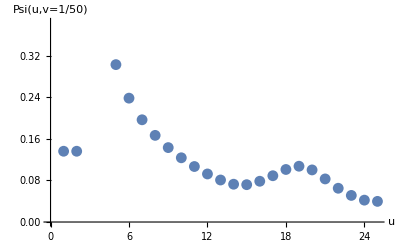

-0.852583 0u+0.931129/u+0.0436034

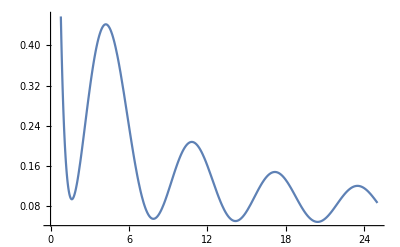

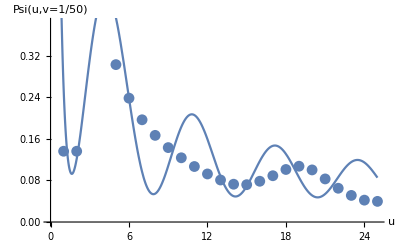

```mathematica
newVecsN[[All,1]]
plt1Dots=ListPlot[Re@%,AxesLabel->{u,"Psi(u,v=1/50)"}]

fit1=Fit[Re@newVecsN[[All,1]],{1,1/u,SphericalBesselJ[0,u]},u]
plt1Fit=Plot[fit1,{u,0,25}]
Show[plt1Dots,plt1Fit]
```

```mathematica
ListPlot3D[newVecsN//Transpose]
ListPlot3D[Re@transformedData]
```

-Graphics3D-

-Graphics3D-

{0.0101126-0.103265 ⅈ,0.0101126+0.103265 ⅈ,0.000518716+0. ⅈ,0.00138397+0. ⅈ,0.00283256+0. ⅈ,0.00518821+0. ⅈ,0.00897837+0. ⅈ,0.0151394+0. ⅈ,0.0256398+0. ⅈ,0.0459482+0. ⅈ,0.100761+0. ⅈ,0.929292+0. ⅈ,0.183047+0. ⅈ,0.0919791+0. ⅈ,0.0654549+0. ⅈ,0.0548146+0. ⅈ,0.0472047+0. ⅈ,0.0409237+0. ⅈ,0.0349799+0. ⅈ,0.0274363+0. ⅈ,0.0197886+0. ⅈ,0.0140928+0. ⅈ,0.0105704+0. ⅈ,0.00867491+0. ⅈ,0.00861589+0. ⅈ}

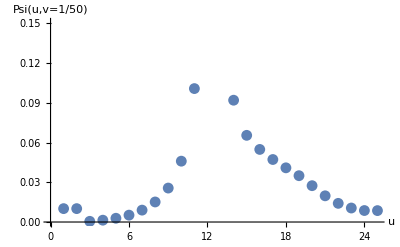

(0.00411467 u)/((u-12)^2+0.5)+0.00178398 u+0.0176889

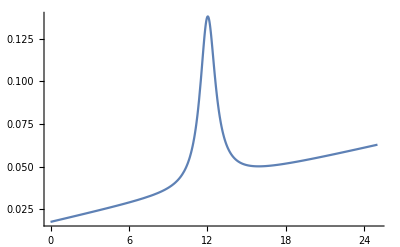

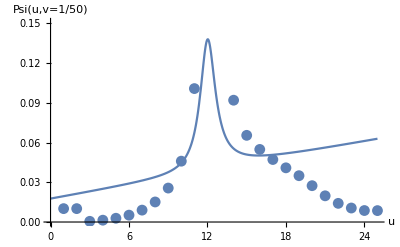

```mathematica
newVecsN[[All,11]]
plt1Dots=ListPlot[Re@%,AxesLabel->{u,"Psi(u,v=1/50)"}]

fit1=Fit[Re@newVecsN[[All,13]],{1,u,u/(0.5+(u-12)^2)},u]
plt1Fit=Plot[fit1,{u,0,25}]
Show[plt1Dots,plt1Fit]
```

```mathematica
newVecsN[[All,1]]
```

{0.136213-0.127328 ⅈ,0.136213+0.127328 ⅈ,0.716258+0. ⅈ,0.420759+0. ⅈ,0.302942+0. ⅈ,0.238395+0. ⅈ,0.196773+0. ⅈ,0.166772+0. ⅈ,0.143231+0. ⅈ,0.12362+0. ⅈ,0.106811+0. ⅈ,0.0924923+0. ⅈ,0.080862+0. ⅈ,0.0727496+0. ⅈ,0.0718659+0. ⅈ,0.0784616+0. ⅈ,0.0890852+0. ⅈ,0.101109+0. ⅈ,0.107389+0. ⅈ,0.100271+0. ⅈ,0.0829258+0. ⅈ,0.0649799+0. ⅈ,0.0511982+0. ⅈ,0.0420892+0. ⅈ,0.0397215+0. ⅈ}

0.117124+0.218842/u

P_nn^(1,1)(2 u-1)

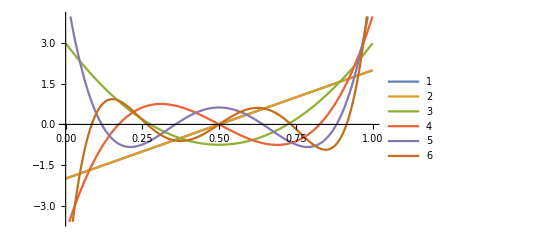

```mathematica
JacobiP[nn,1,1,2u-1]
Plot[{%/.nn->1,%/.nn->1,%/.nn->2,%/.nn->3,%/.nn->4,%/.nn->5},{u,0,1},PlotLegends->Automatic]
```

{0.583419+0. ⅈ,0.583419+0. ⅈ,0.000167711+0. ⅈ,0.000415416+0. ⅈ,0.000703299+0. ⅈ,0.00104976+0. ⅈ,0.00151244+0. ⅈ,0.0021769+0. ⅈ,0.00313885+0. ⅈ,0.00448451+0. ⅈ,0.00628163+0. ⅈ,0.00859856+0. ⅈ,0.0115767+0. ⅈ,0.0156615+0. ⅈ,0.0227764+0. ⅈ,0.0354051+0. ⅈ,0.0556412+0. ⅈ,0.0853019+0. ⅈ,0.119999+0. ⅈ,0.147416+0. ⅈ,0.162417+0. ⅈ,0.174432+0. ⅈ,0.197882+0. ⅈ,0.260358+0. ⅈ,0.581698+0. ⅈ}

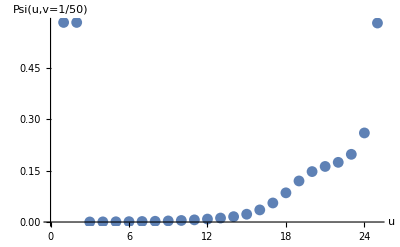

```mathematica
newVecsN[[All,25]]
ListPlot[Re@%,AxesLabel->{u,"Psi(u,v=1/50)"}]
```

```mathematica
anomDimNxN/.Ca->3/.Cf->4/3/.alphaMS->1/.LQ->0
%//N
{vvals,vvecs}=Eigensystem[%]

(* fix the eigen vector signs by diagonal *)
newVecsN=ConstantArray[0,{nN,nN}];

For[i=1,i≤nN,i++,
indMax=i;
newVecsN[[All,i]]=Sign[vvecs[[All,i]]]*vvecs[[All,i]];
]


(* put into a 1D array of (x,y,z) *)
transformedData=ConstantArray[0,{25*25,3}];

For[j=1,j≤nN,j++,
For[i=1,i≤nN,i++,
transformedData[[(j-1)25+i,All]]={i/25-1/50,j/25-1/50,newVecsN[[i,j]]};
]
]
```

(1)
 |  |  |  |

(-1.69988 | -0.143836 | -0.278449 | -0.333564 | -0.363765 | -0.382868 | -0.396053 | -0.405704 | -0.413077 | -0.418894 | -0.423601 | -0.42749 | -0.430757 | -0.433541 | -0.435943 | -0.438038 | -0.439883 | -0.441522 | -0.44299 | -0.444318 | -0.445532 | -0.446663 | -0.447756 | -0.448946 | -0.451136
-0.136402 | -1.68146 | -0.267066 | -0.319936 | -0.348909 | -0.367238 | -0.379891 | -0.389155 | -0.396234 | -0.401822 | -0.406347 | -0.410088 | -0.413234 | -0.41592 | -0.418242 | -0.420273 | -0.42207 | -0.423675 | -0.425128 | -0.426463 | -0.427716 | -0.428941 | -0.430244 | -0.43192 | -0.434028
-0.25298 | -0.253736 | -1.52249 | -0.305442 | -0.333187 | -0.350742 | -0.362863 | -0.37174 | -0.378525 | -0.383884 | -0.388227 | -0.39182 | -0.394846 | -0.397433 | -0.399675 | -0.401643 | -0.403391 | -0.404964 | -0.406401 | -0.407743 | -0.409035 | -0.410353 | -0.411835 | -0.413442 | -0.416228
-0.287493 | -0.28822 | -0.289011 | -1.38698 | -0.316521 | -0.333302 | -0.34489 | -0.35338 | -0.359872 | -0.365002 | -0.369162 | -0.372608 | -0.375513 | -0.378002 | -0.380164 | -0.382068 | -0.383767 | -0.385307 | -0.38673 | -0.388078 | -0.389409 | -0.390804 | -0.392221 | -0.394639 | -0.400589
-0.295549 | -0.296246 | -0.297005 | -0.297835 | -1.27024 | -0.314827 | -0.325883 | -0.333985 | -0.340184 | -0.345085 | -0.349063 | -0.352361 | -0.355146 | -0.357536 | -0.359618 | -0.361458 | -0.363109 | -0.364616 | -0.366023 | -0.367379 | -0.368738 | -0.370068 | -0.372305 | -0.377244 | -0.387866
-0.291143 | -0.291811 | -0.292537 | -0.293332 | -0.294204 | -1.16666 | -0.305738 | -0.313453 | -0.319358 | -0.32403 | -0.327825 | -0.330976 | -0.33364 | -0.335932 | -0.337934 | -0.33971 | -0.341312 | -0.342787 | -0.344179 | -0.345534 | -0.346827 | -0.348953 | -0.353408 | -0.361702 | -0.378438
-0.279438 | -0.280076 | -0.280771 | -0.28153 | -0.282364 | -0.283283 | -1.07237 | -0.291662 | -0.297274 | -0.301717 | -0.30533 | -0.308332 | -0.310877 | -0.31307 | -0.314991 | -0.316704 | -0.318258 | -0.3197 | -0.321071 | -0.322356 | -0.324409 | -0.32855 | -0.335783 | -0.34824 | -0.372505
-0.26273 | -0.263338 | -0.264001 | -0.264725 | -0.26552 | -0.266396 | -0.267368 | -0.984707 | -0.273792 | -0.278006 | -0.281436 | -0.284291 | -0.286715 | -0.288809 | -0.290651 | -0.2923 | -0.293805 | -0.29521 | -0.296507 | -0.29851 | -0.302416 | -0.308982 | -0.31954 | -0.336953 | -0.37015
-0.242133 | -0.242712 | -0.243342 | -0.244031 | -0.244788 | -0.245622 | -0.246546 | -0.247576 | -0.901747 | -0.252732 | -0.255979 | -0.258687 | -0.26099 | -0.262986 | -0.264747 | -0.266332 | -0.267786 | -0.269111 | -0.27108 | -0.274795 | -0.28087 | -0.290265 | -0.304687 | -0.327846 | -0.371372
-0.218189 | -0.218739 | -0.219337 | -0.219991 | -0.220709 | -0.2215 | -0.222377 | -0.223355 | -0.224451 | -0.822029 | -0.228764 | -0.231324 | -0.233507 | -0.235404 | -0.237085 | -0.238603 | -0.239969 | -0.241918 | -0.245471 | -0.251152 | -0.259711 | -0.272333 | -0.291153 | -0.320841 | -0.37609
-0.191119 | -0.191639 | -0.192205 | -0.192824 | -0.193504 | -0.194253 | -0.195083 | -0.196007 | -0.197045 | -0.198216 | -0.744379 | -0.201967 | -0.20403 | -0.205828 | -0.207427 | -0.208847 | -0.210787 | -0.214199 | -0.219544 | -0.227442 | -0.238794 | -0.25504 | -0.27879 | -0.315788 | -0.384152
-0.160934 | -0.161425 | -0.161959 | -0.162542 | -0.163183 | -0.163889 | -0.164672 | -0.165545 | -0.166523 | -0.167628 | -0.168885 | -0.667789 | -0.172273 | -0.173971 | -0.17546 | -0.177401 | -0.180688 | -0.185736 | -0.193078 | -0.203442 | -0.217895 | -0.238158 | -0.26737 | -0.312458 | -0.395326
-0.127483 | -0.127944 | -0.128446 | -0.128995 | -0.129597 | -0.130261 | -0.130997 | -0.131816 | -0.132736 | -0.133774 | -0.134956 | -0.136312 | -0.591334 | -0.139457 | -0.141411 | -0.144586 | -0.149364 | -0.15622 | -0.165763 | -0.17884 | -0.196701 | -0.221374 | -0.256576 | -0.310533 | -0.409295
-0.0904679 | -0.0908993 | -0.0913691 | -0.0918826 | -0.0924462 | -0.0930677 | -0.0937564 | -0.0945239 | -0.0953845 | -0.0963562 | -0.0974622 | -0.0987301 | -0.100177 | -0.514564 | -0.105454 | -0.109985 | -0.1164 | -0.125233 | -0.137181 | -0.153217 | -0.17479 | -0.204265 | -0.245985 | -0.30959 | -0.425634
-0.0494303 | -0.0498322 | -0.0502699 | -0.0507483 | -0.0512734 | -0.0518524 | -0.052494 | -0.053209 | -0.0540108 | -0.0549161 | -0.0559444 | -0.0571023 | -0.0589128 | -0.0621057 | -0.440191 | -0.0730465 | -0.0812412 | -0.0922195 | -0.106773 | -0.126014 | -0.151605 | -0.186273 | -0.235039 | -0.309068 | -0.443783
-0.00371676 | -0.00408919 | -0.00449473 | -0.00493801 | -0.00542457 | -0.00596106 | -0.0065556 | -0.00721813 | -0.00796103 | -0.00879802 | -0.00972868 | -0.0112229 | -0.0139432 | -0.0182127 | -0.0244194 | -0.368956 | -0.0431495 | -0.0564418 | -0.073803 | -0.0964921 | -0.126406 | -0.166656 | -0.222997 | -0.308228 | -0.463
0.0475898 | 0.0472469 | 0.0468734 | 0.0464653 | 0.0460173 | 0.0455233 | 0.0449758 | 0.0443658 | 0.0436835 | 0.0429344 | 0.0416984 | 0.0393736 | 0.0356662 | 0.030231 | 0.0226521 | 0.0124137 | -0.301222 | -0.0169047 | -0.0372738 | -0.0636561 | -0.0981955 | -0.14442 | -0.208861 | -0.306071 | -0.482288
0.105788 | 0.105475 | 0.105134 | 0.10476 | 0.104351 | 0.103899 | 0.103399 | 0.102843 | 0.102241 | 0.10122 | 0.0992348 | 0.0960132 | 0.0912421 | 0.0845526 | 0.0754988 | 0.0635267 | 0.0479244 | -0.237506 | 0.00418828 | -0.026131 | -0.0655996 | -0.118188 | -0.191257 | -0.301223 | -0.500271
0.172769 | 0.172486 | 0.172176 | 0.171838 | 0.171467 | 0.171058 | 0.170607 | 0.170125 | 0.169287 | 0.167599 | 0.164807 | 0.160623 | 0.154712 | 0.146681 | 0.13605 | 0.122224 | 0.10444 | 0.081677 | -0.178501 | 0.0180486 | -0.0266526 | -0.0859939 | -0.168217 | -0.291715 | -0.514982
0.251409 | 0.251155 | 0.250878 | 0.250575 | 0.250242 | 0.249878 | 0.249495 | 0.248814 | 0.247393 | 0.24499 | 0.241335 | 0.236124 | 0.228998 | 0.219537 | 0.207227 | 0.191429 | 0.171322 | 0.145811 | 0.113377 | -0.125095 | 0.0215967 | -0.0448876 | -0.136792 | -0.274598 | -0.523471
0.346368 | 0.346143 | 0.345898 | 0.34563 | 0.345339 | 0.34504 | 0.344497 | 0.343318 | 0.341271 | 0.338104 | 0.333532 | 0.327228 | 0.318813 | 0.307835 | 0.293744 | 0.275854 | 0.253285 | 0.22486 | 0.188953 | 0.143179 | -0.0783484 | 0.00986893 | -0.0922425 | -0.245134 | -0.520998
0.46594 | 0.465744 | 0.465531 | 0.465301 | 0.465074 | 0.464655 | 0.463699 | 0.461985 | 0.459273 | 0.455294 | 0.449748 | 0.442288 | 0.432509 | 0.419927 | 0.403954 | 0.383854 | 0.358682 | 0.327178 | 0.287598 | 0.237399 | 0.172621 | -0.0392467 | -0.0261968 | -0.194949 | -0.499192
0.627208 | 0.627042 | 0.626864 | 0.626699 | 0.626394 | 0.625647 | 0.624247 | 0.621963 | 0.618543 | 0.613706 | 0.607132 | 0.598452 | 0.587234 | 0.572962 | 0.555006 | 0.532578 | 0.504663 | 0.469913 | 0.426461 | 0.371594 | 0.301104 | 0.207881 | -0.0073274 | -0.106879 | -0.440888
0.876151 | 0.876019 | 0.875911 | 0.875711 | 0.875163 | 0.874061 | 0.872185 | 0.869296 | 0.86513 | 0.859388 | 0.851731 | 0.841767 | 0.829037 | 0.812988 | 0.792948 | 0.768073 | 0.737276 | 0.699114 | 0.651592 | 0.591813 | 0.515308 | 0.414575 | 0.275369 | 0.0285125 | -0.300024
1.53725 | 1.5372 | 1.5371 | 1.53674 | 1.53593 | 1.53444 | 1.53206 | 1.52853 | 1.52358 | 1.51688 | 1.50809 | 1.49678 | 1.48246 | 1.46455 | 1.44233 | 1.41489 | 1.38107 | 1.33933 | 1.28754 | 1.2226 | 1.13978 | 1.03115 | 0.881842 | 0.658123 | 0.307716)

(-1.92385+4.80636 ⅈ | -1.92385-4.80636 ⅈ | -1.55053 | -1.27452 | -1.10406 | -0.978815 | -0.87917 | -0.796041 | -0.724395 | -0.661108 | -0.604078 | -0.55181 | -0.503181 | -0.457258 | -0.413411 | -0.372945 | -0.335357 | -0.30037 | -0.267629 | -0.235843 | -0.20311 | -0.168198 | -0.129996 | -0.0855426 | -0.0217362
{-0.173442+0.0684412 ⅈ,-0.166206+0.0664566 ⅈ,-0.158552+0.0642899 ⅈ,-0.15042+0.0623782 ⅈ,-0.14177+0.0609654 ⅈ,-0.132569+0.0602254 ⅈ,-0.122782+0.0602823 ⅈ,-0.112372+0.0612213 ⅈ,-0.101291+0.0630939 ⅈ,-0.0894787+0.0659223 ⅈ,-0.0768606+0.0697014 ⅈ,-0.0633404+0.0743996 ⅈ,-0.0487951+0.0799584 ⅈ,-0.0330664+0.0862902 ⅈ,-0.015949+0.093274 ⅈ,0.00282754+0.100747 ⅈ,0.0236267+0.108491 ⅈ,0.0469502+0.116209 ⅈ,0.0735161+0.123485 ⅈ,0.104403+0.129703 ⅈ,0.141341+0.133891 ⅈ,0.187381+0.134351 ⅈ,0.248755+0.127627 ⅈ,0.342092+0.104488 ⅈ,0.583419+0. ⅈ} | {-0.173442-0.0684412 ⅈ,-0.166206-0.0664566 ⅈ,-0.158552-0.0642899 ⅈ,-0.15042-0.0623782 ⅈ,-0.14177-0.0609654 ⅈ,-0.132569-0.0602254 ⅈ,-0.122782-0.0602823 ⅈ,-0.112372-0.0612213 ⅈ,-0.101291-0.0630939 ⅈ,-0.0894787-0.0659223 ⅈ,-0.0768606-0.0697014 ⅈ,-0.0633404-0.0743996 ⅈ,-0.0487951-0.0799584 ⅈ,-0.0330664-0.0862902 ⅈ,-0.015949-0.093274 ⅈ,0.00282754-0.100747 ⅈ,0.0236267-0.108491 ⅈ,0.0469502-0.116209 ⅈ,0.0735161-0.123485 ⅈ,0.104403-0.129703 ⅈ,0.141341-0.133891 ⅈ,0.187381-0.134351 ⅈ,0.248755-0.127627 ⅈ,0.342092-0.104488 ⅈ,0.583419+0. ⅈ} | {0.716258+0. ⅈ,-0.697792+0. ⅈ,-0.00673525+0. ⅈ,-0.00278299+0. ⅈ,-0.00170241+0. ⅈ,-0.00122884+0. ⅈ,-0.000966834+0. ⅈ,-0.000799222+0. ⅈ,-0.000680726+0. ⅈ,-0.000590727+0. ⅈ,-0.000518716+0. ⅈ,-0.000458877+0. ⅈ,-0.000407774+0. ⅈ,-0.000363258+0. ⅈ,-0.000323898+0. ⅈ,-0.000288666+0. ⅈ,-0.000256739+0. ⅈ,-0.00022736+0. ⅈ,-0.00019971+0. ⅈ,-0.00017276+0. ⅈ,-0.000145029+0. ⅈ,-0.000114081+0. ⅈ,-0.0000751758+0. ⅈ,-0.0000141349+0. ⅈ,0.000167711+0. ⅈ} | {-0.420759+0. ⅈ,-0.4248+0. ⅈ,0.801334+0. ⅈ,0.0165757+0. ⅈ,0.00702688+0. ⅈ,0.00429096+0. ⅈ,0.00306407+0. ⅈ,0.0023769+0. ⅈ,0.00193464+0. ⅈ,0.00162146+0. ⅈ,0.00138397+0. ⅈ,0.00119474+0. ⅈ,0.00103849+0. ⅈ,0.000906138+0. ⅈ,0.000791935+0. ⅈ,0.000692005+0. ⅈ,0.000603476+0. ⅈ,0.000523938+0. ⅈ,0.00045101+0. ⅈ,0.000381899+0. ⅈ,0.00031274+0. ⅈ,0.000237292+0. ⅈ,0.000141422+0. ⅈ,-0.0000254881+0. ⅈ,-0.000415416+0. ⅈ} | {0.302942+0. ⅈ,0.299938+0. ⅈ,0.318487+0. ⅈ,-0.846002+0. ⅈ,-0.0283937+0. ⅈ,-0.0124892+0. ⅈ,-0.00771266+0. ⅈ,-0.00550729+0. ⅈ,-0.00424632+0. ⅈ,-0.00342241+0. ⅈ,-0.00283256+0. ⅈ,-0.002382+0. ⅈ,-0.0020215+0. ⅈ,-0.00172339+0. ⅈ,-0.00147106+0. ⅈ,-0.00125386+0. ⅈ,-0.00106442+0. ⅈ,-0.000897012+0. ⅈ,-0.00074643+0. ⅈ,-0.000606989+0. ⅈ,-0.000471149+0. ⅈ,-0.000324852+0. ⅈ,-0.000125631+0. ⅈ,0.0000994756+0. ⅈ,0.000703299+0. ⅈ} | {-0.238395+0. ⅈ,-0.234408+0. ⅈ,-0.23761+0. ⅈ,-0.269198+0. ⅈ,0.869972+0. ⅈ,0.0417572+0. ⅈ,0.0190056+0. ⅈ,0.0118783+0. ⅈ,0.00849033+0. ⅈ,0.00650806+0. ⅈ,0.00518821+0. ⅈ,0.00422879+0. ⅈ,0.00348712+0. ⅈ,0.00288846+0. ⅈ,0.00239047+0. ⅈ,0.00196749+0. ⅈ,0.00160282+0. ⅈ,0.00128449+0. ⅈ,0.00100257+0. ⅈ,0.000747146+0. ⅈ,0.000503732+0. ⅈ,0.000234539+0. ⅈ,0.0000447298+0. ⅈ,-0.000108759+0. ⅈ,-0.00104976+0. ⅈ} | {-0.196773+0. ⅈ,-0.19278+0. ⅈ,-0.19242+0. ⅈ,-0.200934+0. ⅈ,-0.245297+0. ⅈ,0.884345+0. ⅈ,0.0561982+0. ⅈ,0.0263267+0. ⅈ,0.0165964+0. ⅈ,0.0118344+0. ⅈ,0.00897837+0. ⅈ,0.00703559+0. ⅈ,0.00559772+0. ⅈ,0.00447011+0. ⅈ,0.00355015+0. ⅈ,0.0027795+0. ⅈ,0.00212261+0. ⅈ,0.0015561+0. ⅈ,0.00106276+0. ⅈ,0.000625436+0. ⅈ,0.000209996+0. ⅈ,8.36042×10^-6+0. ⅈ,0.0000479262+0. ⅈ,-0.0000318608+0. ⅈ,-0.00151244+0. ⅈ} | {0.166772+0. ⅈ,0.163016+0. ⅈ,0.161453+0. ⅈ,0.164178+0. ⅈ,0.177405+0. ⅈ,0.234484+0. ⅈ,-0.893851+0. ⅈ,-0.0709397+0. ⅈ,-0.0339525+0. ⅈ,-0.0214451+0. ⅈ,-0.0151394+0. ⅈ,-0.0112567+0. ⅈ,-0.00855483+0. ⅈ,-0.00651757+0. ⅈ,-0.00489775+0. ⅈ,-0.00356502+0. ⅈ,-0.00244579+0. ⅈ,-0.00149615+0. ⅈ,-0.00068649+0. ⅈ,0.0000174531+0. ⅈ,0.000317279+0. ⅈ,0.000132159+0. ⅈ,-0.000164284+0. ⅈ,-0.000123385+0. ⅈ,0.0021769+0. ⅈ} | {-0.143231+0. ⅈ,-0.139783+0. ⅈ,-0.137791+0. ⅈ,-0.138287+0. ⅈ,-0.143599+0. ⅈ,-0.16098+0. ⅈ,-0.230106+0. ⅈ,0.90123+0. ⅈ,0.08469+0. ⅈ,0.0409714+0. ⅈ,0.0256398+0. ⅈ,0.0176718+0. ⅈ,0.0126329+0. ⅈ,0.00904849+0. ⅈ,0.00630285+0. ⅈ,0.00410183+0. ⅈ,0.00229341+0. ⅈ,0.000794859+0. ⅈ,-0.000447361+0. ⅈ,-0.00100445+0. ⅈ,-0.000750113+0. ⅈ,-0.00014771+0. ⅈ,0.000399761+0. ⅈ,0.000319076+0. ⅈ,-0.00313885+0. ⅈ} | {0.12362+0. ⅈ,0.120503+0. ⅈ,0.118405+0. ⅈ,0.117893+0. ⅈ,0.120036+0. ⅈ,0.127422+0. ⅈ,0.148148+0. ⅈ,0.227238+0. ⅈ,-0.908542+0. ⅈ,-0.0955116+0. ⅈ,-0.0459482+0. ⅈ,-0.0279473+0. ⅈ,-0.0183068+0. ⅈ,-0.0120562+0. ⅈ,-0.00753251+0. ⅈ,-0.00404455+0. ⅈ,-0.00127042+0. ⅈ,0.000948559+0. ⅈ,0.00204103+0. ⅈ,0.00185822+0. ⅈ,0.00103045+0. ⅈ,0.0000148267+0. ⅈ,-0.000734179+0. ⅈ,-0.000492045+0. ⅈ,0.00448451+0. ⅈ} | {-0.106811+0. ⅈ,-0.104021+0. ⅈ,-0.101971+0. ⅈ,-0.100982+0. ⅈ,-0.101595+0. ⅈ,-0.104941+0. ⅈ,-0.113743+0. ⅈ,-0.136542+0. ⅈ,-0.221365+0. ⅈ,0.917498+0. ⅈ,0.100761+0. ⅈ,0.0468943+0. ⅈ,0.0266874+0. ⅈ,0.0155632+0. ⅈ,0.00821543+0. ⅈ,0.00287646+0. ⅈ,-0.0011661+0. ⅈ,-0.00329201+0. ⅈ,-0.00342435+0. ⅈ,-0.00250059+0. ⅈ,-0.00111134+0. ⅈ,0.000268635+0. ⅈ,0.00112565+0. ⅈ,0.00056507+0. ⅈ,-0.00628163+0. ⅈ} | {-0.0924923+0. ⅈ,-0.0900094+0. ⅈ,-0.0880744+0. ⅈ,-0.0868698+0. ⅈ,-0.0866727+0. ⅈ,-0.0880223+0. ⅈ,-0.0920307+0. ⅈ,-0.10136+0. ⅈ,-0.12436+0. ⅈ,-0.208061+0. ⅈ,0.929292+0. ⅈ,0.0969145+0. ⅈ,0.0412351+0. ⅈ,0.0197696+0. ⅈ,0.00771456+0. ⅈ,-0.0002523+0. ⅈ,-0.00444852+0. ⅈ,-0.00533692+0. ⅈ,-0.00452012+0. ⅈ,-0.00286793+0. ⅈ,-0.000966897+0. ⅈ,0.000688552+0. ⅈ,0.00152312+0. ⅈ,0.000459173+0. ⅈ,-0.00859856+0. ⅈ} | {-0.080862+0. ⅈ,-0.0786416+0. ⅈ,-0.076837+0. ⅈ,-0.0755415+0. ⅈ,-0.0748874+0. ⅈ,-0.0751311+0. ⅈ,-0.0767545+0. ⅈ,-0.0807364+0. ⅈ,-0.0894043+0. ⅈ,-0.110025+0. ⅈ,-0.183047+0. ⅈ,0.944041+0. ⅈ,0.0788119+0. ⅈ,0.0255002+0. ⅈ,0.00456618+0. ⅈ,-0.00478423+0. ⅈ,-0.00743201+0. ⅈ,-0.00707029+0. ⅈ,-0.0052804+0. ⅈ,-0.00292411+0. ⅈ,-0.000583127+0. ⅈ,0.00123218+0. ⅈ,0.00188339+0. ⅈ,0.0000947967+0. ⅈ,-0.0115767+0. ⅈ} | {-0.0727496+0. ⅈ,-0.0707127+0. ⅈ,-0.0690034+0. ⅈ,-0.0676523+0. ⅈ,-0.0667028+0. ⅈ,-0.0662589+0. ⅈ,-0.0665115+0. ⅈ,-0.0678085+0. ⅈ,-0.0708422+0. ⅈ,-0.0772338+0. ⅈ,-0.0919791+0. ⅈ,-0.142088+0. ⅈ,0.959669+0. ⅈ,0.036666+0. ⅈ,-0.00105571+0. ⅈ,-0.0094353+0. ⅈ,-0.0103795+0. ⅈ,-0.00857478+0. ⅈ,-0.0057142+0. ⅈ,-0.00264161+0. ⅈ,0.0000802223+0. ⅈ,0.00192907+0. ⅈ,0.00219321+0. ⅈ,-0.000642287+0. ⅈ,-0.0156615+0. ⅈ} | {0.0718659+0. ⅈ,0.0698188+0. ⅈ,0.0680563+0. ⅈ,0.0665561+0. ⅈ,0.0652955+0. ⅈ,0.064282+0. ⅈ,0.0635487+0. ⅈ,0.0631558+0. ⅈ,0.0632003+0. ⅈ,0.0638495+0. ⅈ,0.0654549+0. ⅈ,0.0690146+0. ⅈ,0.079242+0. ⅈ,-0.969461+0. ⅈ,0.00838293+0. ⅈ,0.0161653+0. ⅈ,0.0143143+0. ⅈ,0.0103477+0. ⅈ,0.00597599+0. ⅈ,0.00194146+0. ⅈ,-0.00123929+0. ⅈ,-0.00301843+0. ⅈ,-0.00255029+0. ⅈ,0.00209301+0. ⅈ,0.0227764+0. ⅈ} | {0.0784616+0. ⅈ,0.0761923+0. ⅈ,0.0741983+0. ⅈ,0.0723956+0. ⅈ,0.070691+0. ⅈ,0.069005+0. ⅈ,0.0672508+0. ⅈ,0.0653036+0. ⅈ,0.0629466+0. ⅈ,0.0597573+0. ⅈ,0.0548146+0. ⅈ,0.0456596+0. ⅈ,0.0322715+0. ⅈ,0.0170157+0. ⅈ,-0.970561+0. ⅈ,0.0301944+0. ⅈ,0.01991+0. ⅈ,0.0119886+0. ⅈ,0.0053686+0. ⅈ,0.000103351+0. ⅈ,-0.00348889+0. ⅈ,-0.00484223+0. ⅈ,-0.00288537+0. ⅈ,0.00500996+0. ⅈ,0.0354051+0. ⅈ} | {-0.0890852+0. ⅈ,-0.0864729+0. ⅈ,-0.0841387+0. ⅈ,-0.0819132+0. ⅈ,-0.0796092+0. ⅈ,-0.0770421+0. ⅈ,-0.0739966+0. ⅈ,-0.0701774+0. ⅈ,-0.0651225+0. ⅈ,-0.0580222+0. ⅈ,-0.0472047+0. ⅈ,-0.0331974+0. ⅈ,-0.0183955+0. ⅈ,-0.00248553+0. ⅈ,0.0176844+0. ⅈ,0.96563+0. ⅈ,-0.025081+0. ⅈ,-0.00983387+0. ⅈ,-0.00102047+0. ⅈ,0.00482697+0. ⅈ,0.00792968+0. ⅈ,0.0077119+0. ⅈ,0.00276192+0. ⅈ,-0.0105714+0. ⅈ,-0.0556412+0. ⅈ} | {-0.101109+0. ⅈ,-0.0981056+0. ⅈ,-0.095385+0. ⅈ,-0.0926588+0. ⅈ,-0.0896123+0. ⅈ,-0.0859249+0. ⅈ,-0.0812306+0. ⅈ,-0.0750595+0. ⅈ,-0.0667325+0. ⅈ,-0.0550973+0. ⅈ,-0.0409237+0. ⅈ,-0.0263401+0. ⅈ,-0.011773+0. ⅈ,0.00227166+0. ⅈ,0.0150427+0. ⅈ,0.0243277+0. ⅈ,0.956641+0. ⅈ,0.0141841+0. ⅈ,0.0154759+0. ⅈ,0.0171583+0. ⅈ,0.0165072+0. ⅈ,0.011999+0. ⅈ,0.00143458+0. ⅈ,-0.0202962+0. ⅈ,-0.0853019+0. ⅈ} | {0.107389+0. ⅈ,0.104161+0. ⅈ,0.101202+0. ⅈ,0.0980901+0. ⅈ,0.0943637+0. ⅈ,0.0895526+0. ⅈ,0.0831411+0. ⅈ,0.0745171+0. ⅈ,0.0628635+0. ⅈ,0.0490718+0. ⅈ,0.0349799+0. ⅈ,0.0209998+0. ⅈ,0.00769766+0. ⅈ,-0.00411929+0. ⅈ,-0.0130358+0. ⅈ,-0.0154728+0. ⅈ,0.00603666+0. ⅈ,-0.946025+0. ⅈ,-0.0763042+0. ⅈ,-0.0461574+0. ⅈ,-0.0317648+0. ⅈ,-0.0175551+0. ⅈ,0.00205462+0. ⅈ,0.0343773+0. ⅈ,0.119999+0. ⅈ} | {0.100271+0. ⅈ,0.0972207+0. ⅈ,0.0943984+0. ⅈ,0.091274+0. ⅈ,0.0872707+0. ⅈ,0.0818037+0. ⅈ,0.0742641+0. ⅈ,0.0640044+0. ⅈ,0.051946+0. ⅈ,0.0396702+0. ⅈ,0.0274363+0. ⅈ,0.0156608+0. ⅈ,0.00489687+0. ⅈ,-0.0040793+0. ⅈ,-0.010011+0. ⅈ,-0.01034+0. ⅈ,0.00231698+0. ⅈ,0.0686554+0. ⅈ,-0.941277+0. ⅈ,-0.122001+0. ⅈ,-0.0578595+0. ⅈ,-0.0238662+0. ⅈ,0.00794413+0. ⅈ,0.0499589+0. ⅈ,0.147416+0. ⅈ} | {0.0829258+0. ⅈ,0.0803728+0. ⅈ,0.0779916+0. ⅈ,0.0751951+0. ⅈ,0.0713383+0. ⅈ,0.0657684+0. ⅈ,0.0578446+0. ⅈ,0.0483974+0. ⅈ,0.0388004+0. ⅈ,0.0291762+0. ⅈ,0.0197886+0. ⅈ,0.0109817+0. ⅈ,0.00319438+0. ⅈ,-0.00298593+0. ⅈ,-0.0066897+0. ⅈ,-0.00641209+0. ⅈ,0.00110923+0. ⅈ,0.0257779+0. ⅈ,0.125371+0. ⅈ,-0.945465+0. ⅈ,-0.120595+0. ⅈ,-0.0337029+0. ⅈ,0.015783+0. ⅈ,0.0652297+0. ⅈ,0.162417+0. ⅈ} | {-0.0649799+0. ⅈ,-0.062955+0. ⅈ,-0.0610576+0. ⅈ,-0.0586566+0. ⅈ,-0.055031+0. ⅈ,-0.0494162+0. ⅈ,-0.0424304+0. ⅈ,-0.03529+0. ⅈ,-0.0280677+0. ⅈ,-0.0209311+0. ⅈ,-0.0140928+0. ⅈ,-0.00780957+0. ⅈ,-0.00239351+0. ⅈ,0.00176126+0. ⅈ,0.00412142+0. ⅈ,0.0038824+0. ⅈ,-0.000374738+0. ⅈ,-0.0117625+0. ⅈ,-0.0397514+0. ⅈ,-0.139108+0. ⅈ,0.954336+0. ⅈ,0.0668583+0. ⅈ,-0.0266044+0. ⅈ,-0.0846839+0. ⅈ,-0.174432+0. ⅈ} | {0.0511982+0. ⅈ,0.0495878+0. ⅈ,0.0480855+0. ⅈ,0.0459576+0. ⅈ,0.0422207+0. ⅈ,0.0371618+0. ⅈ,0.031861+0. ⅈ,0.0264151+0. ⅈ,0.0209519+0. ⅈ,0.015616+0. ⅈ,0.0105704+0. ⅈ,0.0060006+0. ⅈ,0.00212004+0. ⅈ,-0.000819524+0. ⅈ,-0.00250857+0. ⅈ,-0.00253937+0. ⅈ,-0.000316093+0. ⅈ,0.00517145+0. ⅈ,0.0160371+0. ⅈ,0.0383687+0. ⅈ,0.104627+0. ⅈ,-0.956986+0. ⅈ,0.0459924+0. ⅈ,0.122363+0. ⅈ,0.197882+0. ⅈ} | {0.0420892+0. ⅈ,0.0407787+0. ⅈ,0.0395872+0. ⅈ,0.0372876+0. ⅈ,0.0336847+0. ⅈ,0.0296903+0. ⅈ,0.0254628+0. ⅈ,0.0211283+0. ⅈ,0.0168048+0. ⅈ,0.0126117+0. ⅈ,0.00867491+0. ⅈ,0.00512902+0. ⅈ,0.00211856+0. ⅈ,-0.000200396+0. ⅈ,-0.00165804+0. ⅈ,-0.00206699+0. ⅈ,-0.00121589+0. ⅈ,0.00114091+0. ⅈ,0.00529795+0. ⅈ,0.0116113+0. ⅈ,0.0204468+0. ⅈ,0.0313268+0. ⅈ,-0.927432+0. ⅈ,0.245887+0. ⅈ,0.260358+0. ⅈ} | {-0.0397215+0. ⅈ,-0.038691+0. ⅈ,-0.0373194+0. ⅈ,-0.0346968+0. ⅈ,-0.0314614+0. ⅈ,-0.0278401+0. ⅈ,-0.0239869+0. ⅈ,-0.020027+0. ⅈ,-0.0160737+0. ⅈ,-0.0122349+0. ⅈ,-0.00861589+0. ⅈ,-0.00531964+0. ⅈ,-0.00244483+0. ⅈ,-0.0000819837+0. ⅈ,0.00169348+0. ⅈ,0.00283383+0. ⅈ,0.00334315+0. ⅈ,0.00332746+0. ⅈ,0.00310971+0. ⅈ,0.00352592+0. ⅈ,0.00682161+0. ⅈ,0.0201242+0. ⅈ,0.0766076+0. ⅈ,0.803942+0. ⅈ,-0.581698+0. ⅈ})

```mathematica
ListPlot3D[newVecsN//Transpose,AxesLabel->{u,v}]
ListPlot3D[transformedData,AxesLabel->{u,v}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Fit[Re@transformedData,{1,u,1/u,v,1/v,Exp[-(u-v)^2/(2*(0.05)^2)]},{u,v}]
plt2=Plot3D[%,{u,0,1},{v,0,1},AxesLabel->{u,v}]
```

0.0533158+0.314442 ⅇ^(-200. (u-v)^2)+0.0102244 u-0.000201323/u-0.0508974 v+0.00170174/v

-Graphics3D-

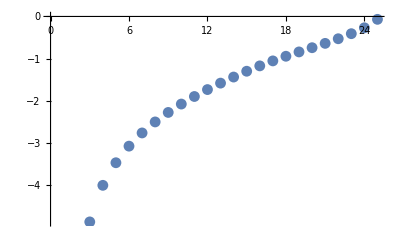

0.0194657 x+1.85716 log(x)-6.63121

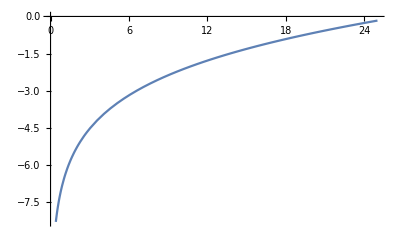

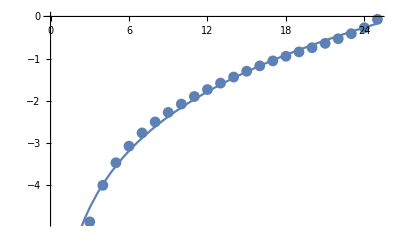

```mathematica
plt1=ListPlot[vvals*Pi]
myFit=Fit[Re@vvals*Pi,{1,x,Log[x]},x]
plt2=Plot[myFit,{x,0,25}]
Show[plt1,plt2]
```

```mathematica
tmp[[1]]
tmp[[1]]/.u->(1)/nnN-3/(4*nnN)/.v->50/nnN-1/(4*nnN)//FullSimplify
tmp[[2]]/.u->(1)/nnN-3/(4*nnN)/.v->50/nnN-1/(4*nnN)//FullSimplify
tmp[[3]]/.u->(1)/nnN-3/(4*nnN)/.v->50/nnN-1/(4*nnN)//FullSimplify
```

((1-u) α_OverBar[MS] (C_F-C_A/2) ((u v -u-v+1)/((1-u) (1-v))+((u v+u+v-1) u+v-1)/(u v)))/π

-(199 0 α_OverBar[MS] (C_A-2 C_F))/(200 π)

0

(199 C_A α_OverBar[MS] (1-40000/199 ((99/100-β)/198-1/2 log(199/198) 100 β-99)))/(400 π)

```mathematica
tmp
```

(α_OverBar[MS] u-v (1/2 C_A (log(v/(1-v))+1)+C_F (LQ+log(1-v)-3/2)))/π+((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)+((1-u) α_OverBar[MS] (C_F-C_A/2) ((u v -u-v+1)/((1-u) (1-v))+((u v+u+v-1) u+v-1)/(u v)))/π

```mathematica
tmp=anomDim2a1/.ubar->1-u/.vbar->1-v

anomDimPointwise=ConstantArray[0,{nnN,nnN}]

nnN=50

For[i=1,i≤nnN,i++,
For[j=1,j≤nnN,j++,
anomDimPointwise[[i,j]]=tmp/.u->(i)/nnN-3/(4*nnN)/.v->(j)/nnN-2/(4*nnN)//FullSimplify;
];
Print[i];
];
```

(α_OverBar[MS] u-v (1/2 C_A (log(v/(1-v))+1)+C_F (LQ+log(1-v)-3/2)))/π+((1-u) C_A α_OverBar[MS] (-(-(v-1) log(1-u/v) u-v+β+(log(u-v)+v log((v-1)/(v-u))-u-log(1-v)+1) u-v-β+((1-u) u-v-β)/(u-v)+((1-v) -u+v-β)/(v-u))/((1-u) (1-v))+((-u v-v+1) u-v)/(u (1-v))+((u (-v)-u+1) v-u)/((1-u) v)))/(2 π)+((1-u) α_OverBar[MS] (C_F-C_A/2) ((u v -u-v+1)/((1-u) (1-v))+((u v+u+v-1) u+v-1)/(u v)))/π

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

50

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

```mathematica
anomDimPointwise[[All,1]]
anomDimPointwise[[All,1]]/.beta->0
```

{(199 α_OverBar[MS] C_A (19899/199-(20000 (198 1/200-β-198 1-200 β log(2)))/19701))/(400 π)-(α_OverBar[MS] (C_A-2 C_F))/(39600 π),(39 α_OverBar[MS] C_A (3959/99-(4000 ((195-198 log(66)) 200 β-3+65 3/200-β))/3861))/(80 π)-(α_OverBar[MS] (C_A-2 C_F))/(7920 π),(191 α_OverBar[MS] C_A (733/33-(20000 ((191-198 log(198/7)) 7-200 β+(191 7/200-β)/7))/18909))/(400 π)-(α_OverBar[MS] (C_A-2 C_F))/(4400 π),(187 α_OverBar[MS] C_A (19787/1287-(20000 ((187-198 log(18)) 11-200 β+17 11/200-β))/18513))/(400 π)-(13 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(183 α_OverBar[MS] C_A (19783/1683-(20000 ((61 3/40-β)/5-3/5 40 β-3 (-61+66 log(66/5))))/18117))/(400 π)-(17 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(179 α_OverBar[MS] C_A (6593/693-(20000 ((179-198 log(198/19)) 19-200 β+(179 19/200-β)/19))/17721))/(400 π)-(7 α_OverBar[MS] (C_A-2 C_F))/(13200 π),(7 α_OverBar[MS] C_A (791/99-800/693 ((175-198 log(198/23)) 200 β-23+(175 23/200-β)/23)))/(16 π)-(α_OverBar[MS] (C_A-2 C_F))/(1584 π),(171 α_OverBar[MS] C_A (19771/2871-(20000 ((171-198 log(22/3)) 27-200 β+(19 27/200-β)/3))/16929))/(400 π)-(29 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(167 α_OverBar[MS] C_A (599/99-(20000 ((167-198 log(198/31)) 31-200 β+(167 31/200-β)/31))/16533))/(400 π)-(α_OverBar[MS] (C_A-2 C_F))/(1200 π),(163 α_OverBar[MS] C_A (19763/3663-(20000 (1/5 (163-198 log(198/35)) 40 β-7+(163 7/40-β)/35))/16137))/(400 π)-(37 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(159 α_OverBar[MS] C_A (19759/4059-(20000 ((159-198 log(66/13)) 39-200 β+(53 39/200-β)/13))/15741))/(400 π)-(41 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(31 α_OverBar[MS] C_A (439/99-(4000 ((155-198 log(198/43)) 200 β-43+(155 43/200-β)/43))/3069))/(80 π)-(α_OverBar[MS] (C_A-2 C_F))/(880 π),(151 α_OverBar[MS] C_A (19751/4851-(20000 ((151-198 log(198/47)) 47-200 β+(151 47/200-β)/47))/14949))/(400 π)-(49 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(147 α_OverBar[MS] C_A (19747/5247-(20000 ((147-198 log(66/17)) 51-200 β+(49 51/200-β)/17))/14553))/(400 π)-(53 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(143 α_OverBar[MS] C_A (6581/1881-(20000 (11/5 (13-18 log(18/5)) 40 β-11+(13 11/40-β)/5))/14157))/(400 π)-(19 α_OverBar[MS] (C_A-2 C_F))/(13200 π),(139 α_OverBar[MS] C_A (19739/6039-(20000 ((139-198 log(198/59)) 59-200 β+(139 59/200-β)/59))/13761))/(400 π)-(61 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(27 α_OverBar[MS] C_A (3947/1287-(4000 ((135-198 log(22/7)) 200 β-63+(15 63/200-β)/7))/2673))/(80 π)-(13 α_OverBar[MS] (C_A-2 C_F))/(7920 π),(131 α_OverBar[MS] C_A (6577/2277-(20000 ((131-198 log(198/67)) 67-200 β+(131 67/200-β)/67))/12969))/(400 π)-(23 α_OverBar[MS] (C_A-2 C_F))/(13200 π),(127 α_OverBar[MS] C_A (19727/7227-(20000 ((127-198 log(198/71)) 71-200 β+(127 71/200-β)/71))/12573))/(400 π)-(73 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(123 α_OverBar[MS] C_A (163/63-(20000 ((41 3/8-β)/25-3/25 8 β-3 (-41+66 log(66/25))))/12177))/(400 π)-(7 α_OverBar[MS] (C_A-2 C_F))/(3600 π),(119 α_OverBar[MS] C_A (2191/891-(20000 ((119-198 log(198/79)) 79-200 β+(119 79/200-β)/79))/11781))/(400 π)-(9 α_OverBar[MS] (C_A-2 C_F))/(4400 π),(23 α_OverBar[MS] C_A (3943/1683-(4000 ((115-198 log(198/83)) 200 β-83+(115 83/200-β)/83))/2277))/(80 π)-(17 α_OverBar[MS] (C_A-2 C_F))/(7920 π),(111 α_OverBar[MS] C_A (19711/8811-(20000 ((111-198 log(66/29)) 87-200 β+(37 87/200-β)/29))/10989))/(400 π)-(89 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(107 α_OverBar[MS] C_A (6569/3069-(20000 ((107-198 log(198/91)) 91-200 β+(107 91/200-β)/91))/10593))/(400 π)-(31 α_OverBar[MS] (C_A-2 C_F))/(13200 π),(103 α_OverBar[MS] C_A (19703/9603-(20000 (1/5 (103-198 log(198/95)) 40 β-19+(103 19/40-β)/95))/10197))/(400 π)-(97 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(99 α_OverBar[MS] C_A (19699/9999-(20000 ((99-198 log(2)) 99-200 β+99/200-β))/9801))/(400 π)-(101 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(19 α_OverBar[MS] C_A (1313/693-(4000 ((95-198 log(198/103)) 200 β-103+(95 103/200-β)/103))/1881))/(80 π)-(7 α_OverBar[MS] (C_A-2 C_F))/(2640 π),(91 α_OverBar[MS] C_A (19691/10791-(20000 ((91-198 log(198/107)) 107-200 β+(91 107/200-β)/107))/9009))/(400 π)-(109 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(87 α_OverBar[MS] C_A (19687/11187-(20000 ((87-198 log(66/37)) 111-200 β+(29 111/200-β)/37))/8613))/(400 π)-(113 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(83 α_OverBar[MS] C_A (243/143-(20000 (1/5 (83-198 log(198/115)) 40 β-23+(83 23/40-β)/115))/8217))/(400 π)-(13 α_OverBar[MS] (C_A-2 C_F))/(4400 π),(79 α_OverBar[MS] C_A (1789/1089-(20000 ((79-198 log(198/119)) 119-200 β+(79 119/200-β)/119))/7821))/(400 π)-(11 α_OverBar[MS] (C_A-2 C_F))/(3600 π),(3 α_OverBar[MS] C_A (787/495-800/297 ((75-198 log(66/41)) 200 β-123+(25 123/200-β)/41)))/(16 π)-(5 α_OverBar[MS] (C_A-2 C_F))/(1584 π),(71 α_OverBar[MS] C_A (6557/4257-(20000 ((71-198 log(198/127)) 127-200 β+(71 127/200-β)/127))/7029))/(400 π)-(43 α_OverBar[MS] (C_A-2 C_F))/(13200 π),(67 α_OverBar[MS] C_A (19667/13167-(20000 ((67-198 log(198/131)) 131-200 β+(67 131/200-β)/131))/6633))/(400 π)-(133 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(63 α_OverBar[MS] C_A (19663/13563-(20000 ((7 27/40-β)/15-9/5 40 β-27 (-7+22 log(22/15))))/6237))/(400 π)-(137 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(59 α_OverBar[MS] C_A (6553/4653-(20000 ((59-198 log(198/139)) 139-200 β+(59 139/200-β)/139))/5841))/(400 π)-(47 α_OverBar[MS] (C_A-2 C_F))/(13200 π),(11 α_OverBar[MS] C_A (3931/2871-(4000 ((55-198 log(18/13)) 200 β-143+(5 143/200-β)/13))/1089))/(80 π)-(29 α_OverBar[MS] (C_A-2 C_F))/(7920 π),(51 α_OverBar[MS] C_A (19651/14751-(20000 ((51-198 log(66/49)) 147-200 β+(17 147/200-β)/49))/5049))/(400 π)-(149 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(47 α_OverBar[MS] C_A (2183/1683-(20000 ((47-198 log(198/151)) 151-200 β+(47 151/200-β)/151))/4653))/(400 π)-(17 α_OverBar[MS] (C_A-2 C_F))/(4400 π),(43 α_OverBar[MS] C_A (19643/15543-(20000 (1/5 (43-198 log(198/155)) 40 β-31+(43 31/40-β)/155))/4257))/(400 π)-(157 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(39 α_OverBar[MS] C_A (19639/15939-(20000 ((39-198 log(66/53)) 159-200 β+(13 159/200-β)/53))/3861))/(400 π)-(161 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(7 α_OverBar[MS] C_A (119/99-4000/693 ((35-198 log(198/163)) 200 β-163+(35 163/200-β)/163)))/(80 π)-(α_OverBar[MS] (C_A-2 C_F))/(240 π),(31 α_OverBar[MS] C_A (19631/16731-(20000 ((31-198 log(198/167)) 167-200 β+(31 167/200-β)/167))/3069))/(400 π)-(169 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(27 α_OverBar[MS] C_A (19627/17127-(20000 ((27-198 log(22/19)) 171-200 β+(3 171/200-β)/19))/2673))/(400 π)-(173 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(23 α_OverBar[MS] C_A (6541/5841-(20000 (1/25 (23-198 log(198/175)) 8 β-7+(23 7/8-β)/175))/2277))/(400 π)-(59 α_OverBar[MS] (C_A-2 C_F))/(13200 π),(19 α_OverBar[MS] C_A (19619/17919-(20000 ((19-198 log(198/179)) 179-200 β+(19 179/200-β)/179))/1881))/(400 π)-(181 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(3 α_OverBar[MS] C_A (3923/3663-4000/297 ((15-198 log(66/61)) 200 β-183+(5 183/200-β)/61)))/(80 π)-(37 α_OverBar[MS] (C_A-2 C_F))/(7920 π),(11 α_OverBar[MS] C_A (2179/2079-(20000 ((11-198 log(18/17)) 187-200 β+(187/200-β)/17))/1089))/(400 π)-(21 α_OverBar[MS] (C_A-2 C_F))/(4400 π),(7 α_OverBar[MS] C_A (19607/19107-20000/693 ((7-198 log(198/191)) 191-200 β+(7 191/200-β)/191)))/(400 π)-(193 α_OverBar[MS] (C_A-2 C_F))/(39600 π),(3 α_OverBar[MS] C_A (19603/19503-20000/297 (3/5 (1-66 log(66/65)) 40 β-39+(39/40-β)/65)))/(400 π)-(197 α_OverBar[MS] (C_A-2 C_F))/(39600 π)}

{-(20101 α_OverBar[MS] C_A)/(400 π)-(α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(105599 α_OverBar[MS] C_A)/(7920 π)-(α_OverBar[MS] (C_A-2 C_F))/(7920 π),-(879937 α_OverBar[MS] C_A)/(277200 π)-(α_OverBar[MS] (C_A-2 C_F))/(4400 π),-(719831 α_OverBar[MS] C_A)/(514800 π)-(13 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(527711 α_OverBar[MS] C_A)/(673200 π)-(17 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(293023 α_OverBar[MS] C_A)/(585200 π)-(7 α_OverBar[MS] (C_A-2 C_F))/(13200 π),-(12649 α_OverBar[MS] C_A)/(36432 π)-(α_OverBar[MS] (C_A-2 C_F))/(1584 π),-(877477 α_OverBar[MS] C_A)/(3445200 π)-(29 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(26553 α_OverBar[MS] C_A)/(136400 π)-(α_OverBar[MS] (C_A-2 C_F))/(1200 π),-(1574417 α_OverBar[MS] C_A)/(10256400 π)-(37 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(2618147 α_OverBar[MS] C_A)/(21106800 π)-(41 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(34813 α_OverBar[MS] C_A)/(340560 π)-(α_OverBar[MS] (C_A-2 C_F))/(880 π),-(7807153 α_OverBar[MS] C_A)/(91198800 π)-(49 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(2592247 α_OverBar[MS] C_A)/(35679600 π)-(53 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(5213 α_OverBar[MS] C_A)/(83600 π)-(19 α_OverBar[MS] (C_A-2 C_F))/(13200 π),-(7700461 α_OverBar[MS] C_A)/(142520400 π)-(61 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(11339 α_OverBar[MS] C_A)/(240240 π)-(13 α_OverBar[MS] (C_A-2 C_F))/(7920 π),-(281519 α_OverBar[MS] C_A)/(6780400 π)-(23 α_OverBar[MS] (C_A-2 C_F))/(13200 π),-(7541641 α_OverBar[MS] C_A)/(205246800 π)-(73 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(9061 α_OverBar[MS] C_A)/(277200 π)-(7 α_OverBar[MS] (C_A-2 C_F))/(3600 π),-(822409 α_OverBar[MS] C_A)/(28155600 π)-(9 α_OverBar[MS] (C_A-2 C_F))/(4400 π),-(292813 α_OverBar[MS] C_A)/(11175120 π)-(17 α_OverBar[MS] (C_A-2 C_F))/(7920 π),-(2410291 α_OverBar[MS] C_A)/(102207600 π)-(89 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(264183 α_OverBar[MS] C_A)/(12412400 π)-(31 α_OverBar[MS] (C_A-2 C_F))/(13200 π),-(1405229 α_OverBar[MS] C_A)/(72982800 π)-(97 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(69799 α_OverBar[MS] C_A)/(3999600 π)-(101 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(10051 α_OverBar[MS] C_A)/(634480 π)-(7 α_OverBar[MS] (C_A-2 C_F))/(2640 π),-(6648733 α_OverBar[MS] C_A)/(461854800 π)-(109 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(2167547 α_OverBar[MS] C_A)/(165567600 π)-(113 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(141017 α_OverBar[MS] C_A)/(11840400 π)-(13 α_OverBar[MS] (C_A-2 C_F))/(4400 π),-(561611 α_OverBar[MS] C_A)/(51836400 π)-(11 α_OverBar[MS] (C_A-2 C_F))/(3600 π),-(3199 α_OverBar[MS] C_A)/(324720 π)-(5 α_OverBar[MS] (C_A-2 C_F))/(1584 π),-(215059 α_OverBar[MS] C_A)/(24028400 π)-(43 α_OverBar[MS] (C_A-2 C_F))/(13200 π),-(5602741 α_OverBar[MS] C_A)/(689950800 π)-(133 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(119693 α_OverBar[MS] C_A)/(16275600 π)-(137 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(190983 α_OverBar[MS] C_A)/(28745200 π)-(47 α_OverBar[MS] (C_A-2 C_F))/(13200 π),-(17867 α_OverBar[MS] C_A)/(2985840 π)-(29 α_OverBar[MS] (C_A-2 C_F))/(7920 π),-(1552151 α_OverBar[MS] C_A)/(289119600 π)-(149 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(487249 α_OverBar[MS] C_A)/(101653200 π)-(17 α_OverBar[MS] (C_A-2 C_F))/(4400 π),-(819881 α_OverBar[MS] C_A)/(192733200 π)-(157 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(1266187 α_OverBar[MS] C_A)/(337906800 π)-(161 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(469 α_OverBar[MS] C_A)/(143440 π)-(α_OverBar[MS] (C_A-2 C_F))/(240 π),-(3150313 α_OverBar[MS] C_A)/(1117630800 π)-(169 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(103783 α_OverBar[MS] C_A)/(43388400 π)-(173 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(3611 α_OverBar[MS] C_A)/(1817200 π)-(59 α_OverBar[MS] (C_A-2 C_F))/(13200 π),-(2055781 α_OverBar[MS] C_A)/(1283000400 π)-(181 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(22091 α_OverBar[MS] C_A)/(17875440 π)-(37 α_OverBar[MS] (C_A-2 C_F))/(7920 π),-(12527 α_OverBar[MS] C_A)/(14137200 π)-(21 α_OverBar[MS] (C_A-2 C_F))/(4400 π),-(805441 α_OverBar[MS] C_A)/(1459774800 π)-(193 α_OverBar[MS] (C_A-2 C_F))/(39600 π),-(23483 α_OverBar[MS] C_A)/(101415600 π)-(197 α_OverBar[MS] (C_A-2 C_F))/(39600 π)}

```mathematica
vecs
```

```mathematica
anomDimPointwise*Pi/.Cf->4/3/.Ca->3/.alphaMS->1/.LQ->0/.beta->0;
ListPlot3D[-%//Transpose,AxesLabel->{u,v}]

anomDimPointwise*Pi/.Cf->4/3/.Ca->3/.alphaMS->1/.LQ->0/.beta->0//N;
{vals,vecs}=Eigensystem[%]

vals
ListPlot3D[Re@vecs]
```

-Graphics3D-

(1)
 |  |  |  |

{-735.081,-619.605,-559.113,-514.628,-481.497,-452.533,-430.762,-406.746,-395.434,-370.232+7.9751 ⅈ,-370.232-7.9751 ⅈ,-345.427+13.4991 ⅈ,-345.427-13.4991 ⅈ,-324.504+17.4077 ⅈ,-324.504-17.4077 ⅈ,-306.443+20.1687 ⅈ,-306.443-20.1687 ⅈ,-290.644+22.022 ⅈ,-290.644-22.022 ⅈ,-276.699+23.1355 ⅈ,-276.699-23.1355 ⅈ,-264.319+23.6322 ⅈ,-264.319-23.6322 ⅈ,-253.292+23.6062 ⅈ,-253.292-23.6062 ⅈ,-243.459+23.132 ⅈ,-243.459-23.132 ⅈ,-234.7+22.2704 ⅈ,-234.7-22.2704 ⅈ,-226.92+21.073 ⅈ,-226.92-21.073 ⅈ,-220.048+19.584 ⅈ,-220.048-19.584 ⅈ,-214.026+17.843 ⅈ,-214.026-17.843 ⅈ,-208.809+15.886 ⅈ,-208.809-15.886 ⅈ,-204.363+13.7468 ⅈ,-204.363-13.7468 ⅈ,-200.662+11.4575 ⅈ,-200.662-11.4575 ⅈ,-197.687+9.04876 ⅈ,-197.687-9.04876 ⅈ,-195.429+6.54862 ⅈ,-195.429-6.54862 ⅈ,-193.887+3.97737 ⅈ,-193.887-3.97737 ⅈ,-193.085+1.33978 ⅈ,-193.085-1.33978 ⅈ,-146.876}

-Graphics3D-

#### Playing with Sin series for 1/u

```mathematica
f[u_]:=HeavisideTheta[u,1-u]/u
fTilde[u_]:=Piecewise[{{f[u],u>0},{-f[-u],u<0}}]

g[u_,v_]:=HeavisideTheta[u,1-u,v,1-v](DiracDelta[u-v]+(v*(1-u)*HeavisideTheta[u-v]+u*(1-v)*HeavisideTheta[v-u])/v)
gTilde[u_,v_]:=Piecewise[{{g[u,v],u>0&&v>0},{-g[-u,v],u<0&&v>0},{-g[u,-v],u>0&&v<0},{g[-u,-v],u<0&&v<0}}]
```

Piecewise[{{(1-xx,xx)/xx, xx>0}, {(-xx,xx+1)/xx, xx<0}}]

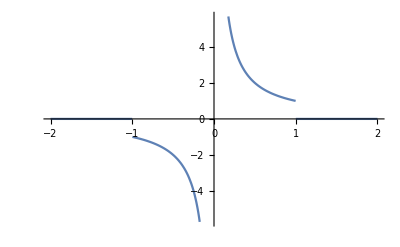

```mathematica
fTilde[xx]
Plot[fTilde[x],{x,-2,2}]
```

```mathematica
tea=FourierSinSeries[fTilde[x],x,N]
funcs={%/.N->5//Evaluate,%/.N->10//Evaluate,%/.N->20//Evaluate,%/.N->50//Evaluate,%/.N->200//Evaluate,fTilde[x]}
```

FourierSinSeries[Piecewise[{{(1-x,x)/x, x>0}, {(-x,x+1)/x, x<0}}],x,N]

{(2 1 sin(x))/π+(2 sin(5 x) 5)/π+(2 sin(4 x) 4)/π+(2 sin(3 x) 3)/π+(2 sin(2 x) 2)/π,(2 1 sin(x))/π+(2 sin(10 x) 10)/π+(2 sin(9 x) 9)/π+(2 sin(8 x) 8)/π+(2 sin(7 x) 7)/π+(2 sin(6 x) 6)/π+(2 sin(5 x) 5)/π+(2 sin(4 x) 4)/π+(2 sin(3 x) 3)/π+(2 sin(2 x) 2)/π,(2 1 sin(x))/π+(2 sin(20 x) 20)/π+(2 sin(19 x) 19)/π+(2 sin(18 x) 18)/π+(2 sin(17 x) 17)/π+(2 sin(16 x) 16)/π+(2 sin(15 x) 15)/π+(2 sin(14 x) 14)/π+(2 sin(13 x) 13)/π+(2 sin(12 x) 12)/π+(2 sin(11 x) 11)/π+(2 sin(10 x) 10)/π+(2 sin(9 x) 9)/π+(2 sin(8 x) 8)/π+(2 sin(7 x) 7)/π+(2 sin(6 x) 6)/π+(2 sin(5 x) 5)/π+(2 sin(4 x) 4)/π+(2 sin(3 x) 3)/π+(2 sin(2 x) 2)/π,(2 1 sin(x))/π+(2 sin(50 x) 50)/π+(2 sin(49 x) 49)/π+(2 sin(48 x) 48)/π+(2 sin(47 x) 47)/π+(2 sin(46 x) 46)/π+(2 sin(45 x) 45)/π+(2 sin(44 x) 44)/π+(2 sin(43 x) 43)/π+(2 sin(42 x) 42)/π+(2 sin(41 x) 41)/π+(2 sin(40 x) 40)/π+(2 sin(39 x) 39)/π+(2 sin(38 x) 38)/π+(2 sin(37 x) 37)/π+(2 sin(36 x) 36)/π+(2 sin(35 x) 35)/π+(2 sin(34 x) 34)/π+(2 sin(33 x) 33)/π+(2 sin(32 x) 32)/π+(2 sin(31 x) 31)/π+(2 sin(30 x) 30)/π+(2 sin(29 x) 29)/π+(2 sin(28 x) 28)/π+(2 sin(27 x) 27)/π+(2 sin(26 x) 26)/π+(2 sin(25 x) 25)/π+(2 sin(24 x) 24)/π+(2 sin(23 x) 23)/π+(2 sin(22 x) 22)/π+(2 sin(21 x) 21)/π+(2 sin(20 x) 20)/π+(2 sin(19 x) 19)/π+(2 sin(18 x) 18)/π+(2 sin(17 x) 17)/π+(2 sin(16 x) 16)/π+(2 sin(15 x) 15)/π+(2 sin(14 x) 14)/π+(2 sin(13 x) 13)/π+(2 sin(12 x) 12)/π+(2 sin(11 x) 11)/π+(2 sin(10 x) 10)/π+(2 sin(9 x) 9)/π+(2 sin(8 x) 8)/π+(2 sin(7 x) 7)/π+(2 sin(6 x) 6)/π+(2 sin(5 x) 5)/π+(2 sin(4 x) 4)/π+(2 sin(3 x) 3)/π+(2 sin(2 x) 2)/π,(2 1 sin(x))/π+(2 sin(200 x) 200)/π+(2 sin(199 x) 199)/π+(2 sin(198 x) 198)/π+(2 sin(197 x) 197)/π+(2 sin(196 x) 196)/π+(2 sin(195 x) 195)/π+(2 sin(194 x) 194)/π+(2 sin(193 x) 193)/π+(2 sin(192 x) 192)/π+(2 sin(191 x) 191)/π+(2 sin(190 x) 190)/π+(2 sin(189 x) 189)/π+(2 sin(188 x) 188)/π+(2 sin(187 x) 187)/π+(2 sin(186 x) 186)/π+(2 sin(185 x) 185)/π+(2 sin(184 x) 184)/π+(2 sin(183 x) 183)/π+(2 sin(182 x) 182)/π+(2 sin(181 x) 181)/π+(2 sin(180 x) 180)/π+(2 sin(179 x) 179)/π+(2 sin(178 x) 178)/π+(2 sin(177 x) 177)/π+(2 sin(176 x) 176)/π+(2 sin(175 x) 175)/π+(2 sin(174 x) 174)/π+(2 sin(173 x) 173)/π+(2 sin(172 x) 172)/π+(2 sin(171 x) 171)/π+(2 sin(170 x) 170)/π+(2 sin(169 x) 169)/π+(2 sin(168 x) 168)/π+(2 sin(167 x) 167)/π+(2 sin(166 x) 166)/π+(2 sin(165 x) 165)/π+(2 sin(164 x) 164)/π+(2 sin(163 x) 163)/π+(2 sin(162 x) 162)/π+(2 sin(161 x) 161)/π+(2 sin(160 x) 160)/π+(2 sin(159 x) 159)/π+(2 sin(158 x) 158)/π+(2 sin(157 x) 157)/π+(2 sin(156 x) 156)/π+(2 sin(155 x) 155)/π+(2 sin(154 x) 154)/π+(2 sin(153 x) 153)/π+(2 sin(152 x) 152)/π+(2 sin(151 x) 151)/π+(2 sin(150 x) 150)/π+(2 sin(149 x) 149)/π+(2 sin(148 x) 148)/π+(2 sin(147 x) 147)/π+(2 sin(146 x) 146)/π+(2 sin(145 x) 145)/π+(2 sin(144 x) 144)/π+(2 sin(143 x) 143)/π+(2 sin(142 x) 142)/π+(2 sin(141 x) 141)/π+(2 sin(140 x) 140)/π+(2 sin(139 x) 139)/π+(2 sin(138 x) 138)/π+(2 sin(137 x) 137)/π+(2 sin(136 x) 136)/π+(2 sin(135 x) 135)/π+(2 sin(134 x) 134)/π+(2 sin(133 x) 133)/π+(2 sin(132 x) 132)/π+(2 sin(131 x) 131)/π+(2 sin(130 x) 130)/π+(2 sin(129 x) 129)/π+(2 sin(128 x) 128)/π+(2 sin(127 x) 127)/π+(2 sin(126 x) 126)/π+(2 sin(125 x) 125)/π+(2 sin(124 x) 124)/π+(2 sin(123 x) 123)/π+(2 sin(122 x) 122)/π+(2 sin(121 x) 121)/π+(2 sin(120 x) 120)/π+(2 sin(119 x) 119)/π+(2 sin(118 x) 118)/π+(2 sin(117 x) 117)/π+(2 sin(116 x) 116)/π+(2 sin(115 x) 115)/π+(2 sin(114 x) 114)/π+(2 sin(113 x) 113)/π+(2 sin(112 x) 112)/π+(2 sin(111 x) 111)/π+(2 sin(110 x) 110)/π+(2 sin(109 x) 109)/π+(2 sin(108 x) 108)/π+(2 sin(107 x) 107)/π+(2 sin(106 x) 106)/π+(2 sin(105 x) 105)/π+(2 sin(104 x) 104)/π+(2 sin(103 x) 103)/π+(2 sin(102 x) 102)/π+(2 sin(101 x) 101)/π+(2 sin(100 x) 100)/π+(2 sin(99 x) 99)/π+(2 sin(98 x) 98)/π+(2 sin(97 x) 97)/π+(2 sin(96 x) 96)/π+(2 sin(95 x) 95)/π+(2 sin(94 x) 94)/π+(2 sin(93 x) 93)/π+(2 sin(92 x) 92)/π+(2 sin(91 x) 91)/π+(2 sin(90 x) 90)/π+(2 sin(89 x) 89)/π+(2 sin(88 x) 88)/π+(2 sin(87 x) 87)/π+(2 sin(86 x) 86)/π+(2 sin(85 x) 85)/π+(2 sin(84 x) 84)/π+(2 sin(83 x) 83)/π+(2 sin(82 x) 82)/π+(2 sin(81 x) 81)/π+(2 sin(80 x) 80)/π+(2 sin(79 x) 79)/π+(2 sin(78 x) 78)/π+(2 sin(77 x) 77)/π+(2 sin(76 x) 76)/π+(2 sin(75 x) 75)/π+(2 sin(74 x) 74)/π+(2 sin(73 x) 73)/π+(2 sin(72 x) 72)/π+(2 sin(71 x) 71)/π+(2 sin(70 x) 70)/π+(2 sin(69 x) 69)/π+(2 sin(68 x) 68)/π+(2 sin(67 x) 67)/π+(2 sin(66 x) 66)/π+(2 sin(65 x) 65)/π+(2 sin(64 x) 64)/π+(2 sin(63 x) 63)/π+(2 sin(62 x) 62)/π+(2 sin(61 x) 61)/π+(2 sin(60 x) 60)/π+(2 sin(59 x) 59)/π+(2 sin(58 x) 58)/π+(2 sin(57 x) 57)/π+(2 sin(56 x) 56)/π+(2 sin(55 x) 55)/π+(2 sin(54 x) 54)/π+(2 sin(53 x) 53)/π+(2 sin(52 x) 52)/π+(2 sin(51 x) 51)/π+(2 sin(50 x) 50)/π+(2 sin(49 x) 49)/π+(2 sin(48 x) 48)/π+(2 sin(47 x) 47)/π+(2 sin(46 x) 46)/π+(2 sin(45 x) 45)/π+(2 sin(44 x) 44)/π+(2 sin(43 x) 43)/π+(2 sin(42 x) 42)/π+(2 sin(41 x) 41)/π+(2 sin(40 x) 40)/π+(2 sin(39 x) 39)/π+(2 sin(38 x) 38)/π+(2 sin(37 x) 37)/π+(2 sin(36 x) 36)/π+(2 sin(35 x) 35)/π+(2 sin(34 x) 34)/π+(2 sin(33 x) 33)/π+(2 sin(32 x) 32)/π+(2 sin(31 x) 31)/π+(2 sin(30 x) 30)/π+(2 sin(29 x) 29)/π+(2 sin(28 x) 28)/π+(2 sin(27 x) 27)/π+(2 sin(26 x) 26)/π+(2 sin(25 x) 25)/π+(2 sin(24 x) 24)/π+(2 sin(23 x) 23)/π+(2 sin(22 x) 22)/π+(2 sin(21 x) 21)/π+(2 sin(20 x) 20)/π+(2 sin(19 x) 19)/π+(2 sin(18 x) 18)/π+(2 sin(17 x) 17)/π+(2 sin(16 x) 16)/π+(2 sin(15 x) 15)/π+(2 sin(14 x) 14)/π+(2 sin(13 x) 13)/π+(2 sin(12 x) 12)/π+(2 sin(11 x) 11)/π+(2 sin(10 x) 10)/π+(2 sin(9 x) 9)/π+(2 sin(8 x) 8)/π+(2 sin(7 x) 7)/π+(2 sin(6 x) 6)/π+(2 sin(5 x) 5)/π+(2 sin(4 x) 4)/π+(2 sin(3 x) 3)/π+(2 sin(2 x) 2)/π,Piecewise[{{(1-x,x)/x, x>0}, {(-x,x+1)/x, x<0}}]}

```mathematica
halfRange=0.03
windFunc[N_,y_]:=Piecewise[{{funcs[[N]],y-halfRange>0||y+halfRange<0},{0,True}}]
windFuncRMS[N_,y_]:=Piecewise[{{funcs[[N]]^2,y-halfRange>0||y+halfRange<0},{0,True}}]
```

0.03

```mathematica
windowed[N_,y_]:=NIntegrate[windFunc[N,y],{x,y-halfRange,y+halfRange}]/(2*halfRange)
windowedRMS[N_,y_]:=Sqrt[NIntegrate[windFuncRMS[N,y],{x,y-halfRange,y+halfRange}]/(2*halfRange)]
windowed[4,0.5]
```

0.667681

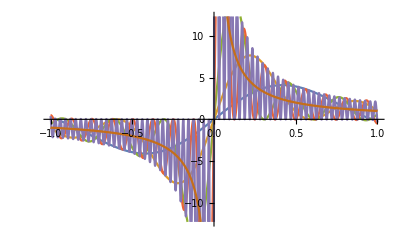

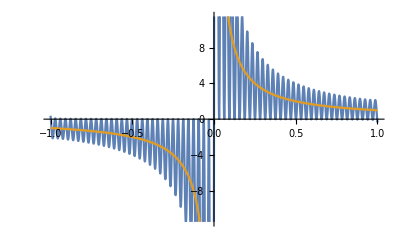

```mathematica
Plot[funcs,{x,-1,1}]
p1=Plot[{funcs[[5]],funcs[[6]]},{x,-1,1}]
```

```mathematica
dataa50=Table[{x,windowed[4,x]},{x,-1,1,0.05}]
dataa200=Table[{x,windowed[5,x]},{x,-1,1,0.05}]
(*dataaRMS=Table[{x,windowedRMS[4,x]},{x,-1,1,0.05}]*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

(-1. | 0.160265
-0.95 | -1.55554
-0.9 | -1.02064
-0.85 | -0.785987
-0.8 | -2.02407
-0.75 | -0.430496
-0.7 | -2.13041
-0.65 | -1.34262
-0.6 | -1.20567
-0.55 | -2.8719
-0.5 | -0.667681
-0.45 | -3.36704
-0.4 | -2.06669
-0.35 | -2.22282
-0.3 | -5.14985
-0.25 | -1.35971
-0.2 | -7.81733
-0.15 | -5.013
-0.1 | -9.28171
-0.05 | -31.2736
0. | 0.
0.05 | 31.2736
0.1 | 9.28171
0.15 | 5.013
0.2 | 7.81733
0.25 | 1.35971
0.3 | 5.14985
0.35 | 2.22282
0.4 | 2.06669
0.45 | 3.36704
0.5 | 0.667681
0.55 | 2.8719
0.6 | 1.20567
0.65 | 1.34262
0.7 | 2.13041
0.75 | 0.430496
0.8 | 2.02407
0.85 | 0.785987
0.9 | 1.02064
0.95 | 1.55554
1. | -0.160265)

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

(-1. | -0.543977
-0.95 | -1.03652
-0.9 | -1.09707
-0.85 | -1.21939
-0.8 | -1.19352
-0.75 | -1.38555
-0.7 | -1.40427
-0.65 | -1.52453
-0.6 | -1.72409
-0.55 | -1.73785
-0.5 | -2.08242
-0.45 | -2.18173
-0.4 | -2.48345
-0.35 | -2.96169
-0.3 | -3.18787
-0.25 | -4.18224
-0.2 | -4.96268
-0.15 | -6.59828
-0.1 | -10.9812
-0.05 | -21.0045
0. | 0.
0.05 | 21.0045
0.1 | 10.9812
0.15 | 6.59828
0.2 | 4.96268
0.25 | 4.18224
0.3 | 3.18787
0.35 | 2.96169
0.4 | 2.48345
0.45 | 2.18173
0.5 | 2.08242
0.55 | 1.73785
0.6 | 1.72409
0.65 | 1.52453
0.7 | 1.40427
0.75 | 1.38555
0.8 | 1.19352
0.85 | 1.21939
0.9 | 1.09707
0.95 | 1.03652
1. | 0.543977)

```mathematica
funcs[[5]];
NIntegrate[%,{x,0.1,1}]

fTilde[x]
NIntegrate[%,{x,0.1,1}]
```

2.1048

Piecewise[{{(1-x,x)/x, x>0}, {(-x,x+1)/x, x<0}}]

2.30259

```mathematica
FourierSinSeries
```

```mathematica
DiracDelta[u-v]HeavisideTheta[u,1-u,v,1-v]-DiracDelta[u+v]HeavisideTheta[u,1-u,-v,1+v]+PlusDistribution[HeavisideTheta[delta]/delta]HeavisideTheta[u,1-u,v,1-v]-PlusDistribution[HeavisideTheta[negDelta]/negDelta]HeavisideTheta[u,1-u,-v,1+v]//replSingVarPlus
%/.delta->u-v/.negDelta->v-u

FourierSinSeries[ % ,v,5,Assumptions->u∈Reals&&beta>0]

Plot3D[%,{u,0,1},{v,0,1},PlotRange->All]
```

-1-u,u,-v,v+1 (log(negDelta) negDelta-β+(negDelta-β)/negDelta)+1-u,u,1-v,v (log(δ) δ-β+(δ-β)/δ)+u-v 1-u,u,1-v,v-u+v 1-u,u,-v,v+1

1-u,u,1-v,v (log(u-v) u-v-β+(u-v-β)/(u-v))-1-u,u,-v,v+1 (log(v-u) u-v+β+(-u+v-β)/(v-u))+u-v 1-u,u,1-v,v-u+v 1-u,u,-v,v+1

$Aborted

$Aborted

```mathematica
Integrate[Sin[v]HeavisideTheta[u-v-beta]/(u-v),{v,-1,1},Assumptions->beta>0]
```

ConditionalExpression[-u-β-1 (1-u sin(u)--u sin(u)+u sin(u)-u+1 sin(u)+1-u cos(u)+u+1 cos(u))-(u-β-1-1) (-β sin(u)+u+1 sin(u)+cos(u) (β-u+1)),Im(u)==0∧(β>2∨Re(u)>1)∧(β≤2∨Re(u)+1>β)]

```mathematica
FourierSinSeries[DiracDelta[x-3],x,4]
```

(2 sin(3) sin(x))/π+(2 sin(6) sin(2 x))/π+(2 sin(9) sin(3 x))/π+(2 sin(12) sin(4 x))/π

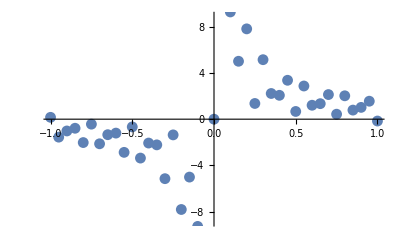

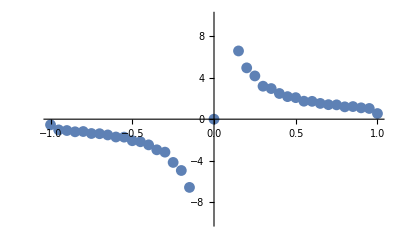

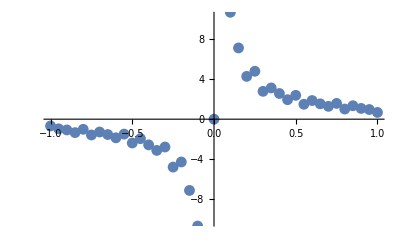

```mathematica
dPlot50=ListPlot[{dataa50}]
dPlot200=ListPlot[{dataa200}]
dPlotRMS=ListPlot[{dataa}]
```

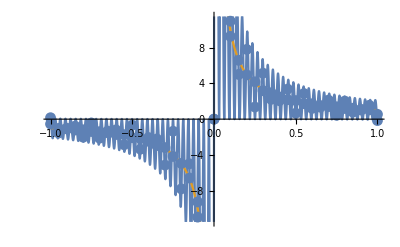

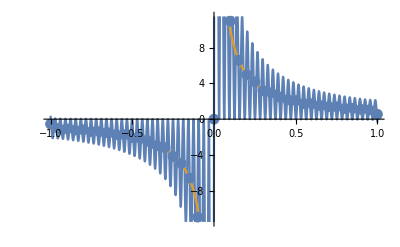

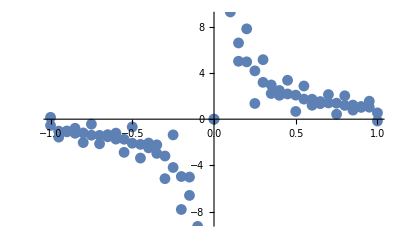

```mathematica
Show[p1,dPlot50,dPlot200]
Show[p1,dPlot200]
Show[{dPlot50,dPlot200}]
```

```mathematica
funcs//Length
funcs[[4]]
NIntegrate[%,{x,0.5,0.75}]
(*Sqrt[%]*)
fTilde[(0.5+0.625)/2]
funcs[[4]]/.x->(0.5+0.625)/2
```

5

(2 1 sin(x))/π+(2 50 sin(50 x))/π+(2 49 sin(49 x))/π+(2 48 sin(48 x))/π+(2 47 sin(47 x))/π+(2 46 sin(46 x))/π+(2 45 sin(45 x))/π+(2 44 sin(44 x))/π+(2 43 sin(43 x))/π+(2 42 sin(42 x))/π+(2 41 sin(41 x))/π+(2 40 sin(40 x))/π+(2 39 sin(39 x))/π+(2 38 sin(38 x))/π+(2 37 sin(37 x))/π+(2 36 sin(36 x))/π+(2 35 sin(35 x))/π+(2 34 sin(34 x))/π+(2 33 sin(33 x))/π+(2 32 sin(32 x))/π+(2 31 sin(31 x))/π+(2 30 sin(30 x))/π+(2 29 sin(29 x))/π+(2 28 sin(28 x))/π+(2 27 sin(27 x))/π+(2 26 sin(26 x))/π+(2 25 sin(25 x))/π+(2 24 sin(24 x))/π+(2 23 sin(23 x))/π+(2 22 sin(22 x))/π+(2 21 sin(21 x))/π+(2 20 sin(20 x))/π+(2 19 sin(19 x))/π+(2 18 sin(18 x))/π+(2 17 sin(17 x))/π+(2 16 sin(16 x))/π+(2 15 sin(15 x))/π+(2 14 sin(14 x))/π+(2 13 sin(13 x))/π+(2 12 sin(12 x))/π+(2 11 sin(11 x))/π+(2 10 sin(10 x))/π+(2 9 sin(9 x))/π+(2 8 sin(8 x))/π+(2 7 sin(7 x))/π+(2 6 sin(6 x))/π+(2 5 sin(5 x))/π+(2 4 sin(4 x))/π+(2 3 sin(3 x))/π+(2 2 sin(2 x))/π

0.404491

1.77778

3.57379

```mathematica
FourierSinCoefficient[fTilde[x],x,N]
Limit[%,N->Infinity]
%//Evaluate
```

(2 N)/π

1

1

```mathematica
Plot3D[gTilde[x,y],{x,-1,1},{y,-1,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[gTilde[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-